1
Programming with Mathematica

Exercises: Introduction to programming

Generate a random real number between one and one hundred. Then create a vector of twelve random numbers between one and one hundred. Finally, create a 4×4 array of such numbers and then compute the determinant of that array.

Using Table, create a 4×4 Hilbert matrix. The entry a_ij in row i, column j of the Hilbert matrix is given by 1/(i+j-1). Check your solution against the built-in HilbertMatrix.

Add the two lists, {1,2,3,4,5} and {2,4,6,8,10}. Then multiply them element-wise. Finally, multiply the two lists as vectors (dot product).

Generate a list of the ﬁrst twenty-ﬁve integers in ﬁve different ways.

Add the integers one through one thousand in as many different ways as you can.

A 2×2 matrix can be created using lists such as {{a,b},{c,d}}. Deﬁne a 2×2 numerical matrix and then ﬁnd its inverse, determinant, transpose, and trace.

Create the following matrix using list notation:

(1 | 1
1 | 0)

Then ﬁnd the inverse, determinant, and transpose of the matrix. Finally, compute the ﬁfth matrix power of this matrix (m.m.m.m.m).

Solutions

First, here is a random real number between one and one hundred.

```mathematica
RandomReal[{1,100}]
```

83.1802

This gives a vector of twelve such random numbers.

```mathematica
RandomReal[{1,100},{12}]
```

{91.5353,8.35684,68.0464,57.9997,37.9279,97.2452,62.8762,36.5797,4.61388,87.2442,58.6649,45.0762}

A 4×4 array of them.

```mathematica
RandomReal[{1,100},{4,4}]
```

{{71.1387,15.5669,32.9543,10.6077},{8.89123,59.9753,5.55336,92.4248},{31.9101,49.9324,51.6797,26.3127},{79.4064,50.808,4.1497,82.4448}}

And the determinant of this array.

```mathematica
Det[%]
```

-3.65557×10^6

The entry a_(i j) entry of the Hilbert matrix is deﬁned as 1/(i+j-1).

```mathematica
Table[1/(i+j-1),{j,4},{i,4}]
```

{{1,1/2,1/3,1/4},{1/2,1/3,1/4,1/5},{1/3,1/4,1/5,1/6},{1/4,1/5,1/6,1/7}}

Check against the built-in function.

```mathematica
HilbertMatrix[4]
```

{{1,1/2,1/3,1/4},{1/2,1/3,1/4,1/5},{1/3,1/4,1/5,1/6},{1/4,1/5,1/6,1/7}}

First, add the two lists.

```mathematica
{1,2,3,4,5}+{2,4,6,8,10}
```

{3,6,9,12,15}

To multiply the two lists, put a space between them.

```mathematica
{1,2,3,4,5}{2,4,6,8,10}
```

{2,8,18,32,50}

The dot product can be computed using either a built-in function or traditional mathematical notation.

```mathematica
Dot[{1,2,3,4,5},{2,4,6,8,10}]
```

110

```mathematica
{1,2,3,4,5}.{2,4,6,8,10}
```

110

First the straightforward ways of generating the list of the ﬁrst twenty-ﬁve integers.

```mathematica
Range[25]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

Here are two alternate syntaxes for the Range function, a preﬁx form and a postﬁx form:

```mathematica
Range@25
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
25//Range
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

Using Table:

```mathematica
Table[i,{i,1,25}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

The coefficients of the linear term in the ﬁrst 25 rows of the binomial expansion of (1+x)^n:

```mathematica
Table[Binomial[n,1],{n,1,25}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

A very roundabout (and not terribly efficient) way to do this: get the coefficients of the following series.

```mathematica
series=Series[1/(1-x)^2,{x,0,24}]
```

1+2 x+3 x^2+4 x^3+5 x^4+6 x^5+7 x^6+8 x^7+9 x^8+10 x^9+11 x^10+12 x^11+13 x^12+14 x^13+15 x^14+16 x^15+17 x^16+18 x^17+19 x^18+20 x^19+21 x^20+22 x^21+23 x^22+24 x^23+25 x^24+O[x]^25

```mathematica
CoefficientList[Normal[series],x]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

Several mathematical functions are built in that will compute the sum directly.

```mathematica
Sum[i,{i,10^3}]
```

500500

The same sum can be computed using familiar mathematical notation, templates for which are available from the Palettes menu.

```mathematica
∑_i^(10^3) i
```

500500

In fact the sum can be done in parallel (assuming you are working on a multi-core machine) by using a parallelized version of Sum.

```mathematica
ParallelSum[i,{i,10^3}]
```

500500

If you are already acquainted with an imperative style of programming, such as is found in procedural languages like C, Fortran, and Java, then the following looping constructs should be familiar.

```mathematica
i=0;
Do[i=i+j,{j,10^3}];
i
```

500500

```mathematica
res=0;
i=0;
For[i=1,i≤10^3,i++,res=i+res];
res
```

500500

```mathematica
res=0;
i=0;
While[i≤10^3,res=i+res;i++];
res
```

500500

A declarative style of programming – including functional languages such as Lisp, Haskell, Scheme, F♯ – is one in which functions are used to declare what the program should do, rather than giving explicit steps or actions to be performed. In such languages, computation is done by evaluating functions that operate on the appropriate inputs. In this case, the input is a list of the ﬁrst thousand positive integers; the semicolon is used to suppress the display of the output of that particular input.

```mathematica
lis=Range[10^3];
```

```mathematica
Apply[Plus,lis]
```

500500

```mathematica
Fold[Plus,0,lis]
```

500500

```mathematica
Last[Accumulate[lis]]
```

500500

```mathematica
Total[lis]
```

500500

Other approaches can be considered as well, including a recursive approach (Prolog, Haskell or Scheme), one using replacement rules, and another using sparse array arithmetic.

```mathematica
s[0]=0;
s[n_]:=s[n]=s[n-1]+n
```

```mathematica
s[1000]
```

500500

```mathematica
lis/.{x_,y__}:>x+y
```

500500

```mathematica
mat=SparseArray[{i_,i_}:>lis[[i]],{10^3,10^3}];
Tr[mat]
```

500500

One approach to computing the sum of the ﬁrst n integers is to use the fact (known to Gauss at a young age) that the sum is equal to the binomial (n+1
2).

```mathematica
n=10^3;
Binomial[n+1,2]
```

500500

Although all of these approaches give the same answer (they had better!), some are more efﬁcient in terms of memory management and some are faster than others. We don’t expect that these examples will all make sense to you at this point but after having read this book, you should be quite comfortable with each of these paradigms so that you can apply them to a wide variety of problems and choose the best approach for the programming problems you will encounter.

Here is a 2×2 matrix ﬁlled with numbers.

```mathematica
mat={{3,5},{1,2}};
```

And here are the operations on that matrix.

```mathematica
Inverse[mat]
```

{{2,-5},{-1,3}}

```mathematica
Det[mat]
```

1

```mathematica
Transpose[mat]
```

{{3,1},{5,2}}

```mathematica
Tr[mat]
```

5

Here is the list representation of the matrix given in the exercise.

```mathematica
mat={{1,1},{1,0}};
```

Here are the inverse, determinant, and transpose.

```mathematica
Inverse[mat]
```

{{0,1},{1,-1}}

```mathematica
Det[mat]
```

-1

```mathematica
Transpose[mat]
```

{{1,1},{1,0}}

As for the matrix power, you could write it out explicitly.

```mathematica
mat.mat.mat.mat.mat
```

{{8,5},{5,3}}

But that is tedious and wouldn’t be sensible for the 100th power say. Another built-in function can be used for the matrix power. You should see the Fibonacci numbers lurking in the output, a fact which is explored in Section 5.4.

```mathematica
MatrixPower[mat,5]
```

{{8,5},{5,3}}

```mathematica
MatrixPower[mat,100]
```

{{573147844013817084101,354224848179261915075},{354224848179261915075,218922995834555169026}}

```mathematica
Fibonacci[101]
```

573147844013817084101

```mathematica
Clear[s,lis,mat,n,i,res]
```

2
The Mathematica language

Exercises: Expressions

Determine if each of the following are atomic expressions. If the expression is not atomic, ﬁnd its head.

8/5

8/5+x

{{a,b},{c,d}}

"8/5 + x"

Give the full (internal) form of the expression a (b+c).

What is the traditional representation of Times[a,Power[Plus[b,c],-1]].

What is the part speciﬁcation of the symbol b in the expression a x^2+b x+c?

What will be the result of evaluating each of the following? Use FullForm on the expressions to help you understand their structures.

((x^2+y) z/w)[[2,1,2]]

(a/b)[[2,2]]

Use Level to ﬁnd all the factors in the following expression. Then ﬁnd all the terms inside the parentheses of the output.

```mathematica
expr=LegendreP[5,x]
```

1/8 (15 x-70 x^3+63 x^5)

Explain why the following expression returns an integer instead of displaying the internal representation of the fraction.

```mathematica
FullForm[12/4]
```

3

Modify the code for the one-dimensional random walk in this section to create two-dimensional random walks. In this case the step directions will be the vectors pointing in the compass directions, {0,1}, {0,-1}, {1,0}, and {-1,0}.

Solutions

The functions AtomQ, Head, and FullForm will help answer these questions.

The fraction 8/5 is atomic with head Rational.

```mathematica
{AtomQ[8/5],Head[8/5]}
```

{True,Rational}

The expression 8/5+x is not atomic. It is a normal expression with head Plus.

```mathematica
{AtomQ[8/5+x],Head[8/5+x],FullForm[8/5+x]}
```

{False,Plus,Plus[Rational[8,5],x]}

The list {{a,b},{c,d}} is not atomic. It has head List.

```mathematica
{AtomQ[{{a,b},{c,d}}],Head[{{a,b},{c,d}}]}
```

{False,List}

The string "8/5 + x" is atomic. It has head String.

```mathematica
{AtomQ["8/5+x"],Head["8/5+x"]}
```

{True,String}

The expression a (b+c) is given in full form as Times[a,Plus[b,c]].

This is simply a/(b+c) as can be seen by evaluating the full form expression.

```mathematica
Times[a,Power[Plus[b,c],-1]]
```

a/(b+c)

There are three elements in the expression; b x is the second element.

```mathematica
expr=a x^2+b x+c;
```

```mathematica
FullForm[expr]
```

Plus[c,Times[b,x],Times[a,Power[x,2]]]

The ﬁrst element of Times[b,x] is b, so the part speciﬁcation is 2,1.

```mathematica
expr[[2]]
```

b x

```mathematica
expr[[2,1]]
```

b

Looking at the internal representation of this expression with FullForm helps to unwind the part speciﬁcation.

Here is the internal representation of the expression:

```mathematica
FullForm[((x^2+y) z)/w]
```

Times[Power[w,-1],Plus[Power[x,2],y],z]

```mathematica
(((x^2+y) z)/w) [[2, 1, 2]]
```

2

From the FullForm of a/b, you can see that the second part is Power[b,-1] and the second part of that is -1. Note the need for parentheses here as the Part function has higher precedence than Power. For more information on operator precedence, see the tutorial Operator Input Forms (WLDC)

```mathematica
FullForm[a/b]
```

Times[a,Power[b,-1]]

```mathematica
(a/b)[[2,2]]
```

-1

At ﬁrst, you might try getting the expressions at level two as follows:

```mathematica
expr=LegendreP[5,x]
```

1/8 (15 x-70 x^3+63 x^5)

```mathematica
Level[expr,2]
```

{1/8,15 x,-70 x^3,63 x^5,15 x-70 x^3+63 x^5}

But that gets all the parts down to level two. To extract just those parts at level two, use a slightly different syntax with Level.

```mathematica
Level[expr,{2}]
```

{15 x,-70 x^3,63 x^5}

Mathematica evaluates arguments to functions before passing them up to the calling function. So the fraction ﬁrst evaluates to 3 and the head of 3 is of course Integer. To get the internal representation of the expression before it is evaluated, use Defer.

```mathematica
Defer[FullForm[12/4]]
```

Times[12,Power[4,-1]]

The directions are the two-dimensional lists that can be thought of as vectors pointing in the compass directions north, south, east, and west.

```mathematica
dirs={{0,1},{0,-1},{1,0},{-1,0}};
```

This picks a direction at random.

```mathematica
RandomChoice[dirs]
```

{1,0}

This chooses ﬁve such.

```mathematica
RandomChoice[dirs,5]
```

{{1,0},{0,1},{0,1},{-1,0},{0,-1}}

Here are the running sums, just like in the one-dimensional case.

```mathematica
Accumulate[%]
```

{{1,0},{1,1},{1,2},{0,2},{0,1}}

And here is the nested code to create a 25000-step two-dimensional random walk.

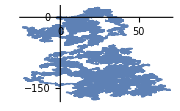

```mathematica
ListLinePlot[Accumulate[RandomChoice[dirs,25000]],PlotStyle->Thin]
```

Exercises: Numbers

Is the expression 2+π a number? Is it numeric? What is the difference?

Convert the base 10 integer 65 to base 2. Then convert back to base 10.

Deﬁne a function complexToPolar that converts complex numbers to their polar representations. Then, convert the numbers 3+3ⅈ and ⅇ^(πⅈ/3) to polar form.

Use NumberForm to display an approximate number with exactly four precise digits and three digits to the right of the decimal. Then use PaddedForm to display the numbers in the following vector with precisely two digits to the right of the decimal:

```mathematica
vec=RandomReal[{0,1},8]
```

{0.897363,0.629743,0.657265,0.959865,0.681584,0.706607,0.995883,0.111384}

Make a histogram of the frequencies of the ﬁrst 100000 digits of π. It is an open problem in number theory as to whether the digits are normal, meaning that each of the digits zero through nine occur with about the same frequency in the decimal expansion of π. See Bailey et al. (2012) for more information on normality and the digits of π.

Convert each of the characters in a string such as “Apple” to their eight-bit binary character code representation. For example, the character code for the letter A is 65:

```mathematica
ToCharacterCode["A"]
```

{65}

The eight-bit binary representation of 65 is 1000001, so your solution should return that base 2 number for the letter A. Binary representations of letters are used in certain ciphers such as the XOR cipher discussed in Exercise 5 of Section 7.1.

Graphs consist of a set of vertices and edges connecting some subset of those vertices. They are implemented in Mathematica with Graph, which takes two arguments: a list of vertices and a list of edges. Create a random graph on n vertices by choosing m edges from the Binomial[n, 2] possible edges. Such random graphs are commonly speciﬁed as G(n,m) and are essentially the model upon which the built-in RandomGraph is based.

Extract the ﬁrst 5000 digits in the decimal expansion of 1/17 or any other rational number. Then play them using ListPlay, which emits sound whose amplitude is given by the sequence of digits. Compare with the ﬁrst 5000 digits of π.

RandomReal by default outputs numbers uniformly distributed on the interval [0,1].

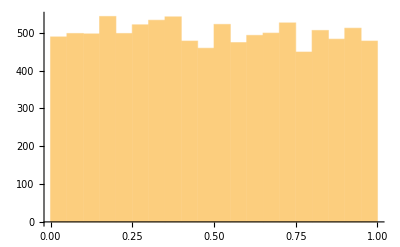

```mathematica
data=RandomReal[{0,1},{10^4}];
Histogram[data,15]
```

Bias the list of random numbers toward the lower end of this interval, giving a histogram similar to those in Figure Chapter.NumberedFigure.

Distributions of random number data biased toward the lower end of the interval [0,1].

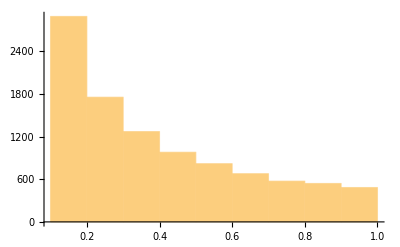
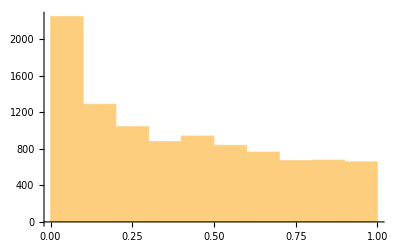
"   "-Graphics--Graphics-

Information theory, as conceived by Claude Shannon in the 1940s and 1950s, was originally interested in maximizing the amount of data that can be stored and retrieved over some channel such as a telephone line. Shannon devised a measure, now called entropy, that gives the theoretical maxima for such a signal. Entropy can be thought of as the average uncertainty of a single random variable and is computed by the following, where p(x) is the probability of event x over a domain X:

H(X)=-∑_(x∈X) p(x) log_2 p(x)

Generate a plot of the entropy (built into Mathematica as Entropy) as a function of success probability. You can simulate n trials of a coin toss with probability p using a Bernoulli distribution as follows:

```mathematica
RandomVariate[BernoulliDistribution[p],n]
```

Solutions

The expression 2+π is certainly numeric as both 2 and π are numeric.

```mathematica
NumericQ[2+π]
```

True

But it is not an explicit number because π is not an explicit number.

```mathematica
NumberQ[2+π]
```

False

This converts the base 2 representation of the number 65 to base 10.

```mathematica
2^^1000001
```

65

To go in the other direction, use BaseForm:

```mathematica
BaseForm[65,2]
```

1000001_2

This function gives the polar form as a list consisting of the magnitude and the polar angle.

```mathematica
complexToPolar[z_]:={Abs[z],Arg[z]}
```

```mathematica
complexToPolar[3+3 ⅈ]
```

{3 √2,π/4}

Check against a built-in function (introduced in Mathematica 10.1):

```mathematica
AbsArg[3+3 ⅈ]
```

{3 √2,π/4}

```mathematica
complexToPolar[ⅇ^((π ⅈ)/3)]
```

{1,π/3}

```mathematica
AbsArg[ⅇ^((π ⅈ)/3)]
```

{1,π/3}

Here is an approximation of π to 20-digit precision.

```mathematica
pi=N[π,20]
```

3.1415926535897932385

Display four precise digits with three digits to the right of the decimal point.

```mathematica
NumberForm[pi,{4,3}]
```

3.142

For the second part of the exercise, here is a vector of machine precision numbers.

```mathematica
vec=RandomReal[{0,1},8]
```

{0.650946,0.238017,0.664332,0.840782,0.211514,0.0455802,0.612099,0.228518}

This forces the display to use three digits in total with two digits to the right of the decimal.

```mathematica
PaddedForm[vec,{3,2}]
```

{ 0.65, 0.24, 0.66, 0.84, 0.21, 0.05, 0.61, 0.23}

To get the digits of π, use RealDigits.

```mathematica
RealDigits[N[π]]
```

{{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3},1}

What is returned is a list with the digits ﬁrst, followed by the exponent, 1. We are only interested in the ﬁrst sublist, so use First.

```mathematica
First[%]
```

{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3}

Here then, is a list of the ﬁrst 100000 digits of π, suppressing the display of the output using the semicolon.

```mathematica
pidigs=First[RealDigits[N[π,10^5]]];
```

This histogram shows that each of the digits zero through nine appear with about the same frequency. This is referred to as the normality of the digits of π (see Bailey et al. 2012).

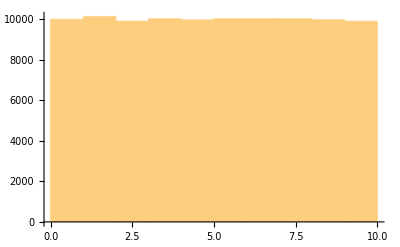

```mathematica
Histogram[pidigs]
```

First, here are the character codes of the letters in our test string, “Apple”.

```mathematica
ToCharacterCode["Apple"]
```

{65,112,112,108,101}

Here are the base two representation of each of the above character codes.

```mathematica
IntegerDigits[%,2]
```

{{1,0,0,0,0,0,1},{1,1,1,0,0,0,0},{1,1,1,0,0,0,0},{1,1,0,1,1,0,0},{1,1,0,0,1,0,1}}

Because the numbers are less than 128, the base two representation only have seven bits. To get the eight-bit representations, use a third argument to IntegerDigits.

```mathematica
IntegerDigits[ToCharacterCode["Apple"],2,8]
```

{{0,1,0,0,0,0,0,1},{0,1,1,1,0,0,0,0},{0,1,1,1,0,0,0,0},{0,1,1,0,1,1,0,0},{0,1,1,0,0,1,0,1}}

The built-in Graph function takes two arguments: a list of the vertex indices and a list of the edges. For a graph with n vertices, the vertex indices are simply the list of the integers one through n.

```mathematica
n=5;
vertices=Range[5]
```

{1,2,3,4,5}

For the edges, we need a list of all possible edges in a graph with n vertices. CompleteGraph[n] is a graph with all possible edges on n vertices so we can borrow that list from CompleteGraph.

```mathematica
edgesCG=EdgeList[CompleteGraph[n]]
```

{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

To randomly choose m of them, use RandomChoice. RandomChoice chooses elements with replacement. Note that nothing prohibits what are referred to as multi-graphs, that is, graphs where multiple edges exist between pairs of vertices.

```mathematica
RandomChoice[edgesCG,8]
```

{1<->3,4<->5,2<->5,2<->3,1<->4,2<->3,1<->2,1<->2}

To avoid multi-edges, use RandomSample which chooses without replacement. But you will need to keep the desired number of edges, m, smaller than Binomial[n, 2].

```mathematica
RandomSample[edgesCG,8]
```

{1<->5,3<->4,2<->3,1<->2,2<->4,2<->5,1<->3,3<->5}

This puts the pieces together and scales it up a bit. Repeated evaluation will cause different random graphs to be displayed, all with n vertices and m edges.

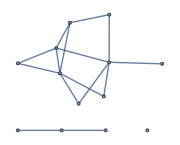

```mathematica
n=13;
m=15;
Graph[Range[n],RandomSample[EdgeList[CompleteGraph[n]],m]]
```

Also note that because we have used CompleteGraph, there are no self-edges, that is, an edge from a vertex to itself.

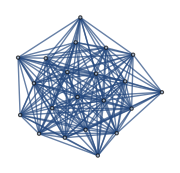

```mathematica
n=21;
m=167;
Graph[Range[n],RandomSample[EdgeList[CompleteGraph[n]],m]]
```

The built-in RandomGraph constructs only simple graphs – no multi-edges and no self loops, hence the total possible number of edges cannot exceed Binomial[n, 2].

```mathematica
RandomGraph[{21,211}]
```

RandomGraph::args: RandomGraph[{21, 211}] called with invalid parameters.

RandomGraph[{21,211}]

```mathematica
Binomial[21,2]
```

210

First, note that RealDigits returns a list with two elements, the digits and the exponent, in this case indicating that the ﬁrst digit starts one place to the right of the decimal point.

```mathematica
RealDigits[N[1/17,20]]
```

{{5,8,8,2,3,5,2,9,4,1,1,7,6,4,7,0,5,8,8,2},-1}

To get only the digits, use First.

```mathematica
First[%]
```

{5,8,8,2,3,5,2,9,4,1,1,7,6,4,7,0,5,8,8,2}

Here then are the ﬁrst 5000 digits of 1/17.

```mathematica
digs=First[RealDigits[N[1/17,5000]]];
```

And this plays them through the speakers of your computer.

```mathematica
ListPlay[digs]
```

-Graphics-

There are several ways that the random number sequences can be biased. First look at a picture of unbiased data. The random number generator uses a uniform probability distribution by default so we expect to see numbers uniformly distributed across the interval [0,1].

```mathematica
data=RandomReal[{0,1},{10^4}];
```

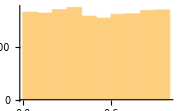

```mathematica
Histogram[data,10]
```

One way to bias the numbers toward zero is to transform them in such a way that they bunch around zero. Since these numbers are all less than one, raising them to a power will make them smaller.

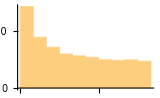
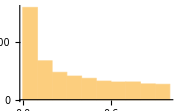

```mathematica
{Histogram[data^1.5,10,ImageSize->160],Histogram[data^2,10,ImageSize->160]}
```

Of course, choosing from a different distribution biases the numbers in a sense.

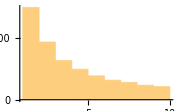

```mathematica
data=RandomVariate[BenfordDistribution[10],{10^4}];
Histogram[data,10]
```

In Chapters 3 and 9 we discuss listability, which will explain why we can raise every element in a vector to a power using the syntax above.

```mathematica
{a,b,c,d,e}^1.5
```

{a^1.5,b^1.5,c^1.5,d^1.5,e^1.5}

Run 10000 trials with a range of probabilities from zero to one in increments of .001. The table creates pairs consisting of p together with the entropy (in base 2) for each trial.

```mathematica
trials=10000;
incr=0.001;
info=Table[{p,Entropy[2,RandomVariate[BernoulliDistribution[p],trials]]},{p,0,1,incr}];
```

Make a plot.

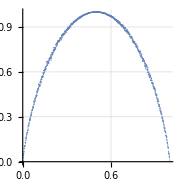

```mathematica
ListPlot[info,AspectRatio->1,GridLines->Automatic]
```

Exercises: Deﬁnitions

Create a function reciprocal[a/b] that returns the reciprocal of the fraction a/b. Check your solution with numeric and symbolic fractions and with fractions containing zero in the numerator.

Using Total, create a function to sum the ﬁrst n positive integers.

Create a function to compute the sum of the digits of any integer. Write an additional rule to give the sum of the base-b digits of an integer. Then use your function to compute the Hamming weight of any integer: the Hamming weight of an integer is given by the number of ones in the binary representation of that number. It has wide use in computer science (modular exponentiation and hash tables), cryptography, and coding theory (Knuth 2011).

Write a function sumsOfCubes[n] that takes a positive integer argument n and computes the sums of cubes of the digits of n (Hayes 1992).

What rules are created by each of the following functions? Check your predictions by evaluating them and then querying Mathematica with ?function_name.

randLis1[n_]:=RandomReal[1,{n}]

randLis2[n_]:=(x=RandomReal[];Table[x,{n}])

randLis3[n_]:=(x:=RandomReal[];Table[x,{n}])

randLis4[n_]=Table[RandomReal[],{n}]

Consider two functions f and g, which are identical except that one is written using an immediate assignment and the other using a delayed assignment.

```mathematica
f[n_]=Sum[(1+x)^j,{j,1,n}];
```

```mathematica
g[n_]:=Sum[(1+x)^j,{j,1,n}]
```

Explain why the outputs of these two functions look so different. Are they in fact different?

```mathematica
f[2]
```

((1+x) (-1+(1+x)^2))/x

```mathematica
g[2]
```

1+x+(1+x)^2

Write rules for a function log (note lowercase) that encapsulate the following identities:

log(a b)=log(a)+log(b);
log(a/b)=log(a)-log(b);
log(a^n)=n log(a).

Create a piecewise-deﬁned function g(x) based on the following; then plot the function from −2 to 0.

g(x)=Piecewise[{{−√(1−(x+2)^2), −2≤x≤−1}, {√(1−x^2), x<0}}]

The built-in function RotateRight rotates the elements in a list one place to the right, with the last element swinging around to the front.

```mathematica
RotateRight[{a,b,c,d,e}]
```

{e,a,b,c,d}

Create a function IntegerRotateRight[n] that takes an integer n and returns an integer with the original digits rotated one place to the right. Use this function to ﬁrst verify that 142857 is a divisor of its right rotation and then ﬁnd all such numbers less than one million (Project Euler, Problem #168).

The Champernowne constant is a famous number that is created by concatenating successive integers and interpreting them as decimal digits. For example, here are the ﬁrst 31 digits of the base-10 Champernowne number:

```mathematica
N[ChampernowneNumber[10],31]
```

0.123456789101112131415161718192

Concatenation can be used to generate integers also. Create a function to generate the nth Smarandache–Wellin number, formed by concatenating the digits of successive primes. The ﬁrst such number is 2, then 23, then 235, followed by 2357, 235711, and so on. Numerous open questions exist about these numbers: for example, it is not known if an inﬁnite number of them are prime; see Crandall and Pomerance (2005) and Sloane (A019518).

Solutions

Note that simply giving the reciprocal on the right-hand side does not work.

```mathematica
reciprocal[a_/b_]:=b/a
```

```mathematica
reciprocal[3/4]
```

4/3

Look at the internal form to see why the pattern matcher failed to match 3/4 with a_/b_.

```mathematica
FullForm[3/4]
```

Rational[3,4]

So a better approach is to use the internal form of such fractions.

```mathematica
reciprocal[Rational[a_,b_]]:=Rational[b,a]
```

Alternatively, match with the head.

```mathematica
reciprocal[z_Rational]:=Denominator[z]/Numerator[z]
```

This works for numeric and symbolic fractions.

```mathematica
reciprocal[3/4]
```

4/3

```mathematica
reciprocal[z/(x+y)]
```

(x+y)/z

But there is an issue with fractions containing zero in the numerator.

```mathematica
reciprocal[0/5]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

We will wait until Section 2.4 to resolve this issue.

Generate the list of integers 1 through n, then total that list.

```mathematica
sumInts[n_]:=Total[Range[n]]
```

```mathematica
sumInts[100]
```

5050

```mathematica
sumInts[1000]
```

500500

We have not been careful to check that the arguments are positive integers here. See Section 4.1 for a discussion of patterns used to perform argument checking on your functions.

Once you have a list of the digits in any integer (IntegerDigits), simply total the list.

```mathematica
DigitSum[n_]:=Total[IntegerDigits[n]]
```

```mathematica
DigitSum[10!]
```

27

One rule can cover both parts of this exercise, using a default value of 10 for the base (see Section 5.4 for a discussion of default values).

```mathematica
DigitSum[n_,base_:10]:=Total[IntegerDigits[n,base]]
```

The Hamming weight of a number is the number of ones in its binary representation.

```mathematica
DigitSum[2^31-1,2]
```

31

Here is a comparison with a built-in function:

```mathematica
DigitCount[2^31-1,2,1]
```

31

Here is the sumsOfCubes function.

```mathematica
sumsOfCubes[n_Integer]:=Total[IntegerDigits[n]^3]
```

```mathematica
sumsOfCubes[124]
```

73

This exercise focuses on the difference between immediate and delayed assignments.

This will generate a list of n random numbers.

```mathematica
randLis1[n_]:=RandomReal[1,{n}]
```

```mathematica
randLis1[3]
```

{0.726437,0.820623,0.349356}

Since the deﬁnition for x is an immediate assignment, its value does not change in Table. But each time randLis2 is called, a new value is assigned to x.

```mathematica
randLis2[n_]:=(x=RandomReal[];Table[x,{n}])
```

```mathematica
randLis2[3]
```

{0.974798,0.974798,0.974798}

```mathematica
randLis2[3]
```

{0.621851,0.621851,0.621851}

Because the deﬁnition for x is a delayed assignment, the deﬁnition for randLis3 is functionally equivalent to randLis1.

```mathematica
randLis3[n_]:=(x:=RandomReal[];Table[x,{n}])
```

```mathematica
randLis3[3]
```

{0.412708,0.253301,0.361384}

In an immediate assignment, the right-hand side of the deﬁnition is evaluated ﬁrst. But in this case, n does not have a value, so Table is not able to evaluate properly.

```mathematica
randLis4[n_]=Table[RandomReal[],{n}]
```

{0.138356,0.374127,0.873417,0.769375,0.0394529,0.983081,0.160601,0.982007,0.191435,0.744383,0.761298,0.311281,0.461935,0.525905,0.921668,0.41622,0.442365,0.389952,0.171867,0.992726,0.406445}

```mathematica
Clear[x,n]
```

The deﬁnition for f given in the exercise evaluates the sum ﬁrst (immediate assignment), giving a symbolic expression for the general sum from 1 to n. When f[2] is evaluated, the argument 2 is then substituted into this expression for n. In the case of g, the value of n is substituted and then the sum is evaluated. Although the resulting expressions output by these two functions look different at ﬁrst, expanding them gives the same result.

```mathematica
f[n_]=Sum[(1+x)^j,{j,1,n}]
```

((1+x) (-1+(1+x)^n))/x

```mathematica
g[n_]:=Sum[(1+x)^j,{j,1,n}]
```

```mathematica
Expand[f[2]]
```

2+3 x+x^2

```mathematica
Expand[g[2]]
```

2+3 x+x^2

The rules for the logarithm function are as follows. Note, there is no need to program the division rule separately. Do you see why? (Look at FullForm[x/y].)

```mathematica
log[a_*b_]:=log[a]+log[b]
```

```mathematica
log[a_^n_]:=n log[a]
```

```mathematica
log[x y^2 z^3]
```

log[x]+2 log[y]+3 log[z]

```mathematica
log[x/y]
```

log[x]-log[y]

Using Piecewise, we have:

```mathematica
g[x_]:=Piecewise[{{-1 √(1-(x+2)^2),-2≤x≤-1},{√(1-x^2),x<0}}]
```

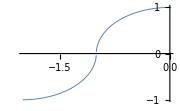

```mathematica
Plot[g[x],{x,-2,0}]
```

First get a list of the digits of the integer.

```mathematica
IntegerDigits[142857]
```

{1,4,2,8,5,7}

Next rotate the list using RotateRight.

```mathematica
RotateRight[IntegerDigits[142857]]
```

{7,1,4,2,8,5}

Reconstruct the number from the list of digits using FromDigits.

```mathematica
FromDigits[RotateRight[IntegerDigits[142857]]]
```

714285

Here is the function:

```mathematica
IntegerRotateRight[n_Integer]:=FromDigits[RotateRight[IntegerDigits[n]]]
```

And this shows that 142857 is a divisor of its right rotation (third divisor from the end):

```mathematica
Divisors[IntegerRotateRight[142857]]
```

{1,3,5,9,11,13,15,27,33,37,39,45,55,65,99,111,117,135,143,165,185,195,297,333,351,407,429,481,495,555,585,715,999,1221,1287,1443,1485,1665,1755,2035,2145,2405,3663,3861,4329,4995,5291,6105,6435,7215,10989,12987,15873,18315,19305,21645,26455,47619,54945,64935,79365,142857,238095,714285}

```mathematica
MemberQ[Divisors[IntegerRotateRight[142857]],142857]
```

True

Here are all the integers less than one million that satisfy this property; most are palindromes (see Chapter 5 for discussion of Select and also pure functions).

```mathematica
Select[Range[10,10^6],MemberQ[Divisors[IntegerRotateRight[#]],#]&]
```

{11,22,33,44,55,66,77,88,99,111,222,333,444,555,666,777,888,999,1111,2222,3333,4444,5555,6666,7777,8888,9999,11111,22222,33333,44444,55555,66666,77777,88888,99999,102564,111111,128205,142857,153846,179487,205128,222222,230769,333333,444444,555555,666666,777777,888888,999999}

One approach to creating these numbers is to use IntegerDigits to extract the digits of successive primes and then use FromDigits to concatenate this list of digits.

To prototype, get the digits from the ﬁrst ten prime numbers.

```mathematica
Table[Prime[i],{i,10}]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
IntegerDigits[%]
```

{{2},{3},{5},{7},{1,1},{1,3},{1,7},{1,9},{2,3},{2,9}}

(As an aside, the above works because IntegerDigits is listable and hence automatically maps across lists.)

Next, ﬂatten the output from IntegerDigits and turn that list into a number using FromDigits.

```mathematica
Flatten[%]
```

{2,3,5,7,1,1,1,3,1,7,1,9,2,3,2,9}

```mathematica
FromDigits[%]
```

2357111317192329

Here then is a function that creates the nth Smarandache-Wellin number.

```mathematica
SmarandacheWellin[n_]:=FromDigits[Flatten[IntegerDigits@Table[Prime[i],{i,n}]]]
```

And here are the ﬁrst ten such numbers.

```mathematica
Table[SmarandacheWellin[i],{i,10}]
```

{2,23,235,2357,235711,23571113,2357111317,235711131719,23571113171923,2357111317192329}

Which are prime numbers themselves?

```mathematica
Select[%,PrimeQ]
```

{2,23,2357}

And here is a really big Smarandache-Wellin prime.

```mathematica
SmarandacheWellin[1429]//N
```

2.35711131719233×10^5718

```mathematica
PrimeQ[SmarandacheWellin[1429]]
```

True

In Section 7.2 we will look at an alternative approach to constructing these numbers using string functions.

Exercises: Predicates and Boolean operations

Create a predicate function that returns a value of True if its argument is between -1 and 1.

Deﬁne a predicate function StringCharacterQ[str] that returns True if its argument str is a single string character, and returns False otherwise.

Write a predicate function NaturalQ[n] that returns a value of True if n is a natural number and a value of False otherwise, that is, NaturalQ[n] gives True if n is among 0, 1, 2, 3, ….

Create a predicate function, SquareNumberQ[n] that returns True if n is a square number, such as 1, 4, 9, 16,….

Create a predicate function TriangularNumberQ[t] that returns True whenever its argument t is a triangular number. The nth triangular number T_n is given by the formula

T_n=∑_(k=1)^n k =1+2+3+⋯+n=(n(n+1))/2=(n+1
2)

Based on the solution to the two previous exercises, create a predicate function SquareTriangularNumberQ[n] that returns a value of True if n is both a square number and a triangular number. Then use this predicate to ﬁnd all square triangular numbers less than one million.

Create a predicate function RealPositiveQ[x] that returns a value of True if x is a positive real number (“real” in the mathematical sense, i.e., x∈ℝ). Add a second rule that accepts vectors as arguments and returns True if every element of the vector argument is a positive real number.

The built-in function CoprimeQ[a,b] returns True if a and b are relatively prime (share no common factors other than 1) and returns False otherwise. Use ArrayPlot to visualize pairs of relatively prime numbers from 1 to 100. Use Boole to convert the table of True/False values returned by CoPrimeQ to zeros and ones.

An undirected graph gr is considered dense if the number of edges in gr is close to the maximum number of edges. The maximum for a graph with n edges occurs when every pair of vertices is connected by an edge and, assuming no self-loops and no multi-edges, is given by the number of two-element subsets of n objects, Binomial[n, 2]. The density 𝒟 of a graph can be deﬁned as

𝒟=(|E|)/(|V| (|V| - 1))

where |E| is the number of edges and |V| is the number of vertices (given by EdgeCount and VertexCount, respectively). A graph with all possible edges has a density of 1 and a graph with no edges has density 0. Although there are differences of opinion as to where the cutoff is, assume that a graph is dense if its density is greater than or equal to 0.5.

Deﬁne a function DenseGraphQ[gr] that returns a value of True if gr is dense in the above sense and returns a value of False otherwise. As tests, DenseGraphQ should give True for CompleteGraph[n] for any n and it should return False for RandomGraph[BernoulliGraphDistribution[n,pr]] for small probabilities pr.

Solutions

There are several ways to deﬁne this function, either using the relational operator for less than, or with the absolute value function.

```mathematica
f[x_]:=-1<x<1
```

```mathematica
f[x_]:=Abs[x]<1
```

```mathematica
f[4]
```

False

```mathematica
f[-0.35]
```

True

The requirements here are that the argument be both a string (StringQ) and have length (StringLength) one.

```mathematica
StringCharacterQ[ch_]:=StringQ[ch]&&StringLength[ch]==1
```

```mathematica
StringCharacterQ["v"]
```

True

```mathematica
StringCharacterQ["vi"]
```

False

```mathematica
StringCharacterQ[v]
```

False

A number n can be considered a natural number if it is both an integer and greater than or equal to zero. There is some historical precedent for not including zero, but most mathematicians and computer scientists now include it and so for our purposes, we will adopt the convention that zero is a natural number.

```mathematica
NaturalQ[n_]:=IntegerQ[n]&&n≥0
```

```mathematica
NaturalQ[0]
```

True

```mathematica
NaturalQ[-4]
```

False

To check that a number is a perfect square, it is sufﬁcient to see if its square root is an integer.

```mathematica
SquareNumberQ[n_]:=IntegerQ[√n]
```

```mathematica
SquareNumberQ[10]
```

False

```mathematica
Select[Range[100],SquareNumberQ]
```

{1,4,9,16,25,36,49,64,81,100}

Since any triangular number T is equal to n(n+1)/2 for some n, a bit of algebraic manipulation gives:

2T=n^2+n
8T=4 n^2+4n

Completing the square gives:

8T+1=4 n^2+4n+1
=(2n+1)^2

So, T is triangular if and only if 8T+1 is an odd perfect square. Here then is the test.

```mathematica
TriangularNumberQ[t_]:=OddQ[√(8t+1)]&&SquareNumberQ[8t+1]
```

```mathematica
TriangularNumberQ[6]
```

True

```mathematica
TriangularNumberQ[55]
```

True

```mathematica
TriangularNumberQ[56]
```

False

Combine the previous two solutions with a conjunction.

```mathematica
SquareTriangularNumberQ[n_]:=TriangularNumberQ[n]&&SquareNumberQ[n]
```

```mathematica
Select[Range[1000000],SquareTriangularNumberQ]
```

{1,36,1225,41616}

First, create a predicate that checks if a single number is real and positive.

```mathematica
RealPositiveQ[n_?NumericQ]:=Im[n]==0&&Positive[n]
```

```mathematica
Select[{-4,23,3+4I,π},RealPositiveQ]
```

{23,π}

Now, add a rule that checks if a vector consists entirely of numbers that are real and positive. AllTrue[expr,test] applies the test to each of the elements in expr and returns True if all of them are true.

```mathematica
RealPositiveQ[vec_?VectorQ]:=AllTrue[vec,RealPositiveQ]
```

```mathematica
RealPositiveQ[{-4,23,3+4I,π}]
```

False

Actually we can make this code a bit more compact by using the two-argument form of VectorQ. The second argument is a predicate that tests each element of the vector calling the one argument form of RealPositiveQ.

```mathematica
Clear[RealPositiveQ];
RealPositiveQ[n_?NumericQ]:=Im[n]==0&&Positive[n]
```

```mathematica
RealPositiveQ[vec_]:=VectorQ[vec,RealPositiveQ]
```

Wrapping the table produced by CoprimeQ in Boole converts the true/false values to zeros and ones, which is what ArrayPlot needs.

```mathematica
ArrayPlot[Boole[Table[CoprimeQ[a,b],{a,100},{b,100}]]]
```

-Graphics-

Given the deﬁnition of graph density in the exercise, here is an implementation that takes a graph as an argument.

```mathematica
DenseGraphQ[gr_Graph]:=2EdgeCount[gr]/(VertexCount[gr](VertexCount[gr]-1))≥0.5
```

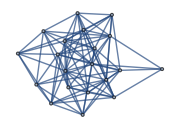

```mathematica
gr=RandomGraph[{20,90}]
```

```mathematica
DenseGraphQ[gr]
```

False

Complete graphs are dense as they have all possible edges.

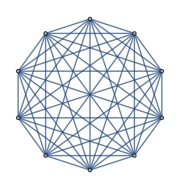

```mathematica
CompleteGraph[10]
```

```mathematica
DenseGraphQ[%]
```

True

Actually, there is a built-in function that gives the density explicitly.

```mathematica
GraphDensity[CompleteGraph[10]]
```

1

```mathematica
GraphDensity[gr]
```

9/19

So an simpler deﬁnition would just use that.

```mathematica
DenseGraphQ[gr_Graph]:=GraphDensity[gr]≥0.5
```

Exercises: Attributes

Ordinarily, when you deﬁne a function, it has no attributes. The arguments are evaluated before being passed up to the calling function. So, in the following case, 2+3 is evaluated before it is passed to g.

```mathematica
g[x_+y_]:=x^2+y^2
```

```mathematica
g[2+3]
```

g[5]

Use one of the Hold attributes to give g the property that its argument is not evaluated ﬁrst. The resulting output should look like this:

```mathematica
g[2+3]
```

13

Deﬁne a function that takes each number, x, in a vector of numbers and returns x if it is within a certain interval, say -0.5<x<0.5, and returns √x otherwise. Then make your function listable so that it can operate on vectors (lists) directly.

The deﬁnitions used in the solution to Exercise ExerciseItem of Section Chapter.3 for the reciprocal function failed to properly deal with the special case of zero in the numerator.

```mathematica
reciprocal[Rational[a_,b_]]:=Rational[b,a]
```

```mathematica
reciprocal[0/5]
```

reciprocal[0]

Correct this problem by giving reciprocal the appropriate attribute.

Solutions

First clear any deﬁnitions and attributes that might be associated with g.

```mathematica
ClearAll[g]
```

Then set the HoldAll attribute to prevent initial evaluation of the argument of this function.

```mathematica
SetAttributes[g,HoldAll]
```

```mathematica
g[x_+y_]:=x^2+y^2
```

```mathematica
g[a+b]
```

a^2+b^2

```mathematica
g[2+3]
```

13

Here is a small list of random numbers to use.

```mathematica
vec=RandomReal[{-1,1},10]
```

{-0.798986,-0.84542,-0.747004,-0.44054,0.117601,-0.243944,-0.227587,0.994751,-0.107316,0.692977}

The function could be set up to take two arguments, the number and the bound.

```mathematica
fun[x_?NumberQ,bound_]:=If[-bound<x<bound,x,√x]
```

Make fun listable.

```mathematica
SetAttributes[fun,Listable]
```

```mathematica
fun[vec,0.5]
```

{0.+0.89386 ⅈ,0.+0.919467 ⅈ,0.+0.864294 ⅈ,-0.44054,0.117601,-0.243944,-0.227587,0.997372,-0.107316,0.832452}

First, here is the original deﬁnition for reciprocal.

```mathematica
reciprocal[z_Rational]:=Denominator[z]/Numerator[z]
```

```mathematica
reciprocal[0/5]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

Give it the HoldAll attribute to prevent fractions such from ﬁrst evaluating and being reduced.

```mathematica
SetAttributes[reciprocal,HoldAll]
```

```mathematica
reciprocal[z_Rational]:=Denominator[z]/Numerator[z]
```

```mathematica
reciprocal[0/5]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

We have resolved one problem, but a new one arises. The unevaluated form of 0/5 is in fact not a Rational. It will become Rational once it is evaluated.

```mathematica
FullForm[HoldForm[0/5]]
```

HoldForm[Times[0,Power[5,-1]]]

So, one more rule is needed to cover this situation.

```mathematica
reciprocal[Times[a_,Power[b_,-1]]]:=b/a
```

```mathematica
reciprocal[0/5]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
reciprocal[2/3]
```

3/2

In fact, this last rule now handles more complicated rational expressions such as the following.

```mathematica
reciprocal[x/(y+z)]
```

(y+z)/x

```mathematica
Clear[f,fun,vec,gr]
```

3
Lists and associations

Exercises: Creating and displaying lists

Create a list of the multiples of ﬁve less than or equal to one hundred.

Create a list of the reciprocals of the powers of two as the powers go from zero to sixteen.

Generate the list {{0},{0,2},{0,2,4},{0,2,4,6},{0,2,4,6,8}} in two different ways using the Table function.

Generate both of the following arrays using the Table function:

```mathematica
Array[f,5]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Array[f,{3,4}]
```

{{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2],f[2,3],f[2,4]},{f[3,1],f[3,2],f[3,3],f[3,4]}}

Use Table to create an n×n matrix consisting of the positive integers one through n^2 arranged such that the ﬁrst row is the list {1,2,3,…,n}, the second row is the list {1+n,2+n,3+n,…,2n}, and in general the kth row is the list {1+(k-1) n,2+(k-1) n,3+(k-1) n,…,n^2}. For example, for n=4, you should have

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}}

In matrix form, this would be:

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16)

Using Table, create a symmetric matrix of the binomial coefﬁcients for any n similar to that in Table Chapter.NumberedTable.

Pascal’s matrix for n=5

(1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 4 | 5
1 | 3 | 6 | 10 | 15
1 | 4 | 10 | 20 | 35
1 | 5 | 15 | 35 | 70)

Given an m×m square lattice like the grid graph below, color all vertices on the bottom red, and on the top white. Your solution should be as general as possible, so that changing the size of the lattice (changing the value of m) will still work to color the lattice.

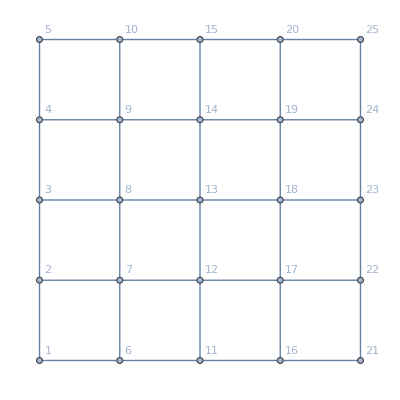

```mathematica
m=5;
GridGraph[{m,m},VertexLabels->"Name"]
```

To change the property of select vertices in a graph, use HighlightGraph. For example, the following colors vertices 1, 13, and 25 red.

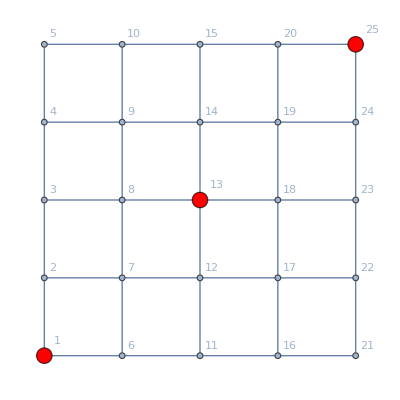

```mathematica
HighlightGraph[
GridGraph[{m,m},VertexLabels->"Name"],
Style[{1,13,25},Red], VertexSize->Medium]
```

Import six images, resize them to the same dimensions, then display them inside a 3×2 grid using options for Grid to format the output.

Construct an integer lattice graphic like in Figure Chapter.NumberedFigure. Start by creating a list of the pairs of coordinate points. Then connect the appropriate pairs of coordinates with lines (use Graphics[Line[…]]). Add points with Graphics[Point[…]]. See Chapter 8 for details about creating plots from graphics primitives. Consider the function CoordinateBoundsArray to get the list of integer coordinates.

A 5×3 rectangular lattice.

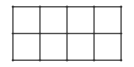

Solutions

Using Table, here are the multiples of 5.

```mathematica
Table[5j,{j,1,100/5}]
```

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

This can also be done with Range.

```mathematica
Range[5,100,5]
```

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

Here are the reciprocals of the powers of two.

```mathematica
Table[1/2^i,{i,0,16}]
```

{1,1/2,1/4,1/8,1/16,1/32,1/64,1/128,1/256,1/512,1/1024,1/2048,1/4096,1/8192,1/16384,1/32768,1/65536}

```mathematica
1/(2^Range[0,16])
```

{1,1/2,1/4,1/8,1/16,1/32,1/64,1/128,1/256,1/512,1/1024,1/2048,1/4096,1/8192,1/16384,1/32768,1/65536}

You can take every other element in the iterator list, or encode that in the expression 2 j.

```mathematica
Table[j,{i,0,8,2},{j,0,i,2}]
```

{{0},{0,2},{0,2,4},{0,2,4,6},{0,2,4,6,8}}

```mathematica
Table[2 j,{i,0,4},{j,0,i}]
```

{{0},{0,2},{0,2,4},{0,2,4,6},{0,2,4,6,8}}

These lists can be generated with Table, using two iterators for the second example.

```mathematica
Table[f[i],{i,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Table[f[i,j],{i,3},{j,4}]
```

{{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2],f[2,3],f[2,4]},{f[3,1],f[3,2],f[3,3],f[3,4]}}

There are numerous ways to create this array. Here is one approach:

```mathematica
n=4;
Table[1+i+j,{j,0,n^2-1,n},{i,0,n-1}]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}}

But in fact, a more direct implementation using the statement of the problem, gives the following:

```mathematica
n=4;
Table[j+k n,{k,0,n-1},{j,1,n}]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}}

```mathematica
MatrixForm[%]
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16)

The binomial coefficients can be generated with Binomial. For example here are the coefficients in the expansion of (1+x)^5:

```mathematica
Table[Binomial[5,k],{k,0,5}]
```

{1,5,10,10,5,1}

```mathematica
Expand[(1+x)^5]
```

1+5 x+10 x^2+10 x^3+5 x^4+x^5

So to get all coefficients for exponent n, as n runs from one to six say, we need a second iterator for Table. A bit of thought is needed to determine which iterator list comes ﬁrst and to make j dependent upon n.

```mathematica
n=6;
Table[Binomial[j,i],{i,0,n-1},{j,i,n+i-1}]
```

{{1,1,1,1,1,1},{1,2,3,4,5,6},{1,3,6,10,15,21},{1,4,10,20,35,56},{1,5,15,35,70,126},{1,6,21,56,126,252}}

```mathematica
MatrixForm[%]
```

(1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 4 | 5 | 6
1 | 3 | 6 | 10 | 15 | 21
1 | 4 | 10 | 20 | 35 | 56
1 | 5 | 15 | 35 | 70 | 126
1 | 6 | 21 | 56 | 126 | 252)

First, here is the grid graph:

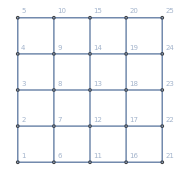

```mathematica
m=5;
gg=GridGraph[{m,m},VertexLabels->"Name"]
```

Since this is a square grid, the vertex numbers on the top of the lattice are multiples of m up to m^2.

```mathematica
top=Range[m,m^2,m]
```

{5,10,15,20,25}

The bottom vertices range from one to m^2-m+1 in increments of m.

```mathematica
bot=Range[1,m^2-m+1,m]
```

{1,6,11,16,21}

To change the properties of a set of vertices, use Style.

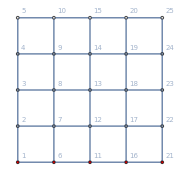

```mathematica
HighlightGraph[GridGraph[{m,m},VertexLabels->"Name"],{Style[bot,Red],Style[top,White]}]
```

Changing the size of the lattice should not trigger a need to change the code.

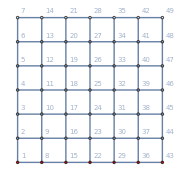

```mathematica
m=7;
top=Range[m,m^2,m];
bot=Range[1,m^2-m+1,m];
HighlightGraph[GridGraph[{m,m},VertexLabels->"Name"],{Style[bot,Red],Style[top,White]}]
```

Here are some sample images to work with.

```mathematica
images=Map[ExampleData,{{"TestImage","Girl2"},{"TestImage","Peppers"},{"TestImage","Aerial"},{"TestImage","Moon"},{"TestImage","Tank2"},{"TestImage","Ruler"}}];
```

Get their dimensions.

```mathematica
Map[ImageDimensions,images]
```

{{256,256},{512,512},{256,256},{256,256},{512,512},{512,512}}

Resize the larger images.

```mathematica
img1=images[[1]];
img2=ImageResize[images[[2]],256];
img3=images[[3]];
img4=images[[4]];
img5=ImageResize[images[[5]],256];
img6=ImageResize[images[[6]],256];
```

Finally, put in a grid with some formatting.

```mathematica
Grid[{
{img1,img2,img3},
{img4,img5,img6}
},Frame->All,Spacings->{1,1},ItemSize->{3,3}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

A bit of thought is needed to get the iterators right using Table.

```mathematica
xmin=-2;xmax=2;ymin=-1;ymax=1;
hlines=Table[{{xmin,y},{xmax,y}},{y,ymin,ymax}]
```

{{{-2,-1},{2,-1}},{{-2,0},{2,0}},{{-2,1},{2,1}}}

```mathematica
vlines=Table[{{x,ymin},{x,ymax}},{x,xmin,xmax}]
```

{{{-2,-1},{-2,1}},{{-1,-1},{-1,1}},{{0,-1},{0,1}},{{1,-1},{1,1}},{{2,-1},{2,1}}}

Join the two sets of lines and then ﬂatten to remove one set of braces.

```mathematica
pairs=Flatten[{hlines,vlines},1]
```

{{{-2,-1},{2,-1}},{{-2,0},{2,0}},{{-2,1},{2,1}},{{-2,-1},{-2,1}},{{-1,-1},{-1,1}},{{0,-1},{0,1}},{{1,-1},{1,1}},{{2,-1},{2,1}}}

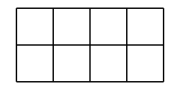

```mathematica
Graphics[Line[pairs]]
```

Actually, this can be done more compactly. First create the coordinate points for a 5×3 lattice.

```mathematica
coords=Table[{i,j},{i,1,5},{j,1,3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3}},{{5,1},{5,2},{5,3}}}

This gives the vertical lines:

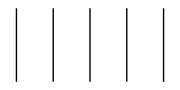

```mathematica
Graphics[Line[coords]]
```

Transposing the coordinates gives a list that can be used for the horizontal lines. Look carefully at the structure of coords to understand what exactly is being transposed.

```mathematica
Transpose@coords
```

{{{1,1},{2,1},{3,1},{4,1},{5,1}},{{1,2},{2,2},{3,2},{4,2},{5,2}},{{1,3},{2,3},{3,3},{4,3},{5,3}}}

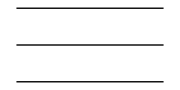

```mathematica
Graphics[Line[Transpose@coords]]
```

This puts everything together, adding points at each coordinate. Module is a localization construct, discussed in Section 6.1.

```mathematica
Lattice[{xdim_,ydim_}]:=Module[{coords},
coords=Table[{i,j},{i,1,xdim},{j,1,ydim}];
Graphics[{
Line[coords],Line[Transpose[coords]],
PointSize[Medium],Point[Flatten[coords,1]]
}]]
```

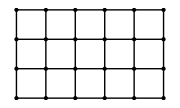

```mathematica
Lattice[{6,4}]
```

Alternatively, you could use CoordinateBoundsArray, new in Mathematica 10.1:

```mathematica
?CoordinateBoundsArray
```

RowBox[{"CoordinateBoundsArray", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] generates an array of RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}] coordinates with integer steps in each dimension.
RowBox[{"CoordinateBoundsArray", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["xrange", "TI"], ",", StyleBox["yrange", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["d", "TI"]}], "]"}] uses step StyleBox["d", "TI"] in each dimension.
RowBox[{"CoordinateBoundsArray", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["xrange", "TI"], ",", StyleBox["yrange", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["dx", "TI"], ",", StyleBox["dy", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] uses steps StyleBox["dx", "TI"], StyleBox["dy", "TI"], StyleBox["…", "TR"] in successive dimensions.
RowBox[{"CoordinateBoundsArray", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["xrange", "TI"], ",", StyleBox["yrange", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"Into", "[", StyleBox["n", "TI"], "]"}]}], "]"}] divides into StyleBox["n", "TI"] equal steps in each dimension.
RowBox[{"CoordinateBoundsArray", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["xrange", "TI"], ",", StyleBox["yrange", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["steps", "TI"], ",", StyleBox["offsets", "TI"]}], "]"}] specifies offsets to use for each coordinate point.
RowBox[{"CoordinateBoundsArray", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["xrange", "TI"], ",", StyleBox["yrange", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["steps", "TI"], ",", StyleBox["offsets", "TI"], ",", StyleBox["k", "TI"]}], "]"}] expands the array by StyleBox["k", "TI"] elements in every direction.

So the following would simplify the computation:

```mathematica
coords=CoordinateBoundsArray[{{1,5},{1,3}}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3}},{{5,1},{5,2},{5,3}}}

This gives ﬁve triples of coordinates and if you look carefully, these can be used to get the vertical lines.

```mathematica
Dimensions[coords]
```

{5,3,2}

```mathematica
Graphics[Line[coords]]
```

-Graphics-

The horizontal lines can be obtained by transposing the coordinates returned by CoordinateBoundsArray.

```mathematica
Transpose[coords]
```

{{{1,1},{2,1},{3,1},{4,1},{5,1}},{{1,2},{2,2},{3,2},{4,2},{5,2}},{{1,3},{2,3},{3,3},{4,3},{5,3}}}

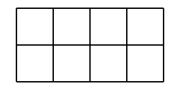

```mathematica
Graphics[{Line[coords],Line[Transpose[coords]]}]
```

```mathematica
Lattice[{xmin_,xmax_},{ymin_,ymax_}]:=Module[{coords},
coords=CoordinateBoundsArray[{{xmin,xmax},{ymin,ymax}}];Graphics[{Line[coords],Line[Transpose[coords]]}]
]
```

```mathematica
Lattice[{1,5},{1,3}]
```

-Graphics-

Exercises: Testing and measuring lists

What is the length of the following list? What are its dimensions? What is the position of g?

{{a,b},{c,d},{e,f},{g,h}}

The following input generates a list of 10000 zeros and ones weighted heavily toward the ones. Determine if there are any zeros in this list and if there are, ﬁnd how many.

```mathematica
lis=RandomChoice[{.0001,.9999}->{0,1},{10000}];
```

Given a list of integers such as the following, count the number of zeros. Find a way to count all those elements of the list which are not ones.

```mathematica
ints=RandomInteger[{-5,5},30]
```

{1,4,-1,2,-2,4,4,-5,5,3,4,-3,-3,1,0,4,-1,-2,2,0,-5,1,-5,-4,3,-5,-2,-3,3,0}

Given the list {{{1,a},{2,b},{3,c}},{{4,d},{5,e},{6,f}}}, determine its dimensions. Use the Dimensions function to check your answer.

Find the positions of the nines in the following list. Conﬁrm using Position.

{{2,1,10},{9,5,7},{2,10,4},{10,1,9},{6,1,6}}

Determine if there are any prime numbers in the interval [4302407360,4302407713]. Once you have a list of the integers that you want to test for primality, use Position (see Section 4.1) and Extract to return the explicit primes.

Solutions

The following list has length four because it has four elements, the four pairs.

```mathematica
lis={{a,b},{c,d},{e,f},{g,h}};
```

```mathematica
Length[lis]
```

4

Its dimensions are 4×2; that is, it has four rows and two columns when thought of as a rectangular array.

```mathematica
Dimensions[lis]
```

{4,2}

```mathematica
MatrixForm[lis]
```

(a | b
c | d
e | f
g | h)

The element g is in the fourth row ﬁrst column.

```mathematica
Position[lis,g]
```

{{4,1}}

Each time your evaluate the following input you will get a different list of 10000 zeros and ones. Seeding the random number generator will give repeatable results.

```mathematica
SeedRandom[1];
lis=RandomChoice[{.0001,.9999}->{0,1},{10000}];
```

On the computer on which this was run, this seed gives some zeros in the list.

```mathematica
FreeQ[lis,0]
```

False

```mathematica
Count[lis,0]
```

2

Here is the list of integers to use.

```mathematica
ints=RandomInteger[{-5,5},30]
```

{0,2,5,-4,3,-2,5,-4,1,-5,-5,3,-3,-3,-4,-2,-2,-4,2,-5,-2,-5,1,4,4,-4,1,0,-2,2}

Count all elements that match 0.

```mathematica
Count[ints,0]
```

2

Count all integers in ints that do not match 1.

```mathematica
Count[ints,Except[1]]
```

27

From the top level, there are two lists, each consisting of three sublists, each sublist consisting of two elements.

```mathematica
Dimensions[{{{1,a},{2,b},{3,c}},{{4,d},{5,e},{6,f}}}]
```

{2,3,2}

The Position function tells us that the 9s are located in the second sublist, ﬁrst position, and in the fourth sublist, third position.

```mathematica
Position[{{2,1,10},{9,5,7},{2,10,4},{10,1,9},{6,1,6}},9]
```

{{2,1},{4,3}}

Here is the interval we are interested in:

```mathematica
ints=Range[4302407360,4302407713];
```

Using some pattern matching (look ahead to Section 4.1), this gives the positions of the integers in ints that pass the PrimeQ test.

```mathematica
pos=Position[ints,p_?PrimeQ]
```

{{354}}

Extract and Position work well together. The positions given by Position can be given directly to Extract to get those elements in ints that are speciﬁed by the positions in Position.

```mathematica
Extract[ints,pos]
```

{4302407713}

```mathematica
PrimeQ[%]
```

{True}

Exercises: Operations on lists

Given a list of coordinate pairs such as the following:

{{x_1,y_1},{x_2,y_2},{x_3,y_3},{x_4,y_4},{x_5,y_5}}

separate the x and y components to get

{{x_1,x_2,x_3,x_4,x_5},{y_1,y_2,y_3,y_4,y_5}}

Use the Part function to extract the elements of a list that are in the even-indexed positions. So in the list below, the even-indexed elements are {3,8,3,4,2,13}. Then extract all those elements in the odd-indexed positions.

```mathematica
lis=RandomInteger[{1,20},{12}]
```

{5,3,3,8,17,3,3,4,20,2,11,13}

Given the following list of integers, ﬁnd the ﬁve largest numbers in the list. Then ﬁnd the ﬁve smallest numbers in the list.

```mathematica
nums=RandomInteger[{-100,100},{25}]
```

{38,6,-15,-31,44,11,-100,47,-14,26,50,48,-72,24,12,66,10,31,78,85,11,-67,23,63,-45}

Use Table to create the following matrix. Once created, use Table again to add all the elements on and above the diagonal.

(1 | 2 | 3 | 4
2 | 4 | 6 | 8
3 | 6 | 9 | 12
4 | 8 | 12 | 16)

Rearrange the list of numbers one through ten so that any adjacent numbers (for example, 1 and 2, 2 and 3, and so on) are not adjacent in the output.

Create a list of all prime numbers less than 100. Repeat for a list of primes less than 1000. Consider using the functions Prime and PrimePi.

Take the partitioned list of integers from the solution to Exercise ExerciseItem in Section Chapter.Section and use Grid to display the partitioned list in a grid similar to that in Figure Chapter.NumberedFigure.

A 6×6 integer grid.

1 | 2 | 3 | 4 | 5 | 6
7 | 8 | 9 | 10 | 11 | 12
13 | 14 | 15 | 16 | 17 | 18
19 | 20 | 21 | 22 | 23 | 24
25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36

Make a histogram of the frequencies of the leading digit in the ﬁrst 10000 Fibonacci numbers. The resulting distribution is an instance of Benford’s law, which concerns the frequency of the leading digits in many kinds of data. The phenomenon, whereby a 1 occurs about 30% of the time, a 2 occurs about 17.6% of the time, and so on, has been shown to occur in well-known numerical sequences, population counts, death rates, Fibonacci numbers, and has even been used to detect corporate and tax fraud.

Given a matrix, use list component assignment to swap any two rows.

Create a function AddColumn[mat,col,pos] that inserts a column vector col into the matrix mat at the column position given by pos. For example:

```mathematica
mat=RandomInteger[9,{4,4}];
MatrixForm[mat]
```

(4 | 8 | 5 | 9
9 | 4 | 1 | 9
1 | 9 | 5 | 5
9 | 5 | 6 | 7)

```mathematica
AddColumn[mat,{a,b,c,d},3]//MatrixForm
```

(4 | 8 | a | 5 | 9
9 | 4 | b | 1 | 9
1 | 9 | c | 5 | 5
9 | 5 | d | 6 | 7)

How would you perform the same task as Prepend[{x,y},z] using the Join function?

Starting with the lists {1,2,3,4} and {a,b,c,d}, create the list {2,4,b,d}. Then create the list {1,a,2,b,3,c,4,d}.

Many lotteries include games that require you to pick several numbers and match them against the lottery’s random number generator. The numbers are independent, so this is essentially random sampling with replacement. The built-in RandomChoice does this. For example, here are ﬁve random samples from the integers zero through nine:

```mathematica
RandomChoice[Range[0,9],5]
```

{5,4,1,1,3}

Write your own function randomChoice[lis,n] that performs a random sampling with replacement, where n is the number of elements being chosen from the list lis. Here is a typical result using a list of symbols:

```mathematica
randomChoice[{a,b,c,d,e,f,g,h},12]
```

{e,c,h,b,g,c,d,c,b,c,b,f}

Given two lists, ﬁnd all those elements that are not common to the two lists. For example, starting with the lists {a,b,c,d} and {a,b,e,f}, your answer would return the list {c,d,e,f}.

One of the tasks in computational linguistics involves statistical analysis of text using what are called n-grams – sequences of n adjacent letters or words. Their frequency distribution in a body of text can be used to predict word usage based on the previous history or usage.

Import a ﬁle consisting of some text and ﬁnd the twenty most frequently occurring word combinations. Pairs of words that are grouped like this are called bigrams, that is, n-grams for n=2.

Use TextWords (new in Mathematica 10.1) to split long strings into a list of words that can then be operated on with the list manipulation functions.

```mathematica
TextWords["Use StringSplit to split long strings into words."]
```

{Use,StringSplit,to,split,long,strings,into,words}

Based on the previous exercise, create a function NGrams[str,n] that takes a string of text and returns a list of n-grams, that is, a list of the n adjacent words. For example:

```mathematica
NGrams["Use StringSplit to split long strings into words.",3]
```

{{Use,StringSplit,to},{StringSplit,to,split},{to,split,long},{split,long,strings},{long,strings,into},{strings,into,words}}

Write your own user-deﬁned functions using the Characters and StringJoin functions to perform the same operations as StringInsert and StringDrop.

Use ToCharacterCode and FromCharacterCode to perform the same operations as the built-in StringJoin and StringReverse functions.

Compute the ﬁrst ten square-pyramidal numbers in three different ways. The ﬁrst few square-pyramidal numbers are 1^2=1, 1^2+2^2=5, 1^2+2^2+3^2=14,…. The number of stacked spheres with a square base (Figure Chapter.NumberedFigure) are represented by these numbers. In addition, they give a solution to the problem of counting squares in an n×n grid.

Graphical representation of square-pyramidal numbers.

-Graphics3D-"+"-Graphics3D-"+"-Graphics3D-" ="-Graphics3D-

Solutions

This is a straightforward use of the Transpose function.

```mathematica
Transpose[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]},{Subscript[x, 5],Subscript[y, 5]}}]
```

{{x_1,x_2,x_3,x_4,x_5},{y_1,y_2,y_3,y_4,y_5}}

The most direct way to extract the even (or odd) indexed elements is to use the Span function as a second argument to Part.

```mathematica
lis={5,3,3,8,17,3,3,4,20,2,11,13};
```

```mathematica
Part[lis,2;;-1;;2]
```

{3,8,3,4,2,13}

Here is the shorthand notation:

```mathematica
lis[[2;;-1;;2]]
```

{3,8,3,4,2,13}

And here are the elements in the odd positions.

```mathematica
lis[[1;;-1;;2]]
```

{5,3,17,3,20,11}

Here is the list of numbers:

```mathematica
nums=RandomInteger[{-100,100},{25}]
```

{-45,-24,9,38,-82,-60,-21,-66,23,70,-67,-13,-98,-68,-97,-55,10,-11,25,-13,7,-100,88,36,-86}

Sorting gives:

```mathematica
Sort[nums]
```

{-100,-98,-97,-86,-82,-68,-67,-66,-60,-55,-45,-24,-21,-13,-13,-11,7,9,10,23,25,36,38,70,88}

The smallest ﬁve:

```mathematica
Take[Sort[nums],5]
```

{-100,-98,-97,-86,-82}

The largest ﬁve:

```mathematica
Take[Sort[nums],-5;;-1]
```

{25,36,38,70,88}

Alternatively, use the built-in functions TakeLargest and TakeSmallest:

```mathematica
TakeLargest[nums,5]
```

{88,70,38,36,25}

```mathematica
TakeSmallest[nums,5]
```

{-100,-98,-97,-86,-82}

There are several ways to create the matrix. One way is to use Table with two iterators.

```mathematica
mat=Table[i j,{i,1,4},{j,1,4}]
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

```mathematica
MatrixForm[mat]
```

(1 | 2 | 3 | 4
2 | 4 | 6 | 8
3 | 6 | 9 | 12
4 | 8 | 12 | 16)

Another way is to use Outer (discussed in Section 5.1).

```mathematica
Outer[Times,Range[4],Range[4]]
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

To add only those elements on or above the diagonal in mat, the following will pick out only those elements.

```mathematica
Table[mat[[i,j]],{i,1,4},{j,1,i}]
```

{{1},{2,4},{3,6,9},{4,8,12,16}}

Then ﬂatten the nested lists.

```mathematica
Flatten[%]
```

{1,2,4,3,6,9,4,8,12,16}

And ﬁnally, use Total to sum this list.

```mathematica
Total[%]
```

65

There are many possible approaches to this problem including a brute-force approach that creates all permutations and selects on those that meet the criteria. Another approach is to split the list and shuffle:

```mathematica
lis=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
p=Partition[lis,5]
```

{{1,2,3,4,5},{6,7,8,9,10}}

```mathematica
Riffle[p[[1]],p[[2]]]
```

{1,6,2,7,3,8,4,9,5,10}

Once you are familiar with the Apply function (Chapter 5), this is done more compactly as follows:

```mathematica
Apply[Riffle,p]
```

{1,6,2,7,3,8,4,9,5,10}

First, note that PrimePi[n] returns the number of primes less than n.

```mathematica
PrimePi[100]
```

25

So to list all the primes less than 100, we want the ﬁrst PrimePi[100]=25 primes.

```mathematica
Table[Prime[n],{n,PrimePi[100]}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

An n×n grid with rows of length n will have n^2 elements in total. Starting with the list of integers one through n^2, partition it into sublists of length n. For example, for n=4:

```mathematica
n=4;
lis=Partition[Range[n^2],n]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}}

And then put the list into a grid:

```mathematica
Grid[lis,Frame->All]
```

1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16

Alternatively, you can use Multicolumn:

```mathematica
n=4;
lis=Multicolumn[Range[n^2],n,Appearance->"Horizontal",Frame->All]
```

1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16

```mathematica
Clear[n]
```

To extract the leading digit of any number, use IntegerDigits to generate a list of the digits in a number, and then take the ﬁrst element in that list. For example, here are the digits in the 50th Fibonacci number.

```mathematica
IntegerDigits[Fibonacci[50]]
```

{1,2,5,8,6,2,6,9,0,2,5}

And this gives the ﬁrst digit from that list.

```mathematica
First[%]
```

1

To do this for the ﬁrst 100000 Fibonacci numbers, use Table.

```mathematica
digits=Table[First[IntegerDigits[Fibonacci[i]]],{i,10^4}];
```

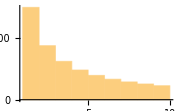

```mathematica
Histogram[digits]
```

The standard procedural approach is to use a temporary variable to do the swapping.

```mathematica
mat=RandomInteger[9,{4,4}];
MatrixForm[mat]
```

(4 | 1 | 2 | 6
1 | 6 | 2 | 8
0 | 7 | 2 | 4
1 | 7 | 6 | 9)

```mathematica
temp=mat[[1]];
mat[[1]]=mat[[2]];
mat[[2]]=temp;
MatrixForm[mat]
```

(1 | 6 | 2 | 8
4 | 1 | 2 | 6
0 | 7 | 2 | 4
1 | 7 | 6 | 9)

But you can use parallel assignments to avoid the temporary variable.

```mathematica
mat=RandomInteger[9,{4,4}];
MatrixForm[mat]
```

(2 | 8 | 2 | 8
1 | 2 | 7 | 8
0 | 0 | 7 | 7
4 | 2 | 7 | 2)

```mathematica
{mat[[2]],mat[[1]]}={mat[[1]],mat[[2]]};
MatrixForm[mat]
```

(1 | 2 | 7 | 8
2 | 8 | 2 | 8
0 | 0 | 7 | 7
4 | 2 | 7 | 2)

In fact you can make this a bit more compact.

```mathematica
mat=RandomInteger[9,{4,4}];
MatrixForm[mat]
```

(3 | 5 | 8 | 7
1 | 2 | 1 | 2
5 | 1 | 1 | 9
5 | 6 | 2 | 8)

```mathematica
mat[[{2,1}]]=mat[[{1,2}]];
MatrixForm[mat]
```

(1 | 2 | 1 | 2
3 | 5 | 8 | 7
5 | 1 | 1 | 9
5 | 6 | 2 | 8)

A key point to notice is that in this exercise, the matrix mat was overwritten in each case; in other words, these were destructive operations. Section 6.1 discusses how to handle row and column swapping properly so that the original matrix remains untouched.

We prototype with a small matrix.

```mathematica
mat=RandomInteger[10,{3,3}];
MatrixForm[mat]
```

(0 | 3 | 6
3 | 6 | 8
2 | 9 | 6)

Using Mean on a matrix produces a vector consisting of column means.

```mathematica
Mean[mat]
```

{5/3,6,20/3}

To subtract the means from their respective columns in mat, operate on the transposed matrix.

```mathematica
centeredMat=Transpose[Transpose[mat]-Mean[mat]]
```

{{-5/3,-3,-2/3},{4/3,0,4/3},{1/3,3,-2/3}}

```mathematica
Mean[centeredMat]
```

{0,0,0}

Alternatively, you could create a centering matrix which, when multiplied by the original matrix, centers it.

```mathematica
CenteringMatrix[n_]:=IdentityMatrix[n]-ConstantArray[1/n,{n,n}]
```

```mathematica
CenteringMatrix[3].mat
```

{{-5/3,-3,-2/3},{4/3,0,4/3},{1/3,3,-2/3}}

As an aside, the centering matrix is symmetric and idempotent.

```mathematica
SymmetricMatrixQ[CenteringMatrix[3]]
```

True

```mathematica
CenteringMatrix[3].CenteringMatrix[3]==CenteringMatrix[3]
```

True

This can also be accomplished with the built-in function Standardize.

```mathematica
Standardize[mat,Mean,1&]
```

{{-5/3,-3,-2/3},{4/3,0,4/3},{1/3,3,-2/3}}

You need to ﬁrst transpose the matrix to operate on the columns as rows.

```mathematica
mat=RandomInteger[9,{4,4}];
MatrixForm[mat]
```

(8 | 2 | 2 | 9
3 | 7 | 9 | 7
1 | 2 | 7 | 9
0 | 2 | 6 | 5)

```mathematica
Transpose[mat]
```

{{8,3,1,0},{2,7,2,2},{2,9,7,6},{9,7,9,5}}

Now insert the column vector at the desired position. Then transpose back.

```mathematica
Insert[Transpose[mat],{a,b,c,d},3]//MatrixForm
```

(8 | 3 | 1 | 0
2 | 7 | 2 | 2
a | b | c | d
2 | 9 | 7 | 6
9 | 7 | 9 | 5)

```mathematica
Transpose@Insert[Transpose[mat],{a,b,c,d},3]//MatrixForm
```

(8 | 2 | a | 2 | 9
3 | 7 | b | 9 | 7
1 | 2 | c | 7 | 9
0 | 2 | d | 6 | 5)

Here then is the function, with some basic argument checking to make sure the number of elements in the column vector is the same as the number of rows of the matrix.

```mathematica
AddColumn[mat_,col_,pos_]/;Length[col]==Length[mat]:=Transpose[Insert[Transpose[mat],col,pos]]
```

Join expects lists as arguments.

```mathematica
Join[{z},{x,y}]
```

{z,x,y}

Joining the two lists and then using Part with Span is the most direct way to do this.

```mathematica
expr=Join[{1,2,3,4},{a,b,c,d}]
```

{1,2,3,4,a,b,c,d}

```mathematica
expr[[2;;-1;;2]]
```

{2,4,b,d}

For the second part of this exercise, the function Riffle is perfect for this task.

```mathematica
Riffle[{1,2,3,4},{a,b,c,d}]
```

{1,a,2,b,3,c,4,d}

This can also be done in two steps by ﬁrst transposing the two lists and then ﬂattening.

```mathematica
Transpose[{{1,2,3,4},{a,b,c,d}}]
```

{{1,a},{2,b},{3,c},{4,d}}

```mathematica
Flatten[%]
```

{1,a,2,b,3,c,4,d}

One way to do this is to take the list and simply pick out elements at random locations. The right-most location in the list is given by Length[lis], using Part and RandomInteger.

```mathematica
randomChoice[lis_,n_]:=lis⟦RandomInteger[{1,Length[lis]},{n}]⟧
```

```mathematica
randomChoice[{a,b,c,d,e,f,g,h},12]
```

{h,b,a,g,b,c,f,a,g,f,a,d}

This is another way of asking for all those elements that are in the union but not the intersection of the two sets.

```mathematica
A={a,b,c,d};
B={a,b,e,f};
```

```mathematica
Complement[A∪B,A∩B]
```

{c,d,e,f}

```mathematica
Complement[Union[A,B],Intersection[A,B]]
```

{c,d,e,f}

We will use Darwin’s On the Origin of Species text, built into Mathematica via ExampleData.

```mathematica
darwin=ExampleData[{"Text","OriginOfSpecies"}];
words=TextWords[darwin]
```

{INTRODUCTION,When,on,board,H.M.S.,Beagle,as,naturalist,I,was,much,149960,most,beautiful,and,most,wonderful,have,been,and,are,being,evolved}
 |  |  |  |

First, partition the list of words into pairs with overlap one.

```mathematica
par=Partition[words,2,1]
```

{{INTRODUCTION,When},{When,on},{on,board},{board,H.M.S.},{H.M.S.,Beagle},149971,{have,been},{been,and},{and,are},{are,being},{being,evolved}}
 |  |  |  |

Then tally them and sort by the frequency count, given by the last element in each sublist. Finally, take the last twenty expressions, those bigrams occurring the most frequently.

```mathematica
tally=SortBy[Tally[par],Last];
Take[tally,-20]
```

{{{has,been},190},{{each,other},192},{{species,of},201},{{of,life},227},{{with,the},230},{{natural,selection},234},{{it,is},237},{{and,the},238},{{by,the},242},{{from,the},256},{{in,a},256},{{to,be},267},{{of,a},268},{{have,been},432},{{that,the},434},{{on,the},498},{{to,the},582},{{the,same},715},{{in,the},1024},{{of,the},1993}}

Here are the next twenty most frequently occurring bigrams.

```mathematica
Take[tally,-40;;-21]
```

{{{to,have},120},{{which,are},121},{{conditions,of},124},{{between,the},125},{{do,not},128},{{and,in},132},{{the,case},133},{{can,be},137},{{will,be},138},{{as,the},140},{{would,be},142},{{number,of},144},{{all,the},150},{{at,the},157},{{the,most},160},{{the,other},166},{{for,the},170},{{the,species},172},{{I,have},185},{{may,be},189}}

This can be done in one step using WordCounts (new in Mathematica 10.1) with a second argument to count bigrams only.

```mathematica
WordCounts[darwin,2]
```

<|{of,the}→1993,{in,the}→1023,{the,same}→715,{to,the}→582,{on,the}→497,47987,{a,barrier}→1,{a,barnacle}→1,{a,bare}→1,{a,bar}→1,{a,bank}→1|>
 |  |  |  |

```mathematica
Take[%,20]
```

<|{of,the}→1993,{in,the}→1023,{the,same}→715,{to,the}→582,{on,the}→497,{that,the}→434,{have,been}→431,{of,a}→268,{to,be}→267,{in,a}→256,{from,the}→256,{by,the}→240,{and,the}→238,{it,is}→235,{natural,selection}→233,{with,the}→228,{of,life}→227,{species,of}→200,{each,other}→192,{has,been}→190|>

This is a straightforward extension of the previous exercise.

```mathematica
NGrams[text_,n_]:=Partition[TextWords[text],n,1]
```

```mathematica
sentence="Use StringSplit to split long strings into words.";
NGrams[sentence,3]
```

{{Use,StringSplit,to},{StringSplit,to,split},{to,split,long},{split,long,strings},{long,strings,into},{strings,into,words}}

Here is our user-deﬁned stringInsert.

```mathematica
stringInsert[str1_,str2_,pos_]:=StringJoin@Join[
Take[Characters[str1],pos-1],
Characters[str2],
Drop[Characters[str1],pos-1]
]
```

```mathematica
stringInsert["Joy world","to the ",5]
```

Joy to the world

```mathematica
stringDrop[str_,pos_]:=StringJoin[Drop[Characters[str],pos]]
```

```mathematica
stringDrop["ABCDEF",-2]
```

ABCD

The idea in these two examples is to convert a string to a list of characters, operate on that list using list manipulation functions like Join, Take, and Drop, then convert back to a string. More efﬁcient approaches use string manipulation functions directly (see Chapter 7).

First, here is how we might write our own StringJoin.

```mathematica
FromCharacterCode[Join[
ToCharacterCode["To be, "],ToCharacterCode["or not to be"]
]]
```

To be, or not to be

And here is a how we might implement a StringReverse.

```mathematica
FromCharacterCode[Reverse[ToCharacterCode["never odd or even"]]]
```

neve ro ddo reven

First we could use the Sum function to add k^2 as k goes from 1 to n.

```mathematica
Sum[k^2,{k,1,10}]
```

385

Here is a list of the ﬁrst ten square pyramidal numbers.

```mathematica
Table[Sum[k^2,{k,1,n}],{n,1,10}]
```

{1,5,14,30,55,91,140,204,285,385}

A closed form expression will be much faster.

```mathematica
Sum[k^2,{k,1,n}]
```

1/6 n (1+n) (1+2 n)

```mathematica
Table[1/6 n (1+n) (1+2 n),{n,1,10}]
```

{1,5,14,30,55,91,140,204,285,385}

Another way of looking at the computation is that we are squaring each of the ﬁrst n numbers and then adding those squares together. Think dot product of the list of the ﬁrst n integers with itself.

```mathematica
Range[10].Range[10]
```

385

```mathematica
Table[Range[n].Range[n],{n,1,10}]
```

{1,5,14,30,55,91,140,204,285,385}

Or, more directly, square each of the integers one through ten, then add them up.

```mathematica
Total[Range[10]^2]
```

385

Exercises: Associations

Create an association consisting of several songs in your music library. Include keys for song title, artist, release date, album cover. Once the association is deﬁned, convert all the album covers to smaller images using Thumbnail.

Modify the MakeRef function to display the year of publication at the end of the line for authors. Adjust the style so that the year displays in a bold font.

```mathematica
MakeRef[hamming1950]
```

Hamming, Richard" ("1950")"
Error detecting and error correcting codes

Solutions

Here is a small association consisting of information on three albums.

```mathematica
alb1=Association[{
"SongTitle"->"Desvairada",
"AlbumArtist"->"Paulo Bellinati",
"AlbumTitle"->"The Guitar Works of Garoto",
"Year"->"1991",
"Cover"->-Graphics-
}];
```

```mathematica
alb2=Association[{
"SongTitle"->"Monk's Mood",
"AlbumArtist"->"Bud Powell",
"AlbumTitle"->"Round About Midnight At The Blue Note",
"Year"->"1962",
"Cover"->-Graphics-
}];
```

```mathematica
alb3=Association[{
"SongTitle"->"Dounia",
"AlbumArtist"->"Rokia Traoré",
"AlbumTitle"->"Tchamantché",
"Year"->"2008",
"Cover"->-Graphics-
}];
```

```mathematica
Map[Thumbnail,{alb1["Cover"],alb2["Cover"],alb3["Cover"]}]
```

{-Graphics-,-Graphics-,-Graphics-}

It is ﬁrst necessary to modify the MakeRef function so that newline characters do not appear between all items. We want the author text to be followed by the date and then a newline. So instead of using a default separator in Row, we will manually put them where we want them.

```mathematica
makeAuthor[ref_]:=Style[ref["Author"],"TR"]
```

```mathematica
makeTitle[ref_]:=Style[ref["Title"],"TI"]
```

```mathematica
makeLink[ref_]:=Hyperlink[Style[ref["Url"],"TR"],ref["Url"]]
```

```mathematica
makeDate[ref_]:=Row[{Style[" (","TR"],Style[ref["Year"],"TB"],Style[")","TR"]}]
```

```mathematica
MakeRef[ref_]:=CellPrint@TextCell[Row[{
makeAuthor[ref],makeDate[ref],"\n",
makeTitle[ref],"\n",
makeLink[ref]
}],"Text",ShowStringCharacters->False]
```

```mathematica
art1=Association@{
"Author"->"Hamming, Richard W.",
"Title"->"Error detecting and error correcting codes",
"Journal"->"The Bell System Technical Journal",
"Year"->1950,
"Volume"->29,
"Issue"->2,
"Pages"->"147–160",
"Url"->"https://archive.org/details/bstj29-2-147"
}
```

<|Author→Hamming, Richard W.,Title→Error detecting and error correcting codes,Journal→The Bell System Technical Journal,Year→1950,Volume→29,Issue→2,Pages→147–160,Url→https://archive.org/details/bstj29-2-147|>

```mathematica
MakeRef[art1]
```

Hamming, Richard W." ("1950")"
Error detecting and error correcting codes

4
Patterns and rules

Exercises: Patterns

Explain why the following pattern match fails. Then ﬁnd two different patterns that correctly match a complex number such as 3+4 i.

```mathematica
MatchQ[3+4I,a_+b_I]
```

False

Use conditional patterns to ﬁnd all those numbers in a list of integers that are divisible by 2 or 3 or 5.

Write down four conditional patterns that match the expression {4,{a,b},"g"}.

Explain why the expression 1/y is not matched by the pattern a_/b_.

```mathematica
MatchQ[1/y,a_/b_]
```

False

Determine the correct pattern that can be used to match the symbolic expression x/y.

```mathematica
MatchQ[x/y, Power[a_, -1]]
```

False

Write a function Collatz that takes an integer n as an argument and returns 3 n+1 if n is an odd integer and returns n/2 if n is even.

Write the Collatz function from the above exercise, but this time you should also check that the argument to Collatz is positive.

Use alternatives to write a function abs[x] that returns x if x≥0, and -x if x<0, whenever x is an integer or a rational number. Whenever x is complex, abs[x] should return √((re(x))^2+(im(x))^2).

Create a function swapTwo[lis] that returns lis with only its ﬁrst two elements interchanged; for example, the input swapTwo[{a,b,c,d,e}] should return {b,a,c,d,e}. If lis has fewer than two elements, swapTwo just returns lis. Write swapTwo using three clauses: one for the empty list, one for one-element lists, and one for all other lists. Then write it using two clauses: one for lists of length zero or one and another for all longer lists.

Explain the different results from the following three pattern matches:

```mathematica
MatchQ[{4,6,8},x_/;Length[x]>4]
```

False

```mathematica
MatchQ[{4,6,8},{x___}/;Length[x]>4]
```

Length::argx: Length called with 3 arguments; 1 argument is expected.

False

```mathematica
MatchQ[{4,6,8},{x___}/;Plus[x]>10]
```

True

Write a rule for the one-dimensional case of showWalk described in this section. Then write an additional rule to handle multiple one-dimensional random walks.

```mathematica
Needs["EPM`RandomWalks`"]
```

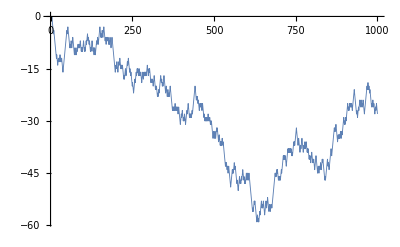

```mathematica
walk=RandomWalk[1000,Dimension->1];
showWalk[walk]
```

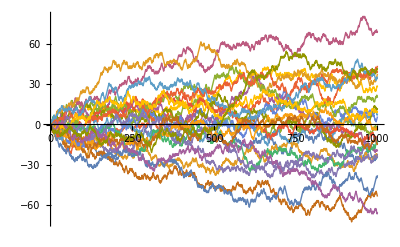

```mathematica
walks=Table[RandomWalk[1000,Dimension->1],{25}];
showWalk[walks]
```

Given a set of data like that in Figure Chapter.NumberedFigure, remove all outliers, deﬁned here by being greater than two standard deviations from the mean of the data.

```mathematica
rawData=RandomVariate[NormalDistribution[0,2],{200}];
```

Scatter plots of original data and data with outliers removed.

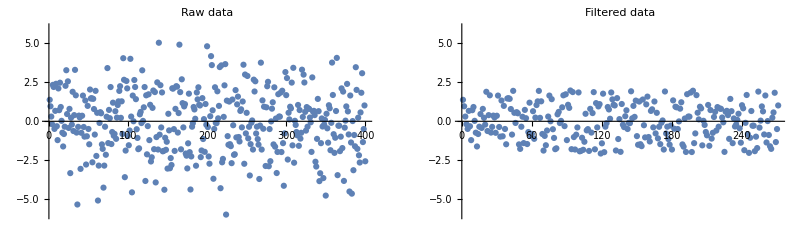

Solutions

Look at the internal representation of the complex number.

```mathematica
FullForm[3+4I]
```

Complex[3,4]

Although this is an equivalent representation to the traditional notation 3+4ⅈ, it is not the same syntactically and the pattern matcher is a syntactic creature. Instead, match on head Complex.

```mathematica
MatchQ[3+4I,_Complex]
```

True

Although giving different information, you could also check that the expression is a number.

```mathematica
MatchQ[3+4I,_?NumberQ]
```

True

Start by creating a list of integers with which to work.

```mathematica
lis=RandomInteger[1000,{20}]
```

{270,885,466,194,374,237,249,228,184,704,636,922,10,619,806,497,290,329,463,168}

IntegerQ is a predicate; it returns True or False, so we need to use the logical OR to separate clauses here.

```mathematica
Cases[lis,n_/;IntegerQ[n/2]||IntegerQ[n/3]||IntegerQ[n/5]]
```

{270,885,466,194,374,237,249,228,184,704,636,922,10,806,290,168}

This is a bit more compact and direct.

```mathematica
Cases[lis,n_/;Mod[n,2]==0||Mod[n,3]==0||Mod[n,5]==0]
```

{270,885,466,194,374,237,249,228,184,704,636,922,10,806,290,168}

Once you are familiar with pure functions (Section 5.5), you can also do this with Select.

```mathematica
Select[lis,Mod[#,2]==0||Mod[#,3]==0||Mod[#,5]==0&]
```

{270,885,466,194,374,237,249,228,184,704,636,922,10,806,290,168}

FullForm should help to guide you.

```mathematica
FullForm[{4,{a,b},"g"}]
```

List[4,List[a,b],"g"]

```mathematica
MatchQ[{4,{a,b},"g"},x_List/;Length[x]==3]
```

True

```mathematica
MatchQ[{4,{a,b},"g"},{_,y_,_}/;y⟦0⟧==List]
```

True

```mathematica
MatchQ[{4,{a,b},"g"},{x_,y_,z_}/;AtomQ[z]]
```

True

```mathematica
MatchQ[{4,{a,b},"g"},{x_,_,_}/;EvenQ[x]]
```

True

Look at the internal representation of these two expressions:

```mathematica
FullForm[1/x]
```

Power[x,-1]

```mathematica
FullForm[a_/b_]
```

Times[Pattern[a,Blank[]],Power[Pattern[b,Blank[]],-1]]

So 1/x is a special case of the pattern a_/b_ but it is one that Mathematica simpliﬁes to an expression with head Power.

x/y can be matched by the pattern a_/b_.

```mathematica
MatchQ[x/y,a_/b_]
```

True

The Collatz function has a direct implementation based on its deﬁnition. There is no need to check explicitly that the argument is an integer since OddQ and EvenQ handle that.

```mathematica
Collatz[n_?OddQ]:=3n+1
```

```mathematica
Collatz[n_?EvenQ]:=n/2
```

Here we iterate the Collatz function ﬁfteen times starting with an initial value of 23.

```mathematica
NestList[Collatz,23,15]
```

{23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

Check for arguments that do not match the patterns above.

```mathematica
Collatz[24.0]
```

Collatz[24.]

Here again is the Collatz function, but this time using a condition on the right-hand side of the deﬁnition.

```mathematica
Clear[Collatz]
```

```mathematica
Collatz[n_]:=3n+1/;OddQ[n]&&Positive[n]
```

```mathematica
Collatz[n_]:=n/2/;EvenQ[n]&&Positive[n]
```

```mathematica
Collatz[4.3]
```

Collatz[4.3]

```mathematica
Collatz[-3]
```

Collatz[-3]

```mathematica
NestList[Collatz,22,15]
```

{22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

You could also put the conditions inside the pattern on the left-hand side if you prefer.

```mathematica
Clear[Collatz]
```

```mathematica
Collatz[n_/;OddQ[n]&&Positive[n]]:=3n+1
```

```mathematica
Collatz[n_/;EvenQ[n]&&Positive[n]]:=n/2
```

```mathematica
NestList[Collatz,22,15]
```

{22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

Using alternatives, this gives the deﬁnition for real, integer, or rational arguments.

```mathematica
abs[x_Real|x_Integer|x_Rational]:=If[x≥0,x,-x]
```

Here is the deﬁnition for complex arguments.

```mathematica
abs[x_Complex]:=√(Re[x]^2+Im[x]^2)
```

Note that these rules are not invoked for symbolic arguments.

```mathematica
Map[abs,{-3,3+4I,-4/5,a}]
```

{3,5,4/5,abs[a]}

We ﬁrst have to consider the base cases. Given a list with no elements, swapTwo should return the empty list. And, given a list with one element, swapping should give that one element back.

```mathematica
swapTwo[{}]:={}
swapTwo[{x_}]:={x}
```

Now, we use the triple-blank to indicate that r could be a sequence of zero or more elements.

```mathematica
swapTwo[{x_,y_,r___}]:={y,x,r}
```

```mathematica
swapTwo[{}]
```

{}

```mathematica
swapTwo[{a}]
```

{a}

```mathematica
swapTwo[{a,b,c,d}]
```

{b,a,c,d}

Notice in this second deﬁnition for swapTwo that the second clause covers both the situation where the argument is the empty list and when it contains only one element.

```mathematica
swapTwo2[{x_,y_,r___}]:={y,x,r}
swapTwo2[x_]:=x
```

```mathematica
swapTwo[{}]
```

{}

```mathematica
swapTwo[{a}]
```

{a}

```mathematica
swapTwo[{a,b,c,d}]
```

{b,a,c,d}

In the ﬁrst example, x was associated with the entire list {4,6,8}; since the length of the list {4,6,8} is not greater than 4, the match failed. In the second example, x became the sequence 4,6,8 so that the condition was Length[4,6,8]>4; but Length can only have one argument, hence the error. In the last example, x was again associated with 4,6,8, but now the condition was Plus[4,6,8]>10, which is perfectly valid syntax, and true.

To write the one-dimensional rule, you can simply use ListLinePlot on the right hand side. The pattern on the left hand side though needs to match a one-dimensional list of numbers. VectorQ can be used to check for this.

```mathematica
showWalk[coords_?VectorQ] := ListLinePlot[coords]
```

```mathematica
Needs["EPM`RandomWalks`"]
```

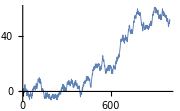

```mathematica
walk=RandomWalk[1000,Dimension->1];
showWalk[walk]
```

The case of multiple walks is a bit trickier. First note the structure of a list of multiple one-dimensional random walks. Here we have 25 ten-step walks.

```mathematica
walks=Table[RandomWalk[10,Dimension->1],{25}];
Dimensions[walks]
```

{25,10}

In situations where you are not sure what the pattern needs to be to match a complicated expression, it oftentimes helps to look at some representative examples.

```mathematica
Short[Take[walks,5],2]
```

{{-1,-2,-1,-2,-3,-4,-3,-4,-5,-4},«3»,{-1,-2,-3,-2,-3,-2,-3,-4,-5,-4}}

So the structure is {{n–steps},{n–steps},… {n–steps}} and in this speciﬁc example we have 25 repeats or trials. We don’t know how long each walk will be ahead of time so we need a double blank to accommodate walks of length one or more. And we will check that each walk list consists of numbers. Here is the rule. We have also added a style directive to thin out the lines.

```mathematica
showWalk[coords:{{__?NumberQ}..}]:=ListLinePlot[coords,PlotStyle->Directive[Thin]]
```

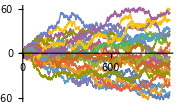

```mathematica
walks=Table[RandomWalk[1000,Dimension->1],{25}];
showWalk[walks]
```

The mean and standard deviation of the data can be obtained with built-in functions.

```mathematica
data=RandomVariate[NormalDistribution[0,2],{200}];
```

```mathematica
{μ,σ}={Mean[data],StandardDeviation[data]}
```

{-0.00968766,1.93378}

This extracts all those elements of data that are within one standard deviation of the mean.

```mathematica
filtered=Cases[data,p_/;Abs[μ-p]<σ];
len=Length[filtered]
```

132

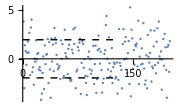

```mathematica
ListPlot[data,Epilog->{
Dashed,Line[{{0,σ},{len,σ}}],Line[{{0,-σ},{len,-σ}}]}]
```

Exercises: Transformation rules

Here is a rule designed to switch the order of each pair of expressions in a list. It works ﬁne on the ﬁrst example, but fails on the second.

```mathematica
{{a,b},{c,d},{e,f}}/.{x_,y_}:>{y,x}
```

{{b,a},{d,c},{f,e}}

```mathematica
{{a,b},{c,d}}/.{x_,y_}:>{y,x}
```

{{c,d},{a,b}}

Explain what has gone wrong and rewrite this rule to correct the situation, that is, so that the second example returns {{b,a},{d,c}}.

Given a 3×3 matrix, here is a rule intended to swap the elements in the second and third columns:

```mathematica
mat={{a,b,c},{d,e,f},{g,h,i}};
```

```mathematica
mat/.{x_,y_,z_}:>{x,z,y}//MatrixForm
```

(a | b | c
g | h | i
d | e | f)

Explain what has gone wrong and rewrite the rule so that it correctly swaps columns two and three.

Use pattern matching to extract all negative solutions of the following polynomial:

x^9+3.4 x^6-25 x^5-213 x^4-477 x^3+1012 x^2+111x-123

Then extract all real solutions; that is, those which are not complex.

Create a rewrite rule that uses a repeated replacement to “unnest” the nested lists within a list.

```mathematica
unNest[{{α,α,α},{α},{{β,β,β},{β,β}},{α,α}}]
```

{α,α,α,α,β,β,β,β,β,α,α}

Deﬁne a function using pattern matching and repeated replacement to sum the elements of a list such as that produced by Range[100].

Using the built-in function ReplaceList, write a function cartesianProduct that takes two lists as input and returns the Cartesian product of these lists.

```mathematica
cartesianProduct[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},{Subscript[y, 1],Subscript[y, 2]}]
```

{{x_1,y_1},{x_1,y_2},{x_2,y_1},{x_2,y_2},{x_3,y_1},{x_3,y_2}}

Write a function to count the total number of multiplications in any polynomial expression. For example, given a power, your function should return one less than the exponent.

```mathematica
MultiplyCount[t^5]
```

4

```mathematica
MultiplyCount[a x y t]
```

3

```mathematica
MultiplyCount[a x y t^4+w t]
```

7

Create six graphical objects, one each to represent the faces of a standard six-sided die. Dice[n] should display the face of the appropriate die, as below. Then use the Dice function to create a function RollDice[] that “rolls” two dice and displays them side-by-side. Create an additional rule, RollDice[n], that rolls a pair of dice n times and displays the result in a list or row.

```mathematica
Table[Dice[n],{n,1,6}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

One way to approach this problem is to think of a die face as a grid of nine elements, some of which are turned on (white) and some turned off (blue above). Then create one set of rules for each of the six die faces. Once your rules are deﬁned, you could use something like the following graphics code (a bit incomplete as written here) to create your images:

```mathematica
Dice[n_]:=GraphicsGrid[
  Map[Graphics,Partition[Range[9],3]/.rules[[n]],{2}]]
```

Make a scatter plot of the points used to construct the polygons in a torus, which is given parametrically as follows:

```mathematica
ParametricPlot3D[{(2+Cos[v]) Sin[u],(2+Cos[v]) Cos[u],Sin[v]},{u,0,2 π},{v,0,2 π}]
```

-Graphics3D-

Solutions

The problem here is that the pattern is too general and has been matched by the entire expression, which has the form {x_,y_}, where x is matched by {a,b} and y is matched by {c,d}. To ﬁx this, use patterns to restrict the expressions that match.

```mathematica
{{a,b},{c,d}}/.{x_Symbol,y_Symbol}:>{y,x}
```

{{b,a},{d,c}}

```mathematica
{{a,b},{c,d},{e,f}}/.{x_Symbol,y_Symbol}:>{y,x}
```

{{b,a},{d,c},{f,e}}

Here is the matrix.

```mathematica
mat={{a,b,c},{d,e,f},{g,h,i}};
MatrixForm[mat]
```

(a | b | c
d | e | f
g | h | i)

This rule swaps the second and third rows, not the columns.

```mathematica
mat/.{x_,y_,z_}:>{x,z,y}//MatrixForm
```

(a | b | c
g | h | i
d | e | f)

It appears as if the pattern matcher starts at the outer list expression rather than at the bottom of the nested expression. Starting at the top, the rule matches the entire matrix with the ﬁrst row matching the pattern x_, the second row matching y_ and the third row matching z_. Some additional constraints will help here.

```mathematica
mat/.{x_Symbol,y_Symbol,z_Symbol}:>{x,z,y}//MatrixForm
```

(a | c | b
d | f | e
g | i | h)

First, get the solutions to this polynomial.

```mathematica
soln=Solve[x^9+3.4 x^6-25 x^5-213 x^4-477 x^3+1012 x^2+111 x-123==0,x]
```

{{x→-2.80961},{x→-1.85186-2.15082 ⅈ},{x→-1.85186+2.15082 ⅈ},{x→-0.376453},{x→0.323073},{x→1.06103-3.12709 ⅈ},{x→1.06103+3.12709 ⅈ},{x→1.30533},{x→3.13931}}

The pattern needs to match an expression consisting of a list with a rule inside where the value on the right-hand side of the rule should pass the Negative test.

```mathematica
Cases[soln,{x_->_?Negative}]
```

{{x→-2.80961},{x→-0.376453}}

Here are two solutions for the noncomplex roots.

```mathematica
Cases[soln,{_->_Real}]
```

{{x→-2.80961},{x→-0.376453},{x→0.323073},{x→1.30533},{x→3.13931}}

```mathematica
DeleteCases[soln,{_->_Complex}]
```

{{x→-2.80961},{x→-0.376453},{x→0.323073},{x→1.30533},{x→3.13931}}

The transformation rule unnests lists within a list.

```mathematica
unNest[lis_]:=Map[(#//.{x__}:>x&),lis]
```

```mathematica
unNest[{{a,a,a},{a},{{b,b,b},{b,b}},{a,a}}]
```

{a,a,a,a,b,b,b,b,b,a,a}

Note the need to put y in a list on the right-hand side of the rule. Also, an immediate rule is required here.

```mathematica
sumList[lis_]:=First[lis//.{x_,y___}->x+{y}]
```

```mathematica
sumList[{1,5,8,3,9,3}]
```

29

The triple blank is required both before and after the variables x and y.

```mathematica
cartesianProduct[lis1_,lis2_]:=ReplaceList[{lis1,lis2},{{___,x_,___},{___,y_,___}}:>{x,y}]
```

We could also have a rule for an argument consisting of the empty list.

```mathematica
cartesianProduct[{}]:={}
```

```mathematica
Clear[x,y,z,a,b,c,d]
```

```mathematica
cartesianProduct[{a,b,c},{x,y,z}]
```

{{a,x},{a,y},{a,z},{b,x},{b,y},{b,z},{c,x},{c,y},{c,z}}

```mathematica
cartesianProduct[{}]
```

{}

For an expression of the form Power[a,b], the number of multiplies is b-1.

```mathematica
Cases[{x^4},Power[_,exp_]:>exp-1]
```

{3}

For an expression of the form Times[a,b,c,…], the number of multiplications is given by one less then the number of arguments.

```mathematica
Cases[{a b c d e},fac_Times:>Length[fac]-1]
```

{4}

For a mix of terms of these two cases, we will need to total up the counts from the respective terms. Here is a function that puts this all together. Use Infinity as a third argument to Cases to make sure the search goes all the way down the expression tree.

```mathematica
MultiplyCount[expr_]:=Total@Cases[{expr},Power[_,exp_]:>exp-1,Infinity]+Total@Cases[{expr},fac_Times:>Length[fac]-1,Infinity]
```

```mathematica
MultiplyCount[a b^2 c d^5]
```

8

```mathematica
poly=Expand[(x+y-z)^3]
```

x^3+3 x^2 y+3 x y^2+y^3-3 x^2 z-6 x y z-3 y^2 z+3 x z^2+3 y z^2-z^3

```mathematica
MultiplyCount[poly]
```

28

Ideally we should check that the expression passed to this function is a polynomial ﬁrst. That is addressed in Exercise 5, Section 6.2.

First, we create a grid of the nine locations on the die.

```mathematica
lis=Partition[Range[9],3];
Grid[lis]
```

1 | 2 | 3
4 | 5 | 6
7 | 8 | 9

Next, use graphics primitives to indicate if a location on the grid is colored (on) or not (off).

```mathematica
off={Red,Disk[]};
on={White,Disk[]};
```

Here are the rules for a ﬁve.

```mathematica
GraphicsGrid[Map[Graphics,
lis/.{1->on,2->off,3->on,4->off,5->on,6->off,7->on,8->off,9->on},
{2}],Background->Red,Spacings->10,ImageSize->40]
```

-Graphics-

The ﬁve other rules are straightforward. Here then is a function that wraps up the code. Note the use of the Background option to GraphicsGrid to pick up the color from the value of off.

```mathematica
Dice[n_]:=Module[{rules,off={Darker@Blue,Disk[]},on={White,Disk[]}},
rules={
{1->off,2->off,3->off,4->off,5->on,6->off,7->off,8->off,9->off},
{1->off,2->off,3->on,4->off,5->off,6->off,7->on,8->off,9->off},
{1->off,2->off,3->on,4->off,5->on,6->off,7->on,8->off,9->off},
{1->on,2->off,3->on,4->off,5->off,6->off,7->on,8->off,9->on},
{1->on,2->off,3->on,4->off,5->on,6->off,7->on,8->off,9->on},
{1->on,2->off,3->on,4->on,5->off,6->on,7->on,8->off,9->on}
};
GraphicsGrid[Map[Graphics,
Partition[Range[9],3]/.rules[[n]],
{2}],Background->First[off],Spacings->10,ImageSize->40]
]
```

```mathematica
Table[Dice[n],{n,1,6}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

This can be done a bit more compactly by using a 3×3 matrix of zeros and ones.

```mathematica
Dice[n_,OptionsPattern[]]:=Module[{rules,color,grid},
color=OptionValue[Color];
rules={0->{color,Disk[]},1->{White,Disk[]}};
grid={
{0,0,0,0,1,0,0,0,0},
{0,0,1,0,0,0,1,0,0},
{0,0,1,0,1,0,1,0,0},
{1,0,1,0,0,0,1,0,1},
{1,0,1,0,1,0,1,0,1},
{1,0,1,1,0,1,1,0,1}
};
GraphicsGrid[Map[Graphics,Partition[grid[[n]],3]/.rules,{2}],Background->color,Spacings->10,ImageSize->40]
]
```

Using Array, we create a list of the six dice.

```mathematica
Array[Dice,{6}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Rolling a pair is randomly choosing (with replacement).

```mathematica
RollDice[]:=GraphicsRow[RandomChoice[Array[Dice,{6}],{2}]]
```

```mathematica
RollDice[]
```

-Graphics-

And here is the rule for rolling the pair of dice n times.

```mathematica
RollDice[n_]:=Table[RollDice[],{n}]
```

```mathematica
RollDice[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Here is the torus:

```mathematica
torus=ParametricPlot3D[{(2+Cos[v]) Sin[u],(2+Cos[v]) Cos[u],Sin[v]},{u,0,2 π},{v,0,2 π}]
```

-Graphics3D-

The internal form of the graphic shows the form we are looking for.

```mathematica
Short[InputForm[torus],5]
```

Graphics3D[GraphicsComplex[{{1.3463968515383922*^-6, 2.999999999999597, 4.487989505128125*^-7}, {<<3>>}, <<2296>>, {-2.0674956344646818, 2.067494242630337, -0.38268379517170614}}, <<2>>], {<<9>>}]

Mirroring what was done in the plot example in this section, here is the expression to extract only coordinate triples.

```mathematica
points=Cases[torus,GraphicsComplex[pts:{{_,_,_}..},__]:>pts,Infinity]
```

{{{1.3464×10^-6,3.,4.48799×10^-7},2297,{-2.0675,2.06749,-0.382684}}}
 |  |  |  |

And here is the scatter plot of these points.

```mathematica
ListPointPlot3D[points,PlotStyle->PointSize[Small]]
```

-Graphics3D-

Exercises: Examples

Create a predicate function compositeQ that tests whether a positive integer is composite. Check it against the built-in CompositeQ.

Plot the function Sinc[x] over the interval [–2 π, 2 π] and then use a transformation rule to display a reﬂection in the y-axis. Use Show[plot/.expr:>rule,PlotRange→All] to display the transformed plot in such a way that a new plot range is computed.

Occasionally, when collecting data from an instrument, the collector fails or returns a bad value. In analyzing the data, the analyst has to make a decision about what to use to replace these bad values. One approach is to replace them with a column mean. Given an array of numbers such as the following, create a function to replace each "NAN" with the mean of the numbers that appear in that column:

```mathematica
data=({{0.9034, "NAN", 0.7163, 0.8588}, {0.3031, 0.5827, 0.2699, 0.8063}, {0.0418, 0.8426, "NAN", 0.8634}, {"NAN", 0.8913, 0.0662, 0.8432}});
```

Given a two-column array of data

```mathematica
data=RandomInteger[{0,9},{5,2}];
```

```mathematica
MatrixForm[data,TableAlignments->"."]
```

(7 | 0
8 | 2
1 | 5
8 | 0
6 | 7)

create a new array that consists of three columns where the ﬁrst two columns are identical to the original, but the third column consists of the mean of the two numbers from the ﬁrst two columns.

(7 | 0 | 7/2
8 | 2 | 5
1 | 5 | 3
8 | 0 | 4
6 | 7 | 13/2)

Given a graphic produced by Plot, use a transformation rule to halve the y-coordinate of each point used to construct the plot, then display the result.

Extend the counting coins example to take images of coins as the argument to the function.

```mathematica
CountChange[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

0.42

Create a function FindSubsequence[digits,subseq] to ﬁnd the positions of a subsequence subseq within a sequence of numbers given by digits. Assume both digits and subseq are lists of numbers. Your function should return a list of the starting and ending positions where the subsequence occurs in the sequence, similar to what Position returns. For example, here are the ﬁrst 50 digits of π:

```mathematica
pidigs=First[RealDigits[π,10,100]]
```

{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,3,8,3,2,7,9,5,0,2,8,8,4,1,9,7,1,6,9,3,9,9,3,7,5,1,0,5,8,2,0,9,7,4,9,4,4,5,9,2,3,0,7,8,1,6,4,0,6,2,8,6,2,0,8,9,9,8,6,2,8,0,3,4,8,2,5,3,4,2,1,1,7,0,6,7}

The subsequence 38 appears in two locations in pidigs.

```mathematica
FindSubsequence[pidigs,{3,8}]
```

{{18,19},{26,27}}

Write another deﬁnition of FindSubsequence that takes two integers as arguments. So, for example, the following should work:

```mathematica
SeedRandom[6];
n=RandomInteger[10^200]
```

38962167906640602500170931211955779575023497774170227858878429522794529744062342783143699902237900976316871609846545097431390396795087845924977005230435025177652637766538981421277296525589205107229653

```mathematica
FindSubsequence[n,965]
```

{{181,183},{197,199}}

Compute the area of a triangle using the following formula for three two-dimensional coordinates (x_i,y_i,z_i) embedded in three-dimensional space:

A_△=1/2 √(Det[x_1 | y_1 | 1
x_2 | y_2 | 1
x_3 | y_3 | 1]^2+Det[y_1 | z_1 | 1
y_2 | z_2 | 1
y_3 | z_3 | 1]^2+Det[z_1 | x_1 | 1
z_2 | x_2 | 1
z_3 | x_3 | 1]^2)

Using historical global surface temperatures, make a plot showing the difference in °C from the 1950–1980 average for each year. Data is available from numerous sources, including NASA’s Goddard Institute for Space Studies (NASA 2015). After importing the data you will need to remove header and footer information before pouring the pairs {year,yearly_temp} into TimeSeries. Make the plot using DateListPlot and include a smoothed ﬁve-year moving average together with the plot of the raw data.

Sunspots are caused by magnetic ﬁelds which in turn are caused by the current generated by the motion of hot plasma inside the sun. In regions where the induced magnetic ﬁeld is most intense, the increased pressure causes the region to rise to the surface causing darker regions – sunspots – where the temperature is lower. The mean magnetic ﬁeld of the sun has been recorded since 1975 and is available from the Wilcox Solar Observatory at Stanford University:

```mathematica
data=Import["http://wso.stanford.edu/meanfld/MF_timeseries.txt","Table"];
Take[data,10]
```

{{Date,Daily,MF,(uT)},{1975:05:16_20h,29},{1975:05:17_20h,22},{1975:05:18_20h,24},{1975:05:19_20h,24},{1975:05:20_20h,13},{1975:05:21_20h,4},{1975:05:22_20h,4},{1975:05:23_20h,XXXX},{1975:05:24_20h,-3}}

Import the solar magnetic ﬁeld data and create rules to convert the timestamps to a form that the time series functions can work with. You will need to convert the missing measurements (denoted ”XXXX” in the data) of the magnetic ﬁeld strength to Missing[] which the time series functions will handle more gracefully. Finally, make a plot of the data over the time period using DateListPlot.

To convert the date to a usable format, use DateList and specify the explicit delimiters.

```mathematica
DateList[{"1975:05:18_20h",{"Year",":","Month",":","Day","_","Hour","h"}}]
```

{1975,5,18,20,0,0.}

Solutions

First, the argument is checked to see if it has head Integer and if it is greater than one.

```mathematica
compositeQ[n_Integer/;n>1]:=Not[PrimeQ[n]]
```

Check a few numbers for compositeness.

```mathematica
compositeQ[16]
```

True

```mathematica
compositeQ[2^31-1]
```

False

```mathematica
compositeQ[2^63-1]===CompositeQ[2^63-1]
```

True

Here is the plot of the sinc function.

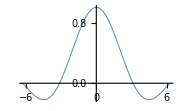

```mathematica
splot=Plot[Sinc[x],{x,-2 π,2 π}]
```

This replacement rule replaces each pair of numbers {x,y} with the pair {x,-y}, giving a reﬂection in the y-axis. Note the need to modify the plot range here.

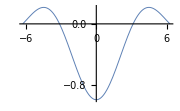

```mathematica
Show[splot/.{x_?NumberQ,y_?NumberQ}:>{x,-y},PlotRange->All]
```

The argument checking (_?NumberQ) is necessary here so that pairs of arbitrary expressions embedded somewhere in the graphics expression are not pattern matched. We only want to interchange pairs of numbers, not pairs of options or other expressions that might be present in the underlying expression representing the graphic.

First, here is the data with which we will work.

```mathematica
array=({{0.9034000000000001, "NAN", 0.7163, 0.8588, 0.1228}, {0.30310000000000004, 0.5827, 0.26990000000000003, 0.8063, "NAN"}, {0.041800000000000004, 0.8426, "NAN", 0.8634000000000001, 0.9682000000000001}, {0.9163, 0.8913000000000001, 0.06620000000000001, 0.8432000000000001, 0.054700000000000006}, {0.7937000000000001, 0.6905, 0.9105000000000001, 0.5589000000000001, 0.8993}});
```

Get only the numeric values from the second column.

```mathematica
col2=array[[All,2]];
Cases[col2,_?NumberQ]
```

{0.5827,0.8426,0.8913,0.6905}

Compute the mean of the second column.

```mathematica
Mean[Cases[col2,_?NumberQ]]
```

0.751775

Replace the string with the column mean.

```mathematica
col2/."NAN"->Mean[Cases[col2,_?NumberQ]]//MatrixForm
```

(0.751775
0.5827
0.8426
0.8913
0.6905)

Turn it into a function.

```mathematica
fixcolumn[col_]:=array[[All,col]]/."NAN":>Mean[Cases[array[[All,col]],_?NumberQ]]
```

Try this function out on column 1 of our matrix.

```mathematica
fixcolumn[1]
```

{0.9034,0.3031,0.0418,0.9163,0.7937}

Map this function across all the columns.

```mathematica
Map[fixcolumn,Range[Length[First[array]]]]//MatrixForm
```

(0.9034 | 0.3031 | 0.0418 | 0.9163 | 0.7937
0.751775 | 0.5827 | 0.8426 | 0.8913 | 0.6905
0.7163 | 0.2699 | 0.490725 | 0.0662 | 0.9105
0.8588 | 0.8063 | 0.8634 | 0.8432 | 0.5589
0.1228 | 0.51125 | 0.9682 | 0.0547 | 0.8993)

This operated on the columns, so the array is a list of the transformed column vectors. Transpose it back to put things right.

```mathematica
MatrixForm[Transpose[%]]
```

(0.9034 | 0.751775 | 0.7163 | 0.8588 | 0.1228
0.3031 | 0.5827 | 0.2699 | 0.8063 | 0.51125
0.0418 | 0.8426 | 0.490725 | 0.8634 | 0.9682
0.9163 | 0.8913 | 0.0662 | 0.8432 | 0.0547
0.7937 | 0.6905 | 0.9105 | 0.5589 | 0.8993)

Next, turn this into a reusable function, FixArray.

```mathematica
FixArray[mat_]:=Module[{fixcolumn},
fixcolumn[col_]:=mat[[All,col]]/."NAN":>Mean[Cases[mat[[All,col]],_?NumberQ]];
Transpose[Map[fixcolumn,Range[Length[First[mat]]]]]
]
```

```mathematica
FixArray[array]//MatrixForm
```

(0.9034 | 0.751775 | 0.7163 | 0.8588 | 0.1228
0.3031 | 0.5827 | 0.2699 | 0.8063 | 0.51125
0.0418 | 0.8426 | 0.490725 | 0.8634 | 0.9682
0.9163 | 0.8913 | 0.0662 | 0.8432 | 0.0547
0.7937 | 0.6905 | 0.9105 | 0.5589 | 0.8993)

We are embedding the two-dimensional data into a three-dimensional array. The embedding function is written directly as a transformation rule.

```mathematica
data=RandomReal[{0,1},{8,2}]
```

{{0.0130644,0.16409},{0.639823,0.731402},{0.997011,0.621673},{0.0157075,0.409658},{0.705118,0.514003},{0.0233511,0.539084},{0.487938,0.503521},{0.848247,0.874698}}

```mathematica
data/.{x_,y_}:>{x,y,Mean[{x,y}]}//MatrixForm
```

(0.0130644 | 0.16409 | 0.088577
0.639823 | 0.731402 | 0.685612
0.997011 | 0.621673 | 0.809342
0.0157075 | 0.409658 | 0.212683
0.705118 | 0.514003 | 0.60956
0.0233511 | 0.539084 | 0.281217
0.487938 | 0.503521 | 0.495729
0.848247 | 0.874698 | 0.861472)

Here is a plot of the sin function.

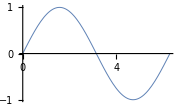

```mathematica
plot=Plot[Sin[x],{x,0,2π}]
```

This rule replaces each pair {x,y} with the pair {x,y/2}.

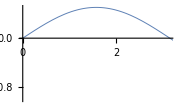

```mathematica
plot/.{x_?NumericQ,y_?NumericQ}:>{x,y/2}
```

Because the plot range is simply inherited from the original plot we lose some information after the transformation. To adjust the plot range, wrap the expression in Show and give an explicit plot range.

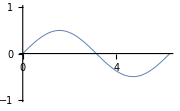

```mathematica
Show[
plot/.{x_?NumericQ,y_?NumericQ}:>{x,y/2},
PlotRange->{{0,2π},{-1,1}}]
```

For U.S. coins, you can import images from the U.S. Mint (www.usmint.gov); adjust accordingly for different currencies.

```mathematica
{q,d,n,p}={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
coins={p,p,q,n,d,d,p,q,q,p}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Here are the values, given by a list of rules.

```mathematica
values={p->.01,n->.05,d->.10,q->.25};
```

This replaces each coin by its value.

```mathematica
coins/.values
```

{0.01,0.01,0.25,0.05,0.1,0.1,0.01,0.25,0.25,0.01}

And here is the value of the set of coins.

```mathematica
Total[coins/.values]
```

1.04

Finally, here is a function that wraps up all these steps.

```mathematica
CountChange[coins_List]:=
Total[coins/.{-Graphics-->.01,-Graphics-->.05,-Graphics-->.10,-Graphics-->.25}]
```

```mathematica
CountChange[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

1.04

To prototype, we will only work with a small number of digits so we can easily check on our progress. Here are the ﬁrst 50 digits of π, starting from the right of the decimal point.

```mathematica
pidigs=First[RealDigits[π,10,50]]
```

{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,3,8,3,2,7,9,5,0,2,8,8,4,1,9,7,1,6,9,3,9,9,3,7,5,1}

The subsequence we are searching for is also given as a list of digits.

```mathematica
subseq={3,2,3,8};
```

One approach to this problem is to partition the list of digits in pidigs into lists of the same length as the list subseq, with overlapping sublists of offset one. This means that we will examine all sublists of length four from pidigs.

```mathematica
p=Partition[pidigs,Length[subseq],1]
```

{{3,1,4,1},{1,4,1,5},{4,1,5,9},{1,5,9,2},{5,9,2,6},{9,2,6,5},{2,6,5,3},{6,5,3,5},{5,3,5,8},{3,5,8,9},{5,8,9,7},{8,9,7,9},{9,7,9,3},{7,9,3,2},{9,3,2,3},{3,2,3,8},{2,3,8,4},{3,8,4,6},{8,4,6,2},{4,6,2,6},{6,2,6,4},{2,6,4,3},{6,4,3,3},{4,3,3,8},{3,3,8,3},{3,8,3,2},{8,3,2,7},{3,2,7,9},{2,7,9,5},{7,9,5,0},{9,5,0,2},{5,0,2,8},{0,2,8,8},{2,8,8,4},{8,8,4,1},{8,4,1,9},{4,1,9,7},{1,9,7,1},{9,7,1,6},{7,1,6,9},{1,6,9,3},{6,9,3,9},{9,3,9,9},{3,9,9,3},{9,9,3,7},{9,3,7,5},{3,7,5,1}}

Now we are ready for the pattern match. From the list p above, we are looking for the positions of any sublist that matches {3,2,3,8}. The subsequence 3238 occurs starting at the sixteenth digit in pidigs (ﬁfteen digits to the right of the decimal point).

```mathematica
pos=Position[p,subseq]
```

{{16}}

To mirror the default output of Position, we give the starting and ending positions of this match.

```mathematica
pos/.{num_?IntegerQ}:>{num,num+Length[subseq]-1}
```

{{16,19}}

Finally, let us turn this into a function and test it on a much larger example. Note that we use the pattern _List on both arguments, digits and subseq, so that FindSubsequence will only match arguments that have head List.

```mathematica
FindSubsequence[digits_List,subseq_List]:=
Position[Partition[digits,Length[subseq],1],subseq]/.{num_?IntegerQ}:>{num,num+Length[subseq]-1}
```

Store the ﬁrst 10000000 digits of π in the symbol pidigs.

```mathematica
pidigs=First[RealDigits[π,10,10^7,-1]];
```

The subsequence 314159 occurs seven times in the ﬁrst 10000000 digits of π, starting with the 176451st digit.

```mathematica
FindSubsequence[pidigs,{3,1,4,1,5,9}]//Timing
```

{10.2297,{{176451,176456},{1259351,1259356},{1761051,1761056},{6467324,6467329},{6518294,6518299},{9753731,9753736},{9973760,9973765}}}

In Section 7.2 we will see a different approach to this problem, one using string-processing functions that gives a substantial speedup compared to the computation above.

This creates another rule associated with FindSubsequence that simply takes each integer argument, converts it to a list of integer digits, and then passes that off to the rule above.

```mathematica
FindSubsequence[n_Integer,subseq_Integer]:=
FindSubsequence[IntegerDigits[n],IntegerDigits[subseq]]
```

Create the list of the ﬁrst 100000 digits of π.

```mathematica
pi=FromDigits[First@RealDigits[N[Pi,10^5]-3]];
```

The subsequence 1415 occurs seven times at the following locations in this digit expansion of π.

```mathematica
FindSubsequence[pi,1415]
```

{{1,4},{6955,6958},{29136,29139},{45234,45237},{79687,79690},{85880,85883},{88009,88012}}

This is a direct translation of the formula given in the exercise using a transformation rule to embed the two-dimensional vectors in three-space. It is important to get the pattern on the left-hand side of this deﬁnition correct so it matches a list consisting of three expressions (the three points).

```mathematica
area[Triangle[pts:{_,_,_}]]:=1/2 √(Det[pts[[All,{2,3}]]/.{a_,b_}:>{a,b,1}]^2+Det[pts[[All,{3,1}]]/.{a_,b_}:>{a,b,1}]^2+Det[pts[[All,{1,2}]]/.{a_,b_}:>{a,b,1}]^2)
```

And here is a check against the built-in function.

```mathematica
pts={{0,0,0},{3,4,0},{5,5,5}};
```

```mathematica
Area[Triangle[pts]]
```

5 √(13/2)

```mathematica
area[Triangle[pts]]
```

5 √(13/2)

First, import data from NASA’s Goddard Institute for Space Studies.

```mathematica
data=Import["http://data.giss.nasa.gov/gistemp/tabledata_v3/GLB.Ts+dSST.txt",{"Table","Data"}];
```

We need to strip out the header and footer information and just deal with the raw data: inspection of the data (not shown here) indicates the header info is in the ﬁrst eight rows and footer info is in the last twelve rows.

```mathematica
data[[9;;-13]];
```

Some ﬁltering is also necessary as the web page repeats header row (column names) frequently.

```mathematica
DeleteCases[data[[9;;-13]],{"Year",__}|{}];
```

Finally, we want row fourteen, the yearly temp difference from the norm. Also, divide by 100 to get actual °C.

```mathematica
tempData=TimeSeries[%[[All,14]]/100.,{"1880","2014"}]
```

TimeSeries[…]

Smooth with a ﬁve-year moving average.

```mathematica
avg=MovingAverage[tempData,5];
```

Plot original data (light gray) together with smoothed data (gray). Put a thick red line on the mean.

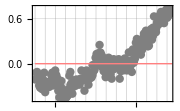

```mathematica
DateListPlot[{tempData,avg},PlotStyle->{LightGray,Gray},Mesh->All,MeshStyle->Directive[PointSize[Small],Gray],GridLines->{ToString/@Range[1880,2010,10],Automatic},ImageSize->Small,Epilog->{Pink,Thick,Line[{{"1880",0},{"2015",0}}]},FrameLabel->{None,"Difference from 1951-1980 average (°C)"},PlotLegends->{"yearly data","5-year moving avg"}]
```

```mathematica
Clear[x,y,z,f,g,p,q,d,n,a,b,c,d,e]
```

This imports the data from the Wilcox Observatory at Stanford University:

```mathematica
data=Import["http://wso.stanford.edu/meanfld/MF_timeseries.txt","Table"]
```

{{Date,Daily,MF,(uT)},{1975:05:16_20h,29},{1975:05:17_20h,22},14320,{2014:08:01_20h,69},{2014:08:02_20h,34},{2014:08:03_20h,6}}
 |  |  |  |

The data is of the form {date,mf} where date is a string and the magnetic ﬁeld measurement an integer giving the mean magnetic ﬁeld measurement in μ T (micro-Teslas).

```mathematica
data[[2]]//InputForm
```

{"1975:05:16_20h", 29}

Using the suggestion in the exercise, create a function to convert the string to a date object.

```mathematica
dateConvert[str_String]:=DateList[{str,{"Year",":","Month",":","Day","_","Hour","h"}}]
```

Then, using a rule, convert all the dates:

```mathematica
data2=Rest@data/.{date_String,val_}:>{dateConvert[date],val}
```

{{{1975,5,16,20,0,0.},29},{{1975,5,17,20,0,0.},22},{{1975,5,18,20,0,0.},24},14319,{{2014,8,1,20,0,0.},69},{{2014,8,2,20,0,0.},34},{{2014,8,3,20,0,0.},6}}
 |  |  |  |

Next, we need to deal with missing data. In the data set, they are indicated by the string “XXXX”.

```mathematica
data2[[8]]//InputForm
```

{{1975, 5, 23, 20, 0, 0.}, "XXXX"}

The next rule converts this string to Missing[] which the time series functions can deal with better.

```mathematica
data3=data2/.{date_List,_String}:>{date,Missing[]}
```

{{{1975,5,16,20,0,0.},29},{{1975,5,17,20,0,0.},22},{{1975,5,18,20,0,0.},24},14319,{{2014,8,1,20,0,0.},69},{{2014,8,2,20,0,0.},34},{{2014,8,3,20,0,0.},6}}
 |  |  |  |

Now, convert data3 to a time series object and plot.

```mathematica
tsData=TimeSeries[data3]
```

TimeSeries[…]

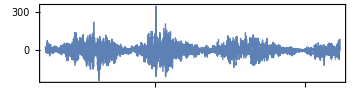

```mathematica
DateListPlot[tsData,AspectRatio->1/4,PlotStyle->Thin,PlotRange->All]
```

An alternative approach could use the DateStringFormat option to Import to put the dates in the proper form for the time series, but it is a bit slower to do the processing during import.

```mathematica
data=Rest@Import["http://wso.stanford.edu/meanfld/MF_timeseries.txt","Table", "DateStringFormat" -> {"Year",":","Month",":","Day","_","Hour","h"}]
```

{{Fri 16 May 1975,29},{Sat 17 May 1975,22},{Sun 18 May 1975,24},{Mon 19 May 1975,24},14317,{Thu 31 Jul 2014,87},{Fri 1 Aug 2014,69},{Sat 2 Aug 2014,34},{Sun 3 Aug 2014,6}}
 |  |  |  |

```mathematica
tsData=TimeSeries[data]
```

TimeSeries[…]

```mathematica
DateListPlot[tsData,AspectRatio->1/4,PlotStyle->Thin,PlotRange->All]
```

-Graphics-

5
Functions

Exercises: Functions for manipulating expressions

Use Partition and Mean to create a two-term moving average. Then repeat for a three-term moving average. Check your results against the built-in MovingAverage function.

```mathematica
MovingAverage[{a,b,c,d,e},2]
```

{(a+b)/2,(b+c)/2,(c+d)/2,(d+e)/2}

Use Apply to rewrite the deﬁnition of squareMatrixQ given in Section 4.1.

Use Inner to replicate the result in the text that used Thread to create a list of equations.

```mathematica
Thread[Equal[{x,y,z},{a,b,c}]]
```

{x==a,y==b,z==c}

Heron’s formula for the area of a triangle is given as follows:

A=√(s(s-a)(s-b)(s-c))

where a, b, and c are the lengths of the three sides of the triangle and s is the semiperimeter of the triangle, deﬁned by s=(a+b+c)/2. Compute the area of any triangle using Heron’s formula. You can check your result against the built-in Area function.

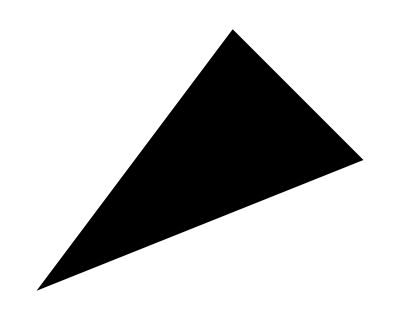

```mathematica
pt1={0,0};pt2={5,2};pt3={3,4};
Graphics[Triangle[{pt1,pt2,pt3}],Axes->Automatic]
```

```mathematica
Area[Triangle[{pt1,pt2,pt3}]]
```

7

Find all square numbers that contain the digits one through nine exactly once (see Madachy 1979). Use SquareNumberQ from Exercise 4 in Section 2.4.

In Section 2.4 we deﬁned a predicate PerfectQ[n] that returns True if n is a perfect number (n is a perfect number if it is equal to the sum of its proper divisors). Create a function PerfectSearch[n] that ﬁnds all perfect numbers less than n. Then ﬁnd all perfect numbers less than 10^6.

Turn the computation from Exercise 6 of Section 3.3 into a reusable function PrimesLessThan[n] that returns all prime numbers less than n.

One of the tasks in analyzing DNA sequences is determining the frequency with which the individual nucleotides G, C, A, and T occur. In addition, the frequency of longer “words” is often also of interest. For example, words of length two (or longer) such as AG, AT, CC are sometimes used to ﬁnd locations in the sequence where an evolutionary change may have occurred.

Nucleotides are generally represented as strings, so starting with the list {"A","T","G","C"}, create a list of all possible two-letter words from this alphabet. You can use StringJoin to return a string consisting of the concatenation of two strings.

```mathematica
StringJoin[{"A","T"}]//InputForm
```

AT

Finally, generalize this process to create words of length n for any such alphabet. For example, you could use a list of the amino acids as your alphabet.

```mathematica
aa={"A","R","N","D","C","E","Q","G","H","I","L","K","M","F","P","O","U","S","T","W","Y","V"};
```

Create a function LeadingDigit[n] that takes an integer n as an argument and returns the leading digit of n (see Exercise 7, Section 3.3). Set up your function so that it returns the leading digits of a list of numbers such as the ﬁrst 10000 Fibonacci numbers.

Given a set of points in the plane, ﬁnd the bounding rectangle that fully encloses the points. For three-dimensional sets of points, ﬁnd the bounding rectangular box. (See Figure Chapter.NumberedFigure.)

Bounding boxes (dashed lines) for points in two and three dimensions.

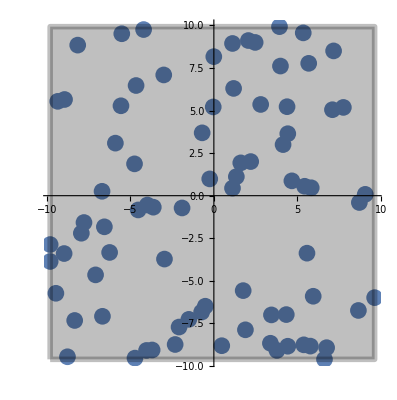

Given a set of points in the plane (or 3-space), ﬁnd the maximum distance between any pair of these points. This is often called the diameter of the point set. If your deﬁnition is general enough it should be able to handle points in any dimension.

Create a graphic that consists of n randomly colored circles in the plane with random centers and random radii. Consider using Thread or MapThread to thread Circle[…] across the lists of centers and radii.

While matrices can easily be added using Plus, matrix multiplication is a bit more involved. The Dot function, written as a single period, is used.

```mathematica
{{1,2},{3,4}}.{x,y}
```

{x+2 y,3 x+4 y}

Perform matrix multiplication on {{1,2},{3,4}} and {x,y} without using Dot.

An adjacency matrix can be thought of as representing a graph of vertices and edges where a value of one in position a_ij indicates an edge between vertex i and vertex j, whereas a value of zero indicates no such edge between vertices i and j.

```mathematica
mat=RandomInteger[1,{5,5}];
MatrixForm[mat]
```

(1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 1)

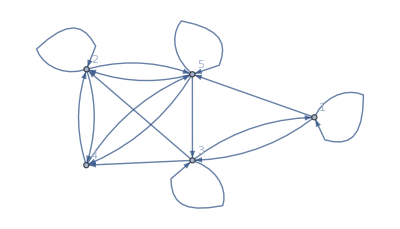

```mathematica
AdjacencyGraph[mat,VertexLabels->"Name"]
```

Compute the total number of edges for each vertex in both the adjacency matrix and graph representations. For example, you should get the following edge counts for the ﬁve vertices represented in the above graph. Note: self-loops count as two edges each.

{5, 7, 7, 5, 8}

Create a function ToEdges[lis] that takes a list of pairs of elements and transforms it into a list of directed edges suitable for a graph. For example:

```mathematica
lis=RandomInteger[9,{12,2}]
```

{{1,4},{1,5},{1,7},{1,9},{8,0},{3,1},{9,2},{6,2},{3,4},{4,4},{7,6},{2,8}}

```mathematica
ToEdges[lis]
```

{1->4,1->5,1->7,1->9,8->0,3->1,9->2,6->2,3->4,4->4,7->6,2->8}

Make sure that your function also works in the case where its argument is a single list of a pair of elements.

```mathematica
ToEdges[{3,6}]
```

3->6

FactorInteger[n] returns a nested list of prime factors and their exponents for the number n.

```mathematica
FactorInteger[3628800]
```

{{2,8},{3,4},{5,2},{7,1}}

Use Apply to reconstruct the original number from this nested list.

Repeat the above exercise but instead use Inner to reconstruct the original number n from the factorization given by FactorInteger[n].

Create a function PrimeFactorForm[n] that formats its argument n in prime factorization form. You will need to use Superscript and CenterDot to format the factored integer.

```mathematica
PrimeFactorForm[12]
```

2^2·3^1

The Vandermonde matrix arises in Lagrange interpolation and in reconstructing statistical distributions from their moments. Construct the Vandermonde matrix of order n:

(1 | x_1 | x_1^2 | ⋯ | x_1^(n-1)
1 | x_2 | x_2^2 | ⋯ | x_2^(n-1)
⋮ | ⋮ | ⋮ | ⋱ | ⋮
1 | x_n | x_n^2 | ⋯ | x_n^(n-1))

Using Inner, write a function div[vecs,vars] that computes the divergence of an n-dimensional vector ﬁeld, vecs={e_1,e_2,…,e_n}, dependent upon n variables, vars={v_1,v_2,…,v_n}. The divergence is given by the sum of the pairwise partial derivatives.

(∂e_1)/(∂v_1)+(∂e_2)/(∂v_2)+⋯+(∂e_n)/(∂v_n)

Using Outer, create a function JacobianMatrix[vec,vars] that returns the Jacobian of the vector vec in the variables given by the list vars. Then use JacobianMatrix to compute the volume of the hypersphere in two (circle) and three (sphere) dimensions by integrating the absolute value of the determinant of the Jacobian.

The example in this section on Select and Pick found Mersenne numbers 2^n-1 that are prime for exponents n from 1 to 100. Modify that example to only use prime exponents – a basic theorem in number theory states that a Mersenne number with composite exponent must be composite Crandall and Pomerance (2005).

Solutions

If we are doing a 2-term moving average, then partition into 2-element lists.

```mathematica
Clear[a,b,c,d,e,f,g,h,i]
```

```mathematica
Partition[{a,b,c,d,e},2,1]
```

{{a,b},{b,c},{c,d},{d,e}}

Then take the mean of each pair.

```mathematica
Map[Mean,%]
```

{(a+b)/2,(b+c)/2,(c+d)/2,(d+e)/2}

Check against the built-in function.

```mathematica
MovingAverage[{a,b,c,d,e},2]
```

{(a+b)/2,(b+c)/2,(c+d)/2,(d+e)/2}

Similarly for the 3-term moving average.

```mathematica
Map[Mean,Partition[{a,b,c,d,e},3,1]]
```

{1/3 (a+b+c),1/3 (b+c+d),1/3 (c+d+e)}

First, here is the deﬁnition given in Section 4.1.

```mathematica
squareMatrixQ[mat_?MatrixQ]:=Dimensions[mat][[1]]==Dimensions[mat][[2]]
```

For a matrix, Dimensions returns a list of two integers. Applying Equal to the list will return True if the two dimensions are identical, that is, if the matrix is square.

```mathematica
squareMatrixQ[mat_?MatrixQ]:=Apply[Equal,Dimensions[mat]]
```

```mathematica
squareMatrixQ[{{a,b},{c,d},{e,f}}]
```

False

```mathematica
squareMatrixQ[{{a,b,c},{d,e,f},{g,h,i}}]
```

True

Here is the example from the text.

```mathematica
Clear[x,y,z]
```

```mathematica
Thread[Equal[{x,y,z},{a,b,c}]]
```

{x==a,y==b,z==c}

The ﬁrst argument to Inner is a function that will be threaded over the following lists. Afterwards, the fourth argument to Inner will be applied to the result. So we use Equal as that ﬁrst function.

```mathematica
Inner[Equal,{x,y,z},{a,b,c},List]
```

{x==a,y==b,z==c}

Given three points that deﬁne a triangle, we need the distances between every pair of points, that is, the length of the sides of the triangles.

```mathematica
pt1={0,0};
pt2={5,2};
pt3={3,5};
```

First, make a list of the possible pairs of points.

```mathematica
pairs=Subsets[{pt1,pt2,pt3},{2}]
```

{{{0,0},{5,2}},{{0,0},{3,5}},{{5,2},{3,5}}}

Then apply EuclideanDistance at level one to get the distance between each pair.

```mathematica
{a,b,c}=Apply[EuclideanDistance,pairs,{1}]
```

{√29,√34,√13}

Here is the semiperimeter:

```mathematica
s=(a+b+c)/2
```

1/2 (√13+√29+√34)

And ﬁnally, the area computation given by Heron’s formula:

```mathematica
√(s(s-a)(s-b)(s-c))//Simplify
```

19/2

Check:

```mathematica
Area[Triangle[{pt1,pt2,pt3}]]
```

19/2

```mathematica
Clear[a,b,c,s]
```

Here is the deﬁnition of SquareNumberQ from Exercise 4 in Section 2.4.

```mathematica
SquareNumberQ[n_Integer]:=IntegerQ[√n]
```

First, create the numbers that contain each of the digits using FromDigits.

```mathematica
FromDigits[{1,2,3,4,5,6,7,8,9}]
```

123456789

This then creates all such permutations.

```mathematica
nums=Map[FromDigits,Permutations[Range[9]]]
```

{123456789,123456798,123456879,123456897,123456978,123456987,123457689,123457698,123457869,362862,987653241,987653412,987653421,987654123,987654132,987654213,987654231,987654312,987654321}
 |  |  |  |

And here are those numbers from nums that are square.

```mathematica
Select[nums,SquareNumberQ]
```

{139854276,152843769,157326849,215384976,245893761,254817369,326597184,361874529,375468129,382945761,385297641,412739856,523814769,529874361,537219684,549386721,587432169,589324176,597362481,615387249,627953481,653927184,672935481,697435281,714653289,735982641,743816529,842973156,847159236,923187456}

A quick check that these are all square numbers.

```mathematica
√%
```

{11826,12363,12543,14676,15681,15963,18072,19023,19377,19569,19629,20316,22887,23019,23178,23439,24237,24276,24441,24807,25059,25572,25941,26409,26733,27129,27273,29034,29106,30384}

What would happen if you ﬁrst found all 9-digit square numbers and then determined which of those contained only the digits one through nine? A bit of thought should convince you that that approach would be quite time and resource intensive as the ﬁrst step would require checking every number below 10^9 to see if it was a square.

Here is the deﬁnition of PerfectQ.

```mathematica
PerfectQ[n_]:=Total[Divisors[n]]==2n
```

To ﬁnd all perfect numbers less than n, use Select on the list given by Range[n], using PerfectQ as the test.

```mathematica
PerfectSearch[n_]:=Select[Range[n],PerfectQ]
```

This ﬁnds the four perfect numbers less than one million.

```mathematica
PerfectSearch[10^6]//Timing
```

{9.25325,{6,28,496,8128}}

This is quite compute-intensive. You can speed things up by using a built-in function that is designed speciﬁcally for this task, DivisorSigma.

```mathematica
PerfectQ[n_]:=DivisorSigma[1,n]==2n
```

```mathematica
PerfectSearch[10^6]//Timing
```

{4.1752,{6,28,496,8128}}

Based on Exercise 6 from Section 3.3, here is the deﬁnition:

```mathematica
PrimesLessThan[n_]:=Table[Prime[p],{p,PrimePi[n]}]
```

```mathematica
PrimesLessThan[100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

Since we are interested in all possible two-letter combinations of the list of nucleotides, the function that should come to mind is Outer. The only question is what function to thread across the lists? A moment’s thought should convince you that StringJoin is what is needed.

```mathematica
lis=Outer[StringJoin,{"A","C","T","G"},{"A","C","T","G"}]
```

{{AA,AC,AT,AG},{CA,CC,CT,CG},{TA,TC,TT,TG},{GA,GC,GT,GG}}

You can see what is happening by using a symbolic function sj instead of StringJoin:

```mathematica
Outer[sj,{"A","C","T","G"},{"A","C","T","G"}]
```

{{sj[A,A],sj[A,C],sj[A,T],sj[A,G]},{sj[C,A],sj[C,C],sj[C,T],sj[C,G]},{sj[T,A],sj[T,C],sj[T,T],sj[T,G]},{sj[G,A],sj[G,C],sj[G,T],sj[G,G]}}

Finally, we need to ﬂatten the list lis.

```mathematica
Flatten[lis]
```

{AA,AC,AT,AG,CA,CC,CT,CG,TA,TC,TT,TG,GA,GC,GT,GG}

Generalizing is a bit tricky. Here is what we would need to do for words of length three.

```mathematica
Outer[StringJoin,{"A","C","T","G"},{"A","C","T","G"},{"A","C","T","G"}]//Flatten
```

{AAA,AAC,AAT,AAG,ACA,ACC,ACT,ACG,ATA,ATC,ATT,ATG,AGA,AGC,AGT,AGG,CAA,CAC,CAT,CAG,CCA,CCC,CCT,CCG,CTA,CTC,CTT,CTG,CGA,CGC,CGT,CGG,TAA,TAC,TAT,TAG,TCA,TCC,TCT,TCG,TTA,TTC,TTT,TTG,TGA,TGC,TGT,TGG,GAA,GAC,GAT,GAG,GCA,GCC,GCT,GCG,GTA,GTC,GTT,GTG,GGA,GGC,GGT,GGG}

But what about words of length four or fourteen? Surely we can’t manually keep adding the list of nucleotides inside Outer. Well, for words of length four say, we want a sequence of four copies of the list {"A","C","T","G"}. We can use Table to generate that but then we have too many nested lists to pass to Outer.

```mathematica
Table[{"A","C","T","G"},{4}]
```

{{A,C,T,G},{A,C,T,G},{A,C,T,G},{A,C,T,G}}

```mathematica
Outer[StringJoin,%]
```

{{A,C,T,G},{A,C,T,G},{A,C,T,G},{A,C,T,G}}

The key here is to pass a sequence of these four lists. There is a function designed speciﬁcally for this situation: Sequence. We will apply it to the result of Table above and then give that sequence as the second argument to Outer.

```mathematica
Apply[Sequence,Table[{"A","C","T","G"},{4}]]
```

Sequence[{A,C,T,G},{A,C,T,G},{A,C,T,G},{A,C,T,G}]

```mathematica
Outer[StringJoin,%]//Flatten
```

{AAAA,AAAC,AAAT,AAAG,AACA,AACC,AACT,AACG,AATA,AATC,AATT,AATG,AAGA,AAGC,AAGT,AAGG,ACAA,ACAC,ACAT,ACAG,ACCA,ACCC,ACCT,ACCG,ACTA,ACTC,ACTT,ACTG,ACGA,ACGC,ACGT,ACGG,ATAA,ATAC,ATAT,ATAG,ATCA,ATCC,ATCT,ATCG,ATTA,ATTC,ATTT,ATTG,ATGA,ATGC,ATGT,ATGG,AGAA,AGAC,AGAT,AGAG,AGCA,AGCC,AGCT,AGCG,AGTA,AGTC,AGTT,AGTG,AGGA,AGGC,AGGT,AGGG,CAAA,CAAC,CAAT,CAAG,CACA,CACC,CACT,CACG,CATA,CATC,CATT,CATG,CAGA,CAGC,CAGT,CAGG,CCAA,CCAC,CCAT,CCAG,CCCA,CCCC,CCCT,CCCG,CCTA,CCTC,CCTT,CCTG,CCGA,CCGC,CCGT,CCGG,CTAA,CTAC,CTAT,CTAG,CTCA,CTCC,CTCT,CTCG,CTTA,CTTC,CTTT,CTTG,CTGA,CTGC,CTGT,CTGG,CGAA,CGAC,CGAT,CGAG,CGCA,CGCC,CGCT,CGCG,CGTA,CGTC,CGTT,CGTG,CGGA,CGGC,CGGT,CGGG,TAAA,TAAC,TAAT,TAAG,TACA,TACC,TACT,TACG,TATA,TATC,TATT,TATG,TAGA,TAGC,TAGT,TAGG,TCAA,TCAC,TCAT,TCAG,TCCA,TCCC,TCCT,TCCG,TCTA,TCTC,TCTT,TCTG,TCGA,TCGC,TCGT,TCGG,TTAA,TTAC,TTAT,TTAG,TTCA,TTCC,TTCT,TTCG,TTTA,TTTC,TTTT,TTTG,TTGA,TTGC,TTGT,TTGG,TGAA,TGAC,TGAT,TGAG,TGCA,TGCC,TGCT,TGCG,TGTA,TGTC,TGTT,TGTG,TGGA,TGGC,TGGT,TGGG,GAAA,GAAC,GAAT,GAAG,GACA,GACC,GACT,GACG,GATA,GATC,GATT,GATG,GAGA,GAGC,GAGT,GAGG,GCAA,GCAC,GCAT,GCAG,GCCA,GCCC,GCCT,GCCG,GCTA,GCTC,GCTT,GCTG,GCGA,GCGC,GCGT,GCGG,GTAA,GTAC,GTAT,GTAG,GTCA,GTCC,GTCT,GTCG,GTTA,GTTC,GTTT,GTTG,GTGA,GTGC,GTGT,GTGG,GGAA,GGAC,GGAT,GGAG,GGCA,GGCC,GGCT,GGCG,GGTA,GGTC,GGTT,GGTG,GGGA,GGGC,GGGT,GGGG}

Here then is a function that generalizes this process. We have included some pattern matching of the arguments to insure that the alphabet is a list of one or more strings and that the word length n is a positive integer.

```mathematica
Clear[NGrams]
```

```mathematica
NGrams[alphabet:{__String},n_Integer?Positive]:=Flatten[Outer[StringJoin,Apply[Sequence,Table[alphabet,{n}]]]]
```

```mathematica
NGrams[{"A","C","T","G"},3]
```

{AAA,AAC,AAT,AAG,ACA,ACC,ACT,ACG,ATA,ATC,ATT,ATG,AGA,AGC,AGT,AGG,CAA,CAC,CAT,CAG,CCA,CCC,CCT,CCG,CTA,CTC,CTT,CTG,CGA,CGC,CGT,CGG,TAA,TAC,TAT,TAG,TCA,TCC,TCT,TCG,TTA,TTC,TTT,TTG,TGA,TGC,TGT,TGG,GAA,GAC,GAT,GAG,GCA,GCC,GCT,GCG,GTA,GTC,GTT,GTG,GGA,GGC,GGT,GGG}

Here is a list of all possible words of length two from the alphabet of amino acids.

```mathematica
alphabet={"K","P","W","G","E","V","Y","L","M","Q","R","S","F","D","H","I","C","T","N","A"};
```

```mathematica
NGrams[alphabet,2]
```

{KK,KP,KW,KG,KE,KV,KY,KL,KM,KQ,KR,KS,KF,KD,KH,KI,KC,KT,KN,KA,PK,PP,PW,PG,PE,PV,PY,PL,PM,PQ,PR,PS,PF,PD,PH,PI,PC,PT,PN,PA,WK,WP,WW,WG,WE,WV,WY,WL,WM,WQ,WR,WS,WF,WD,WH,WI,WC,WT,WN,WA,GK,GP,GW,GG,GE,GV,GY,GL,GM,GQ,GR,GS,GF,GD,GH,GI,GC,GT,GN,GA,EK,EP,EW,EG,EE,EV,EY,EL,EM,EQ,ER,ES,EF,ED,EH,EI,EC,ET,EN,EA,VK,VP,VW,VG,VE,VV,VY,VL,VM,VQ,VR,VS,VF,VD,VH,VI,VC,VT,VN,VA,YK,YP,YW,YG,YE,YV,YY,YL,YM,YQ,YR,YS,YF,YD,YH,YI,YC,YT,YN,YA,LK,LP,LW,LG,LE,LV,LY,LL,LM,LQ,LR,LS,LF,LD,LH,LI,LC,LT,LN,LA,MK,MP,MW,MG,ME,MV,MY,ML,MM,MQ,MR,MS,MF,MD,MH,MI,MC,MT,MN,MA,QK,QP,QW,QG,QE,QV,QY,QL,QM,QQ,QR,QS,QF,QD,QH,QI,QC,QT,QN,QA,RK,RP,RW,RG,RE,RV,RY,RL,RM,RQ,RR,RS,RF,RD,RH,RI,RC,RT,RN,RA,SK,SP,SW,SG,SE,SV,SY,SL,SM,SQ,SR,SS,SF,SD,SH,SI,SC,ST,SN,SA,FK,FP,FW,FG,FE,FV,FY,FL,FM,FQ,FR,FS,FF,FD,FH,FI,FC,FT,FN,FA,DK,DP,DW,DG,DE,DV,DY,DL,DM,DQ,DR,DS,DF,DD,DH,DI,DC,DT,DN,DA,HK,HP,HW,HG,HE,HV,HY,HL,HM,HQ,HR,HS,HF,HD,HH,HI,HC,HT,HN,HA,IK,IP,IW,IG,IE,IV,IY,IL,IM,IQ,IR,IS,IF,ID,IH,II,IC,IT,IN,IA,CK,CP,CW,CG,CE,CV,CY,CL,CM,CQ,CR,CS,CF,CD,CH,CI,CC,CT,CN,CA,TK,TP,TW,TG,TE,TV,TY,TL,TM,TQ,TR,TS,TF,TD,TH,TI,TC,TT,TN,TA,NK,NP,NW,NG,NE,NV,NY,NL,NM,NQ,NR,NS,NF,ND,NH,NI,NC,NT,NN,NA,AK,AP,AW,AG,AE,AV,AY,AL,AM,AQ,AR,AS,AF,AD,AH,AI,AC,AT,AN,AA}

IntegerDigits[n] gives a list of the digits in n. First returns the ﬁrst element in that list. Here then is the function deﬁnition.

```mathematica
LeadingDigit[n_Integer]:=First[IntegerDigits[n]]
```

```mathematica
LeadingDigit[2495874985797]
```

2

By default, this function has no attributes, in particular it is not listable.

```mathematica
LeadingDigit[{434,826,5632}]
```

LeadingDigit[{434,826,5632}]

We could map the function across lists, but instead we will give it the attribute that causes it to automatically map across lists. Set the function to have the Listable attribute.

```mathematica
SetAttributes[LeadingDigit,Listable]
```

Now, create a table of the ﬁrst 10000 Fibonacci numbers.

```mathematica
fibs=Table[Fibonacci[i],{i,10000}];
```

Because LeadingDigit is now a listable function, it automatically maps across the list fibs. Here then is a histogram of the leading digits of the ﬁrst 10000 Fibonacci digits.

```mathematica
Histogram[LeadingDigit[fibs]]
```

-Graphics-

Start with a set of points in the plane.

```mathematica
data=RandomReal[{-20,20},{40,2}];
```

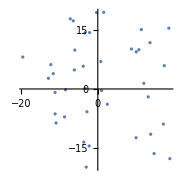

```mathematica
ListPlot[data,AspectRatio->Automatic]
```

The data are of the form {{x_1,y_1},{x_2,y_2},…}.

```mathematica
Take[data,2]
```

{{9.93547,-12.4866},{-2.23917,-14.5885}}

Transposing the data gives a list all the x-coordinates, followed by a list of all the y-coordinates.

```mathematica
Transpose[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}]
```

{{x_1,x_2,x_3},{y_1,y_2,y_3}}

Then map Min and Max over this list.

```mathematica
Map[Min,%]
```

{Min[x_1,x_2,x_3],Min[y_1,y_2,y_3]}

Here then are the computations for our data. Notice the parallel assignments saving some typing.

```mathematica
{xmin,ymin}=Map[Min,Transpose[data]]
```

{-19.4808,-19.9974}

```mathematica
{xmax,ymax}=Map[Max,Transpose[data]]
```

{18.7094,19.5983}

As it turns out, a built-in function is available for this task. MinMax operates on vectors of numbers. So we will map it across the transposed data. Note the form of the data that is returned: ﬁrst a list of the min and max x-coordinates and then likewise for the y-coordinates. A bit of rearranging is needed for Rectangle.

```mathematica
{{xmin,xmax},{ymin,ymax}}=Map[MinMax,Transpose[data]]
```

{{-19.4808,18.7094},{-19.9974,19.5983}}

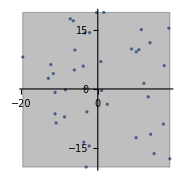

```mathematica
ListPlot[data,AspectRatio->Automatic,Epilog->{
Opacity[.25],EdgeForm[Dashed],Rectangle[{xmin,ymin},{xmax,ymax}]}]
```

And here is the three-dimensional case:

```mathematica
data3d=RandomReal[{-10,10},{25,3}];
```

```mathematica
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}=Map[MinMax,Transpose[data3d]]
```

{{-9.06054,8.82294},{-9.13641,8.77756},{-9.47419,8.14716}}

```mathematica
Graphics3D[{
Point[data3d],
Blue,Opacity[.25],Cuboid[{xmin,ymin,zmin},{xmax,ymax,zmax}]
},Boxed->False]
```

-Graphics3D-

First create a set of points with which to work.

```mathematica
pts=RandomReal[1,{100,2}];
```

The set of all two-element subsets is given by:

```mathematica
pairs=Subsets[pts,{2}];
```

Apply the distance function to pairs. Note the need to apply EuclideanDistance at level one.

```mathematica
Apply[EuclideanDistance,pairs,{1}];
```

The maximum distance (diameter) is given by Max.

```mathematica
Max[%]
```

1.27562

Here is a function that puts it all together.

```mathematica
PointsetDiameter[pts_List]:=Max[Apply[EuclideanDistance,Subsets[pts,{2}],{1}]]
```

```mathematica
PointsetDiameter[pts]
```

1.27562

To get the coordinate points that give this maximum distance, use MaximalBy:

```mathematica
MaximalBy[pairs,Apply[EuclideanDistance,#]&]
```

{{{0.94701,0.0541054},{0.0448236,0.95592}}}

A quick check:

```mathematica
Apply[EuclideanDistance,%,{1}]
```

{1.27562}

In fact, this function works on n-dimensional point sets.

```mathematica
pts3D=RandomReal[1,{5,3}]
```

{{0.00512186,0.739216,0.594529},{0.88659,0.837747,0.72644},{0.274863,0.754823,0.71913},{0.291825,0.990644,0.528335},{0.88648,0.339045,0.871665}}

```mathematica
PointsetDiameter[pts3D]
```

1.00684

Because of the use of Subsets, this computation will not scale well. Computing subsets has computational complexity O(n^2) and so the time to compute subsets is quadratic in the size of the set.

```mathematica
Timing[Subsets[Range[1000],{2}];]
```

{0.07042,Null}

Twice as large of a set should cause the time to quadruple.

```mathematica
Timing[Subsets[Range[2000],{2}];]
```

{0.315402,Null}

Exercise 5, Section 9.1 explores another approach – one that involves the convex hull – to speed up the computation.

First, create the random centers and radii.

```mathematica
n=12;
centers=RandomReal[{-1,1},{n,2}]
```

{{-0.391653,0.830624},{-0.747273,-0.460966},{0.656809,-0.910538},{-0.187957,-0.421397},{0.574283,0.718045},{-0.620718,-0.831547},{-0.548517,-0.791468},{-0.578859,-0.448743},{0.330763,0.848178},{-0.948835,-0.268074},{0.911755,0.460441},{0.146787,0.898121}}

```mathematica
radii=RandomReal[1,{n}]
```

{0.409292,0.650746,0.8457,0.947663,0.954289,0.262659,0.362816,0.351422,0.0984283,0.601188,0.0410166,0.342364}

MapThread is perfect for the task of grabbing one center, one radii, and wrapping Circle around them.

```mathematica
circles=MapThread[Circle,{centers,radii}];
```

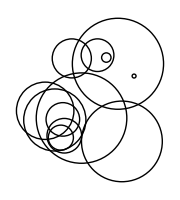

```mathematica
Graphics[circles]
```

And here is a rule to transform each circle into a scoped list that includes Thick and RandomColor. Note the need for the delayed rule (:>); try it with an immediate rule to understand why.

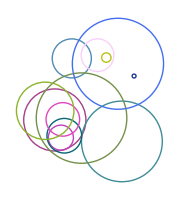

```mathematica
Graphics[circles/.Circle[x__]:>{Thick,RandomColor[],Circle[x]}]
```

This can be done either in two steps, or by using the Inner function.

```mathematica
Transpose[{{1,2},{3,4}}] {x,y}
```

{{x,3 x},{2 y,4 y}}

```mathematica
Total[%]
```

{x+2 y,3 x+4 y}

```mathematica
Inner[Times,{{1,2},{3,4}},{x,y},Plus]
```

{x+2 y,3 x+4 y}

Here is a test matrix.

```mathematica
mat=RandomInteger[1,{5,5}];
MatrixForm[mat]
```

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0)

A bit of thought should convince you that adding the matrix to its transpose and then totaling all the ones in each row will give the correct count.

```mathematica
Map[Total,mat+Transpose[mat]]
```

{4,3,4,3,4}

Using graphs you can accomplish the same thing directly using VertexDegree.

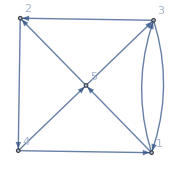

```mathematica
gr=AdjacencyGraph[mat,VertexLabels->"Name"]
```

```mathematica
VertexDegree[gr]
```

{4,3,4,3,4}

Applying DirectedEdge at level one will do the trick.

```mathematica
ToEdges[lis:{{_,_}..}]:=Apply[DirectedEdge,lis,{1}]
```

```mathematica
lis=RandomInteger[9,{12,2}];
ToEdges[lis]
```

{3->6,2->4,0->5,1->2,3->6,7->2,3->6,0->0,2->8,4->9,3->7,6->6}

This rule fails for the case when the argument is a single ﬂat list of a pair of elements.

```mathematica
ToEdges[{3,6}]
```

ToEdges[{3,6}]

A second rule is needed for this case.

```mathematica
ToEdges[lis:{_,_}]:=Apply[DirectedEdge,lis]
```

```mathematica
ToEdges[{3,6}]
```

3->6

To get down to the level of the nested lists, you have to use a second argument to Apply.

```mathematica
facs=FactorInteger[3628800]
```

{{2,8},{3,4},{5,2},{7,1}}

```mathematica
Apply[Power,facs,{1}]
```

{256,81,25,7}

One more use of Apply is needed to multiply these terms.

```mathematica
Apply[Times,%]
```

3628800

Here is a function that puts this all together.

```mathematica
ExpandFactors[lis_]:=Apply[Times,Apply[Power,lis,{1}]]
```

```mathematica
FactorInteger[295232799039604140847618609643520000000]
```

{{2,32},{3,15},{5,7},{7,4},{11,3},{13,2},{17,2},{19,1},{23,1},{29,1},{31,1}}

```mathematica
ExpandFactors[%]
```

295232799039604140847618609643520000000

Here is a factorization we can use to work through this problem.

```mathematica
facs=FactorInteger[3628800]
```

{{2,8},{3,4},{5,2},{7,1}}

Another approach uses Transpose to separate the bases from their exponents, then uses Inner to put things back together.

```mathematica
{base,exponents}=Transpose[facs]
```

{{2,3,5,7},{8,4,2,1}}

```mathematica
Inner[Power,base,exponents,Times]
```

3628800

Since Tranpose returns a list of two lists in this example, we need to strip the outer list. This is done by applying Sequence.

```mathematica
ExpandFactors2[lis_]:=Inner[Power,Sequence@@Transpose[lis],Times]
```

```mathematica
ExpandFactors2[facs]
```

3628800

First, here is the prime factorization of a test integer:

```mathematica
lis=FactorInteger[10!]
```

{{2,8},{3,4},{5,2},{7,1}}

Apply Superscript at level one to each of the sublists:

```mathematica
Apply[Superscript,lis,{1}]
```

{2^8,3^4,5^2,7^1}

Finally, apply CenterDot to this list.

```mathematica
Apply[CenterDot,%]
```

2^8·3^4·5^2·7^1

Put it all together (using shorthand notation for Apply) and Apply at level one.

```mathematica
PrimeFactorForm[p_]:=CenterDot@@(Superscript@@@FactorInteger[p])
```

```mathematica
PrimeFactorForm[20!]
```

2^18·3^8·5^4·7^2·11^1·13^1·17^1·19^1

Unfortunately, this rule fails for numbers that have only one prime factor.

```mathematica
PrimeFactorForm[9]
```

CenterDot[3^2]

A second rule is needed for this special case.

```mathematica
PrimeFactorForm[p_?PrimePowerQ]:=First[Superscript@@@FactorInteger[p]]
```

```mathematica
PrimeFactorForm[9]
```

3^2

A subtle point is that Mathematica has automatically ordered these two rules, putting the one involving prime powers ﬁrst.

```mathematica
?PrimeFactorForm
```

Global`PrimeFactorForm

PrimeFactorForm[p_?PrimePowerQ]:=First[Apply[Superscript,FactorInteger[p],{1}]]
 
PrimeFactorForm[p_]:=CenterDot@@Apply[Superscript,FactorInteger[p],{1}]

This reordering (we evaluated the rules in a different order) is essential for this function to work properly. If the general rule was checked ﬁrst, it would apply to arguments that happen to be prime powers and it would give wrong answers.

One ﬁnal point: the expressions returned by PrimeFactorForm will not evaluate like ordinary expressions due to the use of CenterDot which has no evaluation rules associated with it. You could add an “interpretation” to such expressions by using Interpretation[disp,expr] as follows.

```mathematica
PrimeFactorForm[p_Integer]:=With[{fp=FactorInteger[p]},
Interpretation[
CenterDot@@(Superscript@@@fp),
Times@@(Power@@@fp)]]
```

Now the output of the following expression can be evaluated directly to get an interpreted result.

```mathematica
PrimeFactorForm[12!]
```

2^10·3^5·5^2·7^1·11^1

This is a straightforward application of the Outer function.

```mathematica
VandermondeMatrix[n_,x_]:=
Outer[Power,Table[Subscript[x, i],{i,1,n}],Range[0,n-1]]
```

```mathematica
VandermondeMatrix[4,x]//MatrixForm
```

(1 | x_1 | x_1^2 | x_1^3
1 | x_2 | x_2^2 | x_2^3
1 | x_3 | x_3^2 | x_3^3
1 | x_4 | x_4^2 | x_4^3)

If we ﬁrst look at a symbolic result, we should be able to see how to construct our function. For three vectors and three variables, here is the divergence (think of d as the derivative operator).

```mathematica
Inner[d,{e1,e2,e3},{v1,v2,v3},Plus]
```

d[e1,v1]+d[e2,v2]+d[e3,v3]

So for arbitrary-length vectors and variables, we have:

```mathematica
div[vecs_,vars_]:=Inner[D,vecs,vars,Plus]
```

As a check, we can compute the divergence of the standard gravitational or electric force ﬁeld, which should be zero.

```mathematica
div[{x,y,z}/(x^2+y^2+z^2)^(3/2),{x,y,z}]
```

-(3 x^2)/((x^2+y^2+z^2)^(5/2))-(3 y^2)/((x^2+y^2+z^2)^(5/2))-(3 z^2)/((x^2+y^2+z^2)^(5/2))+3/((x^2+y^2+z^2)^(3/2))

```mathematica
Simplify[%]
```

0

Finally, we should note that this deﬁnition of divergence is a bit delicate as we are doing no argument checking at this point. For example, it would be sensible to insure that the length of the vector list is the same as the length of the variable list before starting the computation. Refer to Chapter 4 for a discussion of how to use pattern matching to deal with this issue.

The Jacobian is given by the following outer product:

```mathematica
JacobianMatrix[vec_List,vars_List]:=Outer[D,vec,vars]
```

Add a condition that the dimensions of vec and vars are the same.

```mathematica
JacobianMatrix[vec_List,vars_List]:=Outer[D,vec,vars]/;Dimensions[vec]==Dimensions[vars]
```

To compute the volume of the hypersphere in dimension two, start with a point in ℝ^2 expressed in polar coordinates:

```mathematica
x=ρ Cos[θ];
y=ρ Sin[θ];
```

Then compute the determinant of the Jacobian.

```mathematica
JacobianMatrix[{x,y},{ρ,θ}]//MatrixForm
```

(Cos[θ] | -ρ Sin[θ]
Sin[θ] | ρ Cos[θ])

```mathematica
Det[%]//Simplify
```

ρ

The volume of the hypersphere is obtained by integrating the determinant of the Jacobian over ρ and θ:

```mathematica
Integrate[Abs@Det[JacobianMatrix[{x,y},{ρ,θ}]],{ρ,0,r},{θ,0,2 π},Assumptions->r>0]
```

π r^2

And here is the computation for dimension three:

```mathematica
x=ρ Cos[θ]Sin[ϕ];
y=ρ Sin[θ]Sin[ϕ];
z=ρ Cos[ϕ];
```

```mathematica
Integrate[Abs@Det@JacobianMatrix[{x,y,z},{ρ,θ,ϕ}],{ρ,0,r},{θ,-π/2,π/2},{ϕ,0,2π}]
```

(4 π r^3)/3

First create a table of primes and then use that list for values of p in the second table.

```mathematica
primes=Table[Prime[n],{n,1,50}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229}

```mathematica
Select[Table[2^p-1,{p,primes}],PrimeQ]
```

{3,7,31,127,8191,131071,524287,2147483647,2305843009213693951,618970019642690137449562111,162259276829213363391578010288127,170141183460469231731687303715884105727}

Or you could do the same thing more directly.

```mathematica
Select[Table[2^Prime[n]-1,{n,1,50}],PrimeQ]
```

{3,7,31,127,8191,131071,524287,2147483647,2305843009213693951,618970019642690137449562111,162259276829213363391578010288127,170141183460469231731687303715884105727}

```mathematica
Clear[a,b,c,d,e,x,y,z,pt1,pt2,pt3]
```

Exercises: Iterating functions

Use NestWhileList to iterate the julia function similarly to how it was iterated with FixedPointList in the text.

Use NestList to iterate the process of summing cubes of digits, that is, starting with an initial integer generate a list of the successive sums of cubes of its digits. For example, starting with 4, the list should look like {4,64,280,520,133,…}, since 4^3=64, 6^3+4^3=280, etc. Extend the list to at least ﬁfteen values, experiment with other starting values, and look for patterns in the sequences.

Following on the example in this section iterating rotations of a triangle, use Translate to iterate the translation of a square or other polygon.

Using Fold, create a function fac[n] that takes an integer n as argument and returns the factorial of n, that is, n(n-1)(n-2)⋯3·2·1.

The naive way to multiply x^22 would be to repeatedly multiply x by itself, performing 21 multiplications. But going as far back as about 200 bc in the Hindu classic Chandah-sutra, another method has been known that signiﬁcantly reduces the total number of multiplications in performing such exponentiation. The idea is to ﬁrst express the exponent in base 2.

```mathematica
IntegerDigits[22,2]
```

{1,0,1,1,0}

Then, starting with the second bit from the left, interpret a 1 to mean square the existing expression and multiply by x, and a 0 to mean multiply just by x. Implement this algorithm using FoldList.

The Sierpiński triangle is a classic iteration example. It can be constructed by starting with an equilateral triangle and removing the inner triangle formed by connecting the midpoints of each side of the original triangle.

⟶

The process is iterated by repeating the same computation on each of the resulting smaller triangles (other types of iteration can be used).

⟶⟶…  ⟶  …

One approach is to take the starting equilateral triangle and, at each iteration, perform the appropriate transformations using Scale and Translate, then iterate. Implement this algorithm, but be careful about nesting large symbolic graphics structures too deeply.

Solutions

Here is the code with FixedPointList. The iteration stops when the distance of the iterates to the origin exceeds 4.0.

```mathematica
Clear[f,z,julia]
```

```mathematica
f[z_]:=z^2+-0.8-0.156 ⅈ
julia[z_]:=FixedPointList[f,z,SameTest->(Abs[#2]>4.0&)]
```

And here it is using NestWhileList. Iteration continues so long as the distance of the iterates to the origin is less than 4.0.

```mathematica
NestWhileList[julia,-0.5+1.5I,Abs[#]<4.0&]
```

{-0.5+1.5 ⅈ,{-0.5+1.5 ⅈ,-2.8-1.656 ⅈ,4.29766+9.1176 ⅈ}}

For a given number, ﬁrst we need to get its digits and then add their cubes.

```mathematica
IntegerDigits[64]
```

{6,4}

```mathematica
IntegerDigits[64]^3
```

{216,64}

```mathematica
Total[IntegerDigits[64]^3]
```

280

```mathematica
sumsOfCubes[n_]:=Total[IntegerDigits[n]^3]
```

Then iterate:

```mathematica
NestList[sumsOfCubes,4,12]
```

{4,64,280,520,133,55,250,133,55,250,133,55,250}

In fact, it appears as if many initial values enter into cycles.

```mathematica
NestList[sumsOfCubes,32,12]
```

{32,35,152,134,92,737,713,371,371,371,371,371,371}

```mathematica
NestList[sumsOfCubes,123,12]
```

{123,36,243,99,1458,702,351,153,153,153,153,153,153}

To start, here is a triangle we will translate.

```mathematica
tri=Triangle[CirclePoints[3]]
```

Triangle[{{(√3)/2,-1/2},{0,1},{-(√3)/2,-1/2}}]

We will display with opacity turned on so that overlapping triangles will show through.

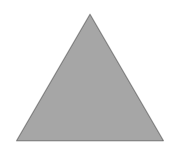

```mathematica
Graphics[{Opacity[.35],EdgeForm[Black],tri}]
```

Translate[gr,vecs] takes a graphics object gr, and translates it according to the vectors vecs. So for example, here are some translation vectors; the ﬁrst vector translates by 1/2 unit to the right, the second vector translates up and to the right.

```mathematica
vecs={{1/2,0},{1/4,(√3)/4}};
```

This translates the triangle using the ﬁrst translation vector.

```mathematica
Translate[tri,{1/2,0}]
```

Translate[Triangle[{{(√3)/2,-1/2},{0,1},{-(√3)/2,-1/2}}],{1/2,0}]

The following translation function creates two objects translated by the vectors vecs.

```mathematica
translation[gr_]:=Translate[gr,vecs]
```

```mathematica
tranTri=NestList[translation,tri,1]
```

{Triangle[{{(√3)/2,-1/2},{0,1},{-(√3)/2,-1/2}}],Translate[Triangle[{{(√3)/2,-1/2},{0,1},{-(√3)/2,-1/2}}],{{1/2,0},{1/4,(√3)/4}}]}

Here are the translated objects along with a red version of the original triangle.

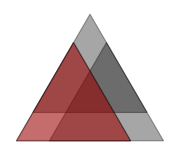

```mathematica
Graphics[{Opacity[.35],EdgeForm[{Black,Thin}],
tranTri,{Red,tri}}]
```

Starting with 1, fold the Times function across the ﬁrst n integers.

```mathematica
fac[n_]:=Fold[Times,1,Range[n]]
```

```mathematica
fac[10]
```

3628800

To compute x^25 say, start by expressing the exponent in base 2.

```mathematica
IntegerDigits[25,2]
```

{1,1,0,0,1}

Now starting with the second bit from the left (use Rest), interpret a one to mean square the existing expression and multiply by x, and a zero to mean multiply the existing expression by x.

```mathematica
Clear[f,a,b,x]
```

```mathematica
f[a_,b_]:=a^2x^b
```

```mathematica
FoldList[f,x,Rest[{1,1,0,0,1}]]
```

{x,x^3,x^6,x^12,x^25}

Once you are familiar with pure functions (Section 5.5), this is done directly – without the need to ﬁrst deﬁne an auxiliary function f – as follows:

```mathematica
FoldList[#1^2 x^#2&,x,Rest[{1,1,0,0,1}]]
```

{x,x^3,x^6,x^12,x^25}

Or you can start with the ﬁrst bit but you will have to adjust the initial value accordingly.

```mathematica
FoldList[#1^2 x^#2&,1,{1,1,0,0,1}]
```

{1,x,x^3,x^6,x^12,x^25}

Here is a larger computation.

```mathematica
exp=4523;
digs=IntegerDigits[exp,2];
FoldList[#1^2 x^#2&,1,digs]
```

{1,x,x^2,x^4,x^8,x^17,x^35,x^70,x^141,x^282,x^565,x^1130,x^2261,x^4523}

First create the vertices of the triangle. Wrapping them in N[…] helps to keep the graphical structures small (see Section 8.3 for more on numeric vs. symbolic expressions in graphics).

```mathematica
vertices=N[{{0,0},{1,0},{1/2,1}}];
```

This gives the three different translation vectors.

```mathematica
translateVecs=0.5vertices
```

{{0.,0.},{0.5,0.},{0.25,0.5}}

Here is the set of transformations of the triangle described by vertices, scaled by 0.5, and translated according to the translation vectors.

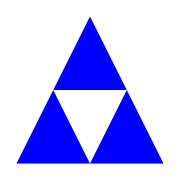

```mathematica
tri=Polygon[vertices];
Graphics[{
Blue,Translate[Scale[tri,0.5,{0.,0.}],translateVecs]
}]
```

Finally, iterate the transformations by wrapping them in Nest.

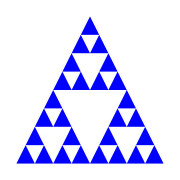

```mathematica
Graphics[{Blue,Nest[{Blue,Translate[Scale[#,0.5,{0.,0.}],translateVecs]}&,Polygon[vertices],3]}]
```

Once you have been through the rest of this chapter, you should be able to turn this into a reusable function, scoping local variables, using pure functions, and adding options.

```mathematica
SierpinskiTriangle[iter_,opts:OptionsPattern[Graphics]]:=Module[{vertices,vecs},
vertices=N[{{0,0},{1,0},{1/2,1}}];
vecs=0.5vertices;
Graphics[{Blue,Nest[{Blue,Translate[Scale[#,0.5,{0.,0.}],vecs]}&,Polygon[vertices],iter]},opts]]
```

```mathematica
SierpinskiTriangle[9]
```

-Graphics-

Exercises: Recursive functions

Create a recursive function that computes the nth power of two.

Create a recursive function that returns the factorial of n, for n a nonnegative integer.

The Tower of Hanoi puzzle is a popular game invented by the French mathematician Édouard Lucas in 1883. Given three pegs, one of which contains n disks of increasing radii, the object is to move the stack of disks to another peg in the fewest number of moves without putting a larger disk on a smaller one (Figure Chapter.NumberedFigure).

Tower of Hanoi.

-Graphics-

Create a recursive function TowerOfHanoi[n] that computes the minimal number of moves for a stack of n disks over three pegs. Results for n=1,2,…,10 are as follows:

{1, 3, 7, 15, 31, 63, 127, 255, 511, 1023}

Legend has it that the priests in the Indian temple Kashi Vishwanath have a room with a stack of 64 disks and three pegs and that when they complete moving the stack to a new peg, the world will end. If they move one disk per second, compute how long until the “end of the world.”

For each of the following sequences of numbers, see if you can deduce the pattern and write a function to compute the general term:

2, | 3, | 6, | 18, | 108, | 1944, | 209952, | …
A_1 | A_2 | A_3 | A_4 | A_5 | A_6 | A_7 | …

0, | 1, | -1, | 2, | -3, | 5, | -8, | 13, | -21, | …
B_1 | B_2 | B_3 | B_4 | B_5 | B_6 | B_7 | B_8 | B_9 | …

0, | 1, | 2, | 3, | 6, | 11, | 20, | 37, | 68, | …
C_1 | C_2 | C_3 | C_4 | C_5 | C_6 | C_7 | C_8 | C_9 | …

The Fibonacci sequence can also be deﬁned for negative integers using the following formula (Graham, Knuth, and Patashnik 1994):

F_-n=(-1)^(n-1)F_n

The ﬁrst few terms are

0 | 1 | -1 | 2 | -3 | 5 | -8 | 13 | -21 | …
F_0 | F_-1 | F_-2 | F_-3 | F_-4 | F_-5 | F_-6 | F_-7 | F_-8 | …

Write the deﬁnitions for Fibonacci numbers with negative integer arguments.

Create a recursive function to reverse the elements in a ﬂat list.

Create a recursive function to transpose the elements of two lists. Write an additional rule to transpose the elements of three lists.

Using dynamic programming is one way to speed up the computation of Fibonacci numbers, but another is to use different algorithms. A more efﬁcient algorithm is based on the following identities:

F_1=1
F_2=1
F_(2n)=2 F_(n-1)F_n+F_n^2,  for   n≥1
F_(2n+1)=F_(n+1)^2+F_n^2,          for    n≥1

Program a function to generate Fibonacci numbers using these identities.

You can still speed up the code for generating Fibonacci numbers in the previous exercise by using dynamic programming. Do so, and construct tables like those in this section, giving the number of additions performed by the two programs.

An Eulerian number, denoted ⟨n
k⟩, gives the number of permutations of n-element sets with k increasing runs of elements. For example, for n=3 the permutations of {1,2,3} contain four increasing runs of length one, namely {1,3,2}, {2,1,3}, {2,3,1}, and {3,1,2}. Hence, ⟨3
1⟩=4.

```mathematica
Permutations[{1,2,3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

This can be programmed using the following recursive deﬁnition, where n and k are assumed to be integers:

⟨n
k⟩=(k+1)⟨n-1
k⟩+(n-k)⟨n-1
k-1⟩, for n>0,

⟨0
k⟩=Piecewise[{{1, k=0}, {0, k≠0.}}]

Create a function EulerianNumber[n,k]. You can check your work against Table Chapter.NumberedTable, which displays the ﬁrst few Eulerian numbers.

Eulerian number triangle

n | ⟨n
0⟩ | ⟨n
1⟩ | ⟨n
2⟩ | ⟨n
3⟩ | ⟨n
4⟩ | ⟨n
5⟩ | ⟨n
6⟩ | ⟨n
7⟩ | ⟨n
8⟩
0 | 1 | "" | "" | "" | "" | "" | "" | "" | ""
1 | 1 | 0 | "" | "" | "" | "" | "" | "" | ""
2 | 1 | 1 | 0 | "" | "" | "" | "" | "" | ""
3 | 1 | 4 | 1 | 0 | "" | "" | "" | "" | ""
4 | 1 | 11 | 11 | 1 | 0 | "" | "" | "" | ""
5 | 1 | 26 | 66 | 26 | 1 | 0 | "" | "" | ""
6 | 1 | 57 | 302 | 302 | 57 | 1 | 0 | "" | ""
7 | 1 | 120 | 1191 | 2416 | 1191 | 120 | 1 | 0 | ""
8 | 1 | 247 | 4293 | 15619 | 15619 | 4293 | 247 | 1 | 0

Because of the triple recursion, you will ﬁnd it necessary to use a dynamic programming implementation to compute any Eulerian numbers of even modest size.

Hint: Although the above formulas will compute it, you can add the following rule to simplify some of the computation (Graham, Knuth, and Patashnik 1994):

⟨n
k⟩=0, for k≥n

The Collatz sequence is generated as follows: starting with a number n, if it is even, then output n/2; if it is odd, then output 3n+1. Iterate this process while the value of the iterate is not equal to one. Using recursion and dynamic programming, create the function collatz[n,i], which computes the ith iterate of the Collatz sequence starting with integer n. Compare its speed with that of the procedural approach in Exercise ExerciseItem of Section Chapter.4.

Solutions

Thinking about the powers of two recursively, we have 2^n=2 2^(n-1). The base case is 2^0=1.

```mathematica
powersOf2[0]=1;
```

```mathematica
powersOf2[n_]:=2 powersOf2[n-1]
```

```mathematica
Table[powersOf2[j],{j,0,10}]
```

{1,2,4,8,16,32,64,128,256,512,1024}

Here are the two rules for the factorial function, deﬁned recursively.

```mathematica
fact[0]=1;
```

```mathematica
fact[n_Integer?NonNegative]:=n fact[n-1]
```

And here are the ﬁrst ten factorials.

```mathematica
Table[fact[j],{j,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

Check that the rule is not called for nonintegers or negative numbers.

```mathematica
fact[3.6]
```

fact[3.6]

```mathematica
fact[-4]
```

fact[-4]

For the base case, it only takes one move to move a disk from one peg to another.

```mathematica
hanoi[1]=1;
```

To move a stack of n disks, move the top n-1 disks, then move the bottom disk, then move the n-1 disks again. Here is the recursion.

```mathematica
hanoi[n_]:=2hanoi[n-1]+1
```

And here are the number of moves for puzzles with one through ten disks.

```mathematica
Table[hanoi[i],{i,10}]
```

{1,3,7,15,31,63,127,255,511,1023}

In fact, there is a closed form formula for this.

```mathematica
Table[2^n-1,{n,10}]
```

{1,3,7,15,31,63,127,255,511,1023}

The key here is to get the stopping conditions right in each case.

This is a straightforward recursion, multiplying the previous two values to get the next.

```mathematica
Clear[a,b,c]
```

```mathematica
a[1]:=2
a[2]:=3
a[i_]:=a[i-1] a[i-2]
```

```mathematica
Table[a[i],{i,1,8}]
```

{2,3,6,18,108,1944,209952,408146688}

The sequence is obtained by taking the difference of the previous two values.

```mathematica
b[1]:=0
b[2]:=1
b[i_]:=b[i-2]-b[i-1]
```

```mathematica
Table[b[i],{i,1,9}]
```

{0,1,-1,2,-3,5,-8,13,-21}

Here we add the previous three values.

```mathematica
c[1]:=0
c[2]:=1
c[3]:=2
c[i_]:=c[i-3]+c[i-2]+c[i-1]
```

```mathematica
Table[c[i],{i,1,9}]
```

{0,1,2,3,6,11,20,37,68}

You can use your earlier deﬁnition of the Fibonacci numbers, or use the built-in Fibonacci.

```mathematica
f[n_Integer?NonPositive]:=(-1)^(n-1)Fibonacci[-n]
```

```mathematica
f[0]=0;
f[-1]=1;
```

```mathematica
Table[f[i],{i,0,-8,-1}]
```

{0,1,-1,2,-3,5,-8,13,-21}

This is similar to the length function in the text – recursion is on the tail. The base case is a list consisting of a single element.

```mathematica
reverse[{x_,y__}]:=Join[reverse[{y}],{x}]
```

```mathematica
reverse[{x_}]:={x}
```

```mathematica
reverse[{1,β,3/4,"practice makes perfect"}]
```

{practice makes perfect,3/4,β,1}

Recursion is on the tails of the two lists, here denoted r1 and r2.

```mathematica
transpose[{{x1_,r1__},{x2_,r2__}}]:=Join[{{x1,x2}},transpose[{{r1},{r2}}]]
```

```mathematica
transpose[{{x_},{y_}}]:={{x,y}}
```

```mathematica
transpose[{{Subscript[x, 1],Subscript[x, 2]},{Subscript[y, 1],Subscript[y, 2]}}]
```

{{x_1,y_1},{x_2,y_2}}

```mathematica
transpose[%]
```

{{x_1,x_2},{y_1,y_2}}

This implementation uses the identities given in the exercise together with some pattern matching for the even and odd cases.

```mathematica
F[1]:=1
F[2]:=1
```

```mathematica
F[n_?EvenQ]:=2 F[n/2-1] F[n/2]+F[n/2]^2
F[n_?OddQ]:=F[(n-1)/2+1]^2+F[(n-1)/2]^2
```

```mathematica
Map[F,Range[10]]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
Timing[F[10^4];]
```

{0.405646,Null}

The use of dynamic programming speeds up the computation by several orders of magnitude.

```mathematica
FF[1]:=1
FF[2]:=1
```

```mathematica
FF[n_?EvenQ]:=FF[n]=2 FF[n/2-1] FF[n/2]+FF[n/2]^2
FF[n_?OddQ]:=FF[n]=FF[(n-1)/2+1]^2+FF[(n-1)/2]^2
```

```mathematica
Map[FF,Range[10]]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
Timing[FF[10^5];]
```

{0.000664,Null}

This is fairly fast, even compared with the built-in Fibonacci which uses a method based on the binary digits of n.

```mathematica
Timing[Fibonacci[10^5];]
```

{0.000171,Null}

Here are the rules translated directly from the formulas given in the exercise.

```mathematica
EulerianNumber[0,k_]=0;
EulerianNumber[n_Integer,0]=1;
EulerianNumber[n_Integer,k_Integer]/;k≥n=0;
```

```mathematica
EulerianNumber[n_Integer,k_Integer]:=(k+1)EulerianNumber[n-1,k]+(n-k)EulerianNumber[n-1,k-1]
```

```mathematica
Table[EulerianNumber[n,k],{n,0,7},{k,0,7}]//TableForm
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 4 | 1 | 0 | 0 | 0 | 0 | 0
1 | 11 | 11 | 1 | 0 | 0 | 0 | 0
1 | 26 | 66 | 26 | 1 | 0 | 0 | 0
1 | 57 | 302 | 302 | 57 | 1 | 0 | 0
1 | 120 | 1191 | 2416 | 1191 | 120 | 1 | 0

Because of the triple recursion, computing larger values is not only time and memory intensive but also bumps up against the built-in recursion limit.

```mathematica
EulerianNumber[25,15]//Timing
```

{16.0102,531714261368950897339996}

This is a good candidate for dynamic programming. In the following implementation we have temporarily reset the value of $RecursionLimit using Block.

```mathematica
Clear[EulerianNumber];
```

```mathematica
EulerianNumber[0,k_]=0;
EulerianNumber[n_Integer,0]=1;
EulerianNumber[n_Integer,k_Integer]/;k≥n=0;
```

```mathematica
EulerianNumber[n_Integer,k_Integer]:=Block[{$RecursionLimit=Infinity},
EulerianNumber[n,k]=(k+1)EulerianNumber[n-1,k]+(n-k)EulerianNumber[n-1,k-1]]
```

```mathematica
EulerianNumber[25,15]//Timing
```

{0.001165,531714261368950897339996}

```mathematica
EulerianNumber[600,65];//Timing
```

{0.296621,Null}

```mathematica
N[EulerianNumber[600,65]]
```

4.99814710204916×10^1091

Recursion is on the tail of the iterator i.

```mathematica
collatz[n_,0]:=n
```

```mathematica
collatz[n_,i_]:=(collatz[n,i]=collatz[n,i-1]/2)/;EvenQ[collatz[n,i-1]]
```

```mathematica
collatz[n_,i_]:=(collatz[n,i]=3collatz[n,i-1]+1)/;OddQ[collatz[n,i-1]]
```

Here is the ﬁfth iterate of the Collatz sequence for 27.

```mathematica
collatz[27,5]
```

31

Here is the Collatz sequence for 27. This sequence takes a while to settle down to the cycle 4, 2, 1.

```mathematica
Table[collatz[27,i],{i,0,114}]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1}

Exercises: Loops and ﬂow control

Create a function UpperTriangularMatrix[n] that generates an n×n matrix with ones on and above the diagonal and zeros below the diagonal. Create an alternative rule that defaults to the value one for the upper values, but allows the user to specify a nondefault upper value.

```mathematica
UpperTriangularMatrix[3]//MatrixForm
```

(0 | 1 | 1
0 | 0 | 1
0 | 0 | 0)

```mathematica
UpperTriangularMatrix[3,ζ]//MatrixForm
```

(0 | ζ | ζ
0 | 0 | ζ
0 | 0 | 0)

Write a function sign[x] which, when applied to an integer x, returns -1, 0, or 1 if x is less than, equal to, or greater than zero, respectively. Write it in four different ways: using three clauses, using a single clause with If, using a single clause with Which, and using Piecewise.

Use If to deﬁne a function that, given a list of numbers, doubles all the positive numbers but leaves the negative numbers unchanged.

The deﬁnition of the absolute value function in this section does not handle complex numbers well:

```mathematica
abs[3+4I]
```

GreaterEqual::nord: Invalid comparison with 3 + 4\ ⅈ attempted.

Less::nord: Invalid comparison with 3 + 4\ ⅈ attempted.

abs[3+4 ⅈ]

Rewrite abs to include a speciﬁc rule for the case where its argument is complex.

One of the fastest methods for computing Fibonacci numbers (Section Chapter.3) involves iterating multiplication of the matrix {{0,1},{1,1}} and pulling off the appropriate part. For example, the last element in the output of mat^9 is the tenth Fibonacci number.

```mathematica
mat={{0,1},{1,1}};
MatrixPower[mat,9]
```

{{21,34},{34,55}}

```mathematica
Fibonacci[10]
```

55

Without using MatrixPower, create a function FibMat[n] that iterates the matrix multiplication and then pulls off the correct element from the resulting matrix to give the nth Fibonacci number. Check the speed of your implementation against both MatrixPower and the built-in Fibonacci.

Using an If control structure, create a function median[lis] that computes the median (the middle value) of a one-dimensional list. You will need to consider the case when the length of the list is odd and the case when it is even. In the latter case, the median is given by the average of the middle two elements of the sorted list.

Given a set of data representing a sine wave, perform a clipping operation where values greater than 0.5 are clipped to 0.5, values less than -0.5 are clipped to -0.5, and all other values are left unchanged (Figure Chapter.NumberedFigure).

```mathematica
data=Table[{x,Sin[x]},{x,0,2π,0.1}];
```

Discrete data of sine wave together with data clipped at amplitude 0.5.

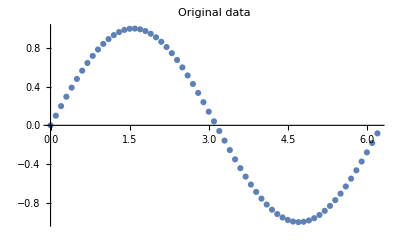
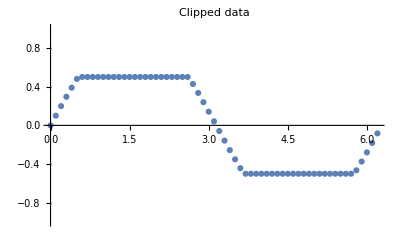
"	"-Graphics--Graphics-

Rewrite the WhatAmI function from this section so that it properly deals with expressions such as π and ⅇ that are numerical but not explicit numbers.

The bibliography example in Section 3.4 is unable to properly handle a key that has a missing value. For example, the following association has no value for both the "Issue" key and the "Pages" key:

```mathematica
art2=Association[{"Author"->"Hathaway, David H.","Title"->"The solar cycle","Journal"->"Living Reviews in Solar Physics","Year"->2010,"Volume"->7,"Issue"->"","Pages"->"","Url"->"http://dx.doi.org/10.12942/lrsp-2010-1"}];
```

```mathematica
art2["Issue"]
```

Suppose you were interested in creating a formatted bibliographic reference that displayed volume 7, issue 4 as 7(4). But if the issue value is missing, it should display the volume value only. Create a function that takes the volume and issue values and displays the correct information regardless of whether or not the issue number is present.

```mathematica
volIss[art2]
```

7

In Exercise ExerciseItem, Section Chapter.3 we introduced Collatz numbers using recursion. Write a procedural implementation, CollatzSequence[n], that produces the Collatz sequence for any positive integer n. Consider using NestWhileList. Here is the Collatz sequence for initial value 22:

```mathematica
CollatzSequence[22]
```

{22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

Write a version of the Manipulate example visualizing interpolation order that used Which to instead use Switch.

Compute the square root of two using Nest (see Section Chapter.2) and compare with the versions in this section using a Do loop.

Do is closely related to Table, the main difference being that Do does not return any value, whereas Table does. Use Table instead of Do to rewrite one of the findRoot functions given in this section. Compare the efﬁciency of the two approaches.

Compute Fibonacci numbers iteratively. The ﬁrst few values in the Fibonacci sequence are 1, 1, 2, 3, 5, 8, 13, …, where, after the ﬁrst two 1s, each number is the sum of the previous two numbers in the sequence. You will need two variables, say this and prev, giving the two most recent Fibonacci numbers, so that after the ith iteration, this and prev have the values F_i and F_(i-1), respectively.

As mentioned in the discussion of Newton’s method for root ﬁnding, one type of difﬁculty that can arise occurs when the derivative of the function in question is either difﬁcult or impossible to compute. As a very simple example, consider the function |x+3|, which has a root at x=-3. Both the built-in function FindRoot and our user-deﬁned findRoot will fail with this function, since a symbolic derivative cannot be computed.

```mathematica
D[Abs[x+3],x]
```

Abs'[3+x]

One way around such problems is to use a numerical derivative (as opposed to an analytic derivative). The secant method approximates f'(x_k) using the difference quotient:

(f(x_k)-f(x_(k-1)))/(x_k-x_(k-1))

Implement a version of findRoot using the secant method by creating a rule that takes two initial values: findRoot[f,{var,a,b}].

Using a While loop, write a function gcd[m,n] that computes the greatest common divisor (gcd) of m and n. The Euclidean algorithm for computing the gcd of two positive integers m and n, sets m=n and n=m mod n. It iterates this process until n=0, at which point the gcd of m and n is left in the value of m.

Write the function gcd[m,n] implementing the Euclidean algorithm using an If function.

A permutation of the elements of a list is a reordering of the elements such that the original list and the reordered list are in one-to-one correspondence. For example, the permutations of the list {a,b,c} are {{a, b, c}, {a, c, b}, {b, a, c}, {b, c, a}, {c, a, b}, {c, b, a}}.

One way to create a permutation of the elements of a list lis is to start by randomly selecting one element from lis and putting it in a temporary list, lis2 say. Then select one element from the complement of lis and lis2 and repeat the process. Using a Do loop, create a function randomPermutation that implements this procedure.

Create a program InversePermutation[p] that takes a list p, that is a permutation of the numbers one through n, and returns the inverse permutation ip. The inverse permutation ip is such that p⟦ip⟦i⟧⟧=ip⟦p⟦i⟧⟧=i. Check you answer against the built-in Ordering function. See Sedgewick and Wayne (2007) for a discussion of inverse permutations.

Create a procedural deﬁnition for each of the following functions. For each function, create a deﬁnition using a Do loop and another using Table.

For example, the following function ﬁrst creates an array consisting of zeros of the same dimension as mat. Then inside the Do loop it assigns the element in position {j,k} in mat to position {k,j} in matA, effectively performing a transpose operation. Finally, it returns matA, since the Do loop itself does not return a value.

```mathematica
transposeDo[mat_]:=Module[{matA,rows=Length[mat],cols=Length[mat[[1]]],j,k},matA=ConstantArray[0,{rows,cols}];
Do[matA⟦j,k⟧=mat⟦k,j⟧,
{j,1,rows},
{k,1,cols}];
matA]
```

```mathematica
mat1={{a,b,c},{d,e,f},{g,h,i}};
MatrixForm[mat1]
```

(a | b | c
d | e | f
g | h | i)

```mathematica
MatrixForm[transposeDo[mat1]]
```

(a | d | g
b | e | h
c | f | i)

This same computation could be performed with a structured iteration using Table.

```mathematica
transposeTable[mat_?MatrixQ]:=Module[{matA,rows,cols},
{rows,cols}=Dimensions[mat];
matA=ConstantArray[0,{rows,cols}];
Table[matA[[j,k]]=mat[[k,j]],{j,rows},{k,cols}]
]
```

```mathematica
transposeTable[mat1]//MatrixForm
```

(a | d | g
b | e | h
c | f | i)

Create the function reverse[vec] that reverses the elements in the list vec.

Create a function rotateRight[lis,n] that rotates the elements in the list lis n places to the right.

The digit sum of a number is given by adding the digits of that number. For example, the digit sum of 7763 is 7+7+6+3=23. If you iterate the digit sum until the resulting number has only one digit, this is called the digit root of the original number. So the digit root of 7763 is 7763→7+7+6+3=23→2+3=5. Create a function to compute the digit root of any positive integer.

Quadrants in the Euclidean plane are traditionally numbered counterclockwise from quadrant i
(x and y positive) to quadrant iv (x positive, y negative) with some convention adopted for points that lie on either of the axes. Use Piecewise to deﬁne a quadrant function that returns the quadrant value for any point in the plane.

Using a Do loop create a function to tally the elements in a list, returning a list of the form {{elem_1,cnt_1},…,{elem_n,cnt_n}}. Check your result against the built-in Tally function.

```mathematica
Tally[{a,c,a,a,c,b,a,a,b,c,a,b}]
```

{{a,6},{c,3},{b,3}}

Solutions

If, for element a_ij, i is bigger than j, then we are below the diagonal and should insert 0, otherwise insert a 1.

```mathematica
UpperTriangularMatrix[{m_,n_}]:=Table[If[i≥j,0,1],{i,m},{j,n}]
```

A default value can be given for an optional argument that speciﬁes the elements above the diagonal.

```mathematica
UpperTriangularMatrix[{m_,n_},val_:1]:=Table[If[i≥j,0,val],{i,m},{j,n}]
```

```mathematica
UpperTriangularMatrix[{5,5},α]//MatrixForm
```

(0 | α | α | α | α
0 | 0 | α | α | α
0 | 0 | 0 | α | α
0 | 0 | 0 | 0 | α
0 | 0 | 0 | 0 | 0)

Here are the conditional deﬁnitions.

```mathematica
sign[x_/;x<0]:=-1
sign[x_/;x>0]:=1
sign[0]=0;
sign[0.0]=0;
```

Actually the last two rules can be combined using alternatives.

```mathematica
sign[0|0.0]=0;
```

```mathematica
Map[sign,{-2,0,1}]
```

{-1,0,1}

Here is the signum function deﬁned using If.

```mathematica
signIf[x_]:=If[x<0,-1,If[x==0,0,1]]
```

```mathematica
Map[signIf,{-2,0,1}]
```

{-1,0,1}

Here is the signum function deﬁned using Which.

```mathematica
signWhich[x_]:=Which[x<0,-1,x>0,1,True,0]
```

```mathematica
Map[signWhich,{-2,0,1}]
```

{-1,0,1}

Finally, here is the signum function deﬁned using Piecewise.

```mathematica
Piecewise[{{-1,x<0},{1,x>0},{0,x==0}}]
```

Piecewise[{{-1, x<0}, {1, x>0}, {0, True}}]

The pure function doubles its argument if it is greater than zero.

```mathematica
doublePos[lis_]:=Map[If[#>0,2 #,#]&,lis]
```

```mathematica
doublePos[{4,0,-3,x}]
```

{8,0,-3,If[x>0,2 x,x]}

The test as the ﬁrst argument of If on the right-hand side checks to see if x is an element of the domain of complex numbers and, if it is, then √((re(x))^2+(im(x))^2) is computed. If x is not complex, nothing is done, but then the other deﬁnitions for abs will be checked.

```mathematica
Clear[abs];
abs[x_]:=Sqrt[Re[x]^2+Im[x]^2]/;x∈Complexes;
abs[x_]:=x/;x≥0
abs[x_]:=-x/;x<0
```

```mathematica
abs[3+4I]
```

5

```mathematica
abs[-3]
```

3

The condition itself can appear on the left-hand side of the function deﬁnition, as part of the pattern match. Here is a slight variation on the abs deﬁnition.

```mathematica
Clear[abs]
abs[x_]:=If[x≥0,x,-x]
abs[x_/;x∈Complexes]:=Sqrt[Re[x]^2+Im[x]^2]
```

```mathematica
abs[3+4I]
```

5

```mathematica
abs[-3]
```

3

The iteration can be done with a Do loop. First, initialize the matrix tempmat to {{0,1},{1,1}}. Then multiply tempmat by the original matrix and reset tempmat to this new value. Repeat n-2 times and then pull off the second element in the second row.

```mathematica
FibMat[n_]:=Module[{tempmat={{0,1},{1,1}}},
Do[tempmat=tempmat.{{0,1},{1,1}},{n-2}];
Part[tempmat,2,2]
]
```

```mathematica
Timing[FibMat[201]]
```

{0.004827,453973694165307953197296969697410619233826}

```mathematica
Timing[Fibonacci[201]]
```

{0.000019,453973694165307953197296969697410619233826}

If the number of elements in the list is odd, then the median is the middle element of the sorted list. Divide the length in two and take the next greater integer using Ceiling to get the position of the middle element.

```mathematica
lis={5,7,2,13,1};
Ceiling[Length[lis]/2]
```

3

We want the element in the third position of the sorted list.

```mathematica
Part[Sort[lis],Ceiling[Length[lis]/2]]
```

5

If the length of the list is even, we take the average of the middle two elements of the sorted list.

```mathematica
lis={65,2,78,5};
```

```mathematica
len=Length[lis];
Part[Sort[lis],len/2;;len/2+1]
```

{5,65}

```mathematica
Mean[%]
```

35

Here then is the function using If to branch when the length of the list is odd or even. The pattern lis:{__} is matched by a list with one or more elements. We name the pattern lis so that we can refer to it on the right-hand side of the deﬁnition.

```mathematica
medianP[lis:{__}]:=Module[{len=Length[lis]},
If[OddQ[len],
Part[Sort[lis],Ceiling[len/2]],
Mean@Part[Sort[lis],len/2;;len/2+1]
]]
```

Here are some test data.

```mathematica
dataO=RandomInteger[10000,100001];
dataE=RandomInteger[10000,100000];
```

This compares our function with the built-in Median function.

```mathematica
medianP[dataO]//Timing
```

{0.014395,4981}

```mathematica
Median[dataO]//Timing
```

{0.01061,4981}

```mathematica
medianP[dataE]//Timing
```

{0.010609,4987}

```mathematica
Median[dataE]//Timing
```

{0.011003,4987}

First, here is the data we will work with.

```mathematica
data=Table[{x,Sin[x]},{x,0,2π,0.1}];
```

There are several approaches we could use. We will use Piecewise for the conditions as stated in the exercise.

```mathematica
clipped=data/.{a_,b_}:>{a,Piecewise[{{0.5,b>0.5},{-0.5,b<-0.5}},b]};
```

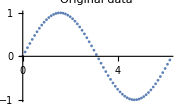
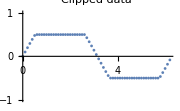

```mathematica
{
ListPlot[data,PlotLabel->"Original data"],
ListPlot[clipped,PlotLabel->"Clipped data",PlotRange->{-1,1}]
}
```

An additional clause is need in the Which expression, one that handles expressions that are numeric but not explicit numbers.

```mathematica
WhatAmI[expr_]:=Switch[expr,
_Integer,"I am an integer",
_Rational,"I am rational",
_Real,"I am real",
_Complex,"I am complex",
_?NumericQ,"I am numeric",
_,"I am not a number"]
```

```mathematica
WhatAmI[π]
```

I am numeric

```mathematica
WhatAmI["a string"]
```

I am not a number

Here is the function to extract and format the volume information. Here we make the volume number format in bold.

```mathematica
getVolume[ref_]:=Style[ref["Volume"],"TR",FontWeight->"Bold"]
```

```mathematica
getIssue[ref_]:=If[ref["Issue"]=="","",
Style[Row[{"(",ref["Issue"],") "}],"TR"]]
```

```mathematica
volIss[ref_]:=Row[{getVolume[ref],getIssue[ref]}]
```

```mathematica
art2=Association[{"Author"->"Hathaway, David H.","Title"->"The solar cycle","Journal"->"Living Reviews in Solar Physics","Year"->2010,"Volume"->7,"Issue"->"","Pages"->"","Url"->"http://dx.doi.org/10.12942/lrsp-2010-1"}];
```

```mathematica
volIss[art2]
```

7

First, deﬁne the auxiliary function using conditional statements.

```mathematica
collatz[n_]:=n/2/;EvenQ[n]
```

```mathematica
collatz[n_]:=3n+1/;OddQ[n]
```

Alternatively, use If.

```mathematica
collatz[n_Integer?Positive]:=If[EvenQ[n],n/2,3n+1]
```

Then iterate Collatz, starting with n, and continue while n is not equal to 1.

```mathematica
CollatzSequence[n_]:=NestWhileList[collatz,n,#≠1&]
```

```mathematica
CollatzSequence[17]
```

{17,52,26,13,40,20,10,5,16,8,4,2,1}

Here is the version of the Manipulate example using Switch instead of Which.

```mathematica
data3D=Table[Sin[x y],{x,0,4,0.5},{y,0,4,0.5}];
```

```mathematica
Manipulate[
ListPlot3D[data3D,InterpolationOrder->order,
PlotLabel->
Switch[order,
"None","Linear",
0,"Voronoi cells",
1,"Baricentric",
2,"Natural neighbor"]],
{{order,"None","Interpolation order"},{"None",0,1,2}},SaveDefinitions->True]
```

To compute the square root of a number r, iterate the following expression.

```mathematica
fun[x_]:=x^2-r;
Simplify[x-fun[x]/fun'[x]]
```

(r+x^2)/(2 x)

This can be written as a pure function, with a second argument giving the initial guess. Here we iterate ten times, starting with a high-precision initial value, 2.0 to 30-digit precision.

```mathematica
nestSqrt[r_,init_]:=Nest[(r+#^2)/(2#)&,init,10]
```

```mathematica
nestSqrt[2,N[2,30]]
```

1.4142135623730950488016887

Here is a ﬁrst basic attempt to replace the Do loop with Table.

```mathematica
f[x_]:=x^2-2
```

```mathematica
a=2;
Table[a=N[a-f[a]/f'[a]],{10}]
```

{1.5,1.41667,1.41422,1.41421,1.41421,1.41421,1.41421,1.41421,1.41421,1.41421}

```mathematica
findRoot[fun_Symbol,{var_,init_},iter_:10]:=Module[{xi=init},
Table[xi=N[xi-fun[xi]/fun'[xi]],{iter}];
{var->xi}]
```

```mathematica
findRoot[f,{x,2}]
```

{x→1.41421}

This runs the iteration only three times.

```mathematica
findRoot[f,{x,2},3]
```

{x→1.41422}

Note that this version of the Fibonacci function is much more efﬁcient than the simple recursive version given in Section 5.3, and is closer to the version there that uses dynamic programming.

```mathematica
Clear[fib]
```

```mathematica
fib[n_]:=Module[{prev=0,this=1,next},
Do[next=prev+this;
prev=this;
this=next,
{n-1}];
this]
```

```mathematica
Table[fib[i],{i,1,10}]
```

{1,1,2,3,5,8,13,21,34,55}

Actually, this code can be simpliﬁed a bit by using parallel assignments.

```mathematica
fib2[n_]:=Module[{f1=0,f2=1},
Do[{f1,f2}={f2,f1+f2},
{n-1}];
f2]
```

```mathematica
Table[fib2[i],{i,1,10}]
```

{1,1,2,3,5,8,13,21,34,55}

Both of these implementations are quite fast and avoid the deep recursion of the classical deﬁnition.

```mathematica
{Timing[fib[100000];],Timing[fib2[100000];]}
```

{{0.188238,Null},{0.132801,Null}}

Here is an implementation of the secant method, essentially modifying our earlier Newton iteration to use a difference quotient to approximate the derivative. Two values are needed to compute the quotient which is reﬂected in the updated argument structure.

```mathematica
findRoot[f_,{var_,a_,b_}]:=Module[{x1=a,x2=b,df},
While[Abs[f[x2]]>1/10^10,
df=(f[x2]-f[x1])/(x2-x1);
{x1,x2}={x2,x2-f[x2]/df}];
{var->x2}]
```

```mathematica
f[x_]:=Abs[x+3]
```

```mathematica
findRoot[f,{x,-3.1,-1.8}]
```

{x→-3.}

This is a direct implementation of the Euclidean algorithm.

```mathematica
gcd[m_,n_]:=Module[{a=m,b=n,tmpa},
While[b>0,
tmpa=a;
a=b;
b=Mod[tmpa,b]];
a]
```

```mathematica
With[{m=12782,n=5531207},
gcd[m,n]]
```

11

You can avoid the need for the temporary variable tmpa by performing a parallel assignment as in the following function. In addition, some argument checking insures that m and n are integers.

```mathematica
gcd[m_Integer,n_Integer]:=Module[{a=m,b=n},
While[b>0,
{a,b}={b,Mod[a,b]}];
a]
```

```mathematica
With[{m=12782,n=5531207},
gcd[m,n]]
```

11

Here is the gcd function implemented using an If structure.

```mathematica
Clear[gcd]
```

```mathematica
gcd[m_Integer,n_Integer]:=If[m>0,gcd[Mod[n,m],m],gcd[m,n]=n]
```

```mathematica
With[{m=12782,n=5531207},
gcd[m,n]]
```

11

To build this function up step-by-step, start with a small list of ten elements.

```mathematica
lis=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

The idea is to choose a position within the list at random and remove the element in that position and put it into a new list lis2.

```mathematica
x=RandomChoice[lis]
```

4

```mathematica
lis2={};
lis2=Append[lis2,x]
```

{4}

We then repeat the above process on the remaining elements of the list. Note that lis is assigned the value of this new list, thus overwriting the previous value.

```mathematica
lis=Complement[lis,{x}]
```

{1,2,3,5,6,7,8,9,10}

```mathematica
x=RandomChoice[lis]
lis2=Append[lis2,x]
lis=Complement[lis,lis2]
```

8

{4,8}

{1,2,3,5,6,7,9,10}

In this example we know explicitly how many iterations to perform in our Do loop: n iterations, where n is the length of the list, lis.

```mathematica
Clear[lis,lis2,x];
```

Now we just put the pieces of the previous computations together in one input.

```mathematica
lis=Range[10];
lis2={};
Do[
x=RandomChoice[lis];
lis2=Append[lis2,x];
lis=Complement[lis,lis2],
{i,1,Length[lis]}]
```

When we are done, the result is left in the new list lis2.

```mathematica
lis2
```

{2,4,7,6,9,1,5,3,8,10}

```mathematica
lis=Range[10];
lis2={};
Do[
x=RandomChoice[lis];
lis2=Append[lis2,x];
lis=Complement[lis,lis2],
{i,1,Length[lis]}]
```

Here then is our function randomPermutation that takes a list as an argument and generates a random permutation of that list’s elements.

```mathematica
randomPermutation[arg_List]:=Module[{lis=arg,x,lis2={}},
Do[
x=RandomChoice[lis];
lis2=Append[lis2,x];
lis=Complement[lis,lis2],
{i,1,Length[arg]}];
lis2]
```

Here is a permutation of the list consisting of the ﬁrst 20 integers.

```mathematica
randomPermutation[Range[20]]
```

{11,17,16,8,2,9,14,5,19,7,1,12,4,10,20,13,6,18,15,3}

And here is a random permutation of the lowercase letters of the English alphabet.

```mathematica
alphabet = CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
randomPermutation[alphabet]
```

{b,j,s,k,q,v,u,n,h,m,e,d,c,p,x,z,f,y,r,o,i,t,a,g,w,l}

This functionality is built into Mathematica via the RandomSample function.

```mathematica
RandomSample[CharacterRange["a","z"]]
```

{w,z,t,y,q,g,f,h,e,k,u,p,r,v,i,n,c,x,l,b,a,o,d,s,j,m}

```mathematica
Clear[x,lis,lis2,alphabet]
```

Start with a random permutation on the ﬁrst ten integers.

```mathematica
Clear[p,i,ip];
```

```mathematica
p=RandomSample[Range[10]]
```

{1,8,3,2,6,10,5,7,9,4}

Initialize the inverse permutation to a list of the same length as p but ﬁlled with zeros to start.

```mathematica
ip=Table[0,{i,Length[p]}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
For[i=1,i≤Length[p],i++,ip[[p[[i]]]]=i];
ip
```

{1,4,3,10,7,5,8,2,9,6}

```mathematica
p[[ip]]==ip[[p]]
```

True

The built-in Ordering function gives essentially the same result.

```mathematica
Ordering[p]
```

{1,4,3,10,7,5,8,2,9,6}

Each solution mirrors that of the transpose example in the exercise.

Create a list vecA of zeros, then use a Do loop to set vecA⟦i⟧ to vec⟦n-i⟧, where n is the length of vec.

```mathematica
Clear[reverse,a,b,c,d,e]
```

```mathematica
reverse[vec_]:=Module[{vecA,n=Length[vec]},
vecA=ConstantArray[0,{n}];
Do[vecA⟦i⟧=vec⟦n-i+1⟧,
{i,1,n}];
vecA]
```

```mathematica
reverse[{a,b,c,d,e}]
```

{e,d,c,b,a}

```mathematica
reverseStruc[vec_]:=Module[{vecA,n=Length[vec]},
vecA=ConstantArray[0,{n}];
Table[vecA[[i]]=vec[[n-i+1]],{i,n}]
]
```

```mathematica
reverseStruc[{a,b,c,d,e}]
```

{e,d,c,b,a}

The key to this problem is to use the Mod operator to compute the target address for any item from vec. That is, the element vec[i] must move to, roughly speaking, position n+i mod Length[vec]. The “roughly speaking” is due to the fact that the Mod operator returns values in the range 0 to Length[vec]-1, whereas vectors are indexed by values 1 up to Length[vec]. This causes a little trickiness in this problem.

```mathematica
rotateRight[vec_,n_]:=Module[{vecA,len=Length[vec]},
vecA=ConstantArray[0,{len}];
Do[vecA⟦1+Mod[n+i-1,len]⟧=vec⟦i⟧,{i,1,len}];
vecA]
```

```mathematica
rotateRight[{a,b,c,d,e},2]
```

{d,e,a,b,c}

```mathematica
rotateRightStruc[vec_,n_]:=Module[{vecA,len=Length[vec]},
vecA=ConstantArray[0,{len}];
Table[vecA⟦1+Mod[n+i-1,len]⟧=vec⟦i⟧,{i,len}];
vecA
]
```

```mathematica
rotateRightStruc[{a,b,c,d,e},3]
```

{c,d,e,a,b}

Given an integer, this totals the list of its digits.

```mathematica
Total[IntegerDigits[7763]]
```

23

This can be accomplished without iteration as follows:

```mathematica
digitRoot[n_Integer?Positive]:=If[Mod[n,9]==0,9,Mod[n,9]]
```

```mathematica
digitRoot[7763]
```

5

Looking ahead to Chapter 6 where localization is discussed, you could also accomplish this with an iteration using a While loop.

```mathematica
digitRoot2[n_Integer?Positive]:=Module[{locn=n,lis},
While[
Length[lis=IntegerDigits@locn]>1,
locn=Total[lis]];
locn]
```

```mathematica
digitRoot2[7763]
```

5

This is a direct implementation using Piecewise.

```mathematica
Piecewise[{{0,x==0&&y==0},{-1,y==0},{-2,x==0},{1,x>0&&y>0},{2,x<0&&y>0},{3,x<0&&y<0}},4]
```

Piecewise[{{0, x==0&&y==0}, {-1, y==0}, {-2, x==0}, {1, x>0&&y>0}, {2, x<0&&y>0}, {3, x<0&&y<0}, {4, True}}]

```mathematica
quadrantPw[{x_,y_}]:=Piecewise[{{0,x==0&&y==0},{-1,y==0},{-2,x==0},{1,x>0&&y>0},{2,x<0&&y>0},{3,x<0&&y<0}},4]
```

```mathematica
Map[quadrantPw,{{0,0},{4,0},{0,1.3},{2,4},{-2,4},{-2,-4},{2,-4},{2,0},{3,-4}}]
```

{0,-1,-2,1,2,3,4,-1,4}

Union[lis] will give a list of the unique elements in lis (this is ulist below). Also, we need a temporary list of the counts initialized to zero (cnts). Then, starting with the ﬁrst element in the input list (i=1), check to see if it equals the ﬁrst element in ulist, then the second, and so on, incrementing by one each time they are equal. When the loops are done, transpose the list of unique elements with the corresponding counts. Here is the function:

```mathematica
Clear[tally]
```

```mathematica
tally[lis_List]:=Module[{ulist=Union[lis],cnts},
cnts=Table[0,{Length[ulist]}];
Do[
Do[If[lis⟦i⟧==ulist⟦j⟧,++cnts⟦j⟧],{j,1,Length[ulist]}],
{i,1,Length[lis]}];
Transpose[{ulist,cnts}]
]
```

```mathematica
lis=RandomChoice[{a,b,c},{20}]
```

{c,c,a,c,a,b,c,a,a,a,a,b,b,b,a,a,a,a,b,b}

```mathematica
tally[lis]
```

{{a,10},{b,6},{c,4}}

Check against the built-in function.

```mathematica
Tally[lis]===tally[lis]
```

False

Here is another implementation. Here we are creating rules for each unique element (counter[#]) and then incrementing the values for those rules each time the counter comes across an element.

```mathematica
tally2[lis_]:=Module[{ulist=Union[lis],counter},
counter[_]=0;
Map[counter[#]++&,lis] ;
Map[{#,counter[#]}&,ulist]
]
```

```mathematica
tally2[lis]
```

{{a,10},{b,6},{c,4}}

Check the speed of these two functions.

```mathematica
data=RandomInteger[{0,9},{50000}];
```

```mathematica
Timing[tally[data]]
```

{0.975904,{{0,5078},{1,5041},{2,4928},{3,4973},{4,4969},{5,5037},{6,4875},{7,5040},{8,5014},{9,5045}}}

```mathematica
Timing[tally2[data]]
```

{0.180405,{{0,5078},{1,5041},{2,4928},{3,4973},{4,4969},{5,5037},{6,4875},{7,5040},{8,5014},{9,5045}}}

```mathematica
Timing[Tally[data]]
```

{0.000122,{{2,4928},{8,5014},{5,5037},{4,4969},{3,4973},{9,5045},{6,4875},{7,5040},{0,5078},{1,5041}}}

Exercises: Pure functions

Using pure functions, compute sin(x)/x for each x in the list {0,π/6,π/4,π/3,π/2}. Check your answer against the built-in Sinc function.

Create a pure function to select all integers between one and one thousand that are square numbers; that is, numbers that are some integer squared.

In Exercise ExerciseItem, Section Chapter.Section you were asked to create a function to compute the diameter of a set of points in n-dimensional space. Modify that solution by instead using the Norm function and pure functions to ﬁnd the diameter.

Rewrite the code from Section Chapter.Section for ﬁnding the next prime after a given integer so that it uses pure functions instead of relying upon the auxiliary deﬁnition addOne and the built-in function CompositeQ.

Create a function RepUnit[n] that generates integers of length n consisting entirely of ones. For example, RepUnit[7] should produce 1111111.

Rewrite the example from Section Chapter.Section in which NestList was used to perform several rotations of a triangle to instead use pure functions and dispense with the auxiliary function rotation used to specify the rotation angles.

Given a set of numerical data, extract all those data points that are within one standard deviation of the mean of the data.

```mathematica
data=RandomVariate[NormalDistribution[0,1],{2500}];
```

Using the built-in Fold function, write a function fromDigits[lis,b] that accepts a list of digits in any base b (less than 20) and converts it to a base 10 number. For example, 1101_2 is 13 in base 10, so your function should handle this as follows:

```mathematica
fromDigits[{1,1,0,1},2]
```

13

Check your solution against the built-in FromDigits function.

Write a pure function that moves a random walker from one location on a square lattice to one of the four adjoining locations with equal probability (a two-dimensional lattice walk). For example, starting at {0,0}, the function should return {0,1}, {0,-1}, {1,0}, or {-1,0} with equal likelihood. Use this pure function with NestList to generate the list of step locations for an n-step random walk starting at the origin.

Modify the findRoot function from this section to allow for equations of the form x^2==2 or Cos[x]==0 as the ﬁrst argument.

Create a function findRootList that is based on findRoot and returns all the intermediate values that are computed by the Newton iteration.

A naive approach to polynomial arithmetic would require three additions and six multiplications to carry out the arithmetic in the expression a x^3+b x^2+c x+d. Using Horner’s method for fast polynomial multiplication, this expression can be represented as d+x(c+x(b+a x)), where there are now half as many multiplications. You can see this using the MultiplyCount function developed in Exercise 7 of Section 4.2.

```mathematica
MultiplyCount[a x^3+ b x^2+c x+d]
```

6

```mathematica
MultiplyCount[d+x (c+x (b+a x))]
```

3

In general, the number of multiplications in an n-degree polynomial in traditional form is given by:

```mathematica
Binomial[n+1,2]
```

1/2 n (1+n)

This, of course, grows quadratically with n, whereas Horner’s method grows linearly. Create a function HornerPolynomial[lis,var] that gives a representation of a polynomial in Horner form. Here is some sample output that your function should generate:

```mathematica
HornerPolynomial[{a,b,c,d},x]
```

d+x (c+x (b+a x))

```mathematica
Expand[%]
```

d+c x+b x^2+a x^3

Find all words in the dictionary that start with the letter q and are of length ﬁve. The following gets all the words in the dictionary that comes with Mathematica and displays a random sample:

```mathematica
words=DictionaryLookup[];
RandomSample[words,18]
```

{dare,condole,forums,attributive,impassible,minefields,skittish,thereabout,jugful,fishiest,canter,choral,Nanjing,toupee,solemner,Marlboro,Whigs,healthier}

Given a list of angles between zero and 2π, map them to points of the form {x,y} on the unit circle.

```mathematica
angles=RandomReal[{0,2π},{8}]
```

{5.8948,2.50319,1.93239,5.65609,0.571937,5.32786,4.96526,5.49373}

Once created, display the points graphically using code similar to the following:

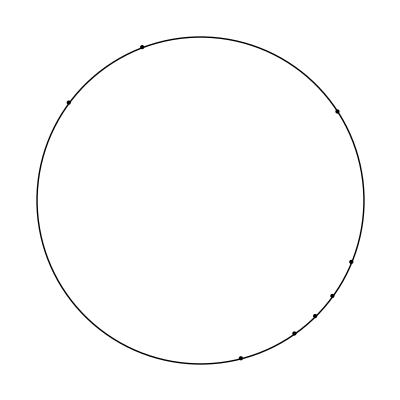

```mathematica
Graphics[{Circle[],Point[pts]}]
```

Finally, create a set of lines from the origin to each of the points on the circle and display using code similar to the following:

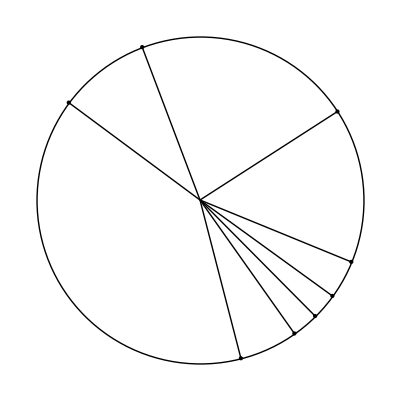

```mathematica
Graphics[{Circle[],Point[pts],Line[lines]}]
```

Use FoldList to compute an exponential moving average of a list {x_1,x_2,x_3}. You can check your result against the built-in ExponentialMovingAverage.

```mathematica
ExponentialMovingAverage[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},α]
```

{x_1,-(-1+α) x_1+α x_2,-(-1+α) (-(-1+α) x_1+α x_2)+α x_3}

A well-known programming exercise in many languages is to generate Hamming numbers, sometimes referred to as regular numbers. These are numbers that divide powers of 60 (the choice of that number goes back to the Babylonians, who used 60 as a number base). Generate a sorted sequence of all Hamming numbers less than 1000. The key observation is that these numbers have only 2, 3, and 5 as prime factors.

In the text, we developed FunctionsWithAttributes to ﬁnd all built-in functions with a particular attribute. Create a new function to ﬁnd all built-in functions with a given option. For example:

```mathematica
FunctionsWithOption[StepMonitor]
```

{FindArgMax,FindArgMin,FindFit,FindMaximum,FindMaxValue,FindMinimum,FindMinValue,FindRoot,NArgMax,NArgMin,NDSolve,NDSolveValue,NMaximize,NMaxValue,NMinimize,NMinValue,NonlinearModelFit,NRoots,ParametricNDSolve,ParametricNDSolveValue}

Several changes from FunctionsWithAttributes will be necessary: Options does not take a string as an argument; and options are often given as nested lists of rules, requiring mapping at the appropriate level. You might also want to delete all functions beginning with $, such as $Context, to help speed the computation.

Graphs that are not too dense are often represented using adjacency structures which consist of a list for each vertex v_i that includes those other vertices that v_i is connected to. Create an adjacency structure for any graph, directed or undirected. For example, consider the graph gr below.

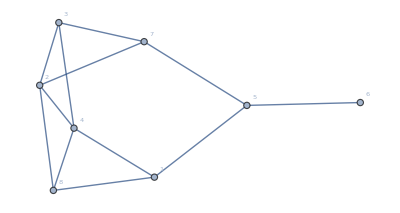

```mathematica
gr=RandomGraph[{8,12},VertexLabels->"Name"]
```

Start by creating an adjacency list for any given vertex; that is, a list of those vertices to which the given vertex is connected. The adjacency list for vertex 4 in the above graph would be {1,8,2,3}.

The adjacency structure is then the list of adjacency lists for every vertex in that graph. It is common to prepend each adjacency list with its vertex; typically the adjacency structure takes the following form where this syntax indicates that vertex 1 is connected to vertices 4, 5, and 8; vertex 2 is connected to vertices 3, 4, 7, and 8; and so on.

{{1,{4,5,8}},{2,{3,4,7,8}},{3,{2,4,7}},{4,{1,2,3,8}},{5,{1,6,7}},{6,{5}},{7,{2,3,5}},{8,{1,2,4}}}

One common use of graphs is to analyze the relationships of the objects under study. For example, if you were interested in ﬁnding all objects a certain distance from a given object, you could use NeighborhoodGraph.

Here is a grid graph on which we can start prototyping:

```mathematica
gr=GridGraph[{7,7},VertexLabels->"Name"];
```

NeighborhoodGraph gives all those vertices up to distance two from vertex 25.

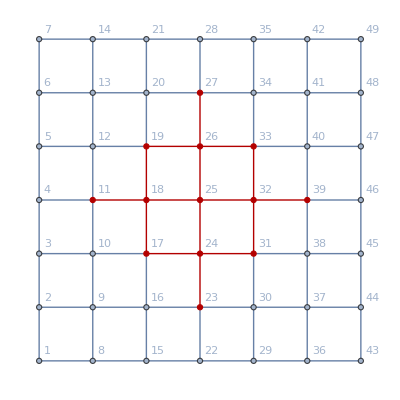

```mathematica
HighlightGraph[gr,NeighborhoodGraph[gr,25,2]]
```

But suppose you were interested in all those vertices precisely distance two from vertex 25. Implement this using two different approaches: one in which you use NeighborhoodGraph and another using a two-argument form of VertexList in which the second argument is a pattern.

Create a “composition” using the digits of π to represent notes on the C scale, where a digit n is interpreted as a note n semitones from middle C. For example, the ﬁrst few digits 1, 4, 1, 5 would give the notes one, four, one, and ﬁve semitones from middle C.

You can generate tones using Sound and SoundNote. For example, this emits a tone ﬁve semitones above middle C of duration one second:

```mathematica
Sound[SoundNote[5,1]]//EmitSound
```

And this emits the same tone but using a midi instrument instead of the default:

```mathematica
Sound[SoundNote[5,1,"Vibraphone"]]//EmitSound
```

A matrix is nilpotent if it is a square matrix all of whose eigenvalues are zero. Alternatively, a square matrix A is nilpotent if A^n is the zero matrix for some positive integer n. Create a predicate NilpotentMatrixQ[mat] that returns True if mat is nilpotent. Check your function by verifying that any directed acyclic graph (DAG) has a nilpotent adjacency matrix. A list of acyclic graphs is available via GraphData["Acyclic"]. See McKay et al. (2004) for information about acyclic graphs and the eigenvalues of their adjacency matrices.

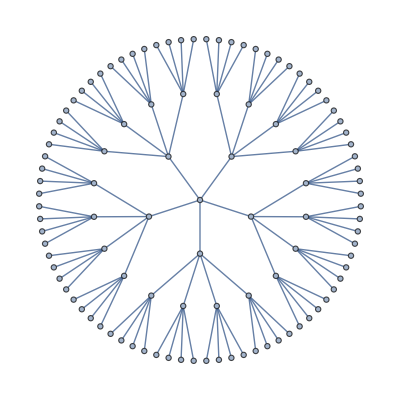

```mathematica
gr=GraphData[{"CayleyTree",{5,3}}]
```

```mathematica
AcyclicGraphQ[gr]
```

True

Solutions

The pure function is Sin[#]/#&.

```mathematica
Map[Sin[#]/#&,{0,π/6,π/4,π/3,π/2}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{Indeterminate,3/π,(2 √2)/π,(3 √3)/(2 π),2/π}

Since Sinc is listable, it automatically maps across lists.

```mathematica
Sinc[{0,π/6,π/4,π/3,π/2}]
```

{1,3/π,(2 √2)/π,(3 √3)/(2 π),2/π}

Use a piecewise function to properly deal with the point at zero.

```mathematica
Map[Piecewise[{{1,#==0},{Sin[#]/#,#≠0}}]&,{0,π/6,π/4,π/3,π/2}]
```

{1,3/π,(2 √2)/π,(3 √3)/(2 π),2/π}

One test for a number to be a square number is that its square root is an integer.

```mathematica
Select[Range[1000],IntegerQ[√#]&]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961}

To compute the distance between two points, use either EuclideanDistance or Norm.

```mathematica
pts=RandomReal[1,{4,2}]
```

{{0.578624,0.852785},{0.917576,0.509619},{0.187069,0.755342},{0.879409,0.277697}}

```mathematica
Norm[pts[[1]]-pts[[2]]]
```

0.482339

```mathematica
EuclideanDistance[pts[[1]],pts[[2]]]
```

0.482339

Now we need the distance between every pair of points. So we ﬁrst create the set of pairs.

```mathematica
pairs=Subsets[pts,{2}]
```

{{{0.578624,0.852785},{0.917576,0.509619}},{{0.578624,0.852785},{0.187069,0.755342}},{{0.578624,0.852785},{0.879409,0.277697}},{{0.917576,0.509619},{0.187069,0.755342}},{{0.917576,0.509619},{0.879409,0.277697}},{{0.187069,0.755342},{0.879409,0.277697}}}

Then we compute the distance between each pair and take the Max.

```mathematica
Apply[Norm[#1-#2]&,pairs,{1}]
```

{0.482339,0.403498,0.648998,0.770727,0.235042,0.841118}

```mathematica
Max[%]
```

0.841118

Or, use Outer on the set of points directly, but note the need to get the level correct.

```mathematica
Max@Outer[Norm[#1-#2]&,pts,pts,1]
```

0.841118

Now put it all together using a pure function in place of the distance function. The diameter function operates on lists of pairs of numbers, so we need to specify them in our pure function as #1 and #2.

```mathematica
diameter[lis_]:=Max[Apply[Norm[#1-#2]&,Subsets[lis,{2}],{1}]]
```

```mathematica
diameter[pts]
```

0.841118

EuclideanDistance is a bit faster here, but for large data sets, the difference is more pronounced.

```mathematica
pts=RandomReal[1,{1500,2}];
diameter[pts]//Timing
```

{3.29299,1.40019}

```mathematica
Max[Apply[EuclideanDistance,Subsets[pts,{2}],{1}]]//Timing
```

{1.1718,1.40019}

Pure functions are needed to replace both addOne and CompositeQ:

```mathematica
nextPrime[n_Integer/;n>1]:=NestWhile[#+1&,n,Not[PrimeQ[#]]&]
```

Here is a quick check for correctness.

```mathematica
nextPrime[2^123]==NextPrime[2^123]
```

True

Compare timing with the built-in function.

```mathematica
Timing[nextPrime[2^2500];]
```

{0.217708,Null}

```mathematica
Timing[NextPrime[2^2500];]
```

{0.207308,Null}

This function is ideally written as an iteration.

```mathematica
RepUnit[n_]:=Nest[(10 #+1)&,1,n-1]
```

```mathematica
RepUnit[7]
```

1111111

```mathematica
Map[RepUnit[#]&,Range[12]]
```

{1,11,111,1111,11111,111111,1111111,11111111,111111111,1111111111,11111111111,111111111111}

This can also be done in a functional style by ﬁrst creating a list of the appropriate number of ones using ConstantArray, then converting that to an integer with FromDigits.

```mathematica
RepUnit[n_]:=FromDigits[ConstantArray[1,{n}]]
```

```mathematica
RepUnit[11]
```

11111111111

First, here is the triangle.

```mathematica
vertices={{0,0},{1,0},{1/2,√3/2}};
```

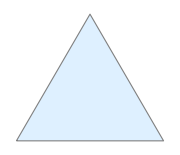

```mathematica
tri=Triangle[vertices];
Graphics[{LightBlue,EdgeForm[Gray],tri}]
```

Here is the rotation function as deﬁned in Section 5.2:

```mathematica
rotation[gr_]:=Rotate[gr,π/13,RegionCentroid[tri]]
```

To turn that into a pure function, replace the argument gr with the slot into which each successive triangle will go.

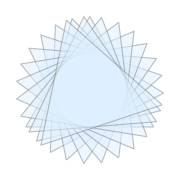

```mathematica
Graphics[{
LightBlue,Opacity[.5],EdgeForm[Gray],
NestList[Rotate[#,π/13,RegionCentroid[tri]]&,tri,10]
}]
```

Here are some sample data taken from a normal distribution.

```mathematica
data=RandomVariate[NormalDistribution[0,1],{500}];
```

Quickly visualize the data together with dashed lines drawn one standard deviation from the mean.

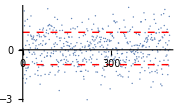

```mathematica
μ=Mean[data];
σ=StandardDeviation[data];
len=Length[data];
ListPlot[data,
Epilog->{Dashed,Red,
Line[{{0,μ+σ},{len,μ+σ}}],
Line[{{0,μ-σ},{len,μ-σ}}]}
]
```

Select those data elements whose distance to the mean is less than one standard deviation.

```mathematica
filtered=Select[data,(Abs[(#-μ)]<σ&)];
```

Here is a quick check that we get about the value we might expect (we would expect about 68% for normally distributed data).

```mathematica
N[Length[filtered]/Length[data]]
```

0.68

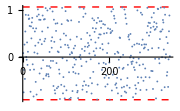

```mathematica
ListPlot[filtered,PlotRange->All,
Epilog->{Dashed,Red,
Line[{{0,μ+σ},{len,μ+σ}}],
Line[{{0,μ-σ},{len,μ-σ}}]}
]
```

This function uses a default value of 2 for the base. (Try replacing Fold with FoldList to see more clearly what this function is doing.)

```mathematica
convert[digits_List,base_:2]:=Fold[(base #1+#2)&,0,digits]
```

Here are the digits for 9 in base 2:

```mathematica
IntegerDigits[9,2]
```

{1,0,0,1}

This converts them back to the base 10 representation.

```mathematica
convert[%]
```

9

Note, this functionality is built into the function FromDigits[lis,base].

```mathematica
FromDigits[{1,0,0,1},2]
```

9

This function is essentially an implementation of Horner’s method for fast polynomial multiplication.

```mathematica
convert[{a,b,c,d,e},x]
```

e+x (d+x (c+x (b+a x)))

```mathematica
Expand[%]
```

e+d x+c x^2+b x^3+a x^4

Using the list of step increments in the north, south, east, and west directions, this ten-step walk starts at the origin.

```mathematica
SeedRandom[0];
NSEW={{1,0},{-1,0},{0,1},{0,-1}};
NestList[#1+RandomChoice[NSEW]&,{0,0},10]
```

{{0,0},{0,1},{0,2},{-1,2},{-1,1},{0,1},{1,1},{1,2},{2,2},{3,2},{3,3}}

Except for the initial value, you can get the same result with Accumulate which generates cumulative sums.

```mathematica
SeedRandom[0];
Accumulate[RandomChoice[NSEW,10]]
```

{{0,1},{0,2},{-1,2},{-1,1},{0,1},{1,1},{1,2},{2,2},{3,2},{3,3}}

The key here is to take any expression of the form lhs==rhs and extract the appropriate function whose root you will compute using the previous implementations of findRoot. Looking at the internal form of an equation, some thought should convince you that lhs-rhs is the expression whose root we want.

```mathematica
expr=x^2==2;
FullForm[expr]
```

Equal[Power[x,2],2]

And here is the pure function that we will use with NestWhile.

```mathematica
var=x;
expr/.Equal[a_,b_]:>Function[Evaluate@var,a-b]
```

Function[x,x^2-2]

```mathematica
Clear[findRoot];
findRoot[expr_Equal,{var_,init_},ϵ_:0.0001]:=Module[{result,fun},
fun=expr/.Equal[a_,b_]:>Function[Evaluate@var,a-b];
result=NestWhile[#-fun[#]/fun'[#]&,init,Abs[fun[#]]>ϵ&];
{var->result}]
```

```mathematica
findRoot[x^2==2,{x,1.0}]
```

{x→1.41422}

```mathematica
findRoot[Cos[x]==0,{x,N[1,20]},10^-18]
```

{x→1.57079632679489662}

Perhaps the easiest way to see the intermediate values is to simply use NestWhileList.

```mathematica
findRootList[expr_,{var_,init_},ϵ_:10^-15]:=Module[{fun=Function[Evaluate[var],expr]},
NestWhileList[#-fun[#]/fun'[#]&,N[init],Abs[fun[#]]>ϵ&]]
```

```mathematica
findRoot[expr_Equal,{var_,init_},ϵ_:0.0001]:=Module[{fun},
fun=expr/.Equal[a_,b_]:>Function[Evaluate@var,a-b];
NestWhileList[#-fun[#]/fun'[#]&,N[init],Abs[fun[#]]>ϵ&]]
```

```mathematica
findRootList[x^2-2,{x,1.0}]
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421}

```mathematica
findRootList[Cos[x],{x,1.0}]
```

{1.,1.64209,1.57068,1.5708,1.5708}

Alternatively, you could use Reap and Sow. Be careful where you place the closing bracket for Sow.

```mathematica
Clear[findRootList];
findRootList[expr_,{var_,init_},ϵ_:0.0001]:=Module[{result,fun=Function[Evaluate[var],expr]},
Reap@NestWhile[Sow[#-fun[#]/fun'[#]]&,N[init],Abs[fun[#]]>ϵ&]]
```

```mathematica
findRootList[Cos[x],{x,.5},10^-15]
```

{1.5708,{{2.33049,1.38062,1.57312,1.5708,1.5708}}}

Using Fold, this pure function requires two arguments. The key is to start with an initial value of zero.

```mathematica
HornerPolynomial[list_List,var_]:=Fold[var #1+#2&,0,list]
```

```mathematica
HornerPolynomial[{a,b,c,d,e},x]
```

e+x (d+x (c+x (b+a x)))

```mathematica
Expand[%]
```

e+d x+c x^2+b x^3+a x^4

Here are the words from the built-in Mathematica dictionary.

```mathematica
words=DictionaryLookup[];
```

Here are those words that start with the letter q.

```mathematica
DictionaryLookup["q"~~__];
RandomSample[%,20]
```

{quadruples,quaffs,quark,quarantining,quahogs,quaff,quickie,quadrupled,quires,quit,quell,quints,quizzes,quadriplegia,quotation,quacking,quilter,queered,quintuple,quarterfinals}

And here are those words that start with the letter q and are of length ﬁve. Note the need for StringLength, not Length.

```mathematica
Select[DictionaryLookup["q"~~__],StringLength[#]==5&]
```

{quack,quads,quaff,quail,quake,quaky,qualm,quark,quart,quash,quasi,quays,queen,queer,quell,quern,query,quest,queue,quick,quids,quiet,quiff,quill,quilt,quins,quint,quips,quire,quirk,quirt,quite,quits,quoin,quoit,quota,quote,quoth}

First, create a set of angles between zero and 2π.

```mathematica
angles=RandomReal[{0,2π},6];
```

To turn these angles into points on the unit circle, note that the cosine of the angle gives the x-coordinate, and sine of the angle gives the y-coordinate. So the following creates a list of the form {Cos[θ],Sin[θ]} for each angle θ.

```mathematica
pts=Map[{Cos[#],Sin[#]}&,angles]
```

{{0.760612,0.649207},{-0.505615,-0.862759},{-0.915506,0.402304},{-0.813205,-0.581977},{0.5826,-0.812759},{-0.959663,-0.281152}}

Here is the graphic.

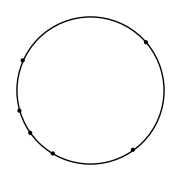

```mathematica
Graphics[{Circle[],Point[pts]}]
```

Line takes a list of two points. One of those points will be the origin for each of our coordinate pairs. Here is the code to create the pairs of points that will be passed to Line.

```mathematica
lines=Map[{#,{0,0}}&,pts]
```

{{{0.760612,0.649207},{0,0}},{{-0.505615,-0.862759},{0,0}},{{-0.915506,0.402304},{0,0}},{{-0.813205,-0.581977},{0,0}},{{0.5826,-0.812759},{0,0}},{{-0.959663,-0.281152},{0,0}}}

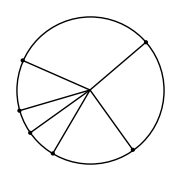

```mathematica
Graphics[{Circle[],Point[pts],Line[lines]}]
```

This can also be done more directly with AngleVectors which takes a polar angle as argument and returns a point on the unit circle with that polar angle.

```mathematica
pts=Map[AngleVector,angles]
```

{{0.760612,0.649207},{-0.505615,-0.862759},{-0.915506,0.402304},{-0.813205,-0.581977},{0.5826,-0.812759},{-0.959663,-0.281152}}

```mathematica
Graphics[{
Circle[],
Point[pts],
Map[Line[{{0,0},#}]&,pts]
}]
```

-Graphics-

The key to solving this problem is thinking carefully about the initial value for FoldList.

```mathematica
FoldList[#1+α(#2-#1)&,Subscript[x, 1],{Subscript[x, 2],Subscript[x, 3]}]
```

{x_1,x_1+α (-x_1+x_2),x_1+α (-x_1+x_2)+α (-x_1-α (-x_1+x_2)+x_3)}

If you were deﬁning your own function, you would need to extract the ﬁrst element of the (data) list as the initial value of FoldList.

```mathematica
expMovingAverage[lis_,α_]:=FoldList[#1+α(#2-#1)&,First[lis],Rest[lis]]
```

```mathematica
expMovingAverage[{a,b,c},α]
```

{a,a+(-a+b) α,a+(-a+b) α+α (-a+c-(-a+b) α)}

```mathematica
ExponentialMovingAverage[{a,b,c},α]
```

{a,-a (-1+α)+b α,c α-(-1+α) (-a (-1+α)+b α)}

```mathematica
Simplify[%%==%]
```

True

A ﬁrst, naive implementation will use the fact that the prime factors are all less than 6. Here are the factors for a single integer.

```mathematica
facs=FactorInteger[126]
```

{{2,1},{3,2},{7,1}}

This extracts only the prime factors.

```mathematica
Map[First,facs]
```

{2,3,7}

In this case, they are not all less than 6.

```mathematica
Max[%]<6
```

False

Putting these pieces together, here are the Hamming numbers less than 1000.

```mathematica
Select[Range[1000],Max[Map[First,FactorInteger[#]]]<6&]
```

{1,2,3,4,5,6,8,9,10,12,15,16,18,20,24,25,27,30,32,36,40,45,48,50,54,60,64,72,75,80,81,90,96,100,108,120,125,128,135,144,150,160,162,180,192,200,216,225,240,243,250,256,270,288,300,320,324,360,375,384,400,405,432,450,480,486,500,512,540,576,600,625,640,648,675,720,729,750,768,800,810,864,900,960,972,1000}

Factoring is slow for large integers and so this implementation does not scale well. This ﬁnds the 507 Hamming numbers less than 10^6.

```mathematica
With[{n=10^6},
Select[Range[n],Max[Map[First,FactorInteger[#]]]<6&]
];//Timing
```

{5.24049,Null}

See Dijkstra (1981) for a different implementation that starts with h={1}, then builds lists 2h, 3h, 5h, merges these lists, and iterates.

```mathematica
HammingNumberList[n_]:=Module[{lim},
lim=If[n<100,Ceiling[Log2[n]],Ceiling[Log2[n/(2 3 5)] Log2[n]]];Join[{1},Take[Union@@NestList[Union@@Outer[Times,{2,3,5},#]&,{2,3,5},lim],n-1]
]]
```

```mathematica
HammingNumber[n_]:=Part[HammingNumberList[n],n]
```

```mathematica
HammingNumberList[20]
```

{1,2,3,4,5,6,8,9,10,12,15,16,18,20,24,25,27,30,32,36}

```mathematica
HammingNumber[1691]//Timing
```

{0.0806,2125764000}

This gives the one-millionth Hamming number.

```mathematica
HammingNumber[10^6]//Timing
```

{14.1544,519312780448388736089589843750000000000000000000000000000000000000000000000000000000}

First, note that Options, unlike Attributes, does not take a string as an argument.

```mathematica
Options["Integrate"]
```

{}

To work around this, convert strings to symbols.

```mathematica
Options[Symbol["Integrate"]]
```

{Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

The second issue is that options are given as a list of rules which is a more deeply nested expression structure than the list of attributes.

```mathematica
MemberQ[Options[Integrate],Assumptions]
```

False

The tree structure shows that the option names occur down at level two.

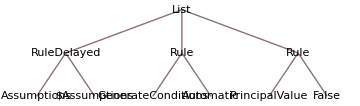

```mathematica
TreeForm[Options[Integrate]]
```

The optional third argument to MemberQ can be used to specify the level at which the pattern match should take place. In this case, at level two.

```mathematica
MemberQ[Options[Integrate],Assumptions,2]
```

True

Next, note that many built-in symbols have no options, as indicated by the empty list returned.

```mathematica
Options[Round]
```

{}

Rather than search through these functions, let’s remove them from the search as well as any function that starts with “$” such as $RecursionLimit.

Here then is the function:

```mathematica
FunctionsWithOption[opt_Symbol]:=Module[{names,lis},
names=Complement[Names["System`*"],Names["System`$*"]];
lis=DeleteCases[names,f_/;Options[Symbol[f]]==={}];
Select[lis,MemberQ[Options[Symbol[#]],opt,2]&]]
```

```mathematica
FunctionsWithOption[Compiled]//Timing
```

{17.3194,{FindArgMax,FindArgMin,FindFit,FindMaximum,FindMaxValue,FindMinimum,FindMinValue,FindRoot,LiftingFilterData,NDSolve,NDSolveValue,NExpectation,NIntegrate,NProbability,NProduct,NSum,ParametricNDSolve,ParametricNDSolveValue,Play}}

With a little analysis you should see that we reduced the large list of functions to search from over 5000 to a little more than 1200 (check the length of lis). The function would be quite a bit slower otherwise.

```mathematica
Length[Names["System`*"]]
```

5491

First, create a prototype graph to work with.

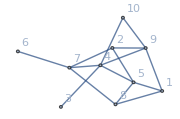

```mathematica
SeedRandom[16];
gr=RandomGraph[{10,15},VertexLabels->"Name"]
```

And here are its edges and its vertices:

```mathematica
EdgeList[gr]
```

{1<->5,1<->8,1<->9,2<->5,2<->7,2<->9,3<->4,4<->5,4<->7,4<->9,4<->10,5<->8,6<->7,7<->8,9<->10}

```mathematica
VertexList[gr]
```

{1,2,3,4,5,6,7,8,9,10}

Below are those edges from vertex 3 to any other vertex. In other words, this gives the adjacency list for vertex 3.

```mathematica
With[{u=3},
Select[VertexList[gr],(EdgeQ[gr,UndirectedEdge[u,#]]&)]
]
```

{4}

The case for directed graphs is similar. Here then is a function that returns the adjacency list for a given vertex u in graph gr.

```mathematica
adjacencyList[gr_,u_]:=If[DirectedGraphQ[gr],Select[VertexList[gr],EdgeQ[gr,DirectedEdge[u,#]]&],Select[VertexList[gr],EdgeQ[gr,UndirectedEdge[u,#]]&]
]
```

The adjacency structure is then given by mapping the above function across the vertex list.

```mathematica
AdjacencyStructure[gr_Graph]:=Map[{#,adjacencyList[gr,#]}&,VertexList[gr]]
```

A built-in function can also be used to get the adjacency lists.

```mathematica
Map[{#,AdjacencyList[gr,#]}&,VertexList[gr]]
```

{{1,{5,8,9}},{2,{5,7,9}},{3,{4}},{4,{3,5,7,9,10}},{5,{1,2,4,8}},{6,{7}},{7,{2,4,6,8}},{8,{1,5,7}},{9,{1,2,4,10}},{10,{4,9}}}

```mathematica
AdjacencyStructure[gr_Graph]:=Map[{#,AdjacencyList[gr,#]}&,VertexList[gr]]
```

```mathematica
AdjacencyStructure[gr]
```

{{1,{5,8,9}},{2,{5,7,9}},{3,{4}},{4,{3,5,7,9,10}},{5,{1,2,4,8}},{6,{7}},{7,{2,4,6,8}},{8,{1,5,7}},{9,{1,2,4,10}},{10,{4,9}}}

Check that it works for a directed graph also.

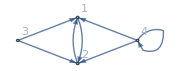

```mathematica
gr2=Graph[{1->2,2->1,3->1,3->2,4->1,4->2,4->4},VertexLabels->"Name"]
```

```mathematica
AdjacencyStructure[gr2]
```

{{1,{2,3,4}},{2,{1,3,4}},{3,{1,2}},{4,{1,2}}}

To start, here is a 7×7 grid graph.

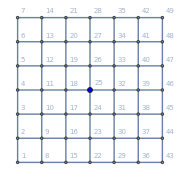

```mathematica
gr=GridGraph[{7,7},VertexLabels->"Name",VertexStyle->{25->Blue},VertexSize->{25->Medium}]
```

A somewhat brute force way to solve this problem is to ﬁnd all vertices within distance three of vertex 25 and subtract out the vertices within distance two of vertex 25.

```mathematica
Complement[VertexList@NeighborhoodGraph[gr,25,3],VertexList@NeighborhoodGraph[gr,25,2]]
```

{4,10,12,16,20,22,28,30,34,38,40,46}

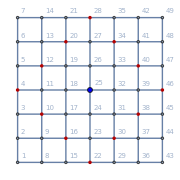

```mathematica
HighlightGraph[gr,%]
```

Alternatively, create a function VertexNeighbors that takes a graph gr, a vertex v, and a distance dist, and, using GraphDistance, ﬁnds all those vertices in gr that are distance dist from v.

```mathematica
VertexNeighbors[gr_,v_,dist_]:=VertexList[gr,_?(GraphDistance[gr,v,#]==dist&)]
```

```mathematica
HighlightGraph[gr,VertexNeighbors[gr,25,3]]
```

-Graphics-

First generate 100 digits for a 100-note “composition”.

```mathematica
digs=First[RealDigits[N[π,50]]];
```

Fix note duration at 0.5 seconds.

```mathematica
Sound[SoundNote[#,0.5]&/@digs]//EmitSound
```

Change the duration to be dependent upon the digit. Also change the midi instrument.

```mathematica
Sound[SoundNote[#,1/(#+1),"Vibraphone"]&/@digs]//EmitSound
```

Go a bit further, expanding the range of notes that will be played.

```mathematica
Sound[SoundNote[1+2#,1/(#+1),"Vibraphone"]&/@digs]//EmitSound
```

As a test graph, we create a directed graph and check that it is acyclic.

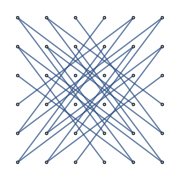

```mathematica
gr=GraphData[{"Antelope",{6,6}}]
```

This converts the undirected graph gr to a directed graph.

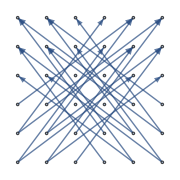

```mathematica
dirgr=DirectedGraph[gr,"Acyclic"]
```

Check that it is indeed acyclic.

```mathematica
AcyclicGraphQ[dirgr]
```

True

Here is its adjacency matrix.

```mathematica
mat=AdjacencyMatrix[dirgr];
```

This gives the eigenvalues of mat.

```mathematica
Eigenvalues[mat]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Here then is a function that checks if the eigenvalues of a matrix are all zero. Note the use of logical or (||) to check for both exact and approximate zero.

```mathematica
NilpotentMatrixQ[mat_?SquareMatrixQ]:=AllTrue[Eigenvalues[mat],(#==0||#==0.0)&]
```

```mathematica
NilpotentMatrixQ[mat]
```

True

Exercises: Examples

Write a version of the function that computes Hamming distance by using Count with an appropriate pattern to ﬁnd the number of nonidentical pairs of corresponding numbers in two binary signals.

Write an implementation of Hamming distance using the Total function and modular arithmetic base 2 to compare two bits. Compare running times with the other versions discussed in this chapter.

Rewrite the median function from Exercise ExerciseItem, Section Chapter.Section so that instead of using an If control structure, you create two separate rules: one rule for the case when the list has an odd number of elements and another rule for the case when the length of the list is even.

Extend the survivor function developed in this section to a function of two arguments, so that survivor[n,m] returns the survivor starting from a list of n people and executing every mth person.

In Section 4.3 we created a function CountChange[lis] that took a list of coins and, using transformation rules, returned the monetary value of that list of coins. Rewrite CountChange to use a purely functional approach. Consider using Dot, or Inner, or Tally.

Create a function Regular2Graph[n] that outputs an n-sided regular graph where every vertex has degree two.

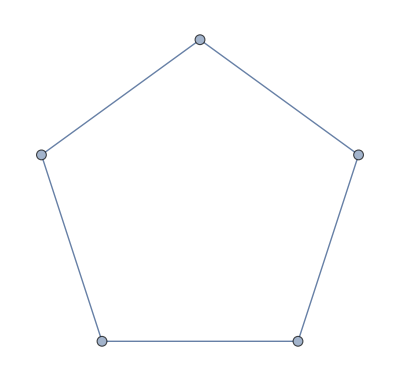

```mathematica
Regular2Graph[5]
```

Extend the visualization of PPI networks from this section by coloring vertices according to the biological process in which they are involved. The built-in ProteinData contains this information, for example:

```mathematica
ProteinData["KLKB1","BiologicalProcesses"]
```

{BloodCoagulation,Fibrinolysis,InflammatoryResponse,Proteolysis}

Extend the range of ReplaceElement developed in this section to accept a list of strings considered as nonnumeric matrix entries, each of which should be replaced by a column mean.

Imagine a random walk on a graph: starting at vertex v_i, the probability that you next move to vertex v_j is given by

P(v_i, v_j) ={1/d_v_i,if v_i<->v_j
0, otherwise

where d_v_i is the degree of vertex v_i. This deﬁnes what is known as a transition probability matrix and can be used to create a Markov model to simulate random walks on graphs.

Given a graph, create its transition probability matrix where matrix element a_ij=P(v_i,v_j) as deﬁned above. You will need the built-in functions VertexCount and VertexDegree as well as EdgeQ. For more on random walks on graphs, see Lovász (1993) or Aldous and Fill (2014).

Random graphs have a rich and deep history in spite of the fact that they were only ﬁrst deﬁned in the mid-twentieth century in a paper by Erdős and  Rényi (1959). They have since been used to study areas as diverse as percolation, telecommunications, social networks, and many more.

Perhaps the simplest random graph model is one in which both the number of vertices and the number of edges are ﬁxed. In this model, G(n,m), the m edges are placed at random among all (n
2) possible edges. This is the model that the built-in function RandomGraph is based upon. In an alternate model, commonly referred to as G(n,p), the probability of an edge between any two of the n vertices is ﬁxed. As as result, the number of edges can vary from none, for example when p=0, to (n
2) when p=1. In this exercise you are asked to create a simpliﬁed model of the G(n,p) random graph.

Starting with a set of edges, assign a probability to each. The edges can be taken from a complete graph, a graph in which there is an edge between every pair of vertices.

```mathematica
n=7;
cg=CompleteGraph[n];
EdgeRules[cg]
```

{1→2,1→3,1→4,1→5,1→6,1→7,2→3,2→4,2→5,2→6,2→7,3→4,3→5,3→6,3→7,4→5,4→6,4→7,5→6,5→7,6→7}

Next choose an edge with probability p. An edge being chosen is a binary choice: either it is chosen or it isn’t. This is essentially a coin toss distribution which, in Mathematica, is represented by BernoulliDistribution. We create a list of probabilities the same length as the number of edges in the complete graph.

```mathematica
p=0.45;
probs=RandomVariate[BernoulliDistribution[p],EdgeCount[cg]]
```

{1,0,0,0,1,0,0,1,0,1,0,1,1,1,1,0,1,0,0,0,1}

Finally, use Pick to include only edges whose corresponding probability is less than the threshold value p and display the resulting graph with Graph.

Extend the grid example from Exercise 5, Section 3.1 to color the prime grid elements (Figure Chapter.NumberedFigure).

Grid of integers 1 through n^2 with prime elements highlighted.

1 | 2 | 3 | 4 | 5 | 6 | 7
8 | 9 | 10 | 11 | 12 | 13 | 14
15 | 16 | 17 | 18 | 19 | 20 | 21
22 | 23 | 24 | 25 | 26 | 27 | 28
29 | 30 | 31 | 32 | 33 | 34 | 35
36 | 37 | 38 | 39 | 40 | 41 | 42
43 | 44 | 45 | 46 | 47 | 48 | 49

Using Grid, create a truth table for a logical expression such as (A∨B)⇒C (Figure Chapter.NumberedFigure).

Truth table for A∨B⇒C.

A | B | C | A∨B⇒C
"T" | "T" | "T" | "T"
"T" | "T" | "F" | "F"
"T" | "F" | "T" | "T"
"T" | "F" | "F" | "F"
"F" | "T" | "T" | "T"
"F" | "T" | "F" | "F"
"F" | "F" | "T" | "T"
"F" | "F" | "F" | "T"

Create a function RandomNote[n] that plays a random sequence of n notes taken from the twelve-tone scale. The twelve tones in C major can be generated using Sound and SoundNote to create the sound objects; use EmitSound to play them through the speakers of your computer.

```mathematica
Sound[Map[SoundNote,Range[0,11]]]//EmitSound
```

A second argument to SoundNote can be used to alter the duration of each note, which, by default, is for one second. Set up RandomNote to have random durations as well as random notes. Finally, set up RandomNote to accept a second argument to set the midi instrument through which the sound will be played.

Because of the completely random nature of how the notes are chosen in the previous exercise, the resulting “tunes” will have no autocorrelation and the result is quite uninteresting. Create a new function to generate sequences of notes where the randomness is applied to the distance between notes, essentially performing a “random walk” through the C major scale. Music generated in such a way is called Brownian because it behaves much like the movement of particles suspended in liquid – Brownian motion.

If you read musical notation, take a musical composition such as one of Bach’s Brandenburg Concertos and write down a list of the frequency intervals x between successive notes. Then ﬁnd a function that interpolates the power spectrum of these frequency intervals and determine if this function is of the form f(x)=c/x for some constant c. (Hint: To get the power spectrum, you will need to square the magnitude of the Fourier transform: take Abs[Fourier[…]]^2 of your data.) Compute the power spectra of different types of music using this procedure.

Modify the clustering example in this section so that the cluster disks enclose every point in their respective clusters (Figure Chapter.NumberedFigure).

Clustering with each disk enclosing entire cluster.

Given a set of n points in the plane, ﬁnd a tour that visits each of them once, returning to the ﬁrst point visited: choose a point v_1 from the set at random; then ﬁnd the point that is closest to v_1, call it v_2; of the points not chosen so far, ﬁnd the point that is closest to v_2; call it v_3. In this way create a running list {v_1,v_2,…,v_n,v_1} that gives the points to visit in order, returning to the ﬁrst point visited. This is essentially a nearest-neighbor algorithm for solving the traveling salesman problem. It is known that this solution is sub-optimal but it will give you a good feeling for these kinds of problems. See Section 8.4 for some variations on traveling salesman-type problems.

Starting with a set of n random points in the unit square, ﬁnd the proportion that are also in the square’s inscribed disk (Figure Chapter.NumberedFigure). As n increases, this proportion (slowly!) approaches the value π/4.

Monte Carlo simulation to approximate π.

In Exercise 5, Section 9.2 this computation is run numerous times as a Monte Carlo simulation to get better and better approximations to the value of π.

Solutions

Here are two small sample lists.

```mathematica
l1={1,0,0,1,1};
l2={0,1,0,1,0};
```

First, pair them.

```mathematica
ll=Transpose[{l1,l2}]
```

{{1,0},{0,1},{0,0},{1,1},{1,0}}

Here is the conditional pattern that matches any pair where the two elements are not identical. The Hamming distance is the number of such nonidentical pairs.

```mathematica
Count[ll,{p_,q_}/;p≠q]
```

3

Finally, here is a function that puts this all together.

```mathematica
HammingDistance3[lis1_List,lis2_List]:=
Count[Transpose[{lis1,lis2}],{p_,q_}/;p≠q]
```

```mathematica
HammingDistance3[l1,l2]
```

3

The running times of this version of HammingDistance are quite a bit slower than those where we used bit operators. This is due to additional computation (Transpose) and the use of pattern matching and comparisons at every step.

```mathematica
HammingDistance2[lis1_,lis2_]:=Total[BitXor[lis1,lis2]]
```

```mathematica
data1=RandomInteger[1,{10^6}];
```

```mathematica
data2=RandomInteger[1,{10^6}];
```

```mathematica
Timing[HammingDistance2[data1,data2]]
```

{0.020373,501050}

```mathematica
Timing[HammingDistance3[data1,data2]]
```

{0.798615,501050}

Using Total on the binary sum, Hamming distance can be computed as follows:

```mathematica
HammingDistance4[lis1_,lis2_]:=Total[Mod[lis1+lis2,2]]
```

Timing tests show that the implementation with Total is quite a bit more efﬁcient than the previous versions, although still slower than the version that uses bit operators.

```mathematica
sig1=RandomInteger[1,{10^6}];
```

```mathematica
sig2=RandomInteger[1,{10^6}];
```

```mathematica
HammingDistance1[lis1_,lis2_]:=
Count[MapThread[SameQ,{lis1,lis2}],False]
```

```mathematica
Map[{#,Timing[#[sig1,sig2]]}&,{HammingDistance1,HammingDistance2,HammingDistance3,HammingDistance4}]//Grid
```

HammingDistance1 | {0.352712,499983}
HammingDistance2 | {0.011396,499983}
HammingDistance3 | {0.796302,499983}
HammingDistance4 | {0.038783,499983}

The median of a list containing an odd number of elements is the middle element of the sorted list.

```mathematica
median[lis_List/;OddQ[Length[lis]]]:=Part[Sort[lis],Ceiling[Length[lis]/2]]
```

When the list has an even number of elements, take the mean of the middle two.

```mathematica
median[lis_List/;EvenQ[Length[lis]]]:=Module[{len=Length[lis]/2},
Mean[Part[Sort[lis],len;;len+1]]
]
```

Check the two cases – an even number of elements, and an odd number of elements. Then compare with the built-in Median.

```mathematica
dataE=RandomInteger[10000,100000];
```

```mathematica
dataO=RandomInteger[10000,100001];
```

```mathematica
median[dataE]//Timing
```

{0.010258,4990}

```mathematica
Median[dataE]//Timing
```

{0.013946,4990}

```mathematica
median[dataO]//Timing
```

{0.011299,5009}

```mathematica
Median[dataO]//Timing
```

{0.01085,5009}

The two rules given here should be more careful about the input, using pattern matching to insure that these rules only apply to one-dimensional lists. The following modiﬁcations handle that more robustly.

```mathematica
Clear[median]
```

```mathematica
median[lis:{__}/;OddQ[Length[lis]]]:=Part[Sort[lis],Ceiling[Length[lis]/2]]
```

```mathematica
median[lis:{__}/;EvenQ[Length[lis]]]:=Module[{len=Length[lis]/2},
Mean[Part[Sort[lis],len;;len+1]]]
```

Just one change is needed here: add a second argument to RotateLeft that speciﬁes the number of positions to rotate. We have used NestList to display the intermediate steps.

```mathematica
survivor[n_,m_]:=NestList[Rest[RotateLeft[#,m-1]]&,Range[n],n-1]
```

```mathematica
survivor[11,3]
```

{{1,2,3,4,5,6,7,8,9,10,11},{4,5,6,7,8,9,10,11,1,2},{7,8,9,10,11,1,2,4,5},{10,11,1,2,4,5,7,8},{2,4,5,7,8,10,11},{7,8,10,11,2,4},{11,2,4,7,8},{7,8,11,2},{2,7,8},{2,7},{7}}

Here is a list of coins (modify for other currencies).

```mathematica
coins={p,p,q,n,d,d,p,q,q,p};
```

First count the occurrences of each.

```mathematica
Map[Count[coins,#]&,{p,n,d,q}]
```

{4,1,2,3}

Then a dot product of this count vector with a value vector does the trick.

```mathematica
%.{.01,.05,.10,.25}
```

1.04

```mathematica
CountChange[lis_]:=
Dot[Map[Count[lis,#]&,{p,n,d,q}],{.01,.05,.10,.25}]
```

```mathematica
CountChange[coins]
```

{16+2 d+3 q,44+2 d+3 q,24+2 d+3 q,20+2 d+3 q,36+2 d+3 q,52+2 d+3 q,32+2 d+3 q,40+2 d+3 q,48+2 d+3 q,28+2 d+3 q}

```mathematica
CountChange2[lis_]:=
Inner[Times,Map[Count[lis,#]&,{p,n,d,q}],{.01,.05,.10,.25},Plus]
```

```mathematica
CountChange2[coins]
```

1.04

And here is a rule-based approach.

```mathematica
Tally[coins]/.{d->.10,n->.05,p->.01,q->.25}
```

{{0.01,4},{0.25,3},{0.05,1},{0.1,2}}

```mathematica
Total[Apply[Times,%,{1}]]
```

1.04

```mathematica
CountChange3[lis_]:=Module[{freq},
freq=Tally[lis]/.{p->.01,n->.05,d->.10,q->.25};
Total[Apply[Times,freq,{1}]]]
```

```mathematica
CountChange3[coins]
```

1.04

If you think of the vertex indices as one through n, then each vertex needs to be connected to the vertex with index one less and also one more.

Create the pairs using Partition with overlap one and set to cycle from the last to the ﬁrst element.

```mathematica
Partition[Range[5],2,1,1]
```

{{1,2},{2,3},{3,4},{4,5},{5,1}}

Then apply UndirectedEdge to these pairs at level one.

```mathematica
Apply[UndirectedEdge,Partition[Range[5],2,1,1],{1}]
```

{1<->2,2<->3,3<->4,4<->5,5<->1}

This bundles up the code, using the shorthand notation for Apply at level one, @@@.

```mathematica
Regular2Graph[n_]:=Graph[UndirectedEdge@@@Partition[Range[n],2,1,1]]
```

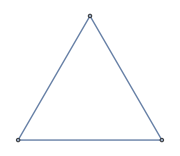
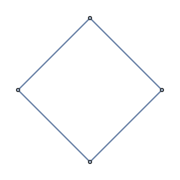
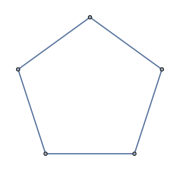
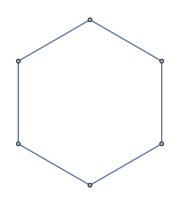

```mathematica
Table[Regular2Graph[n],{n,3,6,1}]
```

(* solution to appear *)

Column 4 of this matrix contains several different nonnumeric values.

```mathematica
mat3={{0.796495,"N/A",0.070125,"nan",0.806554},
{"nn",-0.100365,0.992736,-0.320560,-0.0805351},
{0.473571,0.460741,0.030060,-0.412400,0.788522},{0.614974,-0.503201,0.615744,0.966053,-0.011776},{-0.828415,0.035514,0.8911617,"N/A",-0.453926}};
MatrixForm[col4=mat3[[All,4]]]
```

(nan
-0.32056
-0.4124
0.966053
N/A)

To pattern match on either "N/A" or "nan", use Alternatives (|).

```mathematica
col4/."N/A"|"nan"->Mean[Cases[mat3[[All,4]],_?NumberQ]]//MatrixForm
```

(0.0776977
-0.32056
-0.4124
0.966053
0.0776977)

Convert the list of strings to a set of alternatives.

```mathematica
Apply[Alternatives,{"N/A","nan","nn"}]
```

N/A|nan|nn

Here is a third set of deﬁnitions, including a new rule for ReplaceElement where the second argument is a list of strings. And another rule for ReplaceElement accommodates the new argument structure of colMean.

```mathematica
colMean[col_,{strings___String}]:=col/.Apply[Alternatives,{strings}]->Mean[Cases[col,_?NumberQ]]
```

```mathematica
ReplaceElement[mat_,{strings__}]:=
Transpose[Map[colMean[#,{strings}]&,Transpose[mat]]]
```

```mathematica
ReplaceElement[mat3,{"N/A","nan","nn"}]//MatrixForm
```

(0.796495 | -0.0268277 | 0.070125 | 0.0776977 | 0.806554
0.264156 | -0.100365 | 0.992736 | -0.32056 | -0.0805351
0.473571 | 0.460741 | 0.03006 | -0.4124 | 0.788522
0.614974 | -0.503201 | 0.615744 | 0.966053 | -0.011776
-0.828415 | 0.035514 | 0.891162 | 0.0776977 | -0.453926)

Let’s start with a random graph.

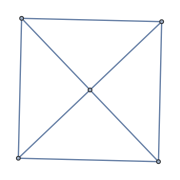

```mathematica
gr=RandomGraph[{5,8}]
```

Let us create a list of all possible edges in gr.

```mathematica
With[{n=VertexCount[gr]},
Array[UndirectedEdge,{n,n}]]
```

{{1<->1,1<->2,1<->3,1<->4,1<->5},{2<->1,2<->2,2<->3,2<->4,2<->5},{3<->1,3<->2,3<->3,3<->4,3<->5},{4<->1,4<->2,4<->3,4<->4,4<->5},{5<->1,5<->2,5<->3,5<->4,5<->5}}

The transition probability matrix assigns the value 1/VertexDegree in position {i,j} if there is an edge between vertex i and vertex j and zero otherwise. Here is the pure function that does this.

```mathematica
If[EdgeQ[gr,#],1/VertexDegree[gr,First@#],0]&;
```

This needs to be mapped at level two to account for the nested lists in the array.

```mathematica
With[{n=VertexCount[gr]},
Map[EdgeQ[gr,#]&,Array[UndirectedEdge,{n,n}],{2}]]
```

{{False,True,True,False,True},{True,False,False,True,True},{True,False,False,True,True},{False,True,True,False,True},{True,True,True,True,False}}

Finally, here then is the transition matrix.

```mathematica
With[{n=VertexCount[gr]},
Map[If[EdgeQ[gr,#],1/VertexDegree[gr,First@#],0]&,Array[UndirectedEdge,{n,n}],{2}]]
```

{{0,1/3,1/3,0,1/3},{1/3,0,0,1/3,1/3},{1/3,0,0,1/3,1/3},{0,1/3,1/3,0,1/3},{1/4,1/4,1/4,1/4,0}}

```mathematica
TransitionMatrix[gr_Graph]:=With[{n=VertexCount[gr]},
Map[If[EdgeQ[gr,#],1/VertexDegree[gr,First@#],0]&,Array[UndirectedEdge,{n,n}],{2}]
]
```

```mathematica
𝒯=TransitionMatrix[gr]
```

{{0,1/3,1/3,0,1/3},{1/3,0,0,1/3,1/3},{1/3,0,0,1/3,1/3},{0,1/3,1/3,0,1/3},{1/4,1/4,1/4,1/4,0}}

To see how to use 𝒯 to create a random walk using Markov processes, ﬁrst create some starting probabilities for each vertex.

```mathematica
Π=ConstantArray[1/VertexCount[gr],{VertexCount[gr]}]
```

{1/5,1/5,1/5,1/5,1/5}

Here is the Markov process using the initial probabilities and the transition matrix.

```mathematica
𝒫=DiscreteMarkovProcess[Π,𝒯];
```

Create ten steps in the process.

```mathematica
data=RandomFunction[𝒫,{0,10}]
```

TemporalData[…]

These are the vertices that were visited on the walk.

```mathematica
data["Values"]
```

{1,2,4,5,1,2,5,1,5,2,4}

Turn the successive vertices into edges and highlight them with the original graph.

```mathematica
walk=UndirectedEdge@@@Partition[data["Values"],2,1]
```

{1<->2,2<->4,4<->5,5<->1,1<->2,2<->5,5<->1,1<->5,5<->2,2<->4}

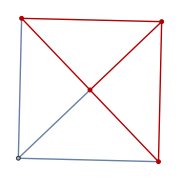

```mathematica
HighlightGraph[gr,Graph[walk]]
```

Starting with a set of edges, we assign a probability to each. The edges are taken from a complete graph, a graph in which there is an edge between every pair of vertices. Then, using Pick, we include only edges whose corresponding probability is less than some threshold value, p.

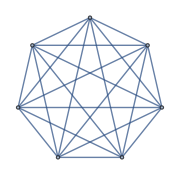

```mathematica
n=7;
cg=CompleteGraph[n]
```

Here are the edges.

```mathematica
EdgeRules[cg]
```

{1→2,1→3,1→4,1→5,1→6,1→7,2→3,2→4,2→5,2→6,2→7,3→4,3→5,3→6,3→7,4→5,4→6,4→7,5→6,5→7,6→7}

We want to choose an edge with probability p. An edge being chosen is a binary choice: either it is chosen or it isn’t. This is essentially a coin toss distribution which, in Mathematica is represented by BernoulliDistribution.

```mathematica
p=0.45;
probs=RandomVariate[BernoulliDistribution[p],EdgeCount[cg]]
```

{0,1,1,1,1,0,1,0,0,1,0,0,1,1,0,0,1,1,0,0,0}

We will use a three-argument form of Pick to choose the edges that meet our criteria. Pick[lis,sel,patt] returns those elements in lis for which the corresponding element of sel matches the pattern patt. In our case, we choose edges if the corresponding Bernoulli distribution returns a value of one.

```mathematica
includedEdges=Pick[EdgeRules[cg],probs,1]
```

{1→3,1→4,1→5,1→6,2→3,2→6,3→5,3→6,4→6,4→7}

Finally, turn this list of included (undirected) edges into a graph.

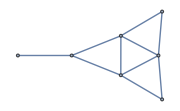

```mathematica
Graph[includedEdges,DirectedEdges->False]
```

Gather all these pieces and scale up the size of the graph.

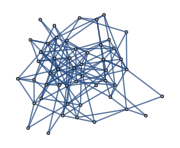

```mathematica
n=50;p=.12;
cg=CompleteGraph[n];probs=RandomVariate[BernoulliDistribution[p],EdgeCount[cg]];
gr=Graph[Pick[EdgeRules[cg],probs,1],DirectedEdges->False]
```

A quick check that 50 vertices are returned and that the ratio of edges to possible edges is approximately equal to the probability we speciﬁed.

```mathematica
{VertexCount[gr],N@GraphDensity[gr]}
```

{50,0.114286}

Several exercises in Chapter 6 ask you to bundle up the code here and turn it into a reusable function inheriting options from Graph.

As an aside, the above functionality is built into BernoulliGraphDistribution[n,pr] which constructs an n-vertex graph, starting with an edge connecting every pair of vertices and then selects edges independently via a Bernoulli trial with probability pr.

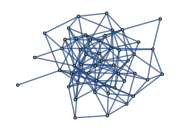

```mathematica
RandomGraph[BernoulliGraphDistribution[50,0.12]]
```

First construct the grid for the n^2 elements, partitioning on n.

```mathematica
n=7;
lis=Partition[Range[n^2],n];
Grid[lis,Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7
8 | 9 | 10 | 11 | 12 | 13 | 14
15 | 16 | 17 | 18 | 19 | 20 | 21
22 | 23 | 24 | 25 | 26 | 27 | 28
29 | 30 | 31 | 32 | 33 | 34 | 35
36 | 37 | 38 | 39 | 40 | 41 | 42
43 | 44 | 45 | 46 | 47 | 48 | 49

Extract the positions of the prime elements.

```mathematica
Position[lis,p_/;PrimeQ[p]]
```

{{1,2},{1,3},{1,5},{1,7},{2,4},{2,6},{3,3},{3,5},{4,2},{5,1},{5,3},{6,2},{6,6},{7,1},{7,5}}

```mathematica
Position[lis,p_?PrimeQ]
```

{{1,2},{1,3},{1,5},{1,7},{2,4},{2,6},{3,3},{3,5},{4,2},{5,1},{5,3},{6,2},{6,6},{7,1},{7,5}}

Map a rule of the form position→Pink across the positions of the prime numbers.

```mathematica
Map[(#->Pink)&,Position[lis,p_?PrimeQ]]
```

{{1,2}→RGBColor[1, 0.5, 0.5],{1,3}→RGBColor[1, 0.5, 0.5],{1,5}→RGBColor[1, 0.5, 0.5],{1,7}→RGBColor[1, 0.5, 0.5],{2,4}→RGBColor[1, 0.5, 0.5],{2,6}→RGBColor[1, 0.5, 0.5],{3,3}→RGBColor[1, 0.5, 0.5],{3,5}→RGBColor[1, 0.5, 0.5],{4,2}→RGBColor[1, 0.5, 0.5],{5,1}→RGBColor[1, 0.5, 0.5],{5,3}→RGBColor[1, 0.5, 0.5],{6,2}→RGBColor[1, 0.5, 0.5],{6,6}→RGBColor[1, 0.5, 0.5],{7,1}→RGBColor[1, 0.5, 0.5],{7,5}→RGBColor[1, 0.5, 0.5]}

Use the rules with the Background option to Grid.

```mathematica
n=7;
lis=Partition[Range[n^2],n];
Grid[lis,
Frame->All,Background->Join[{None,None},{Map[(#->Pink)&,Position[lis,p_?PrimeQ]]}
]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7
8 | 9 | 10 | 11 | 12 | 13 | 14
15 | 16 | 17 | 18 | 19 | 20 | 21
22 | 23 | 24 | 25 | 26 | 27 | 28
29 | 30 | 31 | 32 | 33 | 34 | 35
36 | 37 | 38 | 39 | 40 | 41 | 42
43 | 44 | 45 | 46 | 47 | 48 | 49

```mathematica
Clear[n,lis]
```

Start with a prototype logical expression.

```mathematica
Clear[A,B]
```

```mathematica
expr=(A||B)⇒C;
```

```mathematica
vars={A,B,C};
```

List all the possible truth value assignments for the variables.

```mathematica
tuples=Tuples[{True,False},Length[vars]]
```

{{True,True,True},{True,True,False},{True,False,True},{True,False,False},{False,True,True},{False,True,False},{False,False,True},{False,False,False}}

Next, create a list of rules, associating each of the triples of truth values with a triple of variables.

```mathematica
rules=Map[Thread[vars->#]&,tuples]
```

{{A→True,B→True,C→True},{A→True,B→True,C→False},{A→True,B→False,C→True},{A→True,B→False,C→False},{A→False,B→True,C→True},{A→False,B→True,C→False},{A→False,B→False,C→True},{A→False,B→False,C→False}}

Replace the logical expression with each set of rules.

```mathematica
expr/.rules
```

{True,False,True,False,True,False,True,True}

Put these last values at the end of each “row” of the tuples.

```mathematica
table=Transpose@Join[Transpose[tuples],{expr/.rules}]
```

{{True,True,True,True},{True,True,False,False},{True,False,True,True},{True,False,False,False},{False,True,True,True},{False,True,False,False},{False,False,True,True},{False,False,False,True}}

Create a header for table.

```mathematica
head=Append[vars,TraditionalForm[expr]]
```

{A,B,C,A∨B⇒C}

Prepend head to table.

```mathematica
Prepend[table,head]
```

{{A,B,C,A∨B⇒C},{True,True,True,True},{True,True,False,False},{True,False,True,True},{True,False,False,False},{False,True,True,True},{False,True,False,False},{False,False,True,True},{False,False,False,True}}

Pour into a grid.

```mathematica
Grid[Prepend[table,head]]
```

A | B | C | A∨B⇒C
True | True | True | True
True | True | False | False
True | False | True | True
True | False | False | False
False | True | True | True
False | True | False | False
False | False | True | True
False | False | False | True

Replace True with "T" and False with "F".

```mathematica
Grid[Prepend[table/.{True->"T",False->"F"},head]]
```

A | B | C | A∨B⇒C
T | T | T | T
T | T | F | F
T | F | T | T
T | F | F | F
F | T | T | T
F | T | F | F
F | F | T | T
F | F | F | T

Add formatting via options to Grid.

```mathematica
Grid[Prepend[table/.{True->"T",False->"F"},head],
Frame->True,Dividers->{{-2->LightGray},{2->LightGray}},ItemStyle->"Menu"]
```

A | B | C | A∨B⇒C
T | T | T | T
T | T | F | F
T | F | T | T
T | F | F | F
F | T | T | T
F | T | F | F
F | F | T | T
F | F | F | T

A simple “melody” with no correlation can be generated by randomly selecting notes from a scale. First we generate the frequencies of the 12 semitones from a C major scale. This is just a chromatic scale beginning with middle C.

```mathematica
cmajor=Table[SoundNote[i],{i,0,11}]
```

{SoundNote[0],SoundNote[1],SoundNote[2],SoundNote[3],SoundNote[4],SoundNote[5],SoundNote[6],SoundNote[7],SoundNote[8],SoundNote[9],SoundNote[10],SoundNote[11]}

Here is a list of ten notes randomly selected from the C major scale.

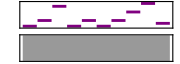

```mathematica
Sound[RandomChoice[cmajor,10]]
```

Add some rests and randomize the durations of each note. The symbol None is interpreted by Sound as a rest.

```mathematica
notes=Join[{None},Range[0,11]]
```

{None,0,1,2,3,4,5,6,7,8,9,10,11}

```mathematica
durations=Range[1/8,1,1/8]
```

{1/8,1/4,3/8,1/2,5/8,3/4,7/8,1}

```mathematica
MapThread[SoundNote[#1,#2]&,
{RandomChoice[notes,8],RandomChoice[durations,8]}]
```

{SoundNote[4,1],SoundNote[9,1/8],SoundNote[1,1],SoundNote[9,7/8],SoundNote[3,1/8],SoundNote[2,3/8],SoundNote[3,1/2],SoundNote[3,1/2]}

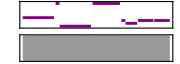

```mathematica
Sound[%]
```

Here then is a function that takes the number of notes and the instrument as arguments.

```mathematica
RandomNotes[n_Integer,instrument_:"Piano"]:=With[{notes=Join[{None},Range[0,11]],durations=Range[1/8,1,1/8]},Sound[{instrument,MapThread[SoundNote[#1,#2]&,{RandomChoice[notes,n],RandomChoice[durations,n]}]}]]
```

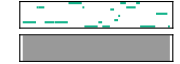

```mathematica
RandomNotes[20,"Vibraphone"]
```

First set up the options structure.

```mathematica
Options[BrownianSoundList]={Weights->Automatic};
```

```mathematica
BrownianSoundList[steps_Integer,instr_:"Vibraphone",OptionsPattern[]]:=Module[{walk,durs,weights},
weights=If[OptionValue[Weights]===Automatic,Table[1/9,{9}],OptionValue[Weights]];
walk[n_]:=Accumulate[RandomChoice[weights->Range[-4,4],n]];
durs=RandomChoice[Range[1/16,1,1/16],{steps}];
Sound@MapThread[SoundNote[#1,#2,instr]&,{walk[steps],durs}]
]
```

```mathematica
BrownianSoundList[18,"Vibraphone"]//EmitSound
```

```mathematica
BrownianSoundList[18,"Marimba",Weights->Abs@RandomVariate[NormalDistribution[0,4],9]]//EmitSound
```

(* solution to appear *)

Start with one hundred points.

```mathematica
data=RandomReal[{-1,1},{100,2}];
```

Partition into eight clusters.

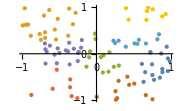

```mathematica
clusters=FindClusters[data,8];
ListPlot[clusters,PlotStyle->PointSize@Medium]
```

The centroid and color computations are as before.

```mathematica
centroids=Map[Mean,clusters]
```

{{0.813483,-0.257487},{-0.664783,0.609614},{0.0631635,-0.0791516},{-0.473583,-0.731627},{-0.446728,0.04197},{0.389006,-0.792897},{0.514577,0.263179},{0.683372,0.871155}}

```mathematica
colors=Take[ColorData[1,"ColorList"],Length[clusters]]
```

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.42664098839727194, 0.24],RGBColor[0.2634521802031821, 0.6, 0.24]}

To ﬁnd the distance from each centroid to the point in its cluster farthest away, we want the max of the set of distances between the cluster and the points in that cluster.

```mathematica
distances=Table[
Max@Map[EuclideanDistance[centroids[[i]],#]&,clusters[[i]]],{i,1,Length[clusters]}]
```

{0.429688,0.479782,0.516458,0.435077,0.355637,0.411775,0.364234,0.30396}

The code to create the disks is identical to that in this section.

```mathematica
disks=MapThread[{#1,Disk[#2,#3]}&,{colors,centroids,distances}];
```

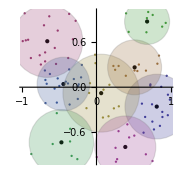

```mathematica
ListPlot[clusters,PlotStyle->colors,AspectRatio->Automatic,Epilog->{
PointSize[Medium],Point[centroids],
Opacity[0.25],EdgeForm[Gray],disks},PlotRangePadding->.35]
```

First create a set of points with which to prototype. Choose a small set to make it easier to inspect the progress.

```mathematica
SeedRandom[6];
pts=RandomInteger[40,{10,2}]
```

{{16,18},{28,12},{25,35},{10,13},{26,12},{24,15},{30,34},{5,0},{16,38},{1,6}}

Next, choose a point at random from this set of points.

```mathematica
base=RandomChoice[pts]
```

{16,38}

Add it to a list path that we will maintain as the algorithm progresses.

```mathematica
path={base}
```

{{16,38}}

Next, create a list of all those points with this base points deleted, resetting pts to this new value.

```mathematica
pts=Complement[pts,path]
```

{{1,6},{5,0},{10,13},{16,18},{24,15},{25,35},{26,12},{28,12},{30,34}}

Find the point nearest this list of points. Call it the new base point.

```mathematica
base=First@Nearest[pts,path]
```

{{25,35}}

Add this new base point to existing list path and reset the value of path:

```mathematica
path=Join[path,base]
```

{{16,38},{25,35}}

Iterate:

```mathematica
SeedRandom[6];
pts=RandomInteger[40,{10,2}];

base=RandomChoice[pts];
path={base};
Do[
pts=Complement[pts,path];
base=First@Nearest[pts,path];
path=Join[path,base],

{Length[pts]-1}];
path
```

{{16,38},{25,35},{30,34},{16,18},{24,15},{10,13},{26,12},{28,12},{1,6},{5,0}}

Find the length of the path, connecting the last point to the ﬁrst to make a closed loop.

```mathematica
ArcLength[Line[path/.{a_,b__}:>{a,b,a}]]//N
```

150.993

Compare the built-in function for ﬁnding shortest tours. The ﬁrst element in the returned list is the length of the tour and the second element is the ordering on the positions of the points in the tour.

```mathematica
SeedRandom[6];
pts=RandomInteger[40,{10,2}];
FindShortestTour[pts]
```

{27+3 √10+2 √13+√26+√61+3 √65+√130+√397,{1,4,10,8,5,2,6,7,3,9,1}}

```mathematica
N[%[[1]]]
```

112.121

First, create 1000 points in the unit square.

```mathematica
pts=RandomReal[{-1,1},{1000,2}];
```

Next create regions that represent the unit disk and unit square.

```mathematica
𝒟=Disk[{0,0},1];
𝒫=Polygon[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}];
```

Now select those point that are members of the disk region. You could use Select or Count.

```mathematica
Length@Select[pts,RegionMember[𝒟,#]&]
```

782

```mathematica
Count[pts,p_/;RegionMember[𝒟,p]]
```

782

The following ratio is a crude approximation to π/4.

```mathematica
Length@Select[pts,RegionMember[𝒟,#]&]/Length[pts]
```

391/500

```mathematica
4N[%]
```

3.128

6
Programs

Exercises: Scoping constructs

The condition number of a square matrix gives a measure of how close the matrix is to being singular. First proposed by Alan Turing, it is often deﬁned as the ratio of the largest singular value of the matrix to the smallest singular value. The condition number can give a sense of how much the solution of the matrix equation A.x=b can change for small perturbations of the vector b.

Create a function ConditionNumber[mat] that takes a square matrix mat and returns its condition number. Then test it on several Hilbert matrices (HilbertMatrix), which are known to have very large condition numbers, thus rendering numerical computations with them problematic from a precision point of view.

Turn the random graph example in Exercise 10, Section 5.6 into a function RandomGraphGnp[n,p] that returns a random graph on n vertices with edges chosen randomly (BernoulliDistribution) using probability p.

Create a function EquilateralTriangleQ that takes a Triangle object as an argument and returns a value of True if that triangle is equilateral and returns a value of False if it is not. A triangle is equilateral if the lengths of its three sides are identical. Create two implementations, one using EuclideanDistance to measure the side lengths and another using ArcLength with MeshRegion and MeshPrimitives.

Based on the row-switching example in this section, create a function to swap matrix columns.

Rewrite the function FindSubsequence from Exercise 7, Section 4.3 using Module to localize the length of the subsequence subseq.

The PerfectSearch function deﬁned in Exercise 6, Section 5.1 is impractical for checking large numbers because it has to check all numbers from 1 through n. It is inefﬁcient to check all numbers from 1 to 1000 if you are only looking for perfect numbers in the range 500 to 1000. Modify PerfectSearch so that it is self-contained, deﬁning the perfect predicate inside the body of the function. Also, set up the argument structure to accept two numbers as input and have the function output all perfect numbers between those inputs. For example, PerfectSearch[a,b] will return a list of all perfect numbers in the range from a to b.

A number n is k-perfect if the sum of its proper divisors equals k n. Redeﬁne PerfectSearch from the previous exercise so that it accepts as input two numbers a and b, a positive integer k, and computes all k-perfect numbers in the range from a to b. Use your rule to ﬁnd the only three 4-perfect numbers less than 2200000.

Often in processing ﬁles you are presented with expressions that need to be converted into a format that can be more easily manipulated. For example, a ﬁle may contain dates in the form 20160702 to represent July 2, 2016. Mathematica represents its dates as a list in the following form:

{year,month,day,hour,minutes,seconds}

Write a function convertToDate[n] to convert a number consisting of eight digits such as 20160702 into a list of the form {2016,7,2}.

```mathematica
convertToDate[20160702]
```

{2016,7,2}

Create a function zeroColumns[mat,m;;n] that zeros out columns m through n in matrix mat. Include rules to handle the cases of zeroing out one column or a list of nonconsecutive columns.

Following on the code for the one-dimensional random walk, create a function walk2D[n] that generates n steps of a two-dimensional random walk on the integer lattice (see Exercise 8, Section 2.1). For such a walk, the directions can be thought of as the two-dimensional vectors {0,1}, {0,-1}, {1,0}, and {-1,0} pointing in the direction of the compass directions north, south, east, and west. Then create a function walk3D[n] that returns an n-step random walk on the three-dimensional integer lattice.

Solutions

Let us start with the 3×3 Hilbert matrix.

```mathematica
mat=HilbertMatrix[3]
```

{{1,1/2,1/3},{1/2,1/3,1/4},{1/3,1/4,1/5}}

Here are its singular values:

```mathematica
sv=SingularValueList[mat]
```

{√Root[-1+138537 #1-9323424 #1^2+4665600 #1^3&,3],√Root[-1+138537 #1-9323424 #1^2+4665600 #1^3&,2],√Root[-1+138537 #1-9323424 #1^2+4665600 #1^3&,1]}

We are interested in the ratio of the largest to the smallest.

```mathematica
N[Max[sv]/Min[sv]]
```

524.057

Actually, SingularValueList returns the singular values ordered from greatest to smallest. So we can speed up the computation by only pulling off those positions rather than computing maximum and minimum values.

```mathematica
N[First[sv]/Last[sv]]
```

524.057

Here is the function deﬁnition. We use Module to localize a variable sv that is used in the body of the function. Also, the deﬁnition given in the exercise is good for square matrices so we do some argument checking on the left-hand side of the deﬁnition.

```mathematica
ConditionNumber[mat_?SquareMatrixQ]:=Module[{sv=SingularValueList[mat]},
First[sv]/Last[sv]]
```

Here are the condition numbers for the ﬁrst ﬁve Hilbert matrices

```mathematica
Table[ConditionNumber[HilbertMatrix[i]],{i,1,5}]//N
```

{1.,19.2815,524.057,15513.7,476607.}

And this tests with a known pathological example of a 4×4 matrix (Rump 1991).

```mathematica
mat={{-5046135670319638,-3871391041510136,-5206336348183639,-6745986988231149},{-640032173419322,8694411469684959,-564323984386760,-2807912511823001},{-16935782447203334,-18752427538303772,-8188807358110413,-14820968618548534},{-1069537498856711,-14079150289610606,7074216604373039,7257960283978710}};
```

```mathematica
ConditionNumber[mat]//N
```

6.41354×10^64

Here are the code fragments from Exercise 10 in Section 5.6.

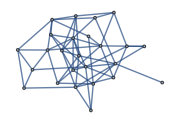

```mathematica
With[{n=25,p=.2},
cg=CompleteGraph[n];probs=RandomVariate[BernoulliDistribution[p],EdgeCount[cg]];
Graph[Pick[EdgeRules[cg],probs,1],DirectedEdges->False]]
```

And here is the function, localizing cg and probs.

```mathematica
RandomGraphGnp[n_,p_]:=Module[{cg=CompleteGraph[n],probs},
probs=RandomVariate[BernoulliDistribution[p],EdgeCount[cg]];
Graph[Pick[EdgeRules[cg],probs,1],DirectedEdges->False]]
```

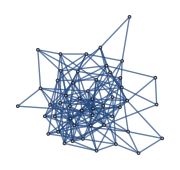

```mathematica
RandomGraphGnp[50,.15]
```

Start by creating a prototypical triangle to work with.

```mathematica
pts={{0,0},{1,0},{1/2,√3/2}};
```

```mathematica
tri=Triangle[pts]
```

Triangle[{{0,0},{1,0},{1/2,(√3)/2}}]

To measure the lengths of the sides, create all possible pairs of the points and apply EuclideanDistance (at level one).

```mathematica
Apply[EuclideanDistance,Subsets[pts,{2}],{1}]
```

{1,1,1}

Finally, check if all distances are equal.

```mathematica
Apply[Equal,%]
```

True

Here then is the ﬁrst implementation:

```mathematica
EquilateralTriangleQ[Triangle[pts:{__}]]:=Module[{dists},
dists=Apply[EuclideanDistance,Subsets[pts,{2}],{1}];
Apply[Equal,dists]]
```

To use the region framework, ﬁrst generate a mesh region from the coordinate points. MeshRegion takes two arguments: a list of coordinates and a region (in our case, Triangle) speciﬁed by the coordinate indices.

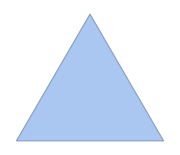

```mathematica
𝒯=MeshRegion[pts,Triangle[{1,2,3}]]
```

The lines are the one-dimensional primitives in this region.

```mathematica
MeshPrimitives[𝒯,1]
```

{Line[{{0.,0.},{1.,0.}}],Line[{{1.,0.},{0.5,0.866025}}],Line[{{0.5,0.866025},{0.,0.}}]}

Here are their lengths:

```mathematica
Map[ArcLength,%]
```

{1.,1.,1.}

Here then is the implementation using regions.

```mathematica
EquilateralTriangleQ[Triangle[pts:{__}]]:=Module[{dists},
dists=Map[ArcLength,MeshPrimitives[MeshRegion[pts,Triangle[{1,2,3}]],1]];
Apply[Equal,dists]]
```

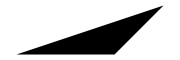

```mathematica
tri=Triangle[{{-1,0},{1,0},{2,1}}];
Graphics[tri]
```

```mathematica
EquilateralTriangleQ[tri]
```

False

```mathematica
pts={{0,0},{1,0},{1/2,√3/2}};
EquilateralTriangleQ[Triangle[pts]]
```

True

Switching columns is basically switching rows of the transposed matrix and then transposing back.

```mathematica
switchRows[mat_,{r1_,r2_}]:=Module[{lmat=mat},
lmat[[{r1,r2}]]=lmat[[{r2,r1}]];
lmat]
```

```mathematica
switchColumns[mat_,{c1_,c2_}]:=Transpose@switchRows[Transpose[mat],{c1,c2}]
```

```mathematica
mat={{a,b,c},{d,e,f},{g,h,i}};
switchColumns[mat,{2,3}]//MatrixForm
```

(a | c | b
d | f | e
g | i | h)

The FindSubsequence function from Section 4.3 computed Length[subseq] twice on the right-hand side of the deﬁnition. Setting up a local variable len that computes this value as part of the initialization shortens the code and makes it a bit more efﬁcient.

```mathematica
FindSubsequence[digits_List,subseq_List]:=Module[{len=Length[subseq]},
Position[Partition[digits,len,1],subseq]/.{num_?IntegerQ}:>{num,num+len-1}
]
```

```mathematica
pidigs=First[RealDigits[π,10,10^7,-1]];
```

```mathematica
FindSubsequence[pidigs,{3,1,4,1,5,9}]//Timing
```

{10.2822,{{176451,176456},{1259351,1259356},{1761051,1761056},{6467324,6467329},{6518294,6518299},{9753731,9753736},{9973760,9973765}}}

The following function creates a local function perfectQ using the Module construct. It then checks every other number between n and m by using a third argument to the Range function.

```mathematica
PerfectSearch[n_,m_]:=Module[{perfectQ},
perfectQ[j_]:=DivisorSigma[1,j]==2 j;Select[Range[n,m,2],perfectQ]]
```

```mathematica
PerfectSearch[2,10^7]//Timing
```

{26.3649,{6,28,496,8128}}

This function does not guard against the user supplying “bad” inputs. For example, if the user starts with an odd number, then this version of PerfectSearch will check every other odd number, and, since it is known that there are no odd perfect numbers below at least 10^300, none is reported.

```mathematica
PerfectSearch[1,10000]
```

{}

You can ﬁx this situation by using the (as yet unproved) assumption that there are no odd perfect numbers. This next version ﬁrst checks that the ﬁrst argument is an even number.

```mathematica
Clear[PerfectSearch]
```

```mathematica
PerfectSearch[n_?EvenQ,m_]:=Module[{perfectQ},
perfectQ[j_]:=Total[Divisors[j]]==2 j;Select[Range[n,m,2],perfectQ]]
```

Now, the function only works if the ﬁrst argument is even.

```mathematica
PerfectSearch[2,10000]
```

{6,28,496,8128}

```mathematica
PerfectSearch[1,1000]
```

PerfectSearch[1,1000]

This function requires a third argument.

```mathematica
Clear[PerfectSearch];
PerfectSearch[n_,m_,k_]:=Module[{perfectQ},
perfectQ[j_]:=Total[Divisors[j]]==k j;
Select[Range[n,m],perfectQ]]
```

The following computation can be quite time consuming and requires a fair amount of memory to run to completion. If your computer’s resources are limited, you should split up the search intervals into smaller units or try running this in parallel. See Section 9.2 for a discussion on how to set up parallel computation.

```mathematica
PerfectSearch[1,2200000,4]//AbsoluteTiming
```

{21.925,{30240,32760,2178540}}

Many implementations are possible for convertToDate. The task is made easier by observing that DateList handles this task directly if its argument is a string.

```mathematica
DateList["20151015"]
```

{2015,10,15,0,0,0.}

The string is necessary otherwise DateList will interpret the integer as an absolute time (from Jan 1 1900).

```mathematica
DateList[20151015]
```

{1900,8,22,5,30,15.}

So we need to convert the integer to a string ﬁrst,

```mathematica
DateList[ToString[20151015]]
```

{2015,10,15,0,0,0.}

and then take the ﬁrst three elements.

```mathematica
Take[%,3]
```

{2015,10,15}

Here is the function that puts these steps together.

```mathematica
convertToDate[n_Integer]:=Take[DateList[ToString[n]],3]
```

```mathematica
convertToDate[20151015]
```

{2015,10,15}

With a bit more manual work, you could also do this with StringTake.

```mathematica
convertToDate2[n_Integer/;Length[IntegerDigits[n]]==8]:=Module[{str=ToString[n]},
{StringTake[str,4],StringTake[str,{5,6}],StringTake[str,-2]}]
```

```mathematica
convertToDate2[20151015]
```

{2015,10,15}

You could avoid working with strings by making use of FromDigits. This uses With to create a local constant d, as this expression never changes throughout the body of the function.

```mathematica
convertToDate3[num_]:=With[{d=IntegerDigits[num]},
{FromDigits[Take[d,4]],
FromDigits[Take[d,{5,6}]],
FromDigits[Take[d,{7,8}]]}]
```

```mathematica
convertToDate3[20151015]
```

{2015,10,15}

The computation of zeroing out one or more columns of a matrix can be handled with list component assignment. We need to use a local variable here to avoid changing the original matrix.

```mathematica
mat=RandomReal[1,{5,5}];
MatrixForm[mat]
```

(0.560325 | 0.895832 | 0.087212 | 0.889873 | 0.405831
0.626251 | 0.787507 | 0.45469 | 0.384032 | 0.892384
0.296374 | 0.505962 | 0.319666 | 0.327262 | 0.825282
0.121677 | 0.0413138 | 0.994354 | 0.0078785 | 0.77109
0.205495 | 0.959287 | 0.337399 | 0.940264 | 0.900914)

Here is a rule for zeroing out one column:

```mathematica
zeroColumns[mat_,n_Integer]:=Module[{lmat=mat},
lmat[[All,n]]=0;
lmat]
```

This next rule is for zeroing out a range of columns:

```mathematica
zeroColumns[mat_,Span[m_,n_]]:=Module[{lmat=mat},
lmat[[All,m;;n]]=0;
lmat]
```

We also need a ﬁnal rule for zeroing out a discrete set of columns whose positions are given by a list.

```mathematica
zeroColumns[mat_,lis:{__}]:=Module[{lmat=mat},
lmat[[All,lis]]=0;
lmat]
```

```mathematica
zeroColumns[mat,3]//MatrixForm
```

(0.560325 | 0.895832 | 0 | 0.889873 | 0.405831
0.626251 | 0.787507 | 0 | 0.384032 | 0.892384
0.296374 | 0.505962 | 0 | 0.327262 | 0.825282
0.121677 | 0.0413138 | 0 | 0.0078785 | 0.77109
0.205495 | 0.959287 | 0 | 0.940264 | 0.900914)

```mathematica
zeroColumns[mat,1;;2]//MatrixForm
```

(0 | 0 | 0.087212 | 0.889873 | 0.405831
0 | 0 | 0.45469 | 0.384032 | 0.892384
0 | 0 | 0.319666 | 0.327262 | 0.825282
0 | 0 | 0.994354 | 0.0078785 | 0.77109
0 | 0 | 0.337399 | 0.940264 | 0.900914)

```mathematica
zeroColumns[mat,{1,3,5}]//MatrixForm
```

(0 | 0.895832 | 0 | 0.889873 | 0
0 | 0.787507 | 0 | 0.384032 | 0
0 | 0.505962 | 0 | 0.327262 | 0
0 | 0.0413138 | 0 | 0.0078785 | 0
0 | 0.959287 | 0 | 0.940264 | 0)

Here is the code for the two-dimensional walk. Except for the direction vectors, it is identical to the code for the one-dimensional walk.

```mathematica
walk2D[t_]:=Module[{dirs,steps},
dirs={{0,1},{0,-1},{1,0},{-1,0}};
steps=RandomChoice[dirs,{t}];
Accumulate[steps]
]
```

Try it out for a small number of steps and a large number of steps.

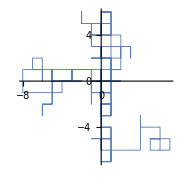

```mathematica
ListLinePlot[walk2D[250],AspectRatio->1]
```

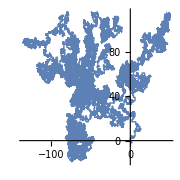

```mathematica
ListLinePlot[walk2D[25000],AspectRatio->1,PlotStyle->Thin]
```

A bit of thought is needed to come up with the eight directions in the three-dimensional integer lattice.

```mathematica
dirs3={{1,0,0},{0,1,0},{0,0,1},{-1,0,0},{0,-1,0},{0,0,-1}};
```

Here then is the three-dimensional walk function.

```mathematica
walk3D[t_]:=Accumulate[RandomChoice[dirs3,t]]
```

And here is a 2500-step walk on the three-dimensional integer lattice.

```mathematica
Graphics3D[Line[walk3D[2500]]]
```

-Graphics3D-

Exercises: Options and messages

Modify the random graph example in Exercise ExerciseItem, Section Chapter.Section to inherit options from Graph.

In Section Chapter.Section we developed a function switchRows that interchanged two rows in a matrix. Create a message for this function that is issued whenever a row index greater than the size of the matrix is used as an argument. For example,

```mathematica
mat=RandomInteger[{0,9},{4,4}];
MatrixForm[mat]
```

(8 | 0 | 9 | 2
7 | 2 | 1 | 9
4 | 5 | 0 | 4
2 | 8 | 6 | 4)

```mathematica
switchRows[mat,{5,2}]
```

switchRows::badargs: The absolute value of the row indices 5 and 2 in switchRows[mat,{5,2}] must be between 1 and 4, the size of the matrix.

{{8,0,9,2},{7,2,1,9},{4,5,0,4},{2,8,6,4}}

You should also trap for a row index of zero.

```mathematica
switchRows[mat,{0,2}]
```

switchRows::badargs: The absolute value of the row indices 0 and 2 in switchRows[mat,{0,2}] must be between 1 and 4, the size of the matrix.

{{8,0,9,2},{7,2,1,9},{4,5,0,4},{2,8,6,4}}

Create an error message for StemPlot, developed in this section, so that an appropriate message is issued if the argument is not a list of numbers.

Extend the deﬁnitions for ToEdges from Exercise 15, Section 5.1 to include an option to output directed or undirected edges.

The function MultiplyCount given in the solution to Exercise 7, Section 4.2 does not check that the expression passed to it is in fact a polynomial. Rewrite this function so that MultiplyCount[poly,var] checks that poly is a polynomial in the independent variable var and issues an appropriate message if the polynomial test fails.

Solutions

First, set up the options inherited from Graph.

```mathematica
Options[RandomGraphGnp]=Options[Graph];
```

```mathematica
RandomGraphGnp[n_,p_,opts:OptionsPattern[]]:=Module[{cg,probs},
cg=CompleteGraph[n];probs=RandomVariate[BernoulliDistribution[p],EdgeCount[cg]];
Graph[Pick[EdgeRules[cg],probs,1],opts,DirectedEdges->False]]
```

Alternatively, you could use RandomChoice to pick the True/False values.

```mathematica
RandomGraphGnp[n_,p_,opts:OptionsPattern[]]:=Module[{cg,probs},
cg=CompleteGraph[n];probs=RandomChoice[{p,1-p}->{True,False},EdgeCount[cg]];
Graph[Pick[EdgeRules[cg],probs],opts,DirectedEdges->False]]
```

Exercise the options.

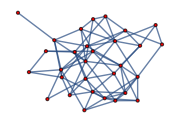

```mathematica
RandomGraphGnp[30,.2,VertexSize->Large,VertexStyle->Red,EdgeStyle->Thin]
```

The message will slot in the values of the row indices being passed to the function switchRows, as well as the length of the matrix, that is, the number of matrix rows.

```mathematica
switchRows::badargs="The absolute value of the row indices `1` and `2` in switchRows[mat,`1`,`2`] must be between 1 and `3`, the size of the matrix.";
```

The message is issued if either of the row indices have absolute value greater than the length of the matrix or if either of these indices is equal to zero.

```mathematica
switchRows[mat_,{r1_Integer,r2_Integer}]:=Module[{lmat=mat,len=Length[mat]},
If[Abs[r1]>len||Abs[r2]>len||r1 r2==0,
Message[switchRows::badargs,r1,r2,len],
lmat[[{r1,r2}]]=lmat[[{r2,r1}]]];
lmat]
```

```mathematica
mat=RandomInteger[9,{4,4}];
MatrixForm[mat]
```

(4 | 8 | 5 | 4
4 | 4 | 3 | 7
0 | 5 | 7 | 3
8 | 4 | 1 | 7)

```mathematica
switchRows[mat,{0,4}]
```

switchRows::badargs: The absolute value of the row indices 0 and 4 in switchRows[mat,0,4] must be between 1 and 4, the size of the matrix.

{{4,8,5,4},{4,4,3,7},{0,5,7,3},{8,4,1,7}}

```mathematica
switchRows[mat,{2,8}]
```

switchRows::badargs: The absolute value of the row indices 2 and 8 in switchRows[mat,2,8] must be between 1 and 4, the size of the matrix.

{{4,8,5,4},{4,4,3,7},{0,5,7,3},{8,4,1,7}}

If the ﬁrst argument is not a list containing numbers, then issue a message.

```mathematica
MatchQ[{1,2,a},{__?NumericQ}]
```

False

Here is the message:

```mathematica
StemPlot::badarg="The first argument to StemPlot must be a list of numbers.";
```

```mathematica
Options[StemPlot]=Options[ListPlot];
```

```mathematica
StemPlot[lis_,opts:OptionsPattern[]]:=
If[MatchQ[lis,{__?NumericQ}],
ListPlot[lis,opts,Filling->Axis],
Message[StemPlot::badarg]
]
```

```mathematica
StemPlot[4]
```

StemPlot::badarg: The first argument to StemPlot must be a list of numbers.

```mathematica
StemPlot[{1,2,c}]
```

StemPlot::badarg: The first argument to StemPlot must be a list of numbers.

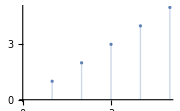

```mathematica
StemPlot[{1,2,3,4,5}]
```

First set up the option for ToEdges.

```mathematica
Options[ToEdges]={DirectedEdges->True};
```

```mathematica
ToEdges[lis:{{_,_}..},OptionsPattern[]]:=If[OptionValue[DirectedEdges],DirectedEdge@@@lis,UndirectedEdge@@@lis]
```

```mathematica
ToEdges[lis:{_,_},OptionsPattern[]]:=If[OptionValue[DirectedEdges],DirectedEdge@@lis,UndirectedEdge@@lis]
```

```mathematica
pairs=Partition[Range[5],2,1]
```

{{1,2},{2,3},{3,4},{4,5}}

```mathematica
ToEdges[pairs]
```

{1->2,2->3,3->4,4->5}

```mathematica
ToEdges[pairs,DirectedEdges->False]
```

{1<->2,2<->3,3<->4,4<->5}

We use If to check if the expression expr is a polynomial in the independent variable var. If it is, use the same code from Exercise 7, Section 4.2 to count the number of multiplies. If the test fails, then issue a message.

```mathematica
MultiplyCount[expr_,var_]:=If[PolynomialQ[expr,var],Total@Cases[{expr},Power[_,exp_]:>exp-1,Infinity]+Total@Cases[{expr},fac_Times:>Length[fac]-1,Infinity],Message[MultiplyCount::poly,expr]]
```

Note that we have done something a bit different here. We have used an internal usage message poly with our MultiplyCount function. Here is the message issued by the built-in function PolynomialRemainder.

```mathematica
PolynomialRemainder[{3x},x+a,x]
```

PolynomialRemainder::poly: {3\ x} is not a polynomial.

PolynomialRemainder[{3 x},a+x,x]

```mathematica
MultiplyCount[{a x^4+b x+1},x]
```

MultiplyCount::poly: {1 + b\ x + a\ x^4} is not a polynomial.

```mathematica
MultiplyCount[a x^4+b x+1,x]
```

5

Exercises: Examples

Add a message to the RandomWalk function developed in this chapter so that a warning is issued when a nonpositive integer is given as the ﬁrst argument to RandomWalk.

Consider a sequence of numbers generated by the following iterative process: starting with the list of odd integers 1, 3, 5, 7, …, the ﬁrst odd number greater than 1 is 3, so delete every third number from the list; from the list of remaining numbers, the next number is 7, so delete every seventh number; and so on. The numbers that remain are referred to as lucky numbers. Use a sieving method to ﬁnd all lucky numbers less than 1000. See Weisstein (Lucky Number) for more information.

Create a function TruthTable[expr,vars] that takes a logical expression such as A∧B and outputs a truth table similar to those in Section 2.4. You can create a list of truth values using Tuples:

```mathematica
Tuples[{True,False},2]
```

{{True,True},{True,False},{False,True},{False,False}}

You will also ﬁnd it helpful to consider threading rules over the tuples using MapThread or Thread. Alternatively, consider using the built-in function BooleanTable.

Given a list of expressions, lis, create a function NearTo[lis,elem,{n}}] that returns all elements of lis that are exactly n positions away from elem, which is assumed to be a member of lis. For example:

```mathematica
chars=CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
NearTo[chars,"q",{3}]
```

{{n},{t}}

Write a second rule, NearTo[lis,elem,n], that returns all elements in lis that are within n positions of elem.

```mathematica
NearTo[chars,"q",4]
```

{{m,n,o,p,q,r,s,t,u}}

Finally, create your own distance function (DistanceFunction) and use it with the built-in Nearest to do the same computation. Two useful functions for these tasks are Position and Extract. Extract[expr,pos] returns elements from expr whose positions pos are given by Position.

A Smith number is a composite number such that the sum of its digits is equal to the sum of the digits of its prime factors. For example, the prime factorization of 852 is 2^2·3^1·71^1, and so the sum of the digits of its prime factors is 2+2+3+7+1=15, which is equal to the sum of its digits, 8+5+2=15. Write a program to ﬁnd all Smith numbers less than 10000.

Develop auxiliary functions for one-, two-, and three-dimensional off-lattice random walks. Then create a function offLatticeWalk[steps,dim] that uses these auxiliary functions to return an off-lattice walk of length steps, in dimension dim. Finally, modify RandomWalk to include an option LatticeWalk that, when set to True, calls the latticeWalk auxiliary function and when set to False, calls this new offLatticeWalk auxiliary function.

Here is some code to run a bond percolation simulation on an m×n lattice grid. For each edge in the grid graph gg, it creates a probability from a Bernoulli distribution (think coin ﬂip – only two possible outcomes) and then picks those edges that are below the threshold probability prob.

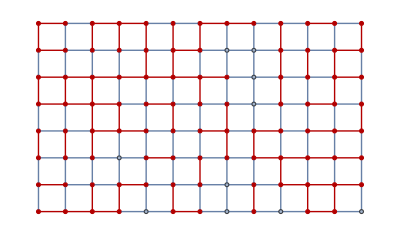

```mathematica
With[{m=8,n=13,prob=0.47},
gg=GridGraph[{m,n}];
probs=RandomVariate[BernoulliDistribution[prob],EdgeCount[gg]];perc=Graph[Pick[EdgeList[gg],probs,1]];
HighlightGraph[gg,perc]]
```

Turn the above code into a function BondPercolation[{m,n},prob,opts] that outputs a graph like that above. Include a check on the arguments m and n, returning an appropriate message if they are not positive integers. Finally, have your function inherit options from Graph and pass them into the GridGraph function.

Create a function ColorResidues[seq] that takes an amino acid sequence seq and returns a visualization like that below where the amino acids are colored according to a scheme such as Amino, where more polar residues are brighter and more nonpolar residues are colored darker. In addition to a ColorScheme option, add options to control the frame around each residue.

```mathematica
Amino={{"P",-Graphics-},{"W",-Graphics-},{"L",-Graphics-},{"V",-Graphics-},{"I",-Graphics-},{"N",-Graphics-},{"Q",-Graphics-},{"S",-Graphics-},{"T",-Graphics-},{"C",-Graphics-},{"M",-Graphics-},{"H",-Graphics-},{"A",-Graphics-},{"G",-Graphics-},{"F",-Graphics-},{"Y",-Graphics-},{"K",-Graphics-},{"R",-Graphics-},{"D",-Graphics-},{"E",-Graphics-}};
```

```mathematica
muc6=StringTake[ProteinData["MUC6","Sequence"],75]
```

MVQRWLLLSCCGALLSAGLANTSYTSPGLQRLKDSPQTAPDKGQCSTWGAGHFSTFDHHVYDFSGTCNYIFAATC

```mathematica
ColorResidues[muc6,ColorScheme->Amino,FrameMargins->2]
```

MVQRWLLLSCCGALLSAGLANTSYTSPGLQRLKDSPQTAPDKGQCSTWGAGHFSTFDHHVYDFSGTCNYIFAATC

Solutions

Here is the message text that will be issued when the ﬁrst argument to RandomWalk is not a positive integer.

```mathematica
RandomWalk::rwn="Argument `1` is not a positive integer.";
```

And here is the message for the Dimensions option.

```mathematica
RandomWalk::baddim="The value `1` of the option Dimension is not a positive integer.";
```

Because we now have several conditions to trap for (non positive integer ﬁrst argument, bad value for Dimension option), it is best to use Which to catch the various conditions and set appropriate actions.

```mathematica
latticeWalk[steps_,dim_]:=Module[{w,mat},
mat=Join[IdentityMatrix[dim],-IdentityMatrix[dim]];w=Accumulate[RandomChoice[mat,steps]];
If[dim==1,Flatten[w],w]
]
```

To simplify the code it is useful to have an auxiliary predicate that tests if its argument is a positive integer.

```mathematica
PositiveIntegerQ[n_]:=IntegerQ[n]&&Positive[n]
```

```mathematica
Options[RandomWalk]={Dimension->2};
```

```mathematica
RandomWalk[t_,OptionsPattern[]]:=Module[{dim,latticeQ},
dim=OptionValue[Dimension];
Which[
!PositiveIntegerQ[t],Message[RandomWalk::rwn,t],
!PositiveIntegerQ[dim],Message[RandomWalk::baddim,dim],
True,latticeWalk[t,dim]
]
]
```

First check that correct results are returned for correct values of the arguments and options.

```mathematica
RandomWalk[3]
```

{{1,0},{1,1},{1,0}}

```mathematica
RandomWalk[4,Dimension->5]
```

{{0,0,-1,0,0},{0,0,-1,0,-1},{0,0,-1,0,-2},{0,0,-2,0,-2}}

Then check for bad input.

```mathematica
RandomWalk[4,Dimension->-5]
```

RandomWalk::baddim: The value -5 of the option Dimension is not a positive integer.

```mathematica
RandomWalk[4.3,Dimension->-5]
```

RandomWalk::rwn: Argument 4.3 is not a positive integer.

Start with a small list of odd numbers.

```mathematica
ints=Range[1,100,2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

On the ﬁrst iteration, drop every third number, that is, drop 5, 11, 17, and so on.

```mathematica
p=ints[[2]];
ints=Drop[ints,p;;-1;;p]
```

{1,3,7,9,13,15,19,21,25,27,31,33,37,39,43,45,49,51,55,57,61,63,67,69,73,75,79,81,85,87,91,93,97,99}

Get the next number, 7, in the list ints; then drop every seventh number.

```mathematica
p=ints[[3]];
ints=Drop[ints,p;;-1;;p]
```

{1,3,7,9,13,15,21,25,27,31,33,37,43,45,49,51,55,57,63,67,69,73,75,79,85,87,91,93,97,99}

Iterate. You will need to be careful about the upper limit of the iterator i.

```mathematica
ints=Range[1,1000,2];
Do[
p=ints[[i]];
ints=Drop[ints,p;;-1;;p],
{i,2,32}]
ints
```

{1,3,7,9,13,15,21,25,31,33,37,43,49,51,63,67,69,73,75,79,87,93,99,105,111,115,127,129,133,135,141,151,159,163,169,171,189,193,195,201,205,211,219,223,231,235,237,241,259,261,267,273,283,285,289,297,303,307,319,321,327,331,339,349,357,361,367,385,391,393,399,409,415,421,427,429,433,451,463,475,477,483,487,489,495,511,517,519,529,535,537,541,553,559,577,579,583,591,601,613,615,619,621,631,639,643,645,651,655,673,679,685,693,699,717,723,727,729,735,739,741,745,769,777,781,787,801,805,819,823,831,841,855,867,873,883,885,895,897,903,925,927,931,933,937,957,961,975,979,981,991,993,997}

It would be more efﬁcient if you did not need to manually determine the upper limit of the iteration. A While loop is better for this task. The test checks that the value of the iterator has not gone past the length of the successively shortened lists.

```mathematica
LuckyNumbers[n_Integer?Positive]:=Module[{p,i=2,ints=Range[1,n,2]},
While[ints[[i]]<Length[ints],
p=ints[[i]];
ints=Drop[ints,p;;-1;;p];
i++];
ints]
```

```mathematica
LuckyNumbers[1000]
```

{1,3,7,9,13,15,21,25,31,33,37,43,49,51,63,67,69,73,75,79,87,93,99,105,111,115,127,129,133,135,141,151,159,163,169,171,189,193,195,201,205,211,219,223,231,235,237,241,259,261,267,273,283,285,289,297,303,307,319,321,327,331,339,349,357,361,367,385,391,393,399,409,415,421,427,429,433,451,463,475,477,483,487,489,495,511,517,519,529,535,537,541,553,559,577,579,583,591,601,613,615,619,621,631,639,643,645,651,655,673,679,685,693,699,717,723,727,729,735,739,741,745,769,777,781,787,801,805,819,823,831,841,855,867,873,883,885,895,897,903,925,927,931,933,937,957,961,975,979,981,991,993,997}

This latter approach is also reasonably fast. Here is the time it takes to compute all lucky numbers less than one million; there are 71918 of them.

```mathematica
Length[LuckyNumbers[10^6]]//Timing
```

{0.302607,71918}

Start with a prototype logical expression.

```mathematica
Clear[A,B]
```

```mathematica
expr=(A||B)⇒C;
```

```mathematica
vars={A,B,C};
```

List all the possible truth value assignments for the variables.

```mathematica
tuples=Tuples[{True,False},Length[vars]]
```

{{True,True,True},{True,True,False},{True,False,True},{True,False,False},{False,True,True},{False,True,False},{False,False,True},{False,False,False}}

Next, create a list of rules, associating each of the triples of truth values with a triple of variables.

```mathematica
rules=Map[Thread[vars->#]&,tuples]
```

{{A→True,B→True,C→True},{A→True,B→True,C→False},{A→True,B→False,C→True},{A→True,B→False,C→False},{A→False,B→True,C→True},{A→False,B→True,C→False},{A→False,B→False,C→True},{A→False,B→False,C→False}}

Replace the logical expression with each set of rules.

```mathematica
expr/.rules
```

{True,False,True,False,True,False,True,True}

Put these last values at the end of each “row” of the tuples.

```mathematica
table=Transpose@Join[Transpose[tuples],{expr/.rules}]
```

{{True,True,True,True},{True,True,False,False},{True,False,True,True},{True,False,False,False},{False,True,True,True},{False,True,False,False},{False,False,True,True},{False,False,False,True}}

Create a header for table.

```mathematica
head=Append[vars,TraditionalForm[expr]]
```

{A,B,C,A∨B⇒C}

Prepend head to table.

```mathematica
Prepend[table,head]
```

{{A,B,C,A∨B⇒C},{True,True,True,True},{True,True,False,False},{True,False,True,True},{True,False,False,False},{False,True,True,True},{False,True,False,False},{False,False,True,True},{False,False,False,True}}

Pour into a grid.

```mathematica
Grid[Prepend[table,head]]
```

A | B | C | A∨B⇒C
True | True | True | True
True | True | False | False
True | False | True | True
True | False | False | False
False | True | True | True
False | True | False | False
False | False | True | True
False | False | False | True

Replace True with "T" and False with "F".

```mathematica
Grid[Prepend[table/.{True->"T",False->"F"},head]]
```

A | B | C | A∨B⇒C
T | T | T | T
T | T | F | F
T | F | T | T
T | F | F | F
F | T | T | T
F | T | F | F
F | F | T | T
F | F | F | T

Add formatting via options to Grid.

```mathematica
Grid[Prepend[table/.{True->"T",False->"F"},head],
Frame->True,Dividers->{{-2->LightGray},{2->LightGray}},ItemStyle->"Menu"]
```

A | B | C | A∨B⇒C
T | T | T | T
T | T | F | F
T | F | T | T
T | F | F | F
F | T | T | T
F | T | F | F
F | F | T | T
F | F | F | T

Put the pieces together.

```mathematica
TruthTable[expr_,vars_]:=Module[{len=Length[vars],tuples,rules,table,head},
tuples=Tuples[{True,False},len];
rules=Thread[vars->#1]&/@tuples;table=Transpose@Join[Transpose[tuples],{expr/.rules}];head=Append[vars,TraditionalForm[expr]];Grid[Prepend[table/.{True->"T",False->"F"},head],
Frame->True,FrameStyle->Thin,Dividers->{{-2->LightGray},{2->LightGray}},
BaseStyle->"Menu"]]
```

```mathematica
TruthTable[A∧B⇒¬C,{A,B,C}]
```

A | B | C | A∧B⇒¬C
T | T | T | F
T | T | F | T
T | F | T | T
T | F | F | T
F | T | T | T
F | T | F | T
F | F | T | T
F | F | F | T

Alternatively, the table of values can be generated directly with BooleanTable.

```mathematica
TruthTable[expr_,vars_]:=Module[{table,head},
table=BooleanTable[Flatten[{vars,expr}]];head=Append[vars,TraditionalForm[expr]];Grid[Prepend[table/.{True->"T",False->"F"},head],
Frame->True,FrameStyle->Thin,Dividers->{{-2->LightGray},{2->LightGray}},
BaseStyle->"Menu"]]
```

```mathematica
TruthTable[A∧B⇒¬C,{A,B,C}]
```

A | B | C | A∧B⇒¬C
T | T | T | F
T | T | F | T
T | F | T | T
T | F | F | T
F | T | T | T
F | T | F | T
F | F | T | T
F | F | F | T

Position[lis,elem] returns a list of positions at which elem occurs in lis. Extract[lis,pos] returns those elements whose positions are speciﬁed by Position.

```mathematica
NearTo[lis_List,elem_,{n_}]:=Module[{pos=Position[lis,elem]},Extract[lis,{pos-n,pos+n}]]
```

```mathematica
NearTo[lis_List,elem_,n_]:=Module[{pos=Position[lis,elem]},Extract[lis,Range[pos-n,pos+n]]]
```

```mathematica
chars=CharacterRange["a","z"];
```

```mathematica
NearTo[chars,"q",{3}]
```

{{n},{t}}

```mathematica
NearTo[chars,"q",4]
```

{{m,n,o,p,q,r,s,t,u}}

The key to writing the distance function is to observe that it must be a function of two variables and return a numeric value (the distance metric). We are ﬁnding the difference of the positions of a target element in the list with the element in question, y and x, respectively in the pure function. The use of [[1,1]] is to strip off extra braces returned by Position.

```mathematica
NearToN[lis_,elem_,n_]:=Nearest[lis,elem,{2 n+1,n},DistanceFunction->Function[{x,y},Abs[(Position[lis,y]-Position[lis,x])⟦1,1⟧]]]
```

```mathematica
NearToN[chars,"q",4]
```

{q,p,r,o,s,n,t,m,u}

Rather than try to incorporate all the conditions into one rule, it is cleaner and more efﬁcient to write separate rules for the cases where the input is prime or less than or equal to one.

```mathematica
SmithNumberQ[n_/;n≤1]:=False
```

```mathematica
SmithNumberQ[n_?PrimeQ]:=False
```

Given the factorization of a number, separate the prime bases from their exponents using Transpose.

```mathematica
lis=FactorInteger[852]
```

{{2,2},{3,1},{71,1}}

```mathematica
Transpose[lis]
```

{{2,3,71},{2,1,1}}

This multiplies the integer digits of each base by its multiplicity.

```mathematica
MapThread[IntegerDigits[#1]#2&,%]
```

{{4},{3},{7,1}}

Here is the sum.

```mathematica
Total[Flatten[%]]
```

15

Check that it equals the sum of the digits of the original number:

```mathematica
Total[IntegerDigits[852]]
```

15

This puts the pieces together for the general rule.

```mathematica
SmithNumberQ[n_]:=With[{lis=FactorInteger[n]},
Total[Flatten[MapThread[IntegerDigits[#1]#2&,Transpose[lis]]]]==Total[IntegerDigits[n]]]
```

Here are the Smith numbers less than 100.

```mathematica
Select[Range[100],SmithNumberQ]
```

{4,22,27,58,85,94}

There are 376 Smith numbers less than 10000.

```mathematica
Select[Range[10^4],SmithNumberQ]//Length
```

376

As an interesting aside, you can also generate Smith numbers using rep units (see Exercise 5 in Section 5.5). For example, multiply any prime repunit by a suitable factor, e.g., 1540. For details of the relationship between repunits and Smith numbers, see Hoffman (1999).

```mathematica
RepUnit[n_]:=Nest[(10 #+1)&,1,n-1]
```

```mathematica
PrimeQ[RepUnit[19]]
```

True

```mathematica
SmithNumberQ[1540RepUnit[23]]
```

True

In the one-dimensional case, steps of unit length give the lattice walk described above. For our off-lattice walk, we will take step directions chosen to be any real number between -1 and 1. Of course, this means that for this case, steps are not of length one.

```mathematica
walk1DOffLattice[t_]:=Accumulate[RandomReal[{-1,1},t]]
```

In the two-dimensional case, we essentially compute polar points and so the directions are polar angles between 0 and 2π; the coordinates of the points are given by the pair (cos θ,sin θ), which gives steps of unit length.

```mathematica
walk2DOffLattice[t_]:=
Accumulate[Map[{Cos[#],Sin[#]}&,RandomReal[{0,2 π},t]]]
```

Let us quickly check that each step is of length one.

```mathematica
walk2D=walk2DOffLattice[4]
```

{{-0.856498,-0.51615},{-0.330181,-1.36644},{-1.32972,-1.33606},{-0.945803,-2.25943}}

```mathematica
Partition[walk2D,2,1]
```

{{{-0.856498,-0.51615},{-0.330181,-1.36644}},{{-0.330181,-1.36644},{-1.32972,-1.33606}},{{-1.32972,-1.33606},{-0.945803,-2.25943}}}

```mathematica
Apply[EuclideanDistance,%,1]
```

{1.,1.,1.}

There are several different ways to approach the three-dimensional off-lattice walk. Using a spherical coordinate system, a point uniformly distributed on the sphere can be obtained from the following equations (Marsaglia 1972):

x=cos(θ)√(1-u^2),
y=sin(θ)√(1-u^2),
z=u.

We need to produce pairs of random numbers θ and u with θ in the interval [0,2π) and u in the interval [-1,1]. Here then is the function to generate t steps of an off-lattice random walk in three dimensions.

```mathematica
walk3DOffLattice[t_]:=Accumulate[Table[Function[{θ,u},{Cos[θ] √(1-u^2),Sin[θ] √(1-u^2),u}]@@{RandomReal[{0,2 π}],RandomReal[{-1,1}]},{t}]
]
```

Again, check that each step is of unit length.

```mathematica
walk3D=walk3DOffLattice[5]
```

{{-0.0516908,0.919087,-0.390649},{-0.190662,1.07929,-1.3679},{0.404071,1.86198,-1.55146},{1.37636,1.74985,-1.75659},{1.82819,2.53074,-1.32523}}

```mathematica
Apply[EuclideanDistance,Partition[walk3D,2,1],1]
```

{1.,1.,1.,1.}

We now use the common elements to simplify our code, similarly to what we did earlier with the lattice walk code. The only difference amongst these three cases is the function that we are accumulating. We will use Which to slot in the appropriate function to Accumulate, based on the value of the dimension argument, dim.

```mathematica
offLatticeWalk[t_,dim_]:=Module[{f1,f2,f3},
f1:=RandomReal[{-1,1},t];
f2:=Map[{Cos[#],Sin[#]}&,RandomReal[{0,2 π},t]];
f3:=Table[Function[{θ,u},{Cos[θ] √(1-u^2),Sin[θ] √(1-u^2),u}]@@{RandomReal[{0,2 π}],RandomReal[{-1,1}]},{t}];
Which[
dim==1,Accumulate[f1],
dim==2,Accumulate[f2],
dim==3,Accumulate[f3]
]
]
```

Try out the code for dimensions one through three.

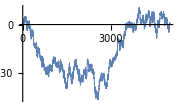

```mathematica
ListLinePlot[offLatticeWalk[5000,1]]
```

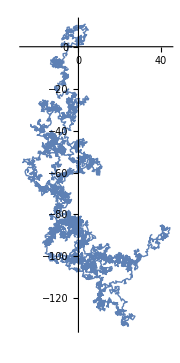

```mathematica
ListLinePlot[offLatticeWalk[5000,2],AspectRatio->Automatic,PlotStyle->Thin]
```

```mathematica
Graphics3D[Line@offLatticeWalk[5000,3]]
```

-Graphics3D-

Here is the function for running bond percolation simulations taken from the exercise. Options are inherited from GridGraph.

```mathematica
Clear[BondPercolation];
```

```mathematica
Options[BondPercolation]=Options[GridGraph];
```

```mathematica
BondPercolation[{m_,n_,prob_},opts:OptionsPattern[]]:=Module[{gg,gr},
gg=GridGraph[{m,n},opts];
gr=Graph[Pick[EdgeList[gg],RandomVariate[BernoulliDistribution[prob],EdgeCount[gg]],1]];HighlightGraph[gg,gr,GraphHighlightStyle->"DehighlightFade"]]
```

```mathematica
BondPercolation[{13,21,.2},VertexSize->.5]
```

-Graphics-

Add a check on the arguments m and n and issue a message if they are not positive integers.

```mathematica
PositiveIntegerQ[n_]:=IntegerQ[n]&&Positive[n]
```

```mathematica
BondPercolation::badargs="The parameters `1` and `2` must be positive integers.";
```

```mathematica
Clear[BondPercolation];
BondPercolation[{m_,n_,prob_},opts:OptionsPattern[]]:=Module[{gg,gr},
If[AllTrue[{m,n},PositiveIntegerQ], 
gg=GridGraph[{m,n},opts];
gr=Graph[Pick[EdgeList[gg],RandomVariate[BernoulliDistribution[prob],EdgeCount[gg]],1]];HighlightGraph[gg,gr,GraphHighlightStyle->"DehighlightFade"],

Message[BondPercolation::badargs,m,n]
]]
```

```mathematica
BondPercolation[{13,17,.2}]
```

-Graphics-

```mathematica
BondPercolation[{-13,17,.2}]
```

BondPercolation::badargs: The parameters -13 and 17 must be positive integers.

Start with the color scheme. This is the Amino scheme used in RasMol. The color swatches can be entered as RGB values and then the swatch can be copied and pasted.

```mathematica
RGBColor[{220/255, 150/255, 130/255}]
```

RGBColor[{Rational[44, 51], Rational[10, 17], Rational[26, 51]}]

```mathematica
Amino={{"P",-Graphics-},{"W",-Graphics-},{"L",-Graphics-},{"V",-Graphics-},{"I",-Graphics-},{"N",-Graphics-},{"Q",-Graphics-},{"S",-Graphics-},{"T",-Graphics-},{"C",-Graphics-},{"M",-Graphics-},{"H",-Graphics-},{"A",-Graphics-},{"G",-Graphics-},{"F",-Graphics-},{"Y",-Graphics-},{"K",-Graphics-},{"R",-Graphics-},{"D",-Graphics-},{"E",-Graphics-}};
```

Set up the options framework. ColorResidues will inherit options from Framed and also have a unique option to select different color schemes. Amino will be the default scheme.

```mathematica
Options[ColorResidues]=Join[{ColorScheme->Amino},Options[Framed]];
```

Write a usage message for ColorResidues.

```mathematica
ColorResidues::usage="ColorResidues[seq] displays a sequence of amino acids from the protein sequence seq.";
```

This creates an auxiliary function that turns the color scheme into a list of rules that will be applied in the ColorResidues function below.

```mathematica
makeAAbox[scheme_,opts:OptionsPattern[]]:=Module[{aa,col},
{aa,col}=Transpose[scheme];MapThread[#1:>Framed[#1,opts,Background->#2,FrameStyle->#2]&,{aa,col}]]
```

```mathematica
makeAAbox[Amino]
```

{P:>P,W:>W,L:>L,V:>V,I:>I,N:>N,Q:>Q,S:>S,T:>T,C:>C,M:>M,H:>H,A:>A,G:>G,F:>F,Y:>Y,K:>K,R:>R,D:>D,E:>E}

Finally, here is the function with the ﬁrst 100 residues of the protein MUC6 as argument.

```mathematica
ColorResidues[str_String,opts:OptionsPattern[]]:=Module[{cs=OptionValue[ColorScheme]},
Row[Characters[str]/.makeAAbox[cs,FilterRules[{opts},Options[Framed]]]]]
```

```mathematica
Map[{#,ProteinData["MUC6",#]}&,{"BiologicalProcesses","Memberships","MolecularFunctions"}]//TableForm
```

BiologicalProcesses | MaintenanceOfGastrointestinalEpithelium
Memberships | ExtracellularMatrixStructuralConstituent
ExtracellularRegion
MaintenanceOfGastrointestinalEpithelium
Proteins
MolecularFunctions | ExtracellularMatrixStructuralConstituent

```mathematica
muc6=StringTake[ProteinData["MUC6","Sequence"],100];
```

```mathematica
ColorResidues[muc6,ColorScheme->Amino,FrameMargins->1]
```

MVQRWLLLSCCGALLSAGLANTSYTSPGLQRLKDSPQTAPDKGQCSTWGAGHFSTFDHHVYDFSGTCNYIFAATCKDAFPTFSVQLRRGPDGSISRIIVE

7
Strings

Exercises: Structure and syntax

Convert the ﬁrst character in a string (which you may assume to be a lowercase letter) to uppercase.

Given a string of digits, for example, "10495", convert it to its integer value.

Create a function UniqueCharacters[str] that takes a string as its argument and returns a list of the unique characters in that string. For example, UniqueCharacters["Mississippi"] should return {M,i,s,p}.

Using a ﬁrst-name database, ﬁnd all names consisting entirely of combinations of the ﬁrst letters on the keys of a typical phone (Figure Chapter.NumberedFigure), that is, names that only contain the letters a, d, g, j, m, p, t, and w; for example, PAT. As a database source, the US Census Bureau curates lists of common names.

Telephone number pad.

A somewhat simplistic cipher, known as the XOR cipher, uses binary eight-bit keys to encode strings. The idea is to ﬁrst convert each letter in a plaintext string to their character code in eight-bit binary. So the letter A, whose character code is 65, is converted into 1000001. A key string, say the letter K, is similarly converted to an eight-bit binary representation. Then each letter in the plaintext is encoded by performing a bit XOR operation on the plaintext letter and the key, both using their eight-bit binary representation. The resulting ciphertext could remain in binary or it could be converted back from character codes to encoded text, the ciphertext.

Create an XOR cipher and encode a plaintext string to produce a ciphertext. See Exercise 6, Section 2.2 for information on converting a string to its binary representation. As an aside, the XOR cipher is a terribly insecure cipher as simply reversing the encoding operations makes it easy to recover the key (Churchhouse 2001).

Solutions

Here is a test string we will use for this exercise.

```mathematica
str="this is a test string"
```

this is a test string

This extracts the ﬁrst character from str.

```mathematica
StringTake[str,1]
```

t

Here is its character code.

```mathematica
ToCharacterCode[%]
```

{116}

For each lowercase letter of the English alphabet, subtracting 32 gives the corresponding uppercase character.

```mathematica
%-32
```

{84}

Convert back to a character.

```mathematica
FromCharacterCode[%]
```

T

Take the original string minus its ﬁrst character.

```mathematica
StringDrop[str,1]
```

his is a test string

Finally, join the previous string with the capital T.

```mathematica
StringJoin[%%,%]
```

This is a test string

You can do this more efficiently using ToUpperCase and StringTake. This approach is more general in that it does not assume that the ﬁrst character in your string is lower case.

```mathematica
ToUpperCase[StringTake[str,1]]
```

T

```mathematica
StringTake[str,2;;-1]
```

his is a test string

```mathematica
ToUpperCase[StringTake[str,1]]<>StringTake[str,2;;-1]
```

This is a test string

This can be done most directly with Capitalize which automatically handles many of the issues discussed above.

```mathematica
Capitalize[str]
```

This is a test string

One approach converts the string to character codes.

```mathematica
ToCharacterCode["10495"]
```

{49,48,52,57,53}

```mathematica
%-48
```

{1,0,4,9,5}

```mathematica
Table[10^j,{j,4,0,-1}]
```

{10000,1000,100,10,1}

```mathematica
%.%%
```

10495

This is a good place to use Fold. Using FoldList, you can see how the expression is built up.

```mathematica
FoldList[#2+10 #1&,0,ToCharacterCode["10495"]-48]
```

{0,1,10,104,1049,10495}

Much more directly, use ToExpression.

```mathematica
ToExpression["10495"]
```

10495

Start by extracting the individual characters in a string.

```mathematica
str="Mississippi";
Characters[str]
```

{M,i,s,s,i,s,s,i,p,p,i}

This gives the set of unique characters in this string.

```mathematica
Union[Characters[str]]
```

{i,M,p,s}

Union sorts the list whereas DeleteDuplicates does not.

```mathematica
DeleteDuplicates[Characters[str]]
```

{M,i,s,p}

Here then is the function.

```mathematica
UniqueCharacters[str_String]:=DeleteDuplicates[Characters[str]]
```

Try it out on a more interesting example.

```mathematica
protein=ProteinData["PP2672"]
```

MKSSEELQCLKQMEEELLFLKAGQGSQRARLTPPLPRALQGNFGAPALCGIWFAEHLHPAVGMPPNYNSSMLSLSPERTILSGGWSGKQTQQPVPPLRTLLLRSPFSLHKSSQPGSPKASQRIHPLFHSIPRSQLHSVLLGLPLLFIQTRPSPPAQYGAQMPLRYICFGPNIFWGSKKPQKE

```mathematica
UniqueCharacters[protein]
```

{M,K,S,E,L,Q,C,F,A,G,R,T,P,N,I,W,H,V,Y}

It even works in the degenerate case.

```mathematica
UniqueCharacters[""]
```

{}

The US Census Bureau curates lists of common ﬁrst and last names. This imports a list of common female ﬁrst names.

```mathematica
data=Import["http://www2.census.gov/topics/genealogy/1990surnames/dist.female.first",{"Table"}];
```

The names themselves are in the ﬁrst column.

```mathematica
names=data[[All,1]];
RandomChoice[names,12]
```

{CARISA,EXIE,MICHELINE,RENEE,BRETT,INA,KATHE,ELYSE,ANDREE,LELIA,THOMASENA,KARRI}

The ﬁrst letters on the keys on the phone pad are the following. We have input them here all uppercase as the names from our database are in that format. You may have to make adjustments to the case (ToUpperCase, ToLowerCase) depending upon your sources.

```mathematica
firstLetters={"A","D","G","J","M","P","T","W"};
```

Here are the letters in one of the names in the database.

```mathematica
nChars=Characters["PAT"]
```

{P,A,T}

This list of letters is a subset of the ﬁrst letters from the phone pad.

```mathematica
SubsetQ[firstLetters,nChars]
```

True

Here then is a predicate that checks if a name consists of letters that are a subset of the phone pad ﬁrst letters.

```mathematica
PhoneNameQ[name_String]:=Module[{nChars,firstLetters={"A","D","G","J","M","P","T","W"}},
nChars=Characters[name];
SubsetQ[firstLetters,nChars]
]
```

```mathematica
PhoneNameQ["PAT"]
```

True

```mathematica
Length[names]
```

4275

```mathematica
lis=Select[names,PhoneNameQ]
```

{ADA,PAM,PAT,MA,MAGDA,JADA,AMADA,AJA,TAM,PA,JA,TAMA,ADAM,TA,JAMA}

First convert a string to binary 8-bit.

```mathematica
text=IntegerDigits[ToCharacterCode["Orange"],2,8]
```

{{0,1,0,0,1,1,1,1},{0,1,1,1,0,0,1,0},{0,1,1,0,0,0,0,1},{0,1,1,0,1,1,1,0},{0,1,1,0,0,1,1,1},{0,1,1,0,0,1,0,1}}

Now we need an 8-bit key to do the encoding. It could be a random sequence of bits or it might be a letter in binary Ascii. For this example, our key will be the binary Ascii code for the letter K.

```mathematica
key=First@IntegerDigits[ToCharacterCode["K"],2,8]
```

{0,1,0,0,1,0,1,1}

Map the BitXor operator with this key across each of the binary representations of the letters in text.

```mathematica
lis=Map[BitXor[#,key]&,text]
```

{{0,0,0,0,0,1,0,0},{0,0,1,1,1,0,0,1},{0,0,1,0,1,0,1,0},{0,0,1,0,0,1,0,1},{0,0,1,0,1,1,0,0},{0,0,1,0,1,1,1,0}}

Convert from binary to the decimal character codes.

```mathematica
Map[FromDigits[#,2]&,lis]
```

{4,57,42,37,44,46}

Convert from character codes to Ascii letters. Although only ﬁve characters appear to be in the ciphertext below, there are in fact six characters; the ﬁrst character is a nonprintable Ascii character with character code 4.

```mathematica
ciphertext=FromCharacterCode[%]
```

.049*%,.

This puts the pieces together in a function.

```mathematica
XorEncode[text_String,key_String]:=Module[{lis,bitText,bitKey},
bitText=IntegerDigits[ToCharacterCode[text],2,8];bitKey=First@IntegerDigits[ToCharacterCode[key],2,8];
lis=Map[BitXor[#,bitKey]&,bitText];
FromCharacterCode[Map[FromDigits[#,2]&,lis]]
]
```

```mathematica
XorEncode["Orange","K"]
```

.049*%,.

Exercises: Operations on strings

Create a function PalindromeQ[str] that returns a value of True if its argument str is a palindrome, that is, if the string str is the same forward and backward. For example, the word refer is a palindrome.

Several dozen words in an English dictionary contain two consecutive double letters: balloon, coffee, succeed, for example. Find all words in the dictionary that contain three consecutive double letters. This puzzle appeared on the Car Talk radio show "(CarTalk 2007)".

Given two strings of equal length, create a function StringTranspose that transposes the characters in the two strings and then joins them into a single string.

```mathematica
StringTranspose["abc","def"]
```

adbecf

The built-in function StringRotateLeft rotates the characters in a string by a speciﬁed amount.

```mathematica
StringRotateLeft["a quark for Muster Mark ",8]
```

for Muster Mark a quark

Perform the same operation without using StringRotateLeft.

Create a function StringPermutations[str] that returns all permutations of the string str. For example:

```mathematica
StringPermutations["ABC"]//InputForm
```

{ABC, ACB, BAC, BCA, CAB, CBA}

Rewrite the function SmarandacheWellin from Exercise 10 of Section 2.3 to instead use strings to construct these numbers. Test your implementation for speed against the function from Section 2.3 that uses numerical functions only.

When developing algorithms that operate on large structures (for example, large systems of equations), it is often helpful to be able to create a set of unique symbols with which to work. Create a function MakeVarList that creates unique symbols. For example:

```mathematica
MakeVarList[x,8]
```

{x1,x2,x3,x4,x5,x6,x7,x8}

```mathematica
MakeVarList[var,{10,15}]
```

{var10,var11,var12,var13,var14,var15}

Create a function StringTally that counts each unique character in a string and returns a list similar to that returned by the built-in Tally function. Include the option IgnoreCase with default value False. When set to True, your function should convert all characters to lowercase before doing the tally.

```mathematica
StringTally["One fish, two fish, red fish, blue fish"]
```

{{O,1},{n,1},{e,3},{ ,7},{f,4},{i,4},{s,4},{h,4},{,,3},{t,1},{w,1},{o,1},{r,1},{d,1},{b,1},{l,1},{u,1}}

```mathematica
StringTally["One fish, two fish, red fish, blue fish",IgnoreCase->True]
```

{{o,2},{n,1},{e,3},{ ,7},{f,4},{i,4},{s,4},{h,4},{,,3},{t,1},{w,1},{r,1},{d,1},{b,1},{l,1},{u,1}}

When done, import a sample text and do a frequency analysis on the letters in that text. Letter frequency analysis can be used to spot transposition ciphers in encoded messages as the frequency of the letters is unchanged in such simple encoding schemes.

Exercise ExerciseItem in Section Chapter.Section asks you to extend this function to include an option to specify if punctuation and digits should be included.

Generalize the Caesar cipher so that it encodes by shifting n places to the right. Include the space character in the alphabet.

A mixed-alphabet cipher is created by ﬁrst writing a keyword followed by the remaining letters of the alphabet and then using this key to encode the text. For example, if the keyword is django, the encoding alphabet would be

```mathematica
"djangobcefhiklmpqrstuvwxyz"
```

So, a is replaced with d, b is replaced with j, c is replaced with a, and so on. As an example, the text

the sheik of araby

would be encoded as

tcg scgeh mo drdjy

Implement this cipher and go one step further to output the ciphertext in blocks of length ﬁve, omitting spaces and punctuation.

Modify the alphabet permutation cipher so that, instead of being based on single letters, it is based on adjacent pairs of letters. The single letter cipher has 26! permutations:

26! =403291461126605635584000000

The adjacent pairs cipher will have 26^2! =1.883707684133810×10^1621 permutations.

Create a function StringPad[str,{n}] that pads the end of a string with n whitespace characters. Then create a second rule StringPad[str,n] that pads the string out to length n. If the input string has length greater than n, issue a warning message. Finally, mirroring the argument structure for the built-in PadLeft, create a third rule StringPad[str,n,m] that pads with n whitespaces at the front and m whitespaces at the end of the string.

Fibonacci words are formed in a similar manner as Fibonacci numbers except, instead of adding the previous two elements, Fibonacci words concatenate the previous two elements "(Knuth 1997)". Starting with the two strings “0” and “01,” create a function FibonacciWord[n] to generate the nth Fibonacci word. This can be generalized to start with any two strings, say “a” and “b.” Fibonacci words are examples of a well-known object from combinatorics, Sturmian words.

In Exercise 8, Section 5.1 a function was created to generate n-grams from a given alphabet. For example, that function could be used to create all bigrams (words of length two) from the nucleotide alphabet {"G","C","A","T"}.

Import a nucleotide sequence such as the human mitochondrial genome hsMito below and then create a histogram (as in Figure Chapter.NumberedFigure) showing the frequency of each of the sixteen possible bigrams AA, AC, AT, etc.

```mathematica
hsMito=First@Import["ExampleData/mitochondrion.fa.gz"]//Short
```

GATCACAGGTCTATCACCCT…CTTAAATAAGACATCACGATG

Distribution of nucleotide words of length two in Homo sapiens mitochondria genome.

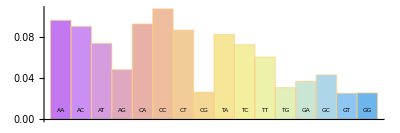

Solutions

Here is the function that checks if a string is a palindrome.

```mathematica
PalindromeQ[str_String]:=StringReverse[str]==str
```

```mathematica
PalindromeQ["mood"]
```

False

```mathematica
PalindromeQ["PoP"]
```

True

Get all words in the dictionary that comes with Mathematica.

```mathematica
words=DictionaryLookup[];
```

Select those that pass the PalindromeQ test.

```mathematica
Select[words,PalindromeQ]
```

{a,aha,aka,bib,bob,boob,bub,CFC,civic,dad,deed,deified,did,dud,DVD,eke,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,mam,MGM,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,redder,refer,repaper,reviver,rotor,sagas,sees,seres,sexes,shahs,sis,solos,SOS,stats,stets,tat,tenet,TNT,toot,tot,tut,wow,WWW}

An argument that is a number can be converted to a string and then the previous rule is called.

```mathematica
PalindromeQ[num_Integer]:=PalindromeQ[ToString[num]]
```

```mathematica
PalindromeQ[12522521]
```

True

First, we get the words in the dictionary.

```mathematica
words=DictionaryLookup[];
```

Here is the string pattern we are looking for: a letter (patten named x) repeated once, followed by a letter (pattern named y) repeated once, followed by another letter repeated (pattern named z). The pattern can be passed directly to DictionaryLookup.

```mathematica
DictionaryLookup[___~~x_~~x_~~y_~~y_~~z_~~z_~~___]
```

{bookkeeper,bookkeepers,bookkeeping}

First, get the characters from the two strings.

```mathematica
With[{str1="abc",str2="def"},
Characters[{str1,str2}]]
```

{{a,b,c},{d,e,f}}

Then perform the transpose on these two lists.

```mathematica
Transpose[%]
```

{{a,d},{b,e},{c,f}}

StringJoin automatically ﬂattens the sublists.

```mathematica
StringJoin[%]
```

adbecf

```mathematica
Clear[StringTranspose];
StringTranspose[str1_,str2_]:=StringJoin[Transpose[Characters[{str1,str2}]]]
```

```mathematica
StringTranspose["abc","def"]
```

adbecf

Transpose will, helpfully, return an error message if the two strings are of unequal length.

```mathematica
StringTranspose["abcd","efg"]
```

Transpose::nmtx: The first two levels of {{"a", "b", "c", "d"}, {"e", "f", "g"}} cannot be transposed.

StringJoin::string: String expected at position 1 in StringJoin[Transpose[{{"a", "b", "c", "d"}, {"e", "f", "g"}}]].

StringJoin[Transpose[{{a,b,c,d},{e,f,g}}]]

Use the argument structure of RotateLeft.

```mathematica
stringRotateLeft[str_,n_:1]:=StringJoin[RotateLeft[Characters[str],n]]
```

```mathematica
stringRotateLeft["squeamish ossifrage"]
```

queamish ossifrages

```mathematica
stringRotateLeft["squeamish ossifrage",5]
```

mish ossifragesquea

Here is a list of the characters in a sample string.

```mathematica
chars=Characters["cold"]
```

{c,o,l,d}

And here are the permutations of this list of characters.

```mathematica
Permutations[%]
```

{{c,o,l,d},{c,o,d,l},{c,l,o,d},{c,l,d,o},{c,d,o,l},{c,d,l,o},{o,c,l,d},{o,c,d,l},{o,l,c,d},{o,l,d,c},{o,d,c,l},{o,d,l,c},{l,c,o,d},{l,c,d,o},{l,o,c,d},{l,o,d,c},{l,d,c,o},{l,d,o,c},{d,c,o,l},{d,c,l,o},{d,o,c,l},{d,o,l,c},{d,l,c,o},{d,l,o,c}}

Finally, join each set of characters with StringJoin.

```mathematica
Map[StringJoin,%]
```

{cold,codl,clod,cldo,cdol,cdlo,ocld,ocdl,olcd,oldc,odcl,odlc,lcod,lcdo,locd,lodc,ldco,ldoc,dcol,dclo,docl,dolc,dlco,dloc}

And here is the function putting these pieces together.

```mathematica
StringPermutations[str_String]:=Map[StringJoin,Permutations[Characters[str]]]
```

```mathematica
StringPermutations["ACGT"]
```

{ACGT,ACTG,AGCT,AGTC,ATCG,ATGC,CAGT,CATG,CGAT,CGTA,CTAG,CTGA,GACT,GATC,GCAT,GCTA,GTAC,GTCA,TACG,TAGC,TCAG,TCGA,TGAC,TGCA}

The approach here, in comparison with that in Exercise 10 in Section 2.3, is to convert the integers to strings and operate on the strings. When done, we convert the string back to an integer. To start, here are the ﬁrst few primes.

```mathematica
Prime[Range[10]]
```

{2,3,5,7,11,13,17,19,23,29}

Convert to strings and then concatenate.

```mathematica
Map[ToString,%]//InputForm
```

{"2", "3", "5", "7", "11", "13", "17", "19", "23", 
 "29"}

```mathematica
StringJoin[%]//InputForm
```

"2357111317192329"

Finally, convert the above string to a number.

```mathematica
ToExpression[%]//InputForm
```

2357111317192329

```mathematica
Prime[Range[12]]
```

{2,3,5,7,11,13,17,19,23,29,31,37}

```mathematica
NumberJoin[{x__}]:=ToExpression[StringJoin[Map[ToString,{x}]]]
```

```mathematica
SmarandacheWellin2[n_Integer?Positive]:=NumberJoin[Prime[Range[n]]]
```

```mathematica
SmarandacheWellin2[10]
```

2357111317192329

Compared with the solution from Section 2.3, the string-based solution is a bit faster, even with all the conversion from numbers to strings and back.

```mathematica
SmarandacheWellin[n_Integer?Positive]:=FromDigits[Flatten[IntegerDigits@Table[Prime[i],{i,n}]]]
```

```mathematica
Timing[SmarandacheWellin[50000];]
```

{0.228937,Null}

```mathematica
Timing[SmarandacheWellin2[50000];]
```

{0.136362,Null}

```mathematica
SmarandacheWellin[50000]==SmarandacheWellin2[50000]
```

True

Although there is a built-in function, Unique, that does this, it has some limitations for this particular task.

```mathematica
Table[Unique["x"],{8}]
```

{x55,x56,x57,x58,x59,x60,x61,x62}

One potential limitation of Unique is that it uses the ﬁrst unused symbol of a particular form. It does this to avoid overwriting existing symbols.

```mathematica
Table[Unique["x"],{8}]
```

{x63,x64,x65,x66,x67,x68,x69,x70}

However, if you want to explicitly create a list of indexed symbols with a set of speciﬁc indices, it is useful to create a different function. First, note that a string can be converted to a symbol using ToExpression or by wrapping the string in Symbol.

```mathematica
Head["x1"]
```

String

```mathematica
ToExpression["x1"]//Head
```

Symbol

```mathematica
Symbol["x1"]//Head
```

Symbol

StringJoin is used to concatenate strings. So, let us concatenate the variable with the index, ﬁrst with one number and then with a range of numbers.

```mathematica
StringJoin["x","8"]//FullForm
```

"x8"

```mathematica
ToExpression[Map["x"<>ToString[#]&,Range[12]]]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12}

Put all the pieces of code together.

```mathematica
MakeVarList[x_Symbol,n_Integer]:=ToExpression[Map[ToString[x]<>ToString[#]&,Range[n]]]
```

Let us create an additional rule for this function that takes a range speciﬁcation as its second argument.

```mathematica
MakeVarList[x_Symbol,{n_Integer,m_Integer}]:=ToExpression[Map[ToString[x]<>ToString[#]&,Range[n,m]]]
```

```mathematica
MakeVarList[tmp,{20,30}]
```

{tmp20,tmp21,tmp22,tmp23,tmp24,tmp25,tmp26,tmp27,tmp28,tmp29,tmp30}

Note that we have not been too careful about argument checking.

```mathematica
MakeVarList[tmp,{-2,2}]
```

{-2+tmp,-1+tmp,tmp0,tmp1,tmp2}

Using a negative index is a problem when the string is converted using ToExpression.

```mathematica
Clear[x]
```

```mathematica
ToString[x]<>ToString[-2]//FullForm
```

"x-2"

```mathematica
ToExpression[%]//FullForm
```

Plus[-2,x]

Argument checking with a different pattern corrects this problem.

```mathematica
Clear[MakeVarList]
```

```mathematica
MakeVarList[x_Symbol,{n_Integer?Positive,m_Integer?Positive}]:=ToExpression[Map[ToString[x]<>ToString[#]&,Range[n,m]]]
```

```mathematica
MakeVarList[tmp,{2,4}]
```

{tmp2,tmp3,tmp4}

Starting with one word, ﬁrst get a list of the characters in the lowercase version of that word:

```mathematica
str="Mississippi";
Characters[ToLowerCase@str]
```

{m,i,s,s,i,s,s,i,p,p,i}

```mathematica
Tally[%]
```

{{m,1},{i,4},{s,4},{p,2}}

```mathematica
StringTally[str_]:=Tally[Characters[ToLowerCase@str]]
```

To try this out on a large text, ﬁrst import Lewis Caroll’s Alice’s Adventures in Wonderland from gutenberg.org.

```mathematica
alice=Import["http://www.gutenberg.org/ebooks/28885.txt.utf-8","Text"];
```

```mathematica
StringTally[alice]//Sort
```

{{!,457},{@,2},{#,1},{%,1},{&,2},{*,48},{(,89},{),89},{_,514},{-,884},{[,41},{],41},{.,1240},{,,2591},{;,198},{",2307},{?,212},{',802},{/,31},{:,277},{
,4045},{ ,31914},{0,27},{1,77},{2,23},{3,22},{4,18},{5,21},{6,16},{7,9},{8,31},{9,16},{a,10191},{b,1806},{c,3114},{d,5678},{e,15877},{f,2446},{g,3029},{h,8102},{i,8949},{j,238},{k,1314},{l,5456},{m,2546},{n,8358},{o,9775},{p,2051},{q,237},{r,6881},{s,7498},{t,12637},{u,4134},{ù,1},{v,1000},{w,3049},{x,185},{y,2672},{z,79},{$,2},{·,13}}

Let’s sort on the characters, the ﬁrst element in each sublist; then take the twenty-six pairs that give the Ascii letter tallies.

```mathematica
counts=Take[Sort[StringTally[alice]],-29;;-3]
```

{{a,10191},{b,1806},{c,3114},{d,5678},{e,15877},{f,2446},{g,3029},{h,8102},{i,8949},{j,238},{k,1314},{l,5456},{m,2546},{n,8358},{o,9775},{p,2051},{q,237},{r,6881},{s,7498},{t,12637},{u,4134},{ù,1},{v,1000},{w,3049},{x,185},{y,2672},{z,79}}

Here is a bar chart of the tallies for each of these letters.

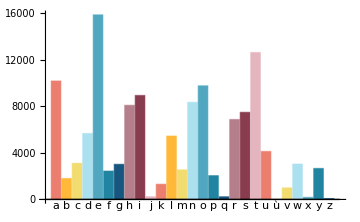

```mathematica
BarChart[counts⟦All,2⟧,ChartLabels->counts⟦All,1⟧,ChartStyle->24]
```

This is a simple modiﬁcation of the code given in the text. But ﬁrst we add the space character to the alphabet.

```mathematica
ToCharacterCode[" "]
```

{32}

```mathematica
alphabet = Join[{FromCharacterCode[32]},CharacterRange["a","z"]]
```

{ ,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Giving coderules an argument n will allow you to shift an arbitrary number of places. We give n a default value of 1 so that omitting the argument will default to the value n=1.

```mathematica
coderules[n_:1]:=Thread[alphabet->RotateRight[alphabet,n]]
```

```mathematica
decoderules[n_]:=Map[Reverse,coderules[n]]
```

```mathematica
code[str_String,n_]:=Apply[StringJoin,Characters[str]/.coderules[n]]
```

```mathematica
decode[str_String,n_]:=Apply[StringJoin,Characters[str]/.decoderules[n]]
```

```mathematica
code["squeamish ossifrage",5]
```

nlp whdncvjnndamwb

```mathematica
decode[%,5]
```

squeamish ossifrage

First, here is the list of characters from the plaintext alphabet.

```mathematica
PlainAlphabet=CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Here is our key, django:

```mathematica
key="django"
```

django

And here is the cipher text alphabet, prepending the key:

```mathematica
StringJoin[Characters@key,Complement[PlainAlphabet,Characters@key]]
```

djangobcefhiklmpqrstuvwxyz

Make a reusable function.

```mathematica
CipherAlphabet[key_String]:=With[{k=Characters[key]},
StringJoin[k,Complement[CharacterRange["a","z"],k]]]
```

Generate the coding rules:

```mathematica
codeRules=Thread[PlainAlphabet->Characters@CipherAlphabet["django"]]
```

{a→d,b→j,c→a,d→n,e→g,f→o,g→b,h→c,i→e,j→f,k→h,l→i,m→k,n→l,o→m,p→p,q→q,r→r,s→s,t→t,u→u,v→v,w→w,x→x,y→y,z→z}

The encoding function follows that in the text of this section.

```mathematica
encode[str_String]:=StringJoin[Characters[str]/.codeRules]
```

```mathematica
encode["the sheik of araby"]
```

tcg scgeh mo drdjy

Omit spaces and punctuation and output in blocks of length 5 (using stringPartition from Section 7.5).

```mathematica
stringPartition[str_String,seq__]:=Map[StringJoin,Partition[Characters[str],seq]]
```

```mathematica
StringSplit[encode["the sheik of araby"],RegularExpression["\\W+"]]
```

{tcg,scgeh,mo,drdjy}

```mathematica
StringJoin[Riffle[stringPartition[StringJoin[%],5,5,1,""]," "]]
```

tcgsc gehmo drdjy

Finally, this puts all these pieces together.

```mathematica
Clear[encode];
encode[str_String,key_String,blocksize_:5]:=Module[{CipherAlphabet,codeRules,s1,s2,s3},
CipherAlphabet[k_]:=
StringJoin[Characters[k],Complement[CharacterRange["a","z"],Characters[k]]];

codeRules=Thread[CharacterRange["a","z"]->Characters@CipherAlphabet[key]];

s1=StringJoin[Characters[str]/.codeRules];
s2=StringSplit[s1,RegularExpression["\\W+"]];
s3=stringPartition[StringJoin[s2],blocksize,blocksize,1,""];
StringJoin[Riffle[s3," "]]]
```

```mathematica
encode["the sheik of araby","django",3]
```

tcg scg ehm odr djy

(* solution to appear *)

First, using StringJoin, put n spaces at the end of the string.

```mathematica
StringPad[str_String,{n_}]:=StringJoin[str,Table[" ",{n}]]
```

```mathematica
StringPad["ciao",{5}]//FullForm
```

"ciao     "

For the second rule, ﬁrst create a message that will be issued if the string is longer than the pad length, n.

```mathematica
StringPad::badlen="Pad length `1` must be greater than the length of string `2`.";
```

```mathematica
StringPad[str_String,n_]:=With[{len=StringLength[str]},If[len>n,Message[StringPad::badlen,n,str],StringPad[str,{n-len}]]]
```

```mathematica
StringPad["ciao",8]//FullForm
```

"ciao    "

```mathematica
StringPad["ciao",3]
```

StringPad::badlen: Pad length 3 must be greater than the length of string "ciao".

Finally, here is a rule for padding at the beginning and end of the string.

```mathematica
StringPad[str_String,n_,m_]:=StringJoin[Table[" ",{n}],str,Table[" ",{m}]]
```

```mathematica
StringPad["ciao",3,8]//FullForm
```

"   ciao        "

Note, StringInsert could also be used.

```mathematica
StringInsert["ciao"," ",{1,-1}]//FullForm
```

" ciao "

```mathematica
StringPad2[str_String,n_,m_]:=StringInsert[str," ",Join[Table[1,{n}],Table[-1,{m}]]]
```

```mathematica
StringPad2["ciao",3,8]//FullForm
```

"   ciao        "

The deﬁnition looks very similar to that for Fibonacci numbers except that the ﬁrst two values are strings and the operation is string concatenation (StringJoin).

```mathematica
FibonacciWord[1]="0";
FibonacciWord[2]="01";
```

```mathematica
FibonacciWord[n_]:=FibonacciWord[n-1]<>FibonacciWord[n-2]
```

```mathematica
FibonacciWord[12]
```

01001010010010100101001001010010010100101001001010010100100101001001010010100100101001001010010100100101001010010010100100101001010010010100101001001010010010100101001001010010010100101001001010010100100101001001010010100100101001001

There lots of interesting things that you can discover regarding Fibonacci words.

```mathematica
Table[StringCount[FibonacciWord[i],"1"],{i,1,15}]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377}

If you were generating very large Fibonacci words, it would be advisable to use dynamic programming as described in Section 5.3 to reduce the scope of the recursion.

Start by importing the example FASTA ﬁle containing the mitochondrial human genome sequence.

```mathematica
hsMito=First@Import["ExampleData/mitochondrion.fa.gz"];
```

Here is the NGrams function:

```mathematica
NGrams[alphabet:{__String},n_Integer?Positive]:=Flatten[Outer[StringJoin,Apply[Sequence,Table[alphabet,{n}]]]]
```

This gives all possible bigrams from the DNA alphabet.

```mathematica
bigrams=NGrams[{"A","T","G","C"},2]
```

{AA,AT,AG,AC,TA,TT,TG,TC,GA,GT,GG,GC,CA,CT,CG,CC}

This ﬁnds all the above bigrams in the sequence.

```mathematica
data=StringCases[hsMito,Alternatives@@bigrams,Overlaps->True];
```

```mathematica
RandomSample[data,12]
```

{TC,CC,GG,GG,AT,CC,AC,CT,CC,AC,AA,TC}

And here is the histogram plot.

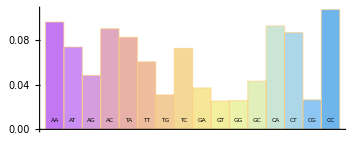

```mathematica
Histogram[data/.Thread[bigrams->Range[Length[bigrams]]],Automatic,"PDF",ChartLabels->{None,Placed[Style[#,"SR",6]&/@bigrams,Bottom]},Ticks->{None,Automatic},AspectRatio->.4,ChartStyle->"Pastel"]
```

Exercises: String patterns

Given a list of words, some of which start with uppercase characters, convert them all to words in which the ﬁrst character is lowercase. You can use the words in the dictionary as a good sample set.

Create a function Palindromes[n] that ﬁnds all palindromic words of length n in the dictionary. For example, kayak is a ﬁve-letter palindrome.

Modify the listSort function from Section 4.3 by creating another rule that can be used to sort lists of string characters.

Find the number of unique words in a body of text such as Alice in Wonderland. This text can be imported from ExampleData:

```mathematica
ExampleData[{"Text","AliceInWonderland"}];
```

After splitting the text into words, convert all uppercase characters to lowercase so that you count words such as hare and Hare as the same word.

Another important task in computational linguistics is comparing the complexity of text-based materials such as newspapers or school texts. There are many measures that you might use: the length of the text, average sentence length, levels of reasoning required, word frequency, and many more. One metric is word length. Use the built-in function TextWords (new in Mathematica 10.1) to generate a histogram like that in Figure Chapter.NumberedFigure showing the word-length distribution for a text.

Word-length distribution for Alice in Wonderland.

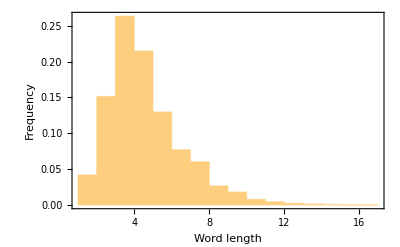

Then compare the word-length distribution for several different text sources such as those available in ExampleData["Text"] or on gutenberg.org.

Repeat Exercise ExerciseItem but use sentence length instead of word length as the measure.

Semordnilaps (“palindromes” spelled backwards) are words that, when reversed, also spell a word. For example, live and stressed are semordnilaps because reversed, they still spell words: evil and desserts. Find all semordnilaps in the dictionary.

Solutions

We will work with a small sample of words from the dictionary.

```mathematica
SeedRandom[0];
words=DictionaryLookup[];
sample=RandomSample[words,12]
```

{unaccustomed,Godhead,Jutland,dilated,observe,matchplay,wintergreen,clans,hobgoblin,rampantly,disinheriting,performances}

StringReplace operates on any words that match the pattern and leave those that do not match unchanged.

```mathematica
StringReplace[sample,f_?UpperCaseQ~~r___:>ToLowerCase[f]~~r]
```

{unaccustomed,godhead,jutland,dilated,observe,matchplay,wintergreen,clans,hobgoblin,rampantly,disinheriting,performances}

But there is a function built in that does this directly.

```mathematica
?Decapitalize
```

RowBox[{"Decapitalize", "[", "string", "]"}] yields a string in which the first character has been made lower case.

```mathematica
Decapitalize[sample]
```

{unaccustomed,godhead,jutland,dilated,observe,matchplay,wintergreen,clans,hobgoblin,rampantly,disinheriting,performances}

You can do a dictionary lookup with a pattern that tests whether the word is palindromic. Then ﬁnd all palindromic words of a given length. Note the need for BlankSequence (__) as the simple pattern _ would only ﬁnd words consisting of one character.

```mathematica
Palindromes[len_Integer]:=DictionaryLookup[w__/;(w==StringReverse[w] && StringLength[w]==len)]
```

We also add a rule to return all palindromes of any length.

```mathematica
Palindromes[]:=DictionaryLookup[w__/;(w==StringReverse[w] )]
```

```mathematica
Palindromes[7]
```

{deified,repaper,reviver}

```mathematica
Palindromes[]
```

{a,aha,aka,bib,bob,boob,bub,CFC,civic,dad,deed,deified,did,dud,DVD,eke,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,mam,MGM,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,redder,refer,repaper,reviver,rotor,sagas,sees,seres,sexes,shahs,sis,solos,SOS,stats,stets,tat,tenet,TNT,toot,tot,tut,wow,WWW}

A simple change to the rule from Section 4.3 will allow for lists of string characters. Here we just add a rule to the original rule for sorting lists of numbers. As written, this only works for lists of lowercase letters.

```mathematica
listSort={
{x___,a_?StringQ,b_?StringQ,y___}:>{x,b,a,y}/;First[ToCharacterCode[b]]<First[ToCharacterCode[a]],
{x___,a_?NumericQ,b_?NumericQ,y___}:>{x,b,a,y}/;b<a
};
```

```mathematica
{82,5,29,98,98,43,90,11,52,46,38,48}//.listSort
```

{5,11,29,38,43,46,48,52,82,90,98,98}

```mathematica
RandomSample@CharacterRange["a","z"]
```

{h,t,x,b,v,g,n,w,s,m,k,o,f,l,i,y,q,c,a,p,e,j,u,r,d,z}

```mathematica
strList={"i","w","z","p","a","s","n","l","h","q","r","d","c","f","o","y","j","u","x","t","m","b","g","e","k","v"};
```

```mathematica
strList//.listSort
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

First import some sample text.

```mathematica
text=ExampleData[{"Text","AliceInWonderland"}];
```

To split into words, use a similar construction to that in this section.

```mathematica
words=StringSplit[text,Characters[":;\"',.?/\-` *"]..];
Short[words,4]
```

{I,DOWN,THE,RABBIT,HOLE,Alice,was,beginning,to,get,very,«9949»,as,well,she,might,what,a,wonderful,dream,it,had,been}

Get the total number of (nonunique) words.

```mathematica
Length[words]
```

9971

Convert uppercase to lowercase.

```mathematica
lcwords=ToLowerCase[words];
Short[lcwords,4]
```

{i,down,the,rabbit,hole,alice,was,beginning,to,get,very,«9949»,as,well,she,might,what,a,wonderful,dream,it,had,been}

Finally, count the number of unique words.

```mathematica
DeleteDuplicates[lcwords]//Length
```

1643

In fact, splitting words using a list of characters as we have done here is not terribly robust. A better approach uses regular expressions (introduced in Section 7.4):

```mathematica
words=StringSplit[text,RegularExpression["\\W+"]];
Length[words]
```

9969

```mathematica
lcwords=StringReplace[words,RegularExpression["([A-Z])"]:>ToLowerCase["$1"]];
DeleteDuplicates[lcwords]//Length
```

1528

Using TextWords, this can be done directly, although the count is a bit different due to slightly different assumptions between what we used in StringSplit and what TextWords assumes.

```mathematica
words=DeleteDuplicates@ToLowerCase[TextWords[text]];
Length[words]
```

1549

We will work with the following text: A Portrait of the Artist as a Young Man, by James Joyce (available at "Project Gutenberg"). We use TextWords to get a list of the words and then use StringLength on these words to get the distribution of word lengths.

Some postprocessing with Stringtake is needed to remove metadata at the beginning and at the end of the ﬁle.

```mathematica
joyce=StringTake[Import["http://www.gutenberg.org/cache/epub/4217/pg4217.txt","Text"],688;;-18843];
StringTake[joyce,{74,164}]
```

as animum dimittit in artes."
Ovid, Metamorphoses, VIII., 18._
</p>

Chapter 1


Once upon

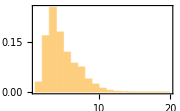

```mathematica
words=TextWords[joyce];
Histogram[StringLength[words],Automatic,"PDF",Frame->True,FrameLabel->{"Word length","Frequency"},FrameTicks->{{Automatic,None},{Automatic,None}}]
```

Here we use TextSentences to split the text into discrete sentences and then map WordCount over the list of sentences.

```mathematica
sentences=TextSentences[joyce];
```

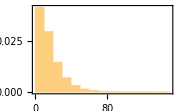

```mathematica
Histogram[Map[WordCount,sentences],Automatic,"PDF",
Frame->True,FrameLabel->{"Sentence length","Frequency"},FrameTicks->{{Automatic,None},{Automatic,None}}]
```

First, here is a list of all words in the dictionary.

```mathematica
words=DictionaryLookup[__];
```

And this reverses those words.

```mathematica
revwords=StringReverse[words];
RandomSample[revwords,12]
```

{gniniatniam,ezilaitini,ecilprus,etadrohc,sriahchsup,aerdnA,srepod,dedrof,eimmiJ,decudorper,dnuorgwohs,straehteews}

Finally, here are all those reversed words that are in the dictionary.

```mathematica
Intersection[words,revwords]
```

{a,abut,agar,ah,aha,aka,am,animal,are,at,ate,auks,avid,bad,bag,ban,bard,bat,bats,bed,bib,bin,bob,bod,bog,bonk,boob,boy,brag,bub,bud,bun,buns,bur,burg,bus,but,buts,cam,CFC,civic,cod,dab,dad,dag,dam,dart,deb,debut,decaf,decal,deed,deem,deep,deeps,deer,deffer,deified,deliver,denier,denies,denim,deres,desserts,devil,dew,dial,dialer,diaper,did,dim,diva,dob,doc,dog,don,doom,door,dos,drab,draw,drawer,draws,dray,dual,dub,dud,DVD,edit,eel,eh,eke,em,emir,emit,er,era,ere,ergo,eta,etas,eve,evil,eviler,ewe,eye,faced,fer,fires,flog,flow,gab,gad,gag,gal,gals,gar,garb,gas,gel,gem,gig,girt,gnat,gnus,gob,god,golf,got,grub,gulp,gulper,gum,gums,guns,gut,ha,hap,he,ho,hoop,huh,I,it,jar,kayak,keel,keels,keep,knits,knob,know,KO,kook,laced,lag,lager,laid,lair,lamina,lap,laud,lee,leek,leer,leg,leper,level,lever,liar,lit,live,lived,loop,loops,loot,looter,loots,lop,ma,ma'am,mac,macs,mad,madam,mam,maps,mar,mart,mat,maws,may,me,meed,meet,meg,MGM,mid,mils,mined,minim,mom,mood,moor,mop,mot,mu,mug,mum,nab,nan,nap,naps,net,new,nib,nip,nips,nit,no,nod,non,noon,not,now,nub,nun,nus,nut,nuts,ogre,oh,oho,OK,on,oohs,pacer,pah,pal,pals,pan,pans,pap,par,part,parts,pas,pat,paws,pay,peed,peek,peels,peep,pees,pep,per,perts,pets,pin,pins,pip,pis,pit,plug,pol,pols,pom,pooh,pool,pools,poop,pop,ports,pot,pots,prat,pup,pus,radar,rag,raga,rail,raj,ram,rap,raps,rat,rats,raw,re,rebut,recap,recaps,redder,redraw,reed,reel,ref,refer,reffed,regal,reined,relaid,relive,remit,rennet,rep,repaid,repaper,repel,replug,retool,retros,revel,reviled,reviver,reward,rial,rime,rood,room,rot,rotor,rub,sag,sagas,sap,saps,sate,saw,scam,seep,sees,seined,sered,seres,serif,sexes,shahs,shoo,sip,sis,six,skua,slag,slap,sleek,sleep,sleets,slim,sloop,sloops,slop,smart,smug,smut,snap,snaps,snip,snips,snit,snoops,snot,snub,snug,sod,solos,sorter,SOS,spacer,spam,span,spans,spar,spas,spat,spay,speed,spin,spins,spit,spool,spools,spoons,sports,spot,spots,sprat,stab,star,stats,steels,step,stets,stew,stink,stool,stop,stops,stows,strap,straw,strep,stressed,strop,strops,stub,stun,sub,sun,sung,sup,swam,swap,sward,sway,swot,swots,ta,tab,tam,tang,tap,taps,tar,tarp,tarps,tat,teem,ten,tenet,tenner,ti,tide,til,time,timer,tin,tins,tip,tips,TNT,tog,tom,ton,tons,tool,toot,top,tops,tor,tort,tot,tow,tows,trad,tram,trams,trap,trig,trot,trow,tub,tuba,tubed,tuber,tug,tums,tun,tut,um,war,ward,warder,warts,was,way,wed,wen,wets,wolf,won,wonk,wort,wot,wow,WWW,xis,yam,yap,yaps,yard,yaw,yaws,yob}

A word of warning: if you tried to do this by comparing every word in the dictionary with every reversed word in the dictionary, the number of comparisons would be extremely large and bog down the computation.

```mathematica
TimeConstrained[
DictionaryLookup[word__/;MemberQ[words,StringReverse[word]]],
20]
```

$Aborted

Exercises: Regular expressions

Use regular expressions to count the occurrences of the vowels (a, e, i, o, u) in the following text:

```mathematica
text="How many vowels do I have?";
```

Using regular expressions, ﬁnd all words in the text Alice in Wonderland that contain the letter q. Then ﬁnd all words that contain either q or Q. The text can be imported with the following:

```mathematica
words=TextWords[ExampleData[{"Text","AliceInWonderland"}]];
Take[words,11]
```

{I,DOWN,THE,RABBIT-HOLE,Alice,was,beginning,to,get,very,tired}

Rewrite the genomic example in Section Chapter.Section to use regular expressions instead of string patterns to ﬁnd all occurrences of the sequence AAanythingT. Here is the example using general string patterns:

```mathematica
gene=GenomeData["IGHV357"];
StringCases[gene,"AA"~~_~~"T"]
```

{AAGT,AAGT,AAAT,AAGT,AAAT,AAAT}

Rewrite the web page example in Section Chapter.Section to use regular expressions to ﬁnd all phone numbers on the page, that is, expressions of the form nnn-nnn-nnnn. Modify accordingly for other web pages and phone numbers formatted for other regions.

Use a regular expression to ﬁnd all words given by DictionaryLookup that consist only of the letters a, e, i, o, u, and y in any order with any number of repetitions of the letters.

Use regular expressions to rewrite the solution to Exercise ExerciseItem in Section Chapter.Section to ﬁnd all words containing three double letter repeats in a row.

The basic rules for pluralizing words in the English language are roughly, as follows: if a noun ends in ch, s, sh, j, x, or z, it is made plural by adding es to the end. If the noun ends in y and is preceded by a consonant, replace the y with ies. If the word ends in ium, replace with ia "(The Chicago Manual of Style 2010)". Of course, there are many more rules and even more exceptions, but you can implement a basic set of rules to convert singular words to plural based on these rules and then try them out on the following list of words:

```mathematica
words={"building","finch","fix","ratio","envy","boy","baby","faculty","honorarium"};
```

A common task in transcribing audio is cleaning up text, removing certain phrases such as um, er, and so on, and other tags that are used to make a note of some sort. For example, the following transcription of a lecture from the University of Warwick, Centre for Applied Linguistics "(Base Corpus)" contains quite a few fragments that should be removed, including newline characters, parenthetical remarks, and nonwords. Use StringReplace with the appropriate rules to clean this text and then apply your code to a larger corpus.

```mathematica
text="okay well er today we're er going to be carrying on with the er French \nRevolution you may have noticed i was sort of getting rather er enthusiastic \nand carried away at the end of the last one i was sort of almost er like i sort \nof started at the beginning about someone standing on a coffee table and s-, \nshouting to arms citizens as if i was going to sort of leap up on the desk and \nsay to arms let's storm the Rootes Social Building [laughter] or er let's go \nout arm in arm singing the Marseillaise or something er like that";
```

Modify the solution to Exercise ExerciseItem in Section Chapter.Section so that StringTally includes an option IncludeCharacters that, by default, has value LetterCharacters, which should mean that StringTally only tallies letters; that is, excludes non-letter characters from the tally. Other values for IncludeCharacters could be All (include all characters in the tally), WordCharacters (include only word characters), PunctuationOnly (include only punctuation).

In web searches and certain problems in natural language processing, it is often useful to ﬁlter out certain words prior to performing a search or processing of text to help with the performance of the algorithms. Words such as and, the, and is are commonly referred to as stop words for this purpose. Lists of stop words are almost always created manually based on the constraints of a particular application. Sample lists of stop words are also commonly available across the Internet. For our purposes here, we will use one such list included with the materials for this book.

```mathematica
stopwords=Rest@Import["StopWords.dat","List"];
RandomSample[stopwords,12]
```

{who'll,recently,ninety,be,no,taking,isn't,unless,what,soon,name,beside}

Using the above list of stop words, or any other that you are interested in, ﬁrst ﬁlter some sample “search phrases” and then remove all stop words from a larger piece of text. If your function was called FilterText, it might work like this:

```mathematica
searchPhrases={"Find my favorite phone","How deep is the ocean?","What is the meaning of life?"};
```

```mathematica
Map[FilterText[#,stopwords]&,searchPhrases]
```

{{Find,favorite,phone},{deep,ocean},{meaning,life}}

Modify the previous exercise so that the user can supply a list of punctuation in addition to the list of stop words to be used to ﬁlter the text.

Solutions

Here is the short piece of text.

```mathematica
text="How many vowels do I have?";
```

The regular expression [aeiou] is matched by any of the vowels.

```mathematica
StringCount[text,RegularExpression["[aeiou]"]]
```

7

First, get a list of the words in the text Alice in Wonderland.

```mathematica
words=TextWords[ExampleData[{"Text","AliceInWonderland"}]];
```

The regular expression ".+q.+" is matched by strings starting with some number (possibly zero) of characters, followed by an explicit q, followed by some number of characters. Flatten is needed to remove the empty lists that are returned for each nonmatch of the pattern.

```mathematica
Flatten@StringCases[words,RegularExpression[".*q.*"]]
```

{quite,quite,quite,queer,question,inquisitively,Conqueror,quiver,quite,quiet,quite,quite,quite,queer-looking,question,quite,Conqueror,conquest,question,question,quite,question,quite,quicker,quite,quite,quite,squeaking,quite,question,quietly,quite,croquet,croquet,question,quite,croquet,queer-shaped,quite,quietly,croquet,croquet,question,croquet-ground,croquet,quarrelling,quarrel,croqueting,croquet-ground,quarreling,quite,quite}

Simply replacing q with the alternative (q|Q) gets all occurrences of q either lowercase or uppercase.

```mathematica
Flatten@StringCases[words,RegularExpression[".*(q|Q).*"]]
```

{quite,quite,quite,queer,question,inquisitively,Conqueror,quiver,quite,quiet,quite,quite,quite,queer-looking,question,quite,Conqueror,conquest,question,question,quite,question,quite,quicker,Quick,quite,quite,quite,squeaking,quite,question,quietly,quite,Queen,croquet,Queen,croquet,question,quite,croquet,Queen,queer-shaped,quite,quietly,croquet,Queen,QUEEN'S,CROQUET,Queen,Queen,Queen,Queen,Queens,QUEEN,Queen,croquet,Queen,question,Queen,Queen's,Queen,croquet-ground,croquet,quarrelling,Queen,quarrel,Queen,croqueting,Queen,Queen,Queen,croquet-ground,Queen,quarreling,Queen,Queen,quite,Queen,Queen,quite,Queen,Queen,Queen,Queen,Queen}

The pattern used earlier in the chapter was "AA"~~_~~"T". In a regular expression, we want the character A repeated exactly once. Use the expression "A{2,2}" for this. The regular expression "." stands for any character.

```mathematica
gene=GenomeData["IGHV357"];
```

```mathematica
StringCases[gene,RegularExpression["A{2,2}.T"]]
```

{AAGT,AAGT,AAAT,AAGT,AAAT,AAAT}

First, read in the web page.

```mathematica
webpage=Import["http://www.wolfram.com/company/contact.cgi","HTML"];
```

In the original example in Section 7.3, we used the pattern NumberString, to represent arbitrary strings of numbers. The regular expression "\d+" accomplishes a similar thing but it will also match strings of numbers that may not be in a phone number format (try it!). Instead, use "\d{3}" to match a list of exactly three digits, and so on.

```mathematica
StringCases[webpage,
RegularExpression["\\d{3}.\\d{3}.\\d{4}"]]//DeleteDuplicates
```

{217-398-0700,217-398-0747,617-764-0094}

The ﬁrst solution uses regular expressions. The second uses string patterns and alternatives.

```mathematica
DictionaryLookup[RegularExpression["[aeiouy]+"],IgnoreCase->True]
```

{a,aye,eye,I,IOU,oi,ya,ye,yea,yo,you}

```mathematica
DictionaryLookup[("a"|"e"|"i"|"o"|"u"|"y")..,IgnoreCase->True]
```

{a,aye,eye,I,IOU,oi,ya,ye,yea,yo,you}

This one is a bit tricky and requires the use of named string patterns. So in the following, \\n refers to the immediately preceding pattern (.). It is important to name each pattern differently so they can be matched by different characters.

```mathematica
words=DictionaryLookup[];
```

```mathematica
StringCases[words,RegularExpression["\\w*(.)\\1(.)\\2(.)\\3\\w*"]]//Flatten
```

{bookkeeper,bookkeepers,bookkeeping}

See the built-in tutorial RegularExpressions for more information on named string patterns.

Here is the short list of words with which we will work.

```mathematica
words={"building","finch","fix","ratio","envy","boy","baby","faculty","honorarium"};
```

Using regular expressions, these rules encapsulate those given in the exercise.

```mathematica
rules={
(RegularExpression["(\\w+)x"]:>"$1"~~"x"~~"es"),
(RegularExpression["(\\w+)(ch)"]:>"$1"~~"$2"~~"es"),
(RegularExpression["(\\w+)([aeiou])(y)"]:>"$1"~~"$2"~~"$3"~~"s"),
(RegularExpression["(\\w+)(y)"]:>"$1"~~"ies"),
(RegularExpression["(\\w+)(i)um"]:>"$1"~~"$2"~~"a"),
(RegularExpression["(\\w+)(.)"]:>"$1"~~"$2"~~"s")
};
```

```mathematica
StringReplace[words,rules]
```

{buildings,finches,fixes,ratios,envies,boys,babies,faculties,honoraria}

Of course, lots of exceptions exist:

```mathematica
StringReplace[{"man","cattle"},rules]
```

{mans,cattles}

Check against the built-in function Pluralize:

```mathematica
Map[Pluralize,words]
```

Pluralize::noplural: No valid English pluralization found for "honorarium".

{buildings,finches,fixes,ratios,envies,boys,babies,faculties,honorarium}

We use a combination of string patterns and regular expressions to remove the various fragments. The regular expression "\[.+\] " matches strings that start with [, followed by an arbitrary number of characters, followed by ], followed by a space. Because brackets are used in regular expressions to denote sequences of characters, you need to escape them to refer to the explicit characters [ or ].

```mathematica
text="okay well er today we're er going to be carrying on with the er French \nRevolution you may have noticed i was sort of getting rather er enthusiastic \nand carried away at the end of the last one i was sort of almost er like i sort \nof started at the beginning about someone standing on a coffee table and s-, \nshouting to arms citizens as if i was going to sort of leap up on the desk and \nsay to arms let's storm the Rootes Social Building [laughter] or er let's go \nout arm in arm singing the Marseillaise or something er like that";
```

```mathematica
StringReplace[text,{"\n"->""," er"->""," s-"->"",RegularExpression["\[.+\] "]->""}]
```

okay well today we're going to be carrying on with the French Revolution you may have noticed i was sort of getting rather enthusiastic and carried away at the end of the last one i was sort of almost like i sort of started at the beginning about someone standing on a coffee table and, shouting to arms citizens as if i was going to sort of leap up on the desk and say to arms let's storm the Rootes Social Building or let's go out arm in arm singing the Marseillaise or something like that

Start by setting the options framework.

```mathematica
Clear[StringTally]
```

```mathematica
Options[StringTally]={IncludeCharacters->LetterCharacters};
```

Set up a message that will be returned if the user speciﬁes a bad value for the IncludeCharacters option.

```mathematica
StringTally::badopt="The option value `1` can only take on the following values: All, LetterCharacters, WordCharacters, PunctuationOnly.";
```

Here then is the rewritten function.

```mathematica
StringTally[txt_,OptionsPattern[]]:=Module[{ic=OptionValue[IncludeCharacters]},
Tally[StringCases[txt,
Which[
ic===All,RegularExpression["."],
ic===LetterCharacters,RegularExpression["[[:alpha:]]"],
ic===WordCharacters,RegularExpression["\\w"],
ic===PunctuationOnly,RegularExpression["\\W"],
True,Message[StringTally::badopt,ic]
]]]]
```

Import Dostoyevsky’s Crime and Punishment which has quite a few non-Ascii characters.

```mathematica
text=Import["http://www.gutenberg.org/ebooks/2554.txt.utf-8","Text"];
```

```mathematica
StringTally[text,IncludeCharacters->WordCharacters]//Sort
```

{{_,506},{0,21},{1,66},{2,16},{3,13},{4,18},{5,25},{6,10},{7,8},{8,19},{9,12},{a,71960},{æ,4},{à,2},{ä,2},{A,2086},{b,11365},{B,919},{c,18602},{ç,1},{C,276},{d,38452},{D,762},{e,104695},{é,17},{è,1},{ê,3},{E,331},{f,16891},{F,316},{g,17969},{G,433},{h,54070},{H,1943},{i,56803},{î,1},{ï,222},{I,5846},{j,773},{J,66},{k,9437},{K,323},{l,35271},{L,580},{m,21968},{M,504},{n,62470},{N,686},{o,71737},{ô,4},{O,496},{p,12583},{P,1415},{q,766},{Q,22},{r,46718},{R,1776},{s,51775},{S,1743},{t,78967},{T,1864},{u,27687},{ü,1},{U,94},{v,11012},{V,100},{w,19588},{W,1407},{x,1322},{X,9},{y,20389},{Y,899},{z,894},{Z,194}}

First read in some sample phrases to prototype.

```mathematica
searchPhrases={"Find my favorite phone","How deep is the ocean?","What is the meaning of life?"};
```

There are several ways to approach this problem. We will break it up into two steps: ﬁrst eliminating punctuation, then a sample set of stop words.

```mathematica
tmp=StringSplit["How deep is the ocean?",Characters[":,;.!? "]..]
```

{How,deep,is,the,ocean}

```mathematica
stopwords={"how","the","is","an"};
```

```mathematica
Apply[Alternatives,stopwords]
```

how|the|is|an

Note the need for WordBoundary in what follows; otherwise, ocean would be split leaving oce because an is a stop word.

```mathematica
StringSplit[tmp,WordBoundary~~Apply[Alternatives,stopwords]~~WordBoundary,IgnoreCase->True]//Flatten
```

{deep,ocean}

```mathematica
FilterText[str_String,stopwords_List]:=Module[{tmp},
tmp=StringSplit[str,Characters[":,;.!? "]..];
Flatten@StringSplit[tmp,WordBoundary~~Apply[Alternatives,stopwords]~~WordBoundary,IgnoreCase->True]
]
```

```mathematica
stopwords=Rest@Import["StopWords.dat","List"];
```

```mathematica
FilterText["What is the meaning of life?",stopwords]
```

{meaning,life}

A slight modiﬁcation is needed to accept a list of punctuation.

```mathematica
Characters@StringJoin[{".","?"}]//FullForm
```

List[".","?"]

First remove the punctuation.

```mathematica
tmp=StringSplit["What is the meaning of life?",Characters@StringJoin[{".","?"}]..]
```

{What is the meaning of life}

Split into words.

```mathematica
First@StringCases[tmp,RegularExpression["\\w+"]]
```

{What,is,the,meaning,of,life}

Remove stop words.

```mathematica
StringSplit[%,WordBoundary~~Apply[Alternatives,stopwords]~~WordBoundary]
```

{{What},{},{},{meaning},{},{life}}

Put these pieces together in a reusable function.

```mathematica
FilterText[str_String,stopwords_List,punctuation_List]:=Module[{tmp},
tmp=StringSplit[str,Characters@StringJoin[punctuation]..];
Flatten@StringSplit[First@StringCases[tmp,RegularExpression["\\w+"]],WordBoundary~~Apply[Alternatives,stopwords]~~WordBoundary,IgnoreCase->True]
]
```

```mathematica
FilterText["What is the meaning of life?",stopwords,{".","?"}]
```

{meaning,life}

Try it out on a list of phrases.

```mathematica
Map[FilterText[#,stopwords,{".","?"}]&,searchPhrases]
```

{{Find,favorite,phone},{deep,ocean},{meaning,life}}

Exercises: Examples

Rewrite the small auxiliary function gcRatio introduced in this section to eliminate the step in counting the AT content and instead use the length of the entire string in the denominator of the ratio. For large strings (length over 10^5), this could speed up the computation by a factor of two.

Generalize the RandomString function to allow for a Weights option so that you can provide a weight for each character in the generated string. Include a rule to generate a message if the number of weights does not match the number of characters or if the sum of the weights does not equal one. For example:

```mathematica
RandomString[{"A","T","C","G"},30,Weights->{.1,.2,.3,.4}]
```

GTCCTGTGATTCGGTTCCAGTAGCCCGCTT

```mathematica
RandomString[{"A","T","C","G"},{5,10},Weights->{.1,.4,.4,.1}]
```

{CCTATCCTAG,CACCTCACCC,CCTCACTTCG,CCCTCCCCAC,TCCCTCTGTT}

```mathematica
RandomString[{"A","T","C","G"},{5,10},Weights->{.1,.4}]
```

RandomString::badwt: The length of the list of weights must be the same as the length of the list of characters.

Rewrite the function Anagrams developed in Section Chapter.Section without resorting to the use of Permutations. Consider using the Sort function to sort the characters. Note the difference in speed of the two approaches: one involving string functions and the other list functions that operate on lists of characters. Increase the efﬁciency of your search by only searching for words of the same length as your source word.

Create a function that searches the built-in dictionary for words containing a speciﬁed substring. Set up an option to your function whose value speciﬁes where in the string the substring occurs: start, middle, end, anywhere. For example:

```mathematica
FindWordsContaining["cite",WordPosition->"End"]
```

{anthracite,calcite,cite,excite,incite,Lucite,overexcite,plebiscite,recite}

Using texts from several different sources, compute and then compare the number of punctuation characters per 1000 characters of text. ExampleData["Text"] gives a listing of many different texts that you can use.

The function stringPartition was developed speciﬁcally to deal with genomic data where one often needs uniformly sized blocks to work with. Generalize stringPartition to fully accept the same argument structure as the built-in Partition.

Rewrite the text-encoding example from Section Chapter.Section using StringReplace and regular expressions. First create an auxiliary function to encode a single character based on a key list of the form {{pt_1,ct_1},…}, where pt_i is a plaintext character and ct_i is its ciphertext encoding. For example, the pair {z,a} would indicate the character z in the plaintext will be encoded as an a in the ciphertext. Then create an encoding function encode[str,key] using regular expressions to encode any string str using the key made up of the plaintext/ciphertext character pairs.

Word collocation refers to expressions of two or more words that create a familiar phrase, such as black coffee or sharp as a tack. They are important in many linguistic applications: natural language translation and corpus research involving social phenomena, for example. In this exercise you will create functions for extracting pairs of words of a predetermined form involving parts of speech such as {adjective, noun}.

Start by creating some functions to preprocess your text: split the text into pairs of words and, for simplicity, convert all words to lowercase. Next, ﬁlter out words that are not contained in the dictionary. Then, ﬁnd all remaining pairs that are of a certain form involving the parts of speech. This information is contained in WordData:

```mathematica
WordData["split", "PartsOfSpeech"]
```

{Noun,Adjective,Verb}

Finally, create a function Collocation[expr,{PoS_1,PoS_2}] that returns all pairs in expr that consist of the part of speech PoS_1 followed by the part of speech PoS_2. For example:

```mathematica
sentence = "Alice was beginning to get very tired of sitting by her sister on the bank, and of having nothing to do. Once or twice she had peeped into the book her sister was reading, but ";
```

```mathematica
PreProcessString[sentence]
```

{{was,beginning},{beginning,to},{to,get},{get,very},{very,tired},{tired,of},{of,sitting},{sitting,by},{by,her},{her,sister},{sister,on},{on,the},{the,bank},{bank,and},{and,of},{of,having},{having,nothing},{nothing,to},{to,do},{do,once},{once,or},{or,twice},{twice,she},{she,had},{had,peeped},{peeped,into},{into,the},{the,book},{book,her},{her,sister},{sister,was},{was,reading},{reading,but}}

```mathematica
Collocation[%, {"Verb", "Noun"}]
```

{{was,beginning},{having,nothing},{was,reading}}

Both PreProcessString and Collocation are included in the packages that accompany this book, but you may need to create your own versions for your applications.

Generating a list of all built-in symbols and then searching for those that have a certain property is a not uncommon task. Examples include ﬁnding all built-in functions with the attribute Listable, or all functions that have the StepMonitor option (see Section 5.5). The full list of built-in functions includes symbols that should be omitted from such searches. Here we display the ﬁrst and last four symbols in the System` context, that is, the built-in symbols.

```mathematica
Drop[Names["System`*"],5;;-5]
```

{a,b,c,d,$VersionNumber,$WolframID,$WolframUUID,\[SystemsModelDelay]}

Use regular expressions to create a list of only those built-in functions that begin with a capital letter. Then use that code to rewrite FunctionsWithOption (Exercise 17 in Section 5.5) so it only checks this smaller list of functions for options.

Solutions

Here is the gcRatio function as written in the text.

```mathematica
gcRatio[seq_String]:=Module[{gc,at},
gc=StringCount[seq,"G"|"C"];
at=StringCount[seq,"A"|"T"];
N[gc/(gc+at)]
]
```

Instead of computing the occurrences of A or T, note that the denominator of the ratio is really the length of the entire string since DNA contains only G, C, A, and T. So instead, use StringLength[seq] there. This will make the code a bit shorter and slightly faster.

```mathematica
gcRatio[seq_String]:=Module[{gc},
gc=StringCount[seq,"G"|"C"];
N[gc/StringLength[seq]]
]
```

```mathematica
seq="GCCCTAAGGTGGCCAAGCAC"
```

GCCCTAAGGTGGCCAAGCAC

```mathematica
gcRatio[seq]
```

0.65

One rule is needed for one-dimensional output and another for multi-dimensional output.

```mathematica
ClearAll[RandomString]
```

```mathematica
Options[RandomString]={Weights->{}};
```

```mathematica
RandomString::badwt="The length of the list of weights must be the same as the length of the list of characters.";
```

```mathematica
RandomString[{c__String},n_Integer:1,OptionsPattern[]]:=Module[{wts=OptionValue[Weights]},
Which[
Length[wts]==0,StringJoin[RandomChoice[{c},n]],
Length[wts]==Length[{c}],StringJoin[RandomChoice[wts->{c},n]],
True,Message[RandomString::badwt]
]]
```

```mathematica
RandomString[{c__String},{n_Integer,len_Integer},OptionsPattern[]]:=Module[{wts=OptionValue[Weights]},
Which[
Length[wts]==0,Map[StringJoin,RandomChoice[{c},{n,len}]],
Length[wts]==Length[{c}],Map[StringJoin,RandomChoice[wts->{c},{n,len}]],
True,Message[RandomString::badwt]
]]
```

```mathematica
RandomString[{"A","C","T"}]
```

T

```mathematica
RandomString[{"A","C","T"},10]
```

AATATCCTCT

```mathematica
RandomString[{"A","C","T"},{4,10}]
```

{CTCAAACTCC,TATTTCTAAA,TCATAACTTT,TCTCACAATC}

```mathematica
RandomString[{"A","C","T"},{4,10},Weights->{.2,.7,.1}]
```

{CCCCACCCCA,TACCCCTCCA,CACCCCATAC,CACTCCCACC}

Check that an incorrect list for the weights returns a message.

```mathematica
RandomString[{"A","C","T"},{4,10},Weights->{.2,.7}]
```

RandomString::badwt: The length of the list of weights must be the same as the length of the list of characters.

Two words are anagrams if they contain the same letters but in a different order. This function is fairly slow as it sorts and compares every word in the dictionary with the sorted characters of the input word.

```mathematica
Anagrams2[word_String]:=Module[{chars=Sort[Characters[word]]},DictionaryLookup[x__/;Sort[Characters[x]]==chars]]
```

```mathematica
Anagrams2["parsley"]//Timing
```

{1.78331,{parleys,parsley,players,replays,sparely}}

You can speed things up a bit by only working with those words in the dictionary of the same length as the source word.

```mathematica
Anagrams3[word_String]:=Module[{len=StringLength[word],words},
words=DictionaryLookup[w__/;StringLength[w]==len];
Select[words,Sort[Characters[#]]==Sort[Characters[word]]&]
]
```

```mathematica
Anagrams3["parsley"]//Timing
```

{0.728484,{parleys,parsley,players,replays,sparely}}

In fact, you can speed this up a bit further by using regular expressions even though the construction of the regular expression in this case is a bit clumsy looking. The lesson here is that conditional string patterns tend to be slower.

```mathematica
Anagrams4[word_String]:=Module[{len=StringLength[word],words},
words=DictionaryLookup[RegularExpression["\\w{"<>ToString[len]<>"}"]];
Select[words,Sort[Characters[#]]==Sort[Characters[word]]&]
]
```

```mathematica
Anagrams4["parsley"]//Timing
```

{0.083218,{parleys,parsley,players,replays,sparely}}

If the test substring is cite, here is how we would ﬁnd all words that end in cite. Note the triple blank pattern to match any sequence of zero or more characters.

```mathematica
DictionaryLookup[___~~"cite"]
```

{anthracite,calcite,cite,excite,incite,Lucite,overexcite,plebiscite,recite}

You could also use StringEndsQ, but it is quite a bit slower:

```mathematica
DictionaryLookup[w__/;StringEndsQ[w,"cite"]]
```

{anthracite,calcite,cite,excite,incite,Lucite,overexcite,plebiscite,recite}

Here are all words that begin with cite.

```mathematica
DictionaryLookup["cite"~~___]
```

{cite,cited,cites}

```mathematica
DictionaryLookup[w__/;StringStartsQ[w,"cite"]]
```

{cite,cited,cites}

And this gives all words that have cite somewhere in them, at the beginning, middle, or end.

```mathematica
DictionaryLookup[___~~"cite"~~___]
```

{anthracite,calcite,cite,cited,cites,elicited,excite,excited,excitedly,excitement,excitements,exciter,exciters,excites,incite,incited,incitement,incitements,inciter,inciters,incites,Lucite,Lucites,overexcite,overexcited,overexcites,plebiscite,plebiscites,recite,recited,reciter,reciters,recites,solicited,unexcited,unsolicited}

```mathematica
DictionaryLookup[w__/;StringContainsQ[w,"cite"]]
```

{anthracite,calcite,cite,cited,cites,elicited,excite,excited,excitedly,excitement,excitements,exciter,exciters,excites,incite,incited,incitement,incitements,inciter,inciters,incites,Lucite,Lucites,overexcite,overexcited,overexcites,plebiscite,plebiscites,recite,recited,reciter,reciters,recites,solicited,unexcited,unsolicited}

Using the double blank gives words that have cite in them but not beginning or ending with cite.

```mathematica
DictionaryLookup[__~~"cite"~~__]
```

{elicited,excited,excitedly,excitement,excitements,exciter,exciters,excites,incited,incitement,incitements,inciter,inciters,incites,Lucites,overexcited,overexcites,plebiscites,recited,reciter,reciters,recites,solicited,unexcited,unsolicited}

Let us put these pieces together in a reusable function FindWordsContaining. We will include one option, WordPosition that identiﬁes where in the word the substring is expected to occur.

```mathematica
Options[FindWordsContaining]={WordPosition->"Start"};
```

Depending upon the value of the option WordPosition, Which directs which expression will be evaluated.

```mathematica
FindWordsContaining[str_String,OptionsPattern[]]:=Module[{wp=OptionValue[WordPosition]},
Which[
wp=="Start",DictionaryLookup[str~~___],
wp=="Middle",DictionaryLookup[__~~str~~__],
wp=="End",DictionaryLookup[___~~str],
wp=="Anywhere",DictionaryLookup[___~~str~~___]
]]
```

This could also be done with regular expressions. The pattern "\bcite.*\b" matches any string starting with a word boundary followed by the string cite, followed by characters repeated one or more times, followed by a word boundary.

```mathematica
DictionaryLookup[RegularExpression["\\bcite.*\\b"]]
```

{cite,cited,cites}

With suitable modiﬁcations to the above for the target string occurring in the middle, end, or anywhere, here is the rewritten function. Note the need for StringJoin here to properly pass the argument str, as a string, into the body of the regular expression.

```mathematica
Options[FindWordsContaining]={WordPosition->"Start"};
```

```mathematica
FindWordsContaining[str_String,OptionsPattern[]]:=Module[{wp=OptionValue[WordPosition]},
Which[
wp=="Start",DictionaryLookup[RegularExpression[StringJoin["\\b",str,".*\\b"]]],
wp=="Middle",DictionaryLookup[RegularExpression[StringJoin["\\b.+",str,".+\\b"]]],
wp=="End",DictionaryLookup[RegularExpression[StringJoin["\\b.*",str,"\\b"]]],
wp=="Anywhere",DictionaryLookup[RegularExpression[StringJoin["\\b.*",str,".*\\b"]]]
]]
```

```mathematica
FindWordsContaining["cite"]
```

{cite,cited,cites}

```mathematica
FindWordsContaining["cite",WordPosition->"End"]
```

{anthracite,calcite,cite,excite,incite,Lucite,overexcite,plebiscite,recite}

```mathematica
FindWordsContaining["cite",WordPosition->"Middle"]
```

{elicited,excited,excitedly,excitement,excitements,exciter,exciters,excites,incited,incitement,incitements,inciter,inciters,incites,Lucites,overexcited,overexcites,plebiscites,recited,reciter,reciters,recites,solicited,unexcited,unsolicited}

```mathematica
FindWordsContaining["cite",WordPosition->"Anywhere"]
```

{anthracite,calcite,cite,cited,cites,elicited,excite,excited,excitedly,excitement,excitements,exciter,exciters,excites,incite,incited,incitement,incitements,inciter,inciters,incites,Lucite,Lucites,overexcite,overexcited,overexcites,plebiscite,plebiscites,recite,recited,reciter,reciters,recites,solicited,unexcited,unsolicited}

First read in a sample piece of text.

```mathematica
text=ExampleData[{"Text","PrideAndPrejudice"}];
```

Check the length. Then partition into blocks consisting of 1000 characters each.

```mathematica
StringLength[text]
```

682262

```mathematica
blocks=StringPartition[text,1000];
```

Using regular expressions, we extract all characters from the ﬁrst block that are not amongst A through z or 0 through 9 or whitespace.

```mathematica
StringCases[blocks[[1]],
RegularExpression["[^A-z|0-9|\\s]"]
]
```

{,,,,.,,,,,.,",.,,,",,,",?,",.,.,",,,",;,",.,,,.,",.,.,",?,",.,",,,.,",.,",,,,,,,.,;}

```mathematica
Tally[%]//InputForm
```

{{",", 12}, {".", 13}, {"\"", 13}, {"?", 2}, {";", 2}}

Now perform the same computation over all blocks and then compute the mean.

```mathematica
counts=Map[StringCount[#,RegularExpression["[^A-z|0-9|\\s]"]]&,blocks];
```

```mathematica
N[Mean[counts]]
```

34.3021

Finally, perform the same computations on a different text.

```mathematica
text=ExampleData[{"Text","OriginOfSpecies"}];
blocks=StringPartition[text,1000];
counts=Map[StringCount[#,RegularExpression["[^A-z|0-9|\\s]"]]&,blocks];
N[Mean[counts]]
```

21.9877

Here is the function as developed in the text.

```mathematica
stringPartition[str_String,blocksize_]:=Map[StringJoin,Partition[Characters[str],blocksize,blocksize,1,{}]]
```

This passes the argument structure directly to Partition.

```mathematica
Clear[stringPartition]
```

```mathematica
stringPartition[str_String,seq__]:=Map[StringJoin,Partition[Characters[str],seq]]
```

```mathematica
str=RandomString[{"A","C","G","T"},20]
```

CCCTTAGTTTTTAATTATCC

Try out some of the argument structures commonly used with Partition. For example, this partitions the string into blocks of length 3 with offset 1, with no padding.

```mathematica
stringPartition[str,3,3,1,{}]
```

{CCC,TTA,GTT,TTT,AAT,TAT,CC}

Start by creating a substitution cipher by simply shifting the alphabet three characters to the left.

```mathematica
keyRL3=Transpose[{CharacterRange["a","z"],RotateLeft[CharacterRange["a","z"],3]}]
```

{{a,d},{b,e},{c,f},{d,g},{e,h},{f,i},{g,j},{h,k},{i,l},{j,m},{k,n},{l,o},{m,p},{n,q},{o,r},{p,s},{q,t},{r,u},{s,v},{t,w},{u,x},{v,y},{w,z},{x,a},{y,b},{z,c}}

Next, encode a single character using a designated key.

```mathematica
encodeChar[char_String,key_List]:=First@Cases[key,{char,next_}:>next]
```

```mathematica
encodeChar["z",keyRL3]
```

c

Finally, here is the encoding function. Recall the "$1" on the right-hand side of the rule refers to the ﬁrst (and only in this case) regular expression on the left that is enclosed in parentheses.

```mathematica
encode[str_String,key_List]:=StringReplace[str,RegularExpression["([a-z])"]:>encodeChar["$1",key]]
```

The decoding uses the same key, but reverses the pairs.

```mathematica
decode[str_String,key_List]:=encode[str,Map[Reverse,key]]
```

```mathematica
encode["squeamish ossifrage",keyRL3]
```

vtxhdplvk rvvliudjh

```mathematica
decode[%,keyRL3]
```

squeamish ossifrage

You might want to modify the encoding rule to deal with uppercase letters. One solution is simply to convert them to lowercase.

```mathematica
encode[str_String,key_List]:=StringReplace[ToLowerCase[str],RegularExpression["([a-z])"]:>encodeChar["$1",key]]
```

```mathematica
encode["Squeamish Ossifrage",keyRL3]
```

vtxhdplvk rvvliudjh

Here is a sample sentence.

```mathematica
sentence = "Alice was beginning to get very tired of sitting by her sister on the bank, and of having nothing to do. Once or twice she had peeped into the book her sister was reading, but ";
```

Split into words.

```mathematica
words=TextWords[sentence]
```

{Alice,was,beginning,to,get,very,tired,of,sitting,by,her,sister,on,the,bank,and,of,having,nothing,to,do,Once,or,twice,she,had,peeped,into,the,book,her,sister,was,reading,but}

```mathematica
Clear[NGrams]
```

```mathematica
NGrams[words:{__String},len_:2]:=Partition[words,len,1]
```

```mathematica
bigrams=NGrams[words]
```

{{Alice,was},{was,beginning},{beginning,to},{to,get},{get,very},{very,tired},{tired,of},{of,sitting},{sitting,by},{by,her},{her,sister},{sister,on},{on,the},{the,bank},{bank,and},{and,of},{of,having},{having,nothing},{nothing,to},{to,do},{do,Once},{Once,or},{or,twice},{twice,she},{she,had},{had,peeped},{peeped,into},{into,the},{the,book},{book,her},{her,sister},{sister,was},{was,reading},{reading,but}}

The collocation grabs parts of speech data from WordData.

```mathematica
Collocation[lis_List,{PoS1_String,PoS2_String}]:=Cases[lis,{p_/;MemberQ[WordData[p,"PartsOfSpeech"],PoS1],q_/;MemberQ[WordData[q,"PartsOfSpeech"],PoS2]}]
```

```mathematica
Collocation[bigrams,{"Noun", "Adjective"}]
```

{{get,very},{sister,on}}

Try it on a larger text.

```mathematica
text=ExampleData[{"Text","GettysburgAddress"}]
```

Four score and seven years ago, our fathers brought forth upon this continent a new nation: conceived in liberty, and dedicated to the proposition that all men are created equal. Now we are engaged in a great civil war...testing whether that nation, or any nation so conceived and so dedicated. . . can long endure. We are met on a great battlefield of that war. We have come to dedicate a portion of that field as a final resting place for those who here gave their lives that this nation might live. It is altogether fitting and proper that we should do this. But, in a larger sense, we cannot dedicate...we cannot consecrate... we cannot hallow this ground. The brave men, living and dead, who struggled here have consecrated it, far above our poor power to add or detract. The world will little note, nor long remember, what we say here, but it can never forget what they did here. It is for us the living, rather, to be dedicated here to the unfinished work which they who fought here have thus far so nobly advanced. It is rather for us to be here dedicated to the great task remaining before us...that from these honored dead we take increased devotion to that cause for which they gave the last full measure of devotion... that we here highly resolve that these dead shall not have died in vain...that this nation, under God, shall have a new birth of freedom...and that government of the people, by the people, for the people, shall not perish from this earth.

```mathematica
bigrams=NGrams[TextWords[text],2]
```

{{Four,score},{score,and},{and,seven},{seven,years},{years,ago},{ago,our},{our,fathers},{fathers,brought},{brought,forth},{forth,upon},{upon,this},{this,continent},{continent,a},{a,new},{new,nation},{nation,conceived},{conceived,in},{in,liberty},{liberty,and},{and,dedicated},{dedicated,to},{to,the},{the,proposition},{proposition,that},{that,all},{all,men},{men,are},{are,created},{created,equal},{equal,Now},{Now,we},{we,are},{are,engaged},{engaged,in},{in,a},{a,great},{great,civil},{civil,war},{war,testing},{testing,whether},{whether,that},{that,nation},{nation,or},{or,any},{any,nation},{nation,so},{so,conceived},{conceived,and},{and,so},{so,dedicated},{dedicated,can},{can,long},{long,endure},{endure,We},{We,are},{are,met},{met,on},{on,a},{a,great},{great,battlefield},{battlefield,of},{of,that},{that,war},{war,We},{We,have},{have,come},{come,to},{to,dedicate},{dedicate,a},{a,portion},{portion,of},{of,that},{that,field},{field,as},{as,a},{a,final},{final,resting},{resting,place},{place,for},{for,those},{those,who},{who,here},{here,gave},{gave,their},{their,lives},{lives,that},{that,this},{this,nation},{nation,might},{might,live},{live,It},{It,is},{is,altogether},{altogether,fitting},{fitting,and},{and,proper},{proper,that},{that,we},{we,should},{should,do},{do,this},{this,But},{But,in},{in,a},{a,larger},{larger,sense},{sense,we},{we,cannot},{cannot,dedicate},{dedicate,we},{we,cannot},{cannot,consecrate},{consecrate,we},{we,cannot},{cannot,hallow},{hallow,this},{this,ground},{ground,The},{The,brave},{brave,men},{men,living},{living,and},{and,dead},{dead,who},{who,struggled},{struggled,here},{here,have},{have,consecrated},{consecrated,it},{it,far},{far,above},{above,our},{our,poor},{poor,power},{power,to},{to,add},{add,or},{or,detract},{detract,The},{The,world},{world,will},{will,little},{little,note},{note,nor},{nor,long},{long,remember},{remember,what},{what,we},{we,say},{say,here},{here,but},{but,it},{it,can},{can,never},{never,forget},{forget,what},{what,they},{they,did},{did,here},{here,It},{It,is},{is,for},{for,us},{us,the},{the,living},{living,rather},{rather,to},{to,be},{be,dedicated},{dedicated,here},{here,to},{to,the},{the,unfinished},{unfinished,work},{work,which},{which,they},{they,who},{who,fought},{fought,here},{here,have},{have,thus},{thus,far},{far,so},{so,nobly},{nobly,advanced},{advanced,It},{It,is},{is,rather},{rather,for},{for,us},{us,to},{to,be},{be,here},{here,dedicated},{dedicated,to},{to,the},{the,great},{great,task},{task,remaining},{remaining,before},{before,us},{us,that},{that,from},{from,these},{these,honored},{honored,dead},{dead,we},{we,take},{take,increased},{increased,devotion},{devotion,to},{to,that},{that,cause},{cause,for},{for,which},{which,they},{they,gave},{gave,the},{the,last},{last,full},{full,measure},{measure,of},{of,devotion},{devotion,that},{that,we},{we,here},{here,highly},{highly,resolve},{resolve,that},{that,these},{these,dead},{dead,shall},{shall,not},{not,have},{have,died},{died,in},{in,vain},{vain,that},{that,this},{this,nation},{nation,under},{under,God},{God,shall},{shall,have},{have,a},{a,new},{new,birth},{birth,of},{of,freedom},{freedom,and},{and,that},{that,government},{government,of},{of,the},{the,people},{people,by},{by,the},{the,people},{people,for},{for,the},{the,people},{people,shall},{shall,not},{not,perish},{perish,from},{from,this},{this,earth}}

```mathematica
Collocation[bigrams,{"Adjective", "Noun"}]
```

{{seven,years},{continent,a},{new,nation},{in,liberty},{all,men},{engaged,in},{in,a},{civil,war},{any,nation},{dedicated,can},{on,a},{great,battlefield},{in,a},{larger,sense},{brave,men},{here,have},{far,above},{poor,power},{world,will},{little,note},{dedicated,here},{unfinished,work},{here,have},{far,so},{great,task},{honored,dead},{increased,devotion},{last,full},{full,measure},{under,God},{new,birth}}

To ﬁnd symbols in the list of built-in functions that start with a capital letter, use the following regular expression: RegularExpression["^[[:upper:]]\w+"]. This will be matched by a string that starts with one of the letters A through Z, followed by any sequence of characters. The caret ^ is used to denote the beginning of the string. We will use StringCases on the full list of built-in symbols with this regular expression as the pattern to match against.

```mathematica
StringCases[Names["System`*"],RegularExpression["^[[:upper:]]\\w+"]];
```

This list will need to be ﬂattened to delete the empty lists where a match did not occur. Here then is the rewritten function from Exercise 17, Section 5.5.

```mathematica
FunctionsWithOption[opt_Symbol]:=Module[{names,lis},
names=Flatten@StringCases[Names["System`*"],RegularExpression["^[[:upper:]]\\w+"]];
lis=DeleteCases[names,f_/;Options[Symbol[f]]==={}];
Select[lis,MemberQ[Options[Symbol[#]],opt,2]&]]
```

```mathematica
FunctionsWithOption[StepMonitor]
```

{FindArgMax,FindArgMin,FindFit,FindMaximum,FindMaxValue,FindMinimum,FindMinValue,FindRoot,NArgMax,NArgMin,NDSolve,NDSolveValue,NMaximize,NMaxValue,NMinimize,NMinValue,NonlinearModelFit,NRoots,ParametricNDSolve,ParametricNDSolveValue}

8
Graphics and visualization

Exercises: The graphics language

Create a color wheel by coloring successive sectors of a disk according to the Hue directive.

Construct a graphic containing a circle, a triangle, and a rectangle. Your graphic should include an identifying label for each object.

Create a three-dimensional graphic that includes six Cuboid graphics primitives, randomly placed in the unit cube. Add an opacity directive to make them transparent.

Create a graphic consisting of a cube together with a rotation of 45° about the vertical axis through the center of that cube. Then create a dynamically rotating cube using Manipulate or Animate.

Create a three-dimensional graphic consisting of twenty-four random points in the unit cube with every pair of points connected by a line. Add directives to make the points red and large and the lines gray and transparent.

Construct a graphic that consists of 500 points randomly distributed about the origin with standard deviation 1. Then, set the points to have random radii between 0.01 and 0.1 and colored randomly according to a Hue function.

Create a random walk on the binary digits of π. For a one-dimensional walk, use RealDigits[num,2] to get the base 2 digits and then convert each 0 to –1 so that you have a vector of ±1s for the step directions; then use Accumulate.

For the two-dimensional walk, use Partition to pair up digits and then use an appropriate transformation to have the four pairs, {0,0}, {0,1}, {1,0}, and {1,1} map to the compass directions; then use Accumulate. See "Bailey et al. (2012)" for more on visualizing digits of π.

Create a graphic that represents the solution to the following algebraic problem that appeared in the Calculus&Mathematica courseware "(Porta, Davis, and Uhl 1994)". Find the positive numbers r such that the following system has exactly one solution in x and y:

(x-1)^2+(y-1)^2=2
(x+3)^2+(y-4)^2=r^2

Once you have found the right number r, plot the resulting circles on the same axes, plotting the ﬁrst circle with solid lines and the two solutions with dashed lines.

Create a graphic of the sine function over the interval (0, 2π) that displays vertical lines at each point calculated by the Plot function to produce the curve.

Bundle up the code fragments for the visualization of the triangle centroid into a function CentroidPlot that takes a Triangle graphics primitive as its argument and returns a graphic similar to that in this section. Set up your function to inherit options from Graphics.

Add a check to CentroidPlot to return a message if the three vertices of the triangle are collinear.

```mathematica
pts={{0,0},{1,1},{2,2}};
CentroidPlot[Triangle[pts]]
```

CentroidPlot::collinpts: The points {{0, 0}, {1, 1}, {2, 2}} are collinear, giving a degenerate triangle.

The centroid of a triangle is only one kind of triangle center. The circumcenter is located at the intersection of the perpendicular bisectors of the sides of the triangle and is also the center of the circle passing through the vertices of the triangle, the circumcircle. The incenter is located at the intersection of the angle bisectors and is the center of the largest circle inside the triangle. The orthocenter is located at the intersection of the altitudes of the triangle "(Kimberling 1994)".

Triangle centers.

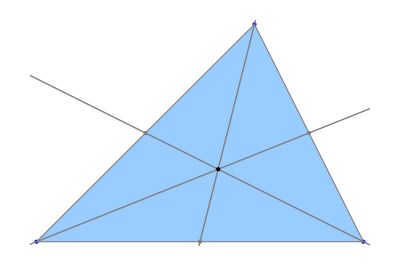
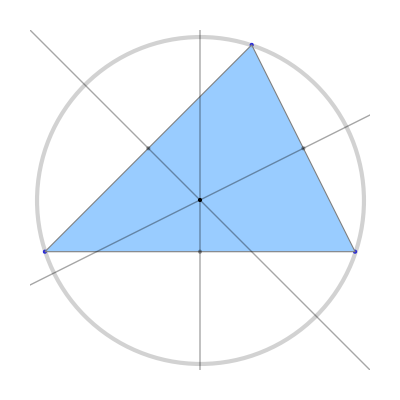
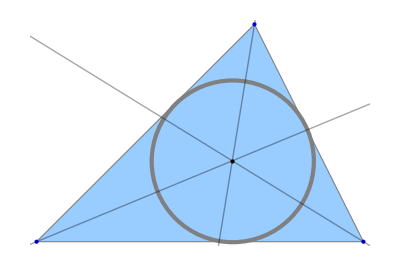
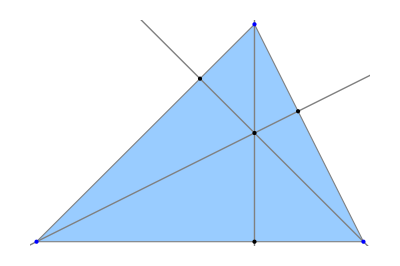
"     "-Graphics-"Centroid
"-Graphics-"Circumcenter
"-Graphics-"Incenter
"-Graphics-"Orthocenter"

Create a graphic for each of these centers similar to that created for the centroid and the medians.

Using options to the Plot function, create a plot showing the probability density function (PDF) of a normal distribution together with vertical lines at the ﬁrst and second standard deviations. Your plot should look something like that in Figure Chapter.NumberedFigure for a normal distribution with μ=0 and σ=1.

PDF of normal distribution with standard deviation lines.

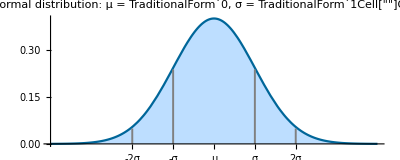

Solutions

The color wheel can be generated by mapping the Hue directive over successive sectors of a disk. Note that the argument to Hue must be scaled so that it falls within the range zero to one.

```mathematica
colorWheel[n_]:=Graphics[({Hue[Rescale[#,{0,2π}]],Disk[{0,0},1,{#,#+ n}]}&)/@Range[0,2 π,n],ImageSize->Small]
```

Here is a color wheel created from 256 separate sectors (hues).

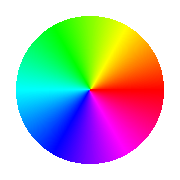

```mathematica
colorWheel[π/256]
```

Here is the circle graphic primitive together with a text label.

```mathematica
circ=Circle[{.5,.5},.5];
```

```mathematica
ctext=Text[Style["Circle",8],{.5,-.2}];
```

This generates the graphics primitive for the triangle and its text label.

```mathematica
tri=Triangle[{{-2,0},{-1,1},{0,0}}];
```

```mathematica
ttext=Text[Style["Triangle",8],{-1,-.2}];
```

Here is the rectangle and label.

```mathematica
rect=Rectangle[{1.5,0},{2.5,1}]
```

Rectangle[{1.5,0},{2.5,1}]

```mathematica
rtext=Text[Style["Rectangle",8],{2,-0.2}];
```

Finally, this displays each of these graphics elements all together.

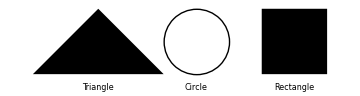

```mathematica
Graphics[{tri,ttext,circ,ctext,rect,rtext}]
```

Add some directives to each primitive.

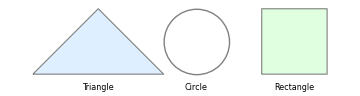

```mathematica
Graphics[{
{EdgeForm[Gray],LightBlue,tri},ttext,
{Thick,Gray,circ},ctext,
{EdgeForm[Gray],LightGreen,rect},rtext}]
```

Cuboid takes a list of three numbers as the coordinates of its lower-left corner. This maps the object across two such lists.

```mathematica
Map[Cuboid,RandomReal[1,{2,3}]]
```

{Cuboid[{0.159256,0.199787,0.744115}],Cuboid[{0.629273,0.77004,0.902954}]}

Below is a list of six cuboids and the resulting graphic. Notice the large amount of overlap of the cubes. You can reduce the large overlap by specifying minimum and maximum values of the cuboid.

```mathematica
cubes=Map[Cuboid,RandomReal[1,{6,3}]];
```

```mathematica
Graphics3D[{Opacity[.5],cubes}]
```

-Graphics3D-

Start by creating a unit cube centered on the origin. An opacity directive adds transparency.

```mathematica
Graphics3D[{Opacity[.25],Cuboid[{-0.5,-0.5,-0.5}]},Boxed->False,Axes->Automatic]
```

-Graphics3D-

Next rotate 45°. Note the third argument of Rotate used to specify the axis about which the rotation should occur.

```mathematica
Graphics3D[{Opacity[.25],Cuboid[{-.5,-.5,-.5}],Rotate[Cuboid[{-.5,-.5,-.5}],45 °,{0,0,1}]}]
```

-Graphics3D-

Here is the dynamic version. The angle θ is the parameter that is manipulated here. The explicit PlotRange option is necessary to prevent its re-computation for every new angle of rotation.

```mathematica
Manipulate[
Graphics3D[Rotate[Cuboid[{-.5,-.5,-.5}],θ,{0,0,1}],PlotRange->1],
{θ,0,2π}]
```

Start by creating the set of points.

```mathematica
pts=RandomReal[{0,1},{24,3}];
```

To connect all pairs of points, use Subsets[pts,{2}].

```mathematica
Graphics3D[{
{Opacity[.3],Line[Subsets[pts,{2}]]},
{Red,PointSize[Medium],Point[pts]}}]
```

-Graphics3D-

To add a label to the plot, use StringForm to slot some values into the string. The binomial Binomial[n, 2] gives the number of pairs of points.

```mathematica
Graphics3D[{
{Opacity[.3],Line[Subsets[pts,{2}]]},
{Red,PointSize[Medium],Point[pts]}},PlotLabel->StringForm["`1` vertices, `2` edges", Length[pts], 
    Binomial[Length[pts], 2]]]
```

-Graphics3D-

First we create the Point graphics primitives using a normal distribution with mean zero and standard deviation one.

```mathematica
randomcoords:=Point[RandomVariate[NormalDistribution[0,1],{1,2}]]
```

This creates the point sizes according to the speciﬁcation given in the statement of the problem.

```mathematica
randomsize:=PointSize[RandomReal[{.01,.1}]]
```

This creates a random color that will be used for each primitive.

```mathematica
randomcolor:=RandomColor[ColorSpace->"Hue"]
```

Here then are 500 points. (You may ﬁnd it instructive to look at just one of these points.)

```mathematica
pts=Table[{randomcolor,randomsize,randomcoords},{500}];
```

And here is the graphic.

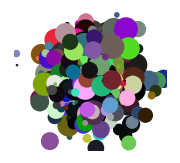

```mathematica
Graphics[pts]
```

Alternatively, you could do it all in one step using MapThread.

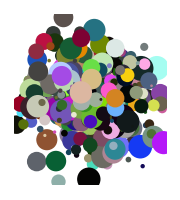

```mathematica
With[{n=500},
Graphics[MapThread[{#1,PointSize[#2],Point[#3]}&,{RandomColor[n,ColorSpace->"Hue"],RandomReal[{.01,.1},n],RandomVariate[NormalDistribution[0,1],{n,2}]}]
]]
```

Here are the binary digits of π. First is used to get only the digits from RealDigits.

```mathematica
First[RealDigits[N[Pi,12],2]]
```

{1,1,0,0,1,0,0,1,0,0,0,0,1,1,1,1,1,1,0,1,1,0,1,0,1,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0}

Convert zeros to negative ones.

```mathematica
2%-1
```

{1,1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,1,1,1,-1,1,1,-1,1,-1,1,-1,1,-1,-1,-1,1,-1,-1,-1,1,-1,-1,-1,1,-1}

Here then is a plot for the ﬁrst ﬁfty thousand digits.

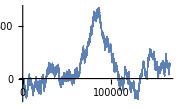

```mathematica
ListLinePlot[
With[{digits=50000},
Accumulate[2First[RealDigits[N[Pi,digits],2]]-1]
]]
```

For the two-dimensional case, use Partition to pair up the binary digits, then a transformation rule to convert them to compass directions.

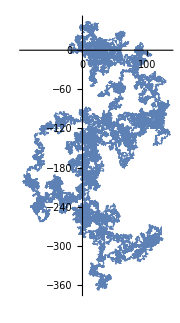

```mathematica
With[{digs=First[RealDigits[N[Pi,50000],2]]},
ListLinePlot[Accumulate[Partition[digs,2,2]/.{{0,0}->{-1,0},{1,1}->{0,-1}}],
AspectRatio->Automatic]]
```

The algebraic solution is given by the following steps. First solve the equations for x and y.

```mathematica
Clear[x,y,r]
```

```mathematica
soln=Solve[{(x-1)^2+(y-1)^2==2,(x+3)^2+(y-4)^2==r^2},{x,y}]
```

{{x→1/50 (-58+4 r^2-3 √(-529+54 r^2-r^4)),y→1/50 (131-3 r^2-4 √(-529+54 r^2-r^4))},{x→1/50 (-58+4 r^2+3 √(-529+54 r^2-r^4)),y→1/50 (131-3 r^2+4 √(-529+54 r^2-r^4))}}

Then ﬁnd those values of r for which the x and y coordinates are identical.

```mathematica
Solve[{
(x/.soln⟦1⟧)==(x/.soln⟦2⟧),
(y/.soln⟦1⟧)==(y/.soln⟦2⟧)},
r]
```

{{r→-5-√2},{r→5-√2},{r→-5+√2},{r→5+√2}}

Here then are those values of r that are positive.

```mathematica
Cases[%,{r->_?Positive}]
```

{{r→5-√2},{r→5+√2}}

To display the solution, we will plot the ﬁrst circle with solid lines and the two solutions with dashed lines together in one graphic. Here is the ﬁrst circle centered at (1, 1).

```mathematica
circ=Circle[{1,1},√2];
```

Here are the circles that represent the solution to the problem.

```mathematica
r1=5-√2;
r2=5+√2;
```

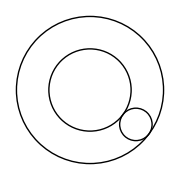

```mathematica
Graphics[{circ,Circle[{-3,4},r1],Circle[{-3,4},r2]},Axes->Automatic]
```

We wanted to display the solutions (two circles) using dashed lines. The graphics directive Dashing[{x,y}] directs all subsequent lines to be plotted as dashed, alternating the dash x units and the space y units. We use it as a graphics directive on the two circles c1 and c2. The circles inherit only those directives in whose scope they appear.

```mathematica
dashc1={Red,Dashing[{.025,.025}],Circle[{-3,4},r1]};
dashc2={Red,Dashing[{.05,.05}],Circle[{-3,4},r2]};
```

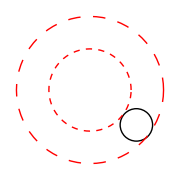

```mathematica
Graphics[{
{Thick,circ},
dashc1,dashc2},Axes->Automatic]
```

Here is a plot of the sine function.

```mathematica
sinplot=Plot[Sin[x],{x,0,2 π}]
```

-Graphics-

Using pattern matching, here are the coordinates that were used to construct the curve.

```mathematica
Short[coords=Cases[sinplot,Line[{x__}]:>x,Infinity],2]
```

{{1.28228×10^-7,1.28228×10^-7},{«22»,«21»},«427»,{«1»},{«1»}}

Create vertical lines from each coordinate.

```mathematica
Short[lines=Map[Line[{{#[[1]],0},#}]&,coords],2]
```

{«1»}

Here then is the ﬁnal graphic.

```mathematica
Show[sinplot,Graphics[{Thickness[.001],lines}]]
```

-Graphics-

First, here is the code for the triangle medians from Section 5.5.

```mathematica
TriangleMedians[Triangle[{p1_,p2_,p3_}]]:=Module[{midpts},
midpts=(#1+#2)/2&@@@Subsets[{p1,p2,p3},{2}];
MapThread[Line[{#1,#2}]&,{{p3,p2,p1},midpts}]]
```

Second, this bundles up the code fragments from Section 8.1 into a reusable function. We have added options inherited from Graphics.

```mathematica
CentroidPlot[Triangle[{p1_,p2_,p3_}],opts:OptionsPattern[Graphics]]:=
Graphics[{
{LightBlue,EdgeForm[Blue],Triangle[{p1,p2,p3}]},
{Blue,PointSize[Medium],Point[{p1,p2,p3}]},
{Red,PointSize[Medium],Point@RegionCentroid[Triangle[{p1,p2,p3}]]},
{Gray,TriangleMedians[Triangle[{p1,p2,p3}]],PointSize[Medium],Point[(#1+#2)/2&@@@Subsets[{p1,p2,p3},{2}]]}
},opts]
```

```mathematica
SeedRandom[15];
Table[CentroidPlot[Triangle[RandomInteger[{-5,5},{3,2}]]],{3}]
```

{-Graphics-,-Graphics-,-Graphics-}

To deal with the pathological situation where the points are collinear, ﬁrst create a message that will be issued under these conditions.

```mathematica
CentroidPlot::collinpts="The points `1` are collinear, giving a degenerate triangle.";
```

Three points are collinear if and only if the area of the triangle determined by those points is zero. The built-in Area function returns an error message in this situation:

```mathematica
pts={{0,0},{1,1},{2,2}};
Area[Triangle[pts]]
```

Area::reg: Triangle[{{0, 0}, {1, 1}, {2, 2}}] is not a correctly specified region.

Area[Triangle[{{0,0},{1,1},{2,2}}]]

We could trap for a non-numeric value returned by Area, but we will take another, more direct approach. The area of the triangle determined by three points is given by the following determinant:

Det[x_1 | y_1 | 1
x_2 | y_2 | 1
x_3 | y_3 | 1]

In fact, we have already implemented this in the function SignedArea from Section 4.3.

```mathematica
SignedArea[Triangle[{v1_,v2_,v3_}]]:=1/2 Det[{v1,v2,v3}/.{x_,y_}:>{x,y,1}]
```

```mathematica
SignedArea[Triangle[pts]]
```

0

Here then is the code to trap for this condition.

```mathematica
If[SignedArea[pts]==0,Message[CentroidPlot::collinpts,pts],else_body_of_function]
```

```mathematica
CentroidPlot[Triangle[{p1_,p2_,p3_}],opts:OptionsPattern[Graphics]]:=
If[SignedArea[Triangle[{p1,p2,p3}]]==0,Message[CentroidPlot::collinpts,{p1,p2,p3}],

Graphics[{
{LightBlue,EdgeForm[Blue],Triangle[{p1,p2,p3}]},
{Blue,PointSize[Medium],Point[{p1,p2,p3}]},
{Red,PointSize[Medium],Point@RegionCentroid[Triangle[{p1,p2,p3}]]},
{Gray,TriangleMedians[Triangle[{p1,p2,p3}]],PointSize[Medium],Point[(#1+#2)/2&@@@Subsets[{p1,p2,p3},{2}]]}
},opts]
]
```

```mathematica
CentroidPlot[Triangle[pts]]
```

CentroidPlot::collinpts: The points {{0, 0}, {1, 1}, {2, 2}} are collinear, giving a degenerate triangle.

```mathematica
CentroidPlot[Triangle[RandomInteger[{-5,5},{3,2}]]]
```

-Graphics-

Start with the circumcenter which is the center of the circumscribing circle. It is located at the intersection of the perpendicular bisectors of the sides. To ﬁnd the line from the center, perpendicular to a side, use RegionNearest and InfiniteLine. First, get the center.

```mathematica
{p1,p2,p3}={{-1,0},{0,2},{1,0}};
center=First@Circumsphere[{p1,p2,p3}]
```

{0,3/4}

Here are the lines through each pair of vertices:

```mathematica
lines=InfiniteLine/@Subsets[{p1,p2,p3},{2}]
```

{InfiniteLine[{{-1,0},{0,2}}],InfiniteLine[{{-1,0},{1,0}}],InfiniteLine[{{0,2},{1,0}}]}

And this gives the point on each line closest to the center.

```mathematica
pbs=Map[RegionNearest[#,center]&,lines]
```

{{-1/2,1},{0,0},{1/2,1}}

Finally, we want a line from each of these points to the center.

```mathematica
perpLines=Map[Line[{center,#}]&,Map[RegionNearest[#,center]&,lines]]
```

{Line[{{0,3/4},{-1/2,1}}],Line[{{0,3/4},{0,0}}],Line[{{0,3/4},{1/2,1}}]}

```mathematica
Graphics[{
{Blue,PointSize[Medium],Point[{p1,p2,p3}]},
{EdgeForm[Gray],LightBlue,Triangle[{p1,p2,p3}]},
{Blue,Circumsphere[{p1,p2,p3}]},
{Blue,PointSize[Large],Point@center},
{Purple,perpLines,PointSize[Large],Point@pbs}
}]
```

-Graphics-

Next, compute the orthocenter. Using InfiniteLine will make it so that we can draw on the computational geometry machinery to do our computations.

```mathematica
{p1,p2,p3}={{-1,0},{0,2},{1,0}};
```

```mathematica
lines=Map[InfiniteLine,Subsets[{p1,p2,p3},{2}]]
```

{InfiniteLine[{{-1,0},{0,2}}],InfiniteLine[{{-1,0},{1,0}}],InfiniteLine[{{0,2},{1,0}}]}

The altitude is the line drawn from a vertex to the opposite side, perpendicular to that side. Note that we need to reverse the list {p1,p2,p3} so that the proper line is paired with the proper point.

```mathematica
altPts=MapThread[RegionNearest[#1,#2]&,{lines,Reverse[{p1,p2,p3}]}]
```

{{-3/5,4/5},{0,0},{3/5,4/5}}

We need lines from each vertex to the corresponding point in altPts.

```mathematica
altLines=MapThread[Line[{#1,#2}]&,{Reverse@{p1,p2,p3},altPts}]
```

{Line[{{1,0},{-3/5,4/5}}],Line[{{0,2},{0,0}}],Line[{{-1,0},{3/5,4/5}}]}

Here then is the graphic showing the triangle in gray, its vertices in blue, and the altitude lines and points in purple.

```mathematica
Graphics[{
{Blue,PointSize[Medium],Point[{p1,p2,p3}]},
{EdgeForm[Gray],LightBlue,Triangle[{p1,p2,p3}]},
{Purple,PointSize[Large],Point@altPts,altLines}
}]
```

-Graphics-

Finally, the incenter, the center of which is the largest circle that ﬁts entirely inside the triangle. For the formula for the incenter, we will need a function to compute the perimeter of the triangle. This one comes essentially from Section 4.3.

```mathematica
Perimeter[Triangle[pts:{p1_,p2_,p3_}]]:=RegionMeasure[Line[pts/.{p_,pn__}:>{p1,pn,p1}]]
```

```mathematica
inCenter[pts:{p1_,p2_,p3_}]:=Module[{a,b,c,p=Perimeter[Triangle[pts]]},
{a,b,c}={Norm[p2-p3],Norm[p1-p3],Norm[p2-p1]};
{(a p1[[1]]+b p2[[1]]+ c p3[[1]])/p,(a p1[[2]]+b p2[[2]]+ c p3[[2]])/p}]
```

Once you have the center, the radius will be the shortest distance from the center to one of the sides.

```mathematica
inRadius[pts:{pt1_,pt2_,pt3_}]:=EuclideanDistance[RegionNearest[InfiniteLine[pt1,pt3],inCenter[pts]],inCenter[pts]]
```

```mathematica
{p1,p2,p3}={{-1,0},{0,2},{1,0}};
pts={p1,p2,p3};
Graphics[{
{EdgeForm[Gray],LightBlue,Triangle[pts]},
{PointSize[Large],Point[pts]},
{Red,Circle[inCenter@pts,inRadius[pts]],PointSize[Large],Point[inCenter@pts]},
{Map[Line[{inCenter@pts,#}]&,pts]}
},Axes->True]
```

-Graphics-

First set the distribution and compute the mean and standard deviation.

```mathematica
𝒟=NormalDistribution[0,1];
σ=StandardDeviation[𝒟];
μ=Mean[𝒟];
```

Next we manually construct four vertical lines at the standard deviations going from the horizontal axis to the pdf curve.

```mathematica
Plot[PDF[𝒟,x],{x,-4,4},
Filling->Axis,Epilog->{Gray,Line[{{{μ+σ,0},{μ+σ,PDF[𝒟,μ+σ]}},{{μ-σ,0},{μ-σ,PDF[𝒟,μ-σ]}},{{μ+2 σ,0},{μ+2 σ,PDF[𝒟,μ+2 σ]}},{{μ-2 σ,0},{μ-2 σ,PDF[𝒟,μ-2 σ]}}}]},
AxesOrigin->{-4,0},
Ticks->{{{-2 σ,"-2σ"},{-σ,"-σ"},{μ,"μ"},{σ,"σ"},{2 σ,"2σ"}},Automatic},
AspectRatio->0.4,
PlotLabel->StringForm["Normal distribution: μ=`1`, σ=`2`Cell[""]Cell[""]",μ,σ]]
```

-Graphics-

And here is a little utility function to make the code a bit more readable and easier to use.

```mathematica
sdLine[𝒟_,μ_,σ_]:=Line[{{{μ+σ,0},{σ+μ,PDF[𝒟,μ+σ]}},{{μ-σ,0},{-σ+μ,PDF[𝒟,μ-σ]}}}]
```

```mathematica
Plot[PDF[𝒟,x],{x,-4,4},
Filling->Axis,Epilog->{Gray,Thickness[.0035],sdLine[𝒟,μ,σ],sdLine[𝒟,μ,2 σ]},AxesOrigin->{-4,0},
Ticks->{{{-2 σ,"-2σ"},{-σ,"-σ"},{μ,"μ"},{σ,"σ"},{2 σ,"2σ"}},Automatic},
AspectRatio->0.4,
PlotLabel->StringForm["Normal distribution: μ=`1`, σ=`2`Cell[""]Cell[""]",μ,σ]]
```

-Graphics-

Exercises: Dynamic graphics

In the Manipulate examples in this section, the parameters were controlled by sliders. Moving the slider changes the value of the parameter and any expression dependent upon that parameter inside the Manipulate expression. Sometimes you want to choose values for a parameter from a list of discrete values. A setter bar is a convenient control object for this. One way to set it is to use a different syntax for the parameter list:{param,{val_1,val_2,…,val_n}} will cause Manipulate to automatically use a setter bar instead of a slider. Create a Manipulate object showing plots of sin, cos, or tan, each selectable from a setter bar.

Modify the above exercise to use a popup menu to choose the function to plot. You can explicitly set the control by using ControlType→"PopupMenu".

Here is a graphic showing an ellipsoid together with its two foci:

```mathematica
With[{a=5,b=3},
f=√(a^2-b^2);
Graphics[{
Circle[{0,0},{a,b}],
Point[{f,0}],Point[{-f,0}]
},Axes->Automatic]]
```

-Graphics-

Turn this into a dynamic graphic by making the semi-major and semi-minor axes lengths a and b dynamic which, upon updating, will cause the ellipse to change shape. Some thought will be needed to properly deal with the situation b>a.

Create a dynamic interface that displays various structure diagrams and space-ﬁlling plots of the amino acids. A list of the amino acids is given by

```mathematica
ChemicalData["AminoAcids"]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

The diagrams and plots that should be included are built into ChemicalData:

```mathematica
StringCases[ChemicalData["Properties"],__~~"Diagram"|(__~~"Plot")]//Flatten
```

{BlackStructureDiagram,CHBlackStructureDiagram,CHColorStructureDiagram,ColorStructureDiagram,MoleculePlot,SpaceFillingMoleculePlot}

Using the code developed in Section Chapter.Section for plotting the centroid of a triangle, create a dynamic interface that displays the triangle, the medians (lines from each vertex to the midpoint of the opposite side), and the triangle vertices as locators.

In the 1920s and 1930s the artist Marcel Duchamp created what he termed rotoreliefs, spinning concentric circles giving a three-dimensional illusion of depth "(Duchamp 1926)". Create your own rotoreliefs: start with several concentric circles of different radii, then vary their centers around a path given by another circle, and animate.

Create a plot of sin(θ) side-by-side with a circle and a dynamic point that moves along the curve and the circle as θ varies from 0 to 2π (Figure Chapter.NumberedFigure).

Dynamic visualization of sin function.

Take one of the two-dimensional random walk programs developed elsewhere in this book (Sections 6.3 and 10.3) and create an animation displaying successive steps of the random walk.

Looking forward to Chapter 10, where we develop a full application for computing and visualizing random walks, create a dynamic interface that displays random walks, adding controls to select the number of steps from a pulldown menu, the dimension from a setter bar, and a checkbox to turn on and off lattice walks.

Create a visualization of two-dimensional vector addition (Figure Chapter.NumberedFigure). The interface should include either a 2d slider for two vectors in the plane or locators to change the position of each vector; the display should show the two vectors as well as their vector sum. Extend the solution to three dimensions. (The solution of this vector interface is due to Harry Calkins of Wolfram Research.)

Dynamic visualization of vector arithmetic.

Create a dynamic interface consisting of a locator constrained to the unit circle. Check the documentation on Locator for information on constraining the movement of locators.

Create a dynamic interface that displays twenty random points in the unit square whose locations are randomized each time you click your mouse on the graphic. Add a checkbox to toggle the display of the shortest path (FindShortestTour) through the points (look up EventHandler and MouseClicked in the documentation).

A suggested addition would be to add a control to change the number of points that are used but take care to keep the total number of points manageable (see the note on Traveling Salesman problems at the end of the chapter).

Solutions

Giving the parameter list in the form {param,{val_1,val_2,val_3}} automatically causes Manipulate to use a setter bar as the control type.

```mathematica
Manipulate[
Plot[f[x],{x,0,2π}],
{f,{Sin,Cos,Tan}}]
```

This explicitly sets the control type to a popup menu.

```mathematica
Manipulate[
Plot[f[x],{x,0,2π}],
{f,{Sin,Cos,Tan},ControlType->PopupMenu}]
```

If the parameter b is greater than a, you will need to switch the foci to the vertical axis. This is done inside the If statement before the graphics are given.

```mathematica
Manipulate[
f=If[a^2-b^2≥0,{√Abs[a^2-b^2],0},{0,√Abs[a^2-b^2]}];
Graphics[{
Circle[{0,0},{a,b}],
Point[f],Point[-f]
},PlotRange->Max[a,b]+.1],
{a,1,5},{b,1,5}]
```

We will put this together in two parts: ﬁrst create a function to display any amino acid using one of the various diagrams; then pour it into a Manipulate. Note, this function is dependent upon ChemicalData to create the displays. ChemicalData returns an Entity, hence the two rules, one for the chemical name as a string and the other as an Entity. Alternatively, you could modify it to use your own visualizations, such as the space-ﬁlling plots in Section 8.4.

```mathematica
AminoAcidPlot[aa_String,diagram_:"ColorStructureDiagram"]:=Labeled[Framed[ChemicalData[aa,diagram],ImageSize->All],ChemicalData[aa,"Name"],LabelStyle->Directive["Menu",9]]
```

```mathematica
AminoAcidPlot[aa_Entity,diagram_:"ColorStructureDiagram"]:=Labeled[Framed[ChemicalData[aa,diagram],ImageSize->All],ChemicalData[aa,"Name"],LabelStyle->Directive["Menu",9]]
```

```mathematica
AminoAcidPlot["Glycine"]
```

-Graphics-glycine

```mathematica
AminoAcidPlot[Entity["Chemical","Glycine"]]
```

-Graphics-glycine

```mathematica
Manipulate[
AminoAcidPlot[aminoacid,diagram],
{{aminoacid,"LAlanine","Amino acid"},aa},
{diagram,{"StructureDiagram","CHColorStructureDiagram","CHStructureDiagram","ColorStructureDiagram","MoleculePlot","SpaceFillingMoleculePlot"}},
Initialization:>{aa=ChemicalData["AminoAcids"]},SynchronousUpdating->False,SaveDefinitions->True]
```

Borrowing the CentroidPlot from Exercise 10 from Section 8.1, here is the Manipulate.

```mathematica
Manipulate[CentroidPlot[Triangle[pts],PlotRange->{-0.2,2.2}],
{{pts,{{-1,0},{0,2},{1,0}}},Locator},SaveDefinitions->True]
```

Modify the radii and the centers to get different effects. Try using transparent disks instead of circles.

```mathematica
Manipulate[
Graphics[
Table[Circle[r/4{Cos[t],Sin[t]},1.1-r],{r,.2,1,.05}],
PlotRange->1],
{t,0,2π,.1}]
```

Putting the two graphics pieces (Graphics[…] and Plot[…]) in a grid gives you ﬁner control over their placement and formatting.

```mathematica
Manipulate[Grid[{{Graphics[{Circle[],Blue,PointSize[.04],Point[{Cos[θ],Sin[θ]}]},Axes->True],Plot[Sin[x],{x,0,2 π},Epilog->{Blue,Line[{{θ,0},{θ,Sin[θ]}}],PointSize[.025],Point[{θ,Sin[θ]}]}]}},Frame->All],{θ,0,2 π}]
```

First load the package that contains the random walk code. You could use you own implementation as well.

```mathematica
<<EPM`RandomWalks`
```

Create a 1000-step, two-dimensional, lattice walk.

```mathematica
rw=RandomWalk[1000,Dimension->2,LatticeWalk->True];
```

This is a basic start. Take is used to display successive increments. Note the need for the 1 in the parameter list to insure that steps only take on integer values.

```mathematica
Animate[
Graphics[Line[Take[rw,n]]],
{n,2,Length[rw],1},AnimationRunning->False]
```

The output above suffers from the fact that the display jumps around a lot as Mathematica tries to ﬁgure out a sensible plot range for each frame. Instead, we should ﬁx the plot range for all frames to avoid this jumpiness. This is done in the deﬁnitions for xran and yran in the Initialization below.

```mathematica
Manipulate[
Graphics[Line[Take[rw,n]],PlotRange->{xran,yran}],
{n,2,Length[rw],1},
Initialization:>{
rw=RandomWalk[1000,Dimension->2,LatticeWalk->True];{xran,yran}=Map[{Min[#1],Max[#1]}&,Transpose[rw]]},SaveDefinitions->True]
```

Using the programs developed in Section 10.3, here is the code, including a pulldown menu for the steps parameter, a setter bar for the dimension parameter, and a checkbox for the lattice parameter.

```mathematica
Manipulate[
ShowWalk@RandomWalk[steps,Dimension->dim,LatticeWalk->latticeQ],
{steps,{100,250,500,750,1000,10000}},
{{dim,1,"Dimension"},{1,2,3}},
{{latticeQ,True,"Lattice walk"},{True,False}},
Initialization:>Needs["EPM`RandomWalks`"],SaveDefinitions->True]
```

Here is the solution using Slider2D. Using Locator instead is left for the reader.

```mathematica
Manipulate[
Graphics[{
Red,Arrow[{{0,0},pt1}],
Blue,Arrow[{{0,0},pt2}],
Green,Arrow[{{0,0},pt1+pt2}],
Dashed,Orange,Line[{pt1,pt1+pt2,pt2}]},
PlotRange-> 6,Axes-> True,GridLines-> Automatic],
{{pt1,{1,4},"Red vector"},{-5,-5},{5,5}},{{pt2,{3,1},"Blue vector"},{-5,-5},{5,5}},
ControlPlacement-> Left]
```

The key here is to use a two-argument form of Dynamic, where the second argument gives the constraint on the parameter.

```mathematica
DynamicModule[{pt={0,.5}},
Graphics[{
LightBlue,Rectangle[{-1,-1},{1,1}],
Pink,Circle[],Thick,Circle[{0,0},.5],
Locator[Dynamic[pt,(pt=.5Normalize[#])&]]
},PlotRange->1.25]]
```

First, create a static version of the problem; we use GraphicsComplex to display the points and the tour.

```mathematica
pts=RandomReal[1,{25,2}];
```

```mathematica
Graphics[GraphicsComplex[pts,Point@Range[Length[pts]]],Axes->Automatic]
```

-Graphics-

```mathematica
tour=Last[FindShortestTour[pts]];
Graphics[GraphicsComplex[pts,{Line[tour],Red,PointSize[Medium],Point[tour]}],Axes->Automatic]
```

-Graphics-

Here is the dynamic interface using EventHandler to choose a new set of random points with each mouse click.

```mathematica
Manipulate[
DynamicModule[{pts=RandomReal[1,{20,2}],tour},
tour=Dynamic[Last[FindShortestTour[pts]]];
EventHandler[
Dynamic[Graphics[GraphicsComplex[pts,If[Not[showtour],Point@Range[Length[pts]],{Line[tour],Red,PointSize[Medium],Point[tour]}]],Axes->Automatic]],
{"MouseClicked":>(pts=RandomReal[1,{20,2}])}
]],
{{showtour,False,"Show tour"},{True,False}},
ContentSize->All]
```

Exercises: Efﬁcient structures

Create a hexagonal grid of polygons like that in Figure Chapter.NumberedFigure. First create the grid by performing appropriate translations using Translate or the geometric transformation TranslationTransform. Compare this approach with a multi-polygon approach.

Two-dimensional hexagonal lattice.

-Graphics-

Take the example visualizing a 500000-step random walk at the beginning of this section and replicate the output using GraphicsComplex instead of ListLinePlot. Compare the running times for each as the number of steps increases.

The ShowWalk function discussed in Section 4.1 for displaying random walks uses ListLinePlot to display the data. As mentioned in this section, ListLinePlot will get bogged down for large numbers of points. Using the solution to the previous exercise, create a new version for both the two- and three-dimensional cases of ShowWalk that uses GraphicsComplex instead; then test the new implementation against the one developed in Chapter 4.

Create a graphic consisting of a three-dimensional lattice, that is, lines passing through the integer coordinates in 3-space (Figure Chapter.NumberedFigure). Compare approaches that use multi-lines as opposed to those that do not.

Three-dimensional integer lattice.

-Graphics3D-

A common problem in computational geometry is ﬁnding the boundary of a given set of points in the plane. One way to think about the boundary is to imagine the points as nails in a board and then to stretch a rubber band around all the nails. The stretched rubber band lies on a convex polygon commonly called the convex hull of the point set.

Create a function ConvexHullPlot for visualizing the convex hull together with the points on the interior of the convex hull. Your function should inherit options for Graphics. The built-in function ConvexHullMesh can be used to generate the hull polygon:

```mathematica
pts=RandomReal[1,{28,2}];
ℛ=ConvexHullMesh[pts]
```

-Graphics-

The zero-dimensional objects in the mesh are points and the one-dimensional objects are lines (two-dimensional objects would be polygons). These are the points and lines on the convex hull.

```mathematica
MeshPrimitives[ℛ,0];
Take[%,2]
```

{Point[{0.992746,0.379391}],Point[{0.0394433,0.0418121}]}

```mathematica
MeshPrimitives[ℛ,1];
Take[%,2]
```

{Line[{{0.0383976,0.960283},{0.0394433,0.0418121}}],Line[{{0.0394433,0.0418121},{0.225102,0.00814885}}]}

Your function should generate output similar to the following:

```mathematica
ConvexHullPlot[pts,Axes->Automatic]
```

-Graphics-

Modify ConvexHullPlot from Exercise ExerciseItem to accept an option Dimension. With default value of two, ConvexHullPlot should produce output like that in Exercise ExerciseItem. For Dimension→3, it should generate the convex hull together with large red points at each vertex of the hull (Figure Chapter.NumberedFigure).

Three-dimensional convex hull with hull points highlighted.

-Graphics3D-

Extend Exercise ExerciseItem from Section Chapter.Section to random walks on the base-n digits of π. For example, in base 3, a 1 corresponds to an angle of 120° from the current position, 2 corresponds to 240°, and 0 to 360°. In base 4 the step angles will be multiples of 90° and in general, for base n, the step angles will be multiples of 360°/n. Use GraphicsComplex to visualize the walks. Include a color function that depends on the length of the walk.

Solutions

Here is the implementation using TranslationTransform.

```mathematica
Clear[vertices,n,α]
```

```mathematica
vertices[n_]:=Table[{Cos[(2 π α)/n],Sin[(2 π α)/n]},{α,0,n}]
```

```mathematica
hexagon=Polygon[vertices[6]];Graphics[{EdgeForm[Gray],LightGray,hexagon}]
```

-Graphics-

```mathematica
Graphics[{
EdgeForm[Gray],LightGray,
Table[GeometricTransformation[hexagon,TranslationTransform[{3 i+3/4 ((-1)^j+1),(√3 j)/2}]
],{i,5},{j,8}]
}]
```

-Graphics-

Or use Translate directly.

```mathematica
gr1=Graphics[{
EdgeForm[Gray],LightGray,
Table[Translate[hexagon,{3 i+3/4 ((-1)^j+1),(√3 j)/2}],{i,5},{j,8}]
}]
```

-Graphics-

This implementation contains one Polygon per hexagon.

```mathematica
Count[gr1,_Polygon,Infinity]
```

40

Now use multi-polygons. The following version of hexagon is deﬁned so that it can take a pair of translation coordinates. Note also the need to ﬂatten the table of vertices so that Polygon can be applied to the correct list structure.

```mathematica
Clear[hexagon];
hexagon[{x_,y_}]:=Table[{Cos[(2 π i)/6]+x,Sin[(2 π i)/6]+y},{i,1,6}]
```

```mathematica
gr2=Graphics[{EdgeForm[Gray],LightGray,Polygon[Flatten[Table[hexagon[{3 i+3/4 ((-1)^j+1),(√3 j)/2}],{i,5},{j,8}],1]]
}]
```

-Graphics-

```mathematica
Count[gr2,_Polygon,Infinity]
```

1

Here is the usage message for GraphicsComplex.

```mathematica
?GraphicsComplex
```

RowBox[{"GraphicsComplex", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["data", "TI"]}], "]"}] represents a graphics complex in which coordinates given as integers StyleBox["i", "TI"] in graphics primitives in StyleBox["data", "TI"] are taken to be SubscriptBox[StyleBox["pt", "TI"], StyleBox["i", "TI"]].

The ﬁrst argument to GraphicsComplex is a list of coordinate points, such as the output from RandomWalk. The second argument is a set of graphics primitives indexed by the positions of the points in the list of coordinates. The walk itself gives the coordinates that will be used as the ﬁrst argument to GraphicsComplex.

```mathematica
walk=RandomWalk[5 10^5];
```

```mathematica
Short[walk,2]
```

{{0,1},{0,2},{0,3},{0,2},«499992»,{-447,892},{-446,892},{-445,892},{-445,891}}

The second argument a list of primitives with the coordinate indices as arguments. We want to connect the ﬁrst point to the second, to the third, etc., with a line. That would look like Line[{1,2,3,…}]. The length of the list is given by Length[walk].

```mathematica
Graphics[GraphicsComplex[walk,{
Line@Range[Length[walk]]
}]]
```

-Graphics-

You could add axes and some directives and options to modify the plot.

```mathematica
Graphics[GraphicsComplex[walk,{
RGBColor[.6,.4,.5],Thickness[Tiny],Line@Range[Length[walk]]
}],Axes->Automatic]//Timing
```

{0.001048,-Graphics-}

The time to compute (and display) this object is several orders of magnitude faster than that with ListLinePlot. So why is ListLinePlot so slow with data of this size? It is designed to be as general as possible and to deal with many extraordinary situations. This generality comes at a cost. It is very fast for moderately sized data sets, but for large sets, another approach is preferable.

First, using the same argument structure as that in ShowWalk (Chapter 10), we give GraphicsComplex the list of coordinates followed by Line wrapped around a list of the point indices 1 through n (the length of the walk).

```mathematica
ShowWalkGC[coords:{{_,_}..}]:=Graphics[
GraphicsComplex[coords,Line[Range[Length[coords]]]]]
```

```mathematica
ShowWalkGC[RandomWalk[1500,Dimension->2]]
```

-Graphics-

Add options and color the path.

```mathematica
Clear[ShowWalkGC];ShowWalkGC[coords:{{_,_}..},opts:OptionsPattern[Graphics]]:=Graphics[
GraphicsComplex[coords,
{ColorData[1][1],Line[Range[Length[coords]]]}
],opts,
Axes->True,AspectRatio->Automatic]
```

```mathematica
ShowWalkGC[RandomWalk[1500,Dimension->2]]
```

-Graphics-

And similarly for the three-dimensional case:

```mathematica
ShowWalkGC[coords:{{_,_,_}..},opts:OptionsPattern[Graphics3D]]:=Graphics3D[GraphicsComplex[coords,
{ColorData[1][1],AbsoluteThickness[1],Line[Range[Length[coords]]]}],
opts,Axes->True,AspectRatio->Automatic]
```

```mathematica
ShowWalkGC[RandomWalk[2500,Dimension->3]]
```

-Graphics3D-

Finally, some timing comparisons between this implementation with GraphicsComplex and the versions that used basic graphics primitives and built-in functions.

```mathematica
walk=RandomWalk[250000];
Timing[ShowWalk[walk,AspectRatio->Automatic]]
```

{4.28677,-Graphics-}

```mathematica
Timing[ShowWalkGC[walk]]
```

{0.017871,-Graphics-}

One approach to creating the lattice is to manually specify the coordinates for the lines and then map the Line primitive across these coordinates. We will work with a small lattice.

```mathematica
xmin=0;xmax=3;
ymin=0;ymax=3;
zmin=0;zmax=3;
Table[{{x,ymin,zmin},{x,ymax,zmin}},{x,xmin,xmax}]
```

{{{0,0,0},{0,3,0}},{{1,0,0},{1,3,0}},{{2,0,0},{2,3,0}},{{3,0,0},{3,3,0}}}

Here are the three grids.

```mathematica
gridX=Table[{{xmin,y,z},{xmax,y,z}},{y,ymin,ymax},{z,zmin,zmax}];
gridY=Table[{{x,ymin,z},{x,ymax,z}},{x,xmin,xmax},{z,zmin,zmax}];
gridZ=Table[{{x,y,zmin},{x,y,zmax}},{x,xmin,xmax},{y,ymin,ymax}];
```

Finally, map Line across these grids and display as a Graphics3D object.

```mathematica
gr1=Graphics3D[{
Map[Line,gridX,{2}],
Map[Line,gridY,{2}],
Map[Line,gridZ,{2}]
},Boxed->False]
```

-Graphics3D-

```mathematica
Count[gr1,_Line,Infinity]
```

48

Using multi-lines reduces the number of Line objects substantially.

```mathematica
gr2=Graphics3D[{
Map[Line,gridX],
Map[Line,gridY],
Map[Line,gridZ]
},Boxed->False]
```

-Graphics3D-

```mathematica
Count[gr2,_Line,Infinity]
```

12

First, generate some random points in the plane.

```mathematica
pts=RandomReal[1,{8,2}];
```

Next, generate the mesh using a built-in function.

```mathematica
ℛ=ConvexHullMesh[pts]
```

-Graphics-

Quite a bit of information is embedded in the this BoundaryMeshRegion. For example, it is easy to extract the points on the boundary. They are mesh primitives of dimension zero.

```mathematica
Head[ℛ]
```

BoundaryMeshRegion

```mathematica
MeshPrimitives[ℛ,0]
```

{Point[{0.643154,0.220953}],Point[{0.357669,0.997291}],Point[{0.0543152,0.400786}],Point[{0.120583,0.881017}],Point[{0.892886,0.146246}]}

Similarly, lines are mesh primitives of dimension one.

```mathematica
MeshPrimitives[ℛ,1]
```

{Line[{{0.0543152,0.400786},{0.643154,0.220953}}],Line[{{0.643154,0.220953},{0.892886,0.146246}}],Line[{{0.892886,0.146246},{0.357669,0.997291}}],Line[{{0.357669,0.997291},{0.120583,0.881017}}],Line[{{0.120583,0.881017},{0.0543152,0.400786}}]}

In fact, the polygon itself is a mesh primitive of dimension two.

```mathematica
MeshPrimitives[ℛ,2]
```

{Polygon[{{0.0543152,0.400786},{0.643154,0.220953},{0.892886,0.146246},{0.357669,0.997291},{0.120583,0.881017}}]}

So the pieces of the mesh that we want to show are the region itself (bounded polygon, the original points, and the points on the boundary. We will highlight the points on the boundary by making them large and red. And we will pass options from Graphics on to the function.

```mathematica
ConvexHullPlot[pts_,opts:OptionsPattern[Graphics]]:=Module[{ℛ},ℛ=ConvexHullMesh[pts];Show[ℛ,Graphics[{Point[pts],Red,PointSize[Medium],MeshPrimitives[ℛ,0]}],opts]]
```

Try it out with a larger point set.

```mathematica
pts=RandomReal[{-100,100},{60,2}];
```

```mathematica
ConvexHullPlot[pts,Axes->Automatic,ImageSize->Small]
```

-Graphics-

First, set up the options framework.

```mathematica
Options[ConvexHullPlot]=Join[{Dimension->2},Options[Graphics],Options[Graphics3D]];
```

Here is a message that will be issued if the Dimension option is set to anything other than 2 or 3.

```mathematica
ConvexHullPlot::baddim="The value `1` of the Dimension option should be either 2 or 3";
```

```mathematica
ConvexHullPlot[pts_,opts:OptionsPattern[]]:=Module[{ℛ,dim=OptionValue[Dimension]},
ℛ=ConvexHullMesh[pts];
Which[
dim==2,Show[{ℛ,Graphics[{Point[pts],Red,PointSize[Medium],MeshPrimitives[ℛ,0]}]},
FilterRules[{opts},Options[Graphics]]],
dim==3,Show[{ℛ,Graphics3D[{Point[pts],Red,PointSize[Medium],MeshPrimitives[ℛ,0]}]},
FilterRules[{opts},Options[Graphics3D]]],
True,Message[ConvexHullPlot::baddim,dim]
]
]
```

Here is a larger point set.

```mathematica
pts=RandomReal[1,{40,3}];
```

Exercise some options.

```mathematica
ConvexHullPlot[pts,Dimension->3,Boxed->True,Background->Gray]
```

-Graphics3D-

Giving a bad value for the Dimension option should produce an error message.

```mathematica
ConvexHullPlot[pts,Dimension->4]
```

ConvexHullPlot::baddim: The value 4 of the Dimension option should be either 2 or 3

Here is the random walk on the digits of π in bases given by the second argument.

```mathematica
RandomWalkPi[d_,base_/;base>2]:=Module[{digits,angles,rules},
digits=First[RealDigits[N[π,d],base]];
angles=Rest@Range[0.,2π,2π/(base)];rules=MapThread[#1->#2&,{Range[0,base-1],angles}];
Accumulate[Map[{Cos[#],Sin[#]}&,digits/.rules]]
]
```

Using ListPlot, here is a quick visualization on base 5 digits:

```mathematica
ListLinePlot[RandomWalkPi[10000,5],AspectRatio->Automatic]
```

-Graphics-

Here is the GraphicsComplex.

```mathematica
walk=RandomWalkPi[10000,5];
len=Length[walk];
```

```mathematica
Graphics[GraphicsComplex[walk,{AbsoluteThickness[.2],Line[Range[len]]}],AspectRatio->Automatic]
```

-Graphics-

And here it is with color mapped to the distance from the origin.

```mathematica
Graphics[GraphicsComplex[walk,Map[{Hue[(#⟦1⟧)/len],AbsoluteThickness[.25],Line[#]}&,Partition[Range[2,len],2,1]]],AspectRatio->Automatic]
```

-Graphics-

Exercises: Examples

Create a function ComplexListPlot that plots a list of complex numbers in the complex plane using ListPlot. Set initial options so that the PlotStyle is red, the PointSize is a little larger than the default, and the horizontal and vertical axes are labeled “Re” and “Im,” respectively. Set up options to ComplexListPlot that are inherited from ListPlot.

Create a function ComplexRootPlot that plots the complex zeros of a polynomial in the plane. Use your implementation of ComplexListPlot that you developed in the previous exercise.

Use Mesh in a manner similar to its use in the RootPlot function to highlight the intersection of two surfaces, say sin(2x-cos(y)) and sin(x-cos(2y)). You may need to increase the value of MaxRecursion to get the sampling just right.

The version of VennDiagram developed in this section used Graphics to create the circles and then combined them with RegionPlot using Show. Modify VennDiagram so that the circles are created entirely inside RegionPlot.

Create a new rule for VennDiagram that takes a logical expression as its ﬁrst argument instead of a logical function. For example, your function should be able to handle input such as the following:

```mathematica
VennDiagram[A⊻B,{A,B}]
```

-Graphics-

Extend the previous exercise to a Venn diagram on three sets, using logical expressions as the ﬁrst argument.

```mathematica
VennDiagram[(A∨B∨C)&&¬(A∧B∧C),{A,B,C}]
```

-Graphics-

Modify the dynamic Venn diagram created in this section to also display a truth table like that in Figure Chapter.NumberedFigure. Include the truth table side-by-side with the Venn diagram. TruthTable was developed in Exercise 3 in Section 6.3.

Dynamic visualization of logical expressions.

The DotPlot function developed in this section uses a ﬁxed window size, meaning that it only colors a dot black if a string of length one matches a string of length one in the two sequences under comparison. Add a WindowSize option to DotPlot that allows you to set the length of the sequences to match – you will likely need stringPartition developed in Section 7.5. Finally, set up DotPlot to inherit the options from ArrayPlot.

```mathematica
DotPlot[seq2,seq1,WindowSize->3,FrameLabel->{"DQ023146.1","DQ232610.1"}]
```

-Graphics-

When making dot plots like in the previous exercise, if you knew you were always working with FASTA ﬁles, you could automate both the extraction of the frame labels from the FASTA accession ids and their insertion in the FrameLabel option of ArrayPlot.

```mathematica
Import["H5N1ChickenDQ023146.1.fasta",{"FASTA","Accession"}]
```

{DQ023146.1}

Create a version of DotPlot that accepts two FASTA ﬁles as input and has the same options structure as in the previous exercise.

```mathematica
DotPlot["H5N1ChickenDQ023146.1.fasta","H5N1DuckDQ232610.1.fasta",WindowSize->3]
```

-Graphics-

Modify the Manipulate expression animating the hypocycloid so that the plot range deals with the case where the radius of the inner circle is larger than the radius of the outer circle.

An epicycloid is a curve generated by tracing out a ﬁxed point on a circle rolling around the outside of a second circle. The parametric formula for an epicycloid is similar to that for the hypocycloid:

x=(a+b)cos(θ)-b cos((a+b)/b θ),
y=(a+b)sin(θ)-b sin((a+b)/b θ).

Create a dynamic animation of the epicycloid similar to that for the hypocycloid in this section.

Modify PathPlot so that it inherits options from Graphics as well as having its own option, PathClosed, that can take on values of True or False and closes the path accordingly by appending the ﬁrst point to the end of the list of coordinate points.

Modify SimplePath so that the point with the smallest x-coordinate of the list of data is chosen as the base point; repeat but with the largest y-coordinate; then try ordering the points about the polar angle each makes with the centroid of the set of points.

There are conditions under which the program SimplePath will occasionally fail (think collinear points). Experiment by repeatedly computing SimplePath for a set of ten integer-valued points until you see the failure. Determine the conditions that must be imposed for the program to work consistently.

Modify the ChemicalSpaceFillingPlot function to add legends that give identifying information for each atomic element in the plot (Figure Chapter.NumberedFigure). Consider using Legended and SwatchLegend.

Space-ﬁlling plot of serotonin (with legends).

-Graphics3D-

Create a dynamic interface similar to the triangle circumcenter example in this section but instead compute the orthocenter, which is located at the intersection of the three altitudes of the triangle (Figure Chapter.NumberedFigure). The altitude of a triangle is a line through a vertex perpendicular to the opposite side.

Triangle orthocenter at the intersection of the altitudes.

-Graphics-

Leonhard Euler in 1765 showed that for any triangle, the centroid, circumcenter, and orthocenter are collinear. In fact, the line that passes through these triangle centers also passes through several other notable points such as the incenter, the nine-point center, the de Longchamps point, and others. And, remarkably, when you change the shape of the triangle, the relative distances between the centers is unchanged.

Construct an interface to display a triangle with dynamic vertices together with the triangle’s centroid, circumcenter, orthocenter, and the Euler line. Give distinct colors to each of the four sets: incenter and angle bisectors, medians and centroid, perpendicular bisectors and circumcenter and circumcircle, altitudes and orthocenter. Add a legend that identiﬁes the objects by color.

One way to get a sense of the extent of data, such as a two-dimensional random walk, is to superimpose the eigenvectors of a certain tensor over a line plot of the walk. This tensor, called the radius of gyration tensor 𝒯, is discussed in Section 6.3. For a given walk, the eigenvectors of 𝒯 point in the direction of the greatest and smallest spans of the walk, while the eigenvalues of 𝒯 give a measure of how elongated the walk is in the directions pointed by the corresponding eigenvectors.

Create a function EigenvectorPlot[walk,𝒯,opts] that takes a two-dimensional list walk, the radius of gyration tensor 𝒯 of that walk, and generates a visualization of the walk using ListLinePlot together with the eigenvector/value lines as described above.

Solutions

The function ComplexListPlot plots a list of numbers in the complex plane – the real part is identiﬁed with the horizontal axis and the imaginary part is identiﬁed with the vertical axis. Start by setting the options for ComplexListPlot to inherit those for ListPlot.

```mathematica
Options[ComplexListPlot]=Options[ListPlot];
```

```mathematica
ComplexListPlot[points_,opts:OptionsPattern[]]:=
ListPlot[Map[{Re[#],Im[#]}&,points],opts,PlotStyle->{Red,PointSize[.025]},AxesLabel->{Style["Re",8],Style["Im",8]},LabelStyle->Directive["Menu",6]]
```

This plots four complex numbers in the plane and uses some options, inherited from ListPlot.

```mathematica
ComplexListPlot[{-1+I,2+I,1-2I,0,1},PlotStyle->{Blue,PointSize[Medium]}]
```

-Graphics-

The function ComplexRootPlot takes a polynomial, solves for its roots, and then uses ComplexListPlot from the previous exercise to plot these roots in the complex plane.

```mathematica
ComplexRootPlot[poly_,z_,opts:OptionsPattern[]]:=ComplexListPlot[z/.NSolve[poly==0,z],opts,AspectRatio->Automatic]
```

```mathematica
ComplexRootPlot[Cyclotomic[17,z],z,GridLines->Automatic]
```

-Graphics-

Use PlotStyle to highlight the two different surfaces and MeshStyle and Mesh to highlight their intersection.

```mathematica
Clear[f,x,y,g]
```

```mathematica
f[x_,y_]:=Sin[2x-Cos[y]];
g[x_,y_]:=Sin[x-Cos[2y]];
```

```mathematica
Plot3D[{f[x,y],g[x,y]},{x,-π,π},{y,-π,π},Mesh->{{0.}},MaxRecursion->4,MeshFunctions->(f[#1,#2]-g[#1,#2]&),MeshStyle->{Thick,Red},PlotStyle->{Cyan,Yellow}]
```

-Graphics3D-

We can display both the circle regions as wells as the logical regions using RegionPlot. Three changes are needed to the function deﬁnition given in the text: the ﬁrst argument to RegionPlot should now be a list with the regions (the two circles) added; a PlotStyle options should be given that speciﬁes the circle interiors in white and the region colored blue; the text identifying the sets/circles needs to be added using the Epilog option. Also note that we have added the MaxRecursion option to RegionPlot to increase the resolution a bit to avoid some jaggedness at the intersection of the two circles (try reducing it to see the problem otherwise).

```mathematica
Clear[VennDiagram]
```

```mathematica
VennDiagram[f_,vars:{A_,B_}]:=Module[{regions,x,y,c1={-.5,0},c2={.5,0}},
regions=Apply[(x-#1)^2+(y-#2)^2<1&,{c1,c2},{1}];
RegionPlot[{regions,Apply[f,regions]},{x,-2,2},{y,-2,2},Frame->True,FrameTicks->None,PlotLabel->f@@vars,AspectRatio->Automatic,PlotRange->{{-2,2},{-1.2,1.2}},
PlotStyle->{White,White,LightBlue},
MaxRecursion->4,
Epilog->{Text[First[vars],{-.5,.75}],Text[Last[vars],{.5,.75}]}]
]
```

```mathematica
VennDiagram[Xor,{A,B}]
```

-Graphics-

The key to turning the logical expression into a function that can be applied to the regions for RegionPlot is to create a pure function. Here is a prototype expression and set of variables.

```mathematica
expr=(a∨b)&&¬(a∧b);
vars={a,b};
```

This substitutes the threaded rules into the expression where a is replaced with #1, and b is replaced with #2.

```mathematica
expr/.Thread[vars->{#1,#2}]&
```

Here then is the function.

```mathematica
Clear[VennDiagram]
```

```mathematica
VennDiagram[expr_,vars:{__}/;Length[vars]==2]:=Module[{c1,c2,regions,x,y,f},
{c1,c2}={{-1/2,0},{1/2,0}};
regions=(x-#1)^2+(y-#2)^2<1&@@@{c1,c2};
f=expr/.Thread[vars->{#1,#2}]&;
RegionPlot[{regions,f@@regions},{x,-2,2},{y,-3/2,3/2},AspectRatio->Automatic,FrameTicks->None,FrameLabel->TraditionalForm[expr],
PlotStyle->{White,White,LightBlue},
MaxRecursion->4,
Epilog->{Text[vars[[1]],{-1/2,3/4}],Text[vars[[2]],{1/2,3/4}]}
]]
```

```mathematica
VennDiagram[(a∨b)&&¬(a∧b),{a,b}]
```

-Graphics-

To start, here are the centers and the regions for three circles (sets).

```mathematica
{c1,c2,c3}={{-1/2,0},{1/2,0},{0,√3/2}};regions=(x-#1)^2+(y-#2)^2<1&@@@{c1,c2,c3}
```

{(1/2+x)^2+y^2<1,(-1/2+x)^2+y^2<1,x^2+(-(√3)/2+y)^2<1}

```mathematica
Graphics[{Circle[c1],Circle[c2],Circle[c3],
Text[A,{-1/2,.75}],Text[B,{1/2,.75}],Text[C,{0,1.6}]}]
```

-Graphics-

We repeat what was done in the previous exercise but instead use an expression in three variables.

```mathematica
expr=(a∨b∨c)&&¬(a∧b∧c);
vars={a,b,c};
```

This substitutes the threaded rules into the expression where a is replaced with #1, b is replaced with #2, and so on.

```mathematica
expr/.Thread[vars->{#1,#2,#3}]&
```

Here then is the function. It has the same name as above but will only be called if the variable list is of length three.

```mathematica
VennDiagram[expr_,vars:{__}/;Length[vars]==3]:=Module[{c1,c2,c3,regions,x,y,f},
{c1,c2,c3}={{-1/2,0},{1/2,0},{0,√3/2}};
regions=(x-#1)^2+(y-#2)^2<1&@@@{c1,c2,c3};
f=expr/.Thread[vars->{#1,#2,#3}]&;
RegionPlot[{regions,f@@regions},{x,-2,2},{y,-3/2,5/2},AspectRatio->Automatic,FrameTicks->None,FrameLabel->TraditionalForm[expr],
PlotStyle->{White,White,White,LightBlue},BoundaryStyle->GrayLevel[.65],
Epilog->{Text[vars[[1]],{-1/2,-.75}],Text[vars[[2]],{1/2,-.75}],Text[vars[[3]],{0,1.6}]}
]]
```

```mathematica
VennDiagram[(a∨b∨c)&&¬(a∧b∧c),{a,b,c}]
```

-Graphics-

We will use the code for the TruthTable function from Exercise 3 in Section 6.3 together with the VennDiagram function from this section, using Row.

```mathematica
Manipulate[Row[{
TruthTable[f[A,B],{A,B}],
VennDiagram[A∨B,{A,B}]
}],{{f,Xor,"Logical function"},{And,Or,Xor,Implies,Nand,Nor}},SaveDefinitions->True]
```

First, import two sequences.

```mathematica
seq1=First@Import["H5N1ChickenDQ023146.1.fasta"];
seq2=First@Import["H5N1DuckDQ232610.1.fasta"];
```

To set the window size, we need to partition the strings. stringPartition was deﬁned in Section 7.5 and is available in the EPM packages.

```mathematica
<<EPM`
```

This sets a window size of 4, meaning that strings of length 4 will be compared in what follows.

```mathematica
With[{windowsize=4},
Take[stringPartition[seq1,windowsize,1,1,{}],12]
]
```

{ACAT,CATC,ATCA,TCAT,CATG,ATGG,TGGC,GGCT,GCTT,CTTC,TTCT,TCTC}

First set up DotPlot to inherit options from ArrayPlot and to have one new option, WindowSize with a default value of one.

```mathematica
Options[DotPlot]=Join[{WindowSize->1},Options[ArrayPlot]];
```

The rest of the code is similar to what was developed in the chapter but instead of passing the two sequences whole to ArrayPlot, we pass the two partitioned sequences. We have also set the option Frame to True, which can be overridden by setting that option explicitly when you use DotPlot.

```mathematica
DotPlot[p1_,p2_,opts:OptionsPattern[]]:=Module[{w=OptionValue[WindowSize]},
ArrayPlot[Outer[Boole[#1==#2]&,stringPartition[p1,w,1,1,{}],stringPartition[p2,w,1,1,{}]],
FilterRules[{opts},Options@ArrayPlot],Frame->True]]
```

The noise in the earlier plots when we were comparing every nucleotide with every other across the two sequences is clearly cleaned up.

```mathematica
DotPlot[seq2,seq1,WindowSize->4,FrameLabel->{"DQ023146","DQ232610"},ColorRules->{1->Black,0->LightYellow},ImageSize->Small]
```

-Graphics-

We just need to add a few lines grabbing the sequences and the accession numbers.

```mathematica
DotPlot[file1_,file2_,opts:OptionsPattern[]]:=Module[{w=OptionValue[WindowSize],p1,p2,lab1,lab2},
p1=First@Import[file1,{"FASTA","Sequence"}];
p2=First@Import[file2,{"FASTA","Sequence"}];
lab1=First@Import[file1,{"FASTA","Accession"}];
lab2=First@Import[file2,{"FASTA","Accession"}];
ArrayPlot[Outer[Boole[#1==#2]&,
stringPartition[p1,w,1,1,{}],
stringPartition[p2,w,1,1,{}]
],FilterRules[{opts},Options@ArrayPlot],Frame->True,FrameLabel->{lab1,lab2}]]
```

```mathematica
DotPlot["H5N1ChickenDQ023146.1.fasta","H5N1DuckDQ232610.1.fasta",WindowSize->3,ImageSize->Small]
```

-Graphics-

The problem with the two radii is really only one of getting the plot range correct for the two situations. This can be done most simply with an If statement as the value of the PlotRange option.

```mathematica
Hypocycloid[{a_,b_},θ_]:={(a-b)Cos[θ]+b Cos[θ (a-b)/b],(a-b)Sin[θ]-b Sin[θ (a-b)/b]}
```

```mathematica
HypocycloidPlot[R_,r_,θ_]:=Module[{center},
center[th_,R1_,r2_]:=(R1-r2) {Cos[th],Sin[th]};

Show[{
ParametricPlot[Hypocycloid[{R,r},t],{t,0,θ},PlotStyle->Red,Axes->None],

Graphics[{{Blue,Thick,Circle[{0,0},R]},{Circle[center[θ,R,r],r]},{PointSize[.02],Point[center[θ,R,r]]},{Thick,Line[{center[θ,R,r],Hypocycloid[{R,r},θ]}]},{Red,PointSize[.02],Point[Hypocycloid[{R,r},θ]]}}]

},PlotRange->If[r<R,2R,2r],GridLines->Automatic,ImageSize->Medium]]
```

```mathematica
Manipulate[HypocycloidPlot[1,3,θ],{θ,0.1,6π },SaveDefinitions->True]
```

Just a few modiﬁcations to the code for the hypocycloid are needed: use the formula for the epicycloid; change the center of the rotating circle so that its radius is R+r, not R-r; and modify the plot range.

```mathematica
EpicycloidPlot[R_,r_,θ_]:=Module[{epicycloid,center},
epicycloid[{a_,b_},t_]:={(a+b)Cos[t]-b Cos[t (a+b)/b],(a+b)Sin[t]+b Sin[t (a+b)/b]};center[th_,R1_,r2_]:=(R1+r2){Cos[th],Sin[th]};
Show[{
ParametricPlot[epicycloid[{R,r},t],{t,0,θ},PlotStyle->Red,Axes->None,ImageSize->Small],
Graphics[{
{Blue,Thick,Circle[{0,0},R]},
{Circle[center[θ,R,r],r]},
{PointSize[.015],Point[center[θ,R,r]]},
{Thick,Line[{center[θ,R,r],epicycloid[{R,r},θ]}]},
{Red,PointSize[.015],Point[epicycloid[{R,r},θ]]}
}]},PlotRange->1.5(R+r),GridLines->Automatic]]
```

First, create a static image.

```mathematica
EpicycloidPlot[3,1,2π]
```

-Graphics-

And here is the dynamic version.

```mathematica
Manipulate[EpicycloidPlot[R,r,θ],
{θ,0+0.01,2Denominator[(R-r)/r]π},
{R,{3,4,5,6,7,8},Setter},{r,{1,2,3,4,5},Setter},SaveDefinitions->True]
```

First, set up the options structure.

```mathematica
Options[PathPlot]=Join[{ClosedPath->True},Options[Graphics]];
```

Make two changes to the original PathPlot: add an If statement that checks the value of ClosedPath and if True, appends the ﬁrst point to the end of the list; if False, it leaves the coordinate list as is. The second change is to ﬁlter those options that are speciﬁc to Graphics and insert them in the appropriate place.

```mathematica
PathPlot[lis_List,opts:OptionsPattern[]]:=Module[{coords=lis},If[OptionValue[ClosedPath],coords=coords/.{a_,b__}:>{a,b,a}];Graphics[{Line[coords],PointSize[Medium],Red,Point[coords]},FilterRules[{opts},Options[Graphics]]]]
```

```mathematica
SeedRandom[424];
coords=RandomReal[1,{10,2}];
```

```mathematica
PathPlot[coords,ClosedPath->True,GridLines->Automatic]
```

-Graphics-

A simple change to the program SimplePath chooses the base point with the largest y-coordinate.

```mathematica
SimplePath3[lis_]:=Module[{base,angle,sorted},
base=Last[SortBy[lis,Last]];
angle[a_,b_]:=ArcTan@@(b-a);sorted=Sort[Complement[lis,{base}],angle[base,#1]≤angle[base,#2]&];Join[{base},sorted]]
```

```mathematica
pts=RandomReal[1,{20,2}];
```

```mathematica
PathPlot[SimplePath3[pts]]
```

-Graphics-

Choosing a base point randomly and then sorting according to the arc tangent could cause a number of things to go wrong with the algorithm. The default branch cut for ArcTan gives values between -π/2 and π/2 (think about why this could occasionally cause the algorithm in the text to fail). By choosing the base point so that it lies at some extreme of the diameter of the set of points, the polar angle algorithm given in the text will work consistently. If you choose the base point so that it is lowest and left-most, then all the angles will be in the range (0, π].

```mathematica
SimplePath1[lis_List]:=Module[{base,angle,sorted},
base=First[SortBy[lis,Last]];
angle[a_,b_]:=ArcTan@@(b-a);
sorted=Sort[Complement[lis,{base}],angle[base,#1]≤angle[base,#2]&];Join[{base},sorted]]
```

```mathematica
pts=RandomReal[1,{40,2}];
```

```mathematica
PathPlot[SimplePath1[pts]]
```

-Graphics-

And here is a solution based on ordering the points according to the polar angle each makes with the centroid of the set of points.

```mathematica
SimplePathCM[lis_]:=Module[{centroid,angle},
centroid=RegionCentroid[Polygon@lis];
angle[a_,b_]:=Apply[ArcTan,b-a];Sort[lis,angle[centroid,#1]≤angle[centroid,#2]&]]
```

```mathematica
PathPlot[SimplePathCM[pts]]
```

-Graphics-

Using Legended and SwatchLegend, you can add identifying information for each atomic element.

```mathematica
ChemicalSpaceFillingPlot[file_String]:=Module[{elements,pos,radii,names,colors,labels},

{pos,elements}=First/@Import[file,{{"VertexCoordinates","VertexTypes"}}];

radii=QuantityMagnitude@Map[ElementData[#,"VanDerWaalsRadius"]&,elements];

labels=DeleteDuplicates[elements];
names=ElementData[#,"StandardName"]&/@labels;
colors=labels/.ColorData["Atoms","ColorRules"];

Legended[
Graphics3D[{Specularity[White,50],
MapThread[{ColorData["Atoms",#1],Sphere[#2,#3]}&,{elements,pos,radii}]
},Lighting->"Neutral"],
SwatchLegend[colors,names,LegendMarkers->"SphereBubble",LabelStyle->Directive[FontSize->7.5]]
]
]
```

```mathematica
ChemicalSpaceFillingPlot["5hydroxytryptamine.sdf"]
```

-Graphics3D-

First, here is a static image of the triangle with orthocenter and altitudes.

```mathematica
{p1,p2,p3}={{-1,0},{1,2},{2,0}};
lines=Map[InfiniteLine,Subsets[{p1,p2,p3},{2}]];
altPts=MapThread[RegionNearest[#1,#2]&,{lines,Reverse@{p1,p2,p3}}];altLines=MapThread[Line[{#1,#2}]&,{altPts,Reverse@{p1,p2,p3}}];
iLines=InfiniteLine@@@altLines;
center={x,y}/.First@Solve[Map[({x,y}∈#)&,iLines],{x,y}];
Graphics[{
{LightBlue,EdgeForm[Gray],Triangle[{p1,p2,p3}]},
{Blue,PointSize[Medium],Point[{p1,p2,p3}]},
Point@altPts,PointSize[Large],Point@center,
{Gray,iLines}
},PlotLabel->"Orthocenter"]
```

-Graphics-

And here is the dynamic version. Note the orthocenter will be located outside the triangle if the triangle is not acute.

```mathematica
DynamicModule[{pts=5{{-1,0},{1,2},{2,0}}},
LocatorPane[Dynamic[pts,Appearance->Tiny],
Dynamic@Graphics[{
{EdgeForm[Gray],LightBlue,Triangle[pts]},
{Gray,Map[InfiniteLine,Subsets[pts,{2}]]},

{Point@MapThread[RegionNearest[#1,#2]&,{Map[InfiniteLine,Subsets[pts,{2}]],Reverse@pts}]},

MapThread[InfiniteLine[{#1,#2}]&,{MapThread[RegionNearest[#1,#2]&,{Map[InfiniteLine,Subsets[pts,{2}]],Reverse@pts}],Reverse@pts}]

}]]]
```

(* solution to appear *)

Start with a two-dimensional random walk.

```mathematica
<<EPM`
```

```mathematica
<<EPM`RandomWalks`
```

```mathematica
walk=RandomWalk[10000,Dimension->2,LatticeWalk->False];
𝒯=RadiusOfGyrationTensor[walk]
```

{{1689.48,1477.75},{1477.75,1495.96}}

The eigenvectors of the radius of gyration tensor, 𝒯, point in the directions of greatest and smallest spans of the walk. The eigenvalues give a measure of how elongated the walk is in these directions. This can be seen by creating lines along each eigenvector of a length proportional to the corresponding eigenvalues. In the computation below, the slope of the line is given by the y-coordinate of the eigenvector divided by the corresponding x-coordinate.

```mathematica
{λ1,λ2}=Eigenvalues[𝒯]
```

{3073.63,111.809}

```mathematica
{{v1x,v1y},{v2x,v2y}}=Eigenvectors[𝒯]
```

{{-0.729841,-0.683617},{0.683617,-0.729841}}

```mathematica
{cmx,cmy}=Mean[walk]
```

{-36.9605,-31.5695}

```mathematica
ev1=v1y/v1x(x-cmx)+cmy//Expand
```

3.05005+0.936665 x

```mathematica
ev2=v2y/v2x(x-cmx)+cmy//Expand
```

-71.0292-1.06762 x

Putting all these pieces together, we create the function EigenvectorPlot that returns a plot of the original data set together with plots of the orthogonal lines and puts a large red point at their intersection, the center of mass.

```mathematica
EigenvectorPlot[data:{{_,_}..},tensor_,opts:OptionsPattern[ListLinePlot]]:=Module[{T=tensor,cmx,cmy,λ1,λ2,v1x,v1y,v2x,v2y},
{λ1,λ2}=Eigenvalues[T];
{cmx,cmy}=Mean[data];
{{v1x,v1y},{v2x,v2y}}=Eigenvectors[T];
Show[{
ListLinePlot[data,opts,PlotStyle->Thin],
Graphics[{
Line[{{cmx-λ1,cmy-(v1y λ1)/v1x},{cmx+λ1,cmy+(v1y λ1)/v1x}}],
Line[{{cmx-λ2,cmy-(v2y λ2)/v2x},{cmx+λ2,cmy+(v2y λ2)/v2x}}],
PointSize[Large],Red,Point@Mean[data]}]
},AspectRatio->Automatic]]
```

```mathematica
<<EPM`RandomWalks`
```

```mathematica
SeedRandom[4];
walk=RandomWalk[10000,Dimension->2,LatticeWalk->False];
𝒯=RadiusOfGyrationTensor[walk]
```

{{1977.94,-67.2011},{-67.2011,761.669}}

```mathematica
EigenvectorPlot[walk,𝒯]
```

-Graphics-

9
Program optimization

Exercises: Efﬁcient programs

One of the problems with measuring the time it takes to complete a computation is that computers are often busy doing many things simultaneously: checking mail, running system scripts in the background, and so on. To give a more accurate measure of the time spent on a computational task, create a function AverageTiming that runs several trials and then averages the results. Set up the function to return both the result and the timing, similar to Timing and AbsoluteTiming. Be careful that your function does not evaluate its input before it is passed into the body of the function.

The nth triangular number is deﬁned as the sum of the integers 1 through n. They are so named because they can be represented visually by arranging rows of dots in a triangular manner (Figure Chapter.NumberedFigure). Program several different approaches to computing triangular numbers and compare their efﬁciency.

Pictorial representation of the ﬁrst ﬁve triangular numbers.

"   ""   ""   ""   "

Recall the Anagrams function in Section 7.2 that used Select to ﬁnd words in the dictionary consisting of a permutation of the letters of a given word. Here is another implementation, converting the word to a list of characters, getting all permutations of that list of characters, joining the characters in each sublist, and then checking against actual words in the dictionary.

```mathematica
Anagrams1[word_String]:=Module[{words},
words=Map[StringJoin,Permutations[Characters[word]]];
DictionaryLookup[x__/;MemberQ[words,x]]]
```

```mathematica
Timing[Anagrams1["alerts"]]
```

{16.3502,{alerts,alters,salter,staler}}

And here is an implementation that uses Alternatives instead of the conditional pattern above:

```mathematica
Anagrams2[word_String]:=Module[{chars=Characters[word],words},
words=Map[StringJoin,Permutations[chars]];
DictionaryLookup[Alternatives@@words]
]
```

```mathematica
Timing[Anagrams2["alerts"]]
```

{0.940914,{alerts,alters,salter,staler}}

The following implementation from Chapter 7 uses regular expressions and Select but only checks words in the dictionary of the same length as the test word:

```mathematica
Anagrams3[word_String]:=Module[{len=StringLength[word],words},
words=DictionaryLookup[RegularExpression["\\w{"<>ToString[len]<>"}"]];
Select[words,Sort[Characters[#]]==Sort[Characters[word]]&]
]
```

```mathematica
Timing[Anagrams3["alerts"]]
```

{0.052693,{alerts,alters,salter,staler}}

Determine what is causing the sharp differences in timing between these three implementations.

Several different implementations of the Hamming distance computation were given in Section 5.6; some run much faster than others. For example, the version with bit operators runs about one-and-a-half orders of magnitude faster than the version using Count and MapThread. Determine what is causing these differences.

```mathematica
HammingDistance1[lis1_,lis2_]:=
Count[MapThread[SameQ,{lis1,lis2}],False]
```

```mathematica
HammingDistance2[lis1_,lis2_]:=Total[BitXor[lis1,lis2]]
```

```mathematica
sig1=RandomInteger[1,{10^6}];
sig2=RandomInteger[1,{10^6}];
```

```mathematica
Timing[HammingDistance1[sig1,sig2]]
```

{0.325111,499258}

```mathematica
Timing[HammingDistance2[sig1,sig2]]
```

{0.012189,499258}

Consider the computation of the diameter of a set of points in d-dimensional space, ℝ^d, as was done in Exercise 11, Section 5.1.

```mathematica
PointsetDiameter[pts_List]:=Max[Apply[EuclideanDistance,Subsets[pts,{2}],{1}]]
```

This function suffers from the fact that computing subsets is computationally expensive. Computing pairs of subsets typically is O(n^2) and so the time to do this computation will grow quadratically with the size of the point set. Beyond about 10000 points, the time is substantial.

```mathematica
pts=RandomReal[1,{5000,2}];
PointsetDiameter[pts]//Timing
```

{21.2414,1.39259}

Try to speed up the computation of the diameter by using some computational geometry. In particular, note that the two points contained in the diameter must lie on the convex hull of the point set. Use this observation to substantially reduce the number of subsets that are computed (see "O’Rourke 1998").

Searching for numbers which are both square and palindromic can be done by using the two predicate functions developed earlier, SquareNumberQ (Exercise 4, Section 2.4) and PalindromeQ (Section 1.1). For example, using these functions, the following ﬁnds all square palindromic numbers below 10^6:

```mathematica
With[{n=10^6},
Select[Select[Range[n],SquareNumberQ],PalindromeQ]]//Timing
```

{10.1161,{1,4,9,121,484,676,10201,12321,14641,40804,44944,69696,94249,698896}}

Somewhat surprisingly, checking for palindromes ﬁrst and then ﬁnding square numbers amongst those, is about three to four times faster.

```mathematica
With[{n=10^6},
Select[Select[Range[n],PalindromeQ],SquareNumberQ]]//Timing
```

{3.79878,{1,4,9,121,484,676,10201,12321,14641,40804,44944,69696,94249,698896}}

Determine why this is so.

Consider the Monte Carlo approach to approximating π discussed in several places in this book. One way to perform the simulation is to create a large vector of random points in the square and count the number of such points that lie within the circle x^2+y^2≤1. Here are two approaches, the ﬁrst using Apply at level one, the second using Map:

```mathematica
pts=RandomReal[{-1,1},{10^6,2}];
4.Total[Apply[Boole[#1^2+ #2^2≤1]&,pts,{1}]]/Length[pts]//Timing
```

{3.31052,3.1408}

```mathematica
4.Total[Map[Boole[First[#]^2+ Last[#]^2≤1]&,pts]]/Length[pts]//Timing
```

{0.27429,3.1408}

Determine why the approach with Apply at level one is over an order of magnitude slower.

Solutions

First, we set things up so that AverageTiming has the HoldAll attribute. This way its argument, the expression to be measured, does not evaluate before it is used inside the body of the AverageTiming function itself.

```mathematica
SetAttributes[AverageTiming,HoldAll]
```

```mathematica
AverageTiming[expr_,trials_]:=Mean[Table[First[AbsoluteTiming[expr]],{trials}]]
```

As a simple test, here we compute the time needed to invert a large matrix.

```mathematica
mat=RandomReal[1,{1000,1000}];
AbsoluteTiming[Inverse[mat];]
```

{0.047831,Null}

And for ﬁve trials, the average time is given by the following.

```mathematica
AverageTiming[Inverse[mat],5]
```

0.0421236

For a compound expression, you could either enclose the subexpressions in a list or separate them with semicolons.

```mathematica
AverageTiming[{
mat.mat,
Inverse[mat],
Det[mat]
},5]
```

0.0694276

```mathematica
AverageTiming[
mat.mat;
Inverse[mat];
Det[mat];,
5]
```

0.068383

Collect the results of the Table and pull out the parts needed – the timings and the result.

```mathematica
SetAttributes[AverageTiming,HoldAll]
```

```mathematica
AverageTiming[expr_,trials_]:=Module[{lis},
lis=Table[AbsoluteTiming[expr],{trials}];
{Mean[lis[[All,1]]],lis[[1,2]]}
]
```

```mathematica
AverageTiming[FactorInteger[50!+1],5]
```

{0.739426,{{149,1},{3989,1},{74195127103,1},{6854870037011,1},{100612041036938568804690996722352077,1}}}

A ﬁrst attempt, using a brute force approach, is to total the list {1,2,…,n} for each n.

```mathematica
TriangularNumber[n_]:=Total[Range[n]]
```

```mathematica
Table[TriangularNumber[i],{i,1,100}]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325,351,378,406,435,465,496,528,561,595,630,666,703,741,780,820,861,903,946,990,1035,1081,1128,1176,1225,1275,1326,1378,1431,1485,1540,1596,1653,1711,1770,1830,1891,1953,2016,2080,2145,2211,2278,2346,2415,2485,2556,2628,2701,2775,2850,2926,3003,3081,3160,3240,3321,3403,3486,3570,3655,3741,3828,3916,4005,4095,4186,4278,4371,4465,4560,4656,4753,4851,4950,5050}

```mathematica
Timing[TriangularNumber[10^7]]
```

{0.067392,50000005000000}

A second approach uses iteration. As might be expected, this is the slowest of the approaches here.

```mathematica
TriangularNumber2[n_]:=Fold[#1+#2&,0,Range[n]]
```

```mathematica
Timing[TriangularNumber2[10^7]]
```

{1.40948,50000005000000}

This is a situation where a little mathematical knowledge goes a long way. The nth triangular numbers is just the following binomial coefficient: (n+1
2) .

```mathematica
TriangularNumber3[n_]:=Binomial[n+1,2]
```

```mathematica
Timing[TriangularNumber3[10^7]]
```

{0.000015,50000005000000}

Here are the three anagrams functions from the exercise.

```mathematica
Anagrams1[word_String]:=Module[{chars=Characters[word],words},
words=Map[StringJoin,Permutations[chars]];
DictionaryLookup[x__/;MemberQ[words,x]]]
```

```mathematica
Anagrams2[word_String]:=Module[{chars=Characters[word],words},
words=Map[StringJoin,Permutations[chars]];
DictionaryLookup[Alternatives@@words]
]
```

```mathematica
Anagrams3[word_String]:=Module[{len=StringLength[word],words},
words=DictionaryLookup[RegularExpression["\\w{"<>ToString[len]<>"}"]];
Select[words,Sort[Characters[#]]==Sort[Characters[word]]&]
]
```

Anagrams1 is the slowest. Here are the two main computations in that function. Almost the entire computational time is spent in the pattern matching second step below. This is because every word in the dictionary is compared with the list words. This brute force approach is clearly going to be very expensive.

```mathematica
With[{chars=Characters["alerts"]},
Timing[words=Map[StringJoin,Permutations[chars]];
]]
```

{0.000828,Null}

```mathematica
Timing[DictionaryLookup[x__/;MemberQ[words,x]];
]
```

{16.3338,Null}

Anagrams2, by comparison is much faster as every word in the dictionary is not being compared with the list words.

```mathematica
Timing[DictionaryLookup[Alternatives@@words];]
```

{1.11167,Null}

But Anagrams3 is the fastest. First, it is only checking words of the same length as the test word “alerts”. That list is nine times smaller than the entire list of words in the dictionary. But the biggest speed improvement comes from the fact that it is not using the pattern matcher so intensively but instead is sorting lists of characters, which, for short lists, is quite fast.

```mathematica
Timing[Anagrams3["alerts"];]
```

{0.048765,Null}

```mathematica
Length[DictionaryLookup[w__/;StringLength[w]==StringLength["alerts"]]]
```

10549

```mathematica
Length[DictionaryLookup[]]
```

92518

The ﬁrst implementation essentially performs a transpose of the two lists, wrapping SameQ around each corresponding pair of numbers. It then does a pattern match (Count) to determine which expressions of the form SameQ[expr_1,expr_2] return False.

```mathematica
HammingDistance1[lis1_,lis2_]:=
Count[MapThread[SameQ,{lis1,lis2}],False]
```

```mathematica
HammingDistance2[lis1_,lis2_]:=Total[BitXor[lis1,lis2]]
```

```mathematica
sig1=RandomInteger[1,{10^6}];
```

```mathematica
sig2=RandomInteger[1,{10^6}];
```

In this case, it is the threading that is expensive rather than the pattern matching with Count.

```mathematica
res=MapThread[SameQ,{sig1,sig2}];//Timing
```

{0.283291,Null}

```mathematica
Count[res,False]//Timing
```

{0.035301,500001}

The reason the threading is expensive can be seen by turning on the packing message as discussed in this section.

```mathematica
On["Packing"]
```

```mathematica
res=MapThread[SameQ,{sig1,sig2}];
```

Developer`FromPackedArray::punpack1: Unpacking array with dimensions {1000000}.

The other factors contributing to the signiﬁcant timing differences have to do with the fact that BitXor has the Listable attribute. MapThread does not. And so, BitXor can take advantage of specialized (compiled) codes internally to speed up its computations.

```mathematica
Attributes[BitXor]
```

{Flat,Listable,OneIdentity,Orderless,Protected}

```mathematica
Attributes[MapThread]
```

{Protected}

```mathematica
Timing[temp=BitXor[sig1,sig2];]
```

{0.011554,Null}

And ﬁnally, compute the number of ones using Total which is extremely fast at adding lists of numbers.

```mathematica
Timing[Total[temp];]
```

{0.002223,Null}

Return the packed array messaging to its default value.

```mathematica
Off["Packing"]
```

The key observation here is to note that the two points that make up the diameter of a set of points necessarily lie on the convex hull of that set of points.

First, create some sample points in 3-space.

```mathematica
pts=RandomReal[1,{12,3}];
```

This computes the convex hull.

```mathematica
ℛ=ConvexHullMesh[pts]
```

-Graphics3D-

This gives the coordinates of the points on the hull.

```mathematica
MeshCoordinates[ℛ]
```

{{0.943138,0.120452,0.295862},{0.00281024,0.0372368,0.55261},{0.323796,0.539883,0.176544},{0.629912,0.484183,0.198963},{0.404037,0.786687,0.905667},{0.747504,0.550974,0.384268},{0.715909,0.0785744,0.302986},{0.648593,0.864685,0.186089},{0.45307,0.541464,0.981177}}

So, instead of taking the subsets of the entire set of points, only take subsets from this list of mesh coordinates. Here then is the function from Exercise 11, Section 5.1, with this modiﬁcation.

```mathematica
PointsetDiameterCH[pts_]:=Module[{ℛ},
ℛ=ConvexHullMesh[pts];
Max@Apply[EuclideanDistance,Subsets[MeshCoordinates[ℛ],{2}],{1}]
]
```

For timing comparisons, let’s take a large point set.

```mathematica
pts=RandomReal[1,{2500,3}];
```

First, here is the computation using Subsets.

```mathematica
PointsetDiameter[pts_List]:=Max[Apply[EuclideanDistance,Subsets[pts,{2}],{1}]]
```

```mathematica
Timing[PointsetDiameter[pts]]
```

{3.41869,1.62249}

PointsetDiameterCH is substantially faster than the approach above using all subsets.

```mathematica
Timing[PointsetDiameterCH[pts]]
```

{0.041134,1.62249}

The one disadvantage to this approach is that the computation of the convex hull mesh is only valid for dimensions one through three.

One way to analyze the difference in this problem is to check how long it takes each of these predicates to pick out numbers from one to one million.

```mathematica
Count[Range[10^6],p_?PalindromeQ]//Timing
```

{0.37367,0}

```mathematica
Count[Range[10^6],p_?SquareNumberQ]//Timing
```

{0.385763,0}

Clearly SquareNumberQ is slow relative to PalindromeQ for checking the same number of integers, so making it only check 1998 numbers rather than one million is what helps.

The mystery here is not clear until you look turn on the packed array messaging as described in the text.

```mathematica
On["Packing"]
```

```mathematica
pts=RandomReal[{-1,1},{10^6,2}];
4.Total[Boole[#1^2+ #2^2≤1]&@@@pts]/Length[pts]//Timing
```

Developer`FromPackedArray::punpack1: Unpacking array with dimensions {1000000, 2}.

{2.47989,3.14176}

```mathematica
pts=RandomReal[{-1,1},{10^6,2}];
4.Total[Boole[First[#]^2+ Last[#]^2≤1]&/@pts]/Length[pts]//Timing
```

{0.282033,3.14466}

Apply at level one (@@@), unpacks packed arrays and this step causes the signiﬁcant slowdown in this computation.

Reset the system option.

```mathematica
Off["Packing"];
```

Exercises: Parallel processing

Many different methods can be used to smooth a noisy signal. Depending upon the nature of the data (periodic, for example) and the nature of the noise, some smoothing methods are more appropriate than others. Given a noisy signal, compare a variety of smoothing methods in parallel by displaying the original signal together with each smoothed version. For example, this displays the original signal together with an eight-term weighted moving average:

```mathematica
signal=Table[Sin[t]+RandomReal[0.2],{t,-2π,2π,0.05}];
```

```mathematica
ma=MovingAverage[signal,{1,2,6,8,6,2,1}/8];
ListPlot[{signal,ma},Joined->{False,True},PlotStyle->{Automatic,Red}]
```

-Graphics-

Example smoothers to consider include moving averages with different numbers of terms and weights, a convolution with a Gaussian kernel, a lowpass ﬁlter, and any others you might be familiar with (wavelets, for example).

The search for perfect numbers programmed in Exercise 6 in Section 5.1 gets bogged down for searches of more than one million numbers. Try to speed it up by considering the range of numbers searched, the built-in functions used, and the possibility of doing the computation in parallel.

In the eighteenth century, Leonhard Euler proved that all even perfect numbers must be of the form 2^(p-1)(2^p-1) for 2^p-1 prime and p a prime number. (No one has yet proved that any odd perfect numbers exist.) Use this fact to ﬁnd all even perfect numbers for p<10^4.

A common task in many areas of computational linguistics is comparing certain features of a text across a broad corpus. One such comparison is counting the occurrence of a certain word across numerous texts. This is a good problem for parallel computation. Use the parallel tools to import and count the occurrence of a word, say history, across four different texts. Gutenberg.org is a good source for importing entire texts, but any available source could be used as well.

Monte Carlo simulations are computations that use random sampling to approximate a numerical result. One of the classical examples is the approximation to π. The idea is to generate a large number of random numbers in a square and compute the proportion that lie within the inscribed circle (Figure Chapter.NumberedFigure). The approximation to π is four times this proportion. This method converges quite slowly, so a large number of points and averaging many trials is needed to get better approximations.

Monte Carlo simulation for approximating π.

-Graphics-

Use RandomReal to create points in a square, then count points inside the inscribed disk using two different implementations – one with a Do loop and another using the computational geometry machinery (RegionMember in particular). Compare the efﬁciency of these two implementations.

The following code can be used to create a plot of the Mandelbrot set. It uses Table to compute the value for each point in the complex plane on a small grid. We have deliberately chosen a relatively coarse grid (n=100) as this is an intensive and time-consuming computation. The last argument to NestWhileList, 250 here, sets a limit on the number of iterations that can be performed for each input. Increase the resolution of the graphic by running the computation of the table of points in parallel.

```mathematica
Mandelbrot[c_]:=Length[NestWhileList[#^2+c&,0,Abs[#]<2&,1,250]]
```

```mathematica
data=With[{n=100},Table[Mandelbrot[x+I y],{y,-1.3,1.3,1/n},{x,-2,0.6,1/n}]];
```

```mathematica
ArrayPlot[data,ColorFunction->"GreenPinkTones"]
```

-Graphics-

Solutions

Here is a noisy signal to work with.

```mathematica
signal=Table[Sin[t]+RandomReal[{-.25,.25}],{t,0,4Pi,0.025}];
```

Here is an eight-term moving average.

```mathematica
ma8=MovingAverage[signal,{1,-2,6,8,6,2,1}/8];
ListLinePlot[{signal,ma8},PlotStyle->{Automatic,{Red,Thickness[.005]}}]
```

-Graphics-

A six-term moving average:

```mathematica
ma=MovingAverage[signal,{1,1,2,1,1}/6];
```

A low-pass ﬁlter:

```mathematica
LowpassFilter[signal,.5,31];
```

And a convolution with a Gaussian kernel:

```mathematica
kernel[n_?OddQ]:=Table[Exp[-k^2/n^2]/(√(2 π)),{k,-Floor[n/2],Floor[n/2]}]
```

```mathematica
ListConvolve[kernel[17],signal];
```

```mathematica
ParallelTable[
ListLinePlot[{signal,comp},
ImageSize->Tiny,
PlotStyle->{Automatic,{Red,Thickness[.005]}}],
{comp,{
MovingAverage[signal,{1,-2,6,8,6,2,1}/8],
MovingAverage[signal,{1,1,2,1,1}/6],
LowpassFilter[signal,.5,31],
kernel[n_?OddQ]:=Table[Exp[-k^2/n^2]/(√(2 π)),{k,-Floor[n/2],Floor[n/2]}];
ListConvolve[kernel[17]/6,signal]}}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Here is the deﬁnition from Exercise 6 in Section 5.1.

```mathematica
PerfectSearch[n_]:=Module[{perfectQ},
perfectQ[k_]:=Total[Divisors[k]]==2k;Select[Range[n],perfectQ]]
```

```mathematica
PerfectSearch[10^6]//Timing
```

{8.41595,{6,28,496,8128}}

We can give a speed boost by using DivisorSigma[1,k] which gives the sum of the divisors of k.

```mathematica
PerfectSearch2[n_]:=Module[{perfectQ},
perfectQ[k_]:=DivisorSigma[1,k]==2k;Select[Range[n],perfectQ]]
```

```mathematica
PerfectSearch2[10^6]//Timing
```

{4.72435,{6,28,496,8128}}

Reduce the number of sheer computations by using the, as yet, unproven conjecture that there are no odd perfect numbers (conﬁrmed for n<10^300). Also use a pure function for the predicate test.

```mathematica
PerfectSearch3[n_]:=Select[Range[2,n,2],(DivisorSigma[1,#]==2#&)]
```

```mathematica
PerfectSearch3[10^6]//Timing
```

{2.35038,{6,28,496,8128}}

```mathematica
PerfectSearchParallel[n_]:=
Parallelize[Select[Range[2,n,2],(DivisorSigma[1,#]==2#&)]]
```

```mathematica
PerfectSearchParallel[10^6]//Timing
```

{0.143826,{6,28,496,8128}}

First we ﬁnd those values of p for which 2^p-1 is prime. This ﬁrst step is quite compute-intensive; fortunately, it parallelizes well.

```mathematica
primes=Parallelize[Select[Range[10000],PrimeQ[2^#-1]&]]
```

{2,3,5,7,13,17,19,31,61,89,107,127,521,607,1279,2203,2281,3217,4253,4423,9689,9941}

So for each of the above values of the list primes, 2^(p-1)(2^p-1) will be even perfect numbers (thanks to Euler).

```mathematica
perfectLis=Map[2^(#-1)(2^#-1)&,primes];
```

And ﬁnally, a check.

```mathematica
perfectQ[j_]:=Total[Divisors[j]]==2 j;
```

```mathematica
Map[perfectQ,perfectLis]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

These are very large numbers indeed.

```mathematica
2^(#-1)(2^#-1)&[9941]//N
```

5.98885496387336×10^5984

```mathematica
CloseKernels[]
```

{KernelObject[1,local,<defunct>],KernelObject[2,local,<defunct>],KernelObject[3,local,<defunct>],KernelObject[4,local,<defunct>]}

Start by importing four texts, James Joyce’s Ulysses, Hermann Hesse’s Siddhartha, Emily Brontë’s Wuthering Heights, and Virginia Woolf’s Jacob’s Room:

```mathematica
joyce=Import["http://www.gutenberg.org/ebooks/4300.txt.utf-8","Text"];
```

```mathematica
hesse=Import["http://www.gutenberg.org/ebooks/2500.txt.utf-8","Text"];
```

```mathematica
bronte=Import["http://www.gutenberg.org/ebooks/768.txt.utf-8","Text"];
```

```mathematica
woolf=Import["http://www.gutenberg.org/ebooks/5670.txt.utf-8","Text"];
```

Here is the count for the word history in the James Joyce text, accounting for possible capitalization.

```mathematica
StringCount[joyce,"history"|"History"]
```

30

And here is the computation across all four texts done in parallel.

```mathematica
LaunchKernels[];
```

```mathematica
ParallelTable[StringCount[text,"history"|"History"],{text,{joyce,hesse,bronte,woolf}}]
```

{30,0,9,10}

```mathematica
CloseKernels[];
```

First, here is the implementation using a Do loop.

```mathematica
PiApprox[trials_]:=Module[{in=0,pt,pi,error},
pt:=RandomReal[1,{2}];
Do[If[Total[pt^2]≤1,in++],{trials}];
pi=N[4in/trials];
error=Abs[π-pi];
{pi,error}]
```

```mathematica
TableForm[Table[Join[{10^i},PiApprox[10^i]],{i,1,6}],TableHeadings->{None,{"Trials","π approx","Error"}}]
```

Trials | π approx | Error
10 | 2.8 | 0.341593
100 | 2.96 | 0.181593
1000 | 3.148 | 0.00640735
10000 | 3.1312 | 0.0103927
100000 | 3.14068 | 0.000912654
1000000 | 3.14122 | 0.000376654

Next, an implementation using RegionMember. Start by creating a disk and square. It is important to use Disk and not Circle in order to then be able to use the computational geometry function RegionMember – Circle is a region, but a one-dimensional region consisting of the curve itself only.

```mathematica
RegionDimension@Circle[{0,0},1]
```

1

```mathematica
RegionDimension@Disk[{0,0},1]
```

2

```mathematica
𝒟=Disk[{.5,.5},.5];
𝒫=Polygon[{{0,0},{1,0},{1,1},{0,1},{0,0}}];
```

Here is the computation for 10000 points.

```mathematica
pts=RandomReal[{0,1},{10^4,2}];
in=Select[pts,RegionMember[𝒟,#]&];
out=Complement[pts,in];
4N[Length[in]/Length[pts],20]
```

3.1228

Here is an image.

```mathematica
Graphics[{
{Opacity[.25],EdgeForm[{Thickness[.01],Gray}],𝒟,𝒫},
PointSize[Tiny],Red,Point[in],Blue,Point[out]
},Axes->True,ImageSize->Small]
```

-Graphics-

The ﬁrst implementation is much faster given that it is purely arithmetic.

```mathematica
Timing[PiApprox[10^4]]
```

{0.037764,{3.1388,0.00279265}}

```mathematica
PiMonteCarlo[n_,prec_:$MachinePrecision]:=Module[{𝒟,𝒫,pts,in},
𝒟=Disk[{.5,.5},.5];
𝒫=Polygon[{{0,0},{1,0},{1,1},{0,1},{0,0}}];
pts=RandomReal[{0,1},{n,2}];
in=Select[pts,RegionMember[𝒟,#]&];
4N[Length[in]/Length[pts],prec]
]
```

```mathematica
Timing[PiMonteCarlo[10^4]]
```

{2.10258,3.1136}

But we can speed up this second implementation by using a one-argument form of RegionMember to create a RegionMemberFunction object as described in Section 9.1.

```mathematica
PiMonteCarlo2[n_,prec_:$MachinePrecision]:=Module[{𝒟,𝒫,pts,in,rm,pi},
𝒟=Disk[{.5,.5},.5];
𝒫=Polygon[{{0,0},{1,0},{1,1},{0,1},{0,0}}];
pts=RandomReal[{0,1},{n,2}];
rm=RegionMember[𝒟];
in=Select[pts,rm[#]&];
pi=4N[Length[in]/Length[pts],prec];
{pi,Abs[π-pi]}
]
```

Let’s parallelize. First, launch the kernels and distribute the deﬁnition of PiMonteCarlo2.

```mathematica
LaunchKernels[];
```

```mathematica
DistributeDefinitions[PiMonteCarlo2]
```

{PiMonteCarlo2,𝒟,𝒫,pts,in}

Run twenty-four simulations and then average the results.

```mathematica
ParallelTable[PiMonteCarlo2[10^6],{24}]
```

{{3.14106,0.000532653589793},{3.14144,0.00015265358979},{3.138152,0.00344065358979},{3.143144,0.00155134641021},{3.140664,0.000928653589793},{3.14202,0.000427346410207},{3.141864,0.00027134641021},{3.143704,0.00211134641021},{3.143156,0.00156334641021},{3.139856,0.00173665358979},{3.139976,0.00161665358979},{3.14112,0.000472653589793},{3.141684,0.000091346410207},{3.140172,0.00142065358979},{3.14492,0.00332734641021},{3.138968,0.00262465358979},{3.141128,0.000464653589793},{3.139412,0.00218065358979},{3.138632,0.00296065358979},{3.142496,0.000903346410207},{3.142932,0.00133934641021},{3.13874,0.00285265358979},{3.142288,0.000695346410207},{3.141844,0.00025134641021}}

```mathematica
Mean[%]
```

{3.14122383333333,0.00141322113248}

As an aside, you could try parallelizing the implementation with the Do loop by using ParallelDo or Parallelize, but you will need to share the variable in across subkernels using SetSharedVariable. The cost of communication between kernels to keep track of and increment this counter is quite expensive and hence any gains in running this function in parallel will be erased.

```mathematica
CloseKernels[];
```

Only two changes are required to run this in parallel – distribute the deﬁnition for Mandelbrot and change Table to ParallelTable. To increase the resolution the grid now has many more divisions in each direction (n=400).

```mathematica
Mandelbrot[c_]:=Length[NestWhileList[#^2+c&,0,Abs[#]<2&,1,250]]
```

```mathematica
LaunchKernels[]
```

{KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

```mathematica
DistributeDefinitions[Mandelbrot]
```

{Mandelbrot}

```mathematica
data=With[{n=400},ParallelTable[Mandelbrot[x+ⅈ y],{y,-1.3,1.3,1/n},{x,-2,0.6,1/n}]];
```

```mathematica
ArrayPlot[data,ColorFunction->"CMYKColors"]
```

-Graphics-

```mathematica
CloseKernels[];
```

Exercises: Compiling

Create a compiled function that computes the distance to the origin of a two-dimensional point. Then compare it to some of the built-in functions such as Norm and EuclideanDistance to compute the distances for a large set of points. If you have a C compiler installed on your computer, use the Compile option CompilationTarget→"C" and compare the results.

Modify the previous exercise under the assumption that complex numbers are given as input to your compiled function.

Padé approximants are rational functions that are often used to approximate functions whose Taylor series does not converge. For example, the Taylor series for ln(1+x) has poor convergence on 0≤x≤1. Here is its third-order Padé approximant:

```mathematica
PadeApproximant[Log[1+x],{x,0,3}]
```

(x+x^2+(11 x^3)/60)/(1+(3 x)/2+(3 x^2)/5+x^3/20)

Create a compiled function that computes the above expression for x a real number and then evaluate a range of values from zero to two and make a discrete plot of the differences between the approximated values and Log[1+x].

Many other iteration functions can be used for the Julia set computation. Experiment with some other functions such as c sin(z), c ⅇ^z, or Gaston Julia’s original function:

z^4+z^3/(z-1)+z^2/(z^3+4 z^2+5)+c.

For these functions, you will have to adjust the test to determine if a point is unbounded upon iteration. Try (Abs[Im[#]]>50&).

Solutions

First, create a test point with which to work.

```mathematica
pt=RandomReal[1,{2}]
```

{0.380097,0.592515}

The following does not quite work because the default pattern is expected to be a ﬂat expression.

```mathematica
distReal=Compile[{{p,_Real}},Sqrt[First[p]^2+Last[p]^2],RuntimeAttributes->{Listable},Parallelization->True]
```

Compile::part: Part specification p ⟦ 1 ⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

Compile::part: Part specification p ⟦ -1 ⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

CompiledFunction[…]

Give a third argument to the pattern speciﬁcation to deal with this: {p,_Real,1}.

```mathematica
ArrayDepth[pt]
```

1

```mathematica
distReal=Compile[{{p,_Real,1}},Sqrt[First[p]^2+Last[p]^2],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
distReal[pt]
```

0.703951

Check it against the built-in function:

```mathematica
Norm[pt]
```

0.703951

Check that it threads properly over a list of points.

```mathematica
pts=RandomReal[1,{3,2}]
```

{{0.73132,0.692825},{0.00172384,0.878972},{0.0588752,0.367734}}

```mathematica
distReal[pts]
```

{1.00739,0.878974,0.372417}

Norm does not have the Listable attribute so it must be mapped over the list.

```mathematica
Map[Norm,pts]
```

{1.00739,0.878974,0.372417}

```mathematica
distReal[pts]==Map[Norm,pts]
```

True

Now scale up the size of the list of points and check efficiency.

```mathematica
pts=RandomReal[1,{10^6,2}];
```

```mathematica
AbsoluteTiming[distReal[pts];]
```

{0.050415,Null}

```mathematica
AbsoluteTiming[Map[Norm,pts];]
```

{0.087031,Null}

```mathematica
distReal[pts]==Map[Norm,pts]
```

True

Compiling to C (assuming you have a C compiler installed), speeds things up even more.

```mathematica
distReal=Compile[{{p,_Real,1}},Sqrt[First[p]^2+Last[p]^2],RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]
```

Compile::nogen: A library could not be generated from the compiled function.

CompiledFunction[…]

You can squeeze a little more speed out of these functions by using Part instead of First and Last.

```mathematica
distReal2=Compile[{{p,_Real,1}},Sqrt[p[[1]]^2+p[[2]]^2],RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]
```

Compile::nogen: A library could not be generated from the compiled function.

CompiledFunction[…]

```mathematica
AbsoluteTiming[distReal2[pts];]
```

{0.07329,Null}

As an aside, the mean distance to the origin for random points in the unit square approaches the following, asymptotically.

```mathematica
NIntegrate[√(x^2+y^2),{x,0,1},{y,0,1}]
```

0.765196

```mathematica
Mean@distReal[pts]
```

0.764885

We need to make just three slight modiﬁcations to the code from the previous exercise: remove the rank speciﬁcation; specify Complex as the type; extract the real and imaginary parts to do the norm computation.

```mathematica
distComplex=Compile[{{z,_Complex}},Sqrt[Re[z]^2+Im[z]^2],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
pts=RandomComplex[1,{3}]
```

{0.707041+0. ⅈ,0.0774789+0. ⅈ,0.366904+0. ⅈ}

```mathematica
distComplex[pts]
```

{0.707041,0.0774789,0.366904}

```mathematica
distComplex[pts]==Map[Norm,pts]
```

True

Here is the Padé approximant for Log[1+x] about zero, or order three.

```mathematica
PadeApproximant[Log[1+x],{x,0,3}]
```

(x+x^2+(11 x^3)/60)/(1+(3 x)/2+(3 x^2)/5+x^3/20)

Create a compiled function that computes the above expression for x a real number and then evaluates a range of values from 0 to 2 and makes a discrete plot of the differences between the approximated values and Log[1+x].

```mathematica
logC = Compile[{{x, _Real}},(x+x^2+(11 x^3)/60)/(1+(3 x)/2+(3 x^2)/5+x^3/20)]
```

CompiledFunction[…]

```mathematica
DiscretePlot[Log[1+x]-logC[x],{x,0,2,.1},PlotRange->All]
```

-Graphics-

Here is a higher order approximant. Note the need to evaluate PadeApproximant before the compilation.

```mathematica
logC=Compile[{{x,_Real}},Evaluate[PadeApproximant[Log[1+x],{x,0,5}]]]
```

CompiledFunction[…]

```mathematica
DiscretePlot[Log[1+x]-logC[x],{x,0,2,.1},PlotRange->All]
```

-Graphics-

Here is the computation for the iteration function c sin(z) using c=1+0.4ⅈ.

```mathematica
cJulia2=Compile[{{z,_Complex},{c,_Complex}},Module[{cnt=1},
FixedPoint[(cnt++;c Sin[#])&,z,100,SameTest->(Abs[Im[#2]]>50&)];cnt], CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->"Speed"]
```

CompiledFunction[…]

```mathematica
LaunchKernels[]
```

{KernelObject[17,local],KernelObject[18,local],KernelObject[19,local],KernelObject[20,local]}

```mathematica
With[{res=100},ArrayPlot[ParallelTable[-cJulia2[x+y I,1+0.4I],{y,-2π,2π,1/res},{x,-2π,2π,1/res}],ColorFunction->ColorData["CMYKColors"]]]
```

-Graphics-

```mathematica
CloseKernels[];
```

10
Packages

Exercises: Working with packages

The following set of exercises will walk you through the creation of a package Collatz, a package of functions for performing various operations related to the Collatz problem that we investigated earlier (Exercises 5 and 6 of Section 4.1, Exercise 11 of Section 5.3, and Exercise 10 of Section 5.4). Recall that the Collatz function, for any integer n, returns 3n+1 for odd n, and n/2 for even n. The (as yet unproven) Collatz conjecture is the statement that, for any initial positive integer n, the iterates of the Collatz function always reach the cycle 4, 2, 1,…. Start by creating an auxiliary function collatz[n] that returns 3n+1 for n odd and n/2 for n even.

Create the function CollatzSequence[n] that lists the iterates of the auxiliary function collatz[n]. Here is some sample output of the CollatzSequence function:

```mathematica
CollatzSequence[7]
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

Create a usage message for CollatzSequence and warning messages for each of the following situations:

noint: the argument to CollatzSequence is not a positive integer

argx: CollatzSequence was called with the wrong number of arguments.

Modify the deﬁnition of CollatzSequence that you created in part a. above so that it does some error trapping and issues the appropriate warning message that you created in part b.

Finally, put all the pieces together and write a package Collatz` that includes the appropriate BeginPackage and Begin statements, usage messages, warning messages, and function deﬁnitions. Make CollatzSequence a public function and collatz a private function. Put your package in a directory where Mathematica can ﬁnd it on its search path and then test it to see that it returns correct output such as in the examples below.

```mathematica
Quit[];
```

```mathematica
<<EPM`Collatz`
```

```mathematica
?CollatzSequence
```

CollatzSequence[
StyleBox["n", "TI"]] computes the sequence of Collatz iterates starting with initial value 
StyleBox["n", "TI"]. The sequence terminates as soon as it reaches the value 1.

Here are various cases in which CollatzSequence is given bad input:

```mathematica
CollatzSequence[-5]
```

CollatzSequence::notint: The argument, -5, to CollatzSequence must be a positive integer.

```mathematica
CollatzSequence[{a,b}]
```

CollatzSequence::notint: The argument, {a, b}, to CollatzSequence must be a positive integer.

And this computes the sequence for starting value 27:

```mathematica
CollatzSequence[27]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

Take the StemPlot function developed in Section 6.2 and create a package around it. Include a usage message and appropriate warning messages that are issued when bad input is supplied.

Solutions

Here are the deﬁnitions for the auxiliary collatz function.

```mathematica
collatz[n_?EvenQ]:=n/2
```

```mathematica
collatz[n_?OddQ]:=3n+1
```

This is essentially the deﬁnition given in the solution to Exercise 5 from Section 6.2.

```mathematica
CollatzSequence[n_]:=NestWhileList[collatz,n,#≠1&]
```

```mathematica
CollatzSequence[7]
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

First we write the usage message for CollatzSequence, our public function. Notice that we write no usage message for the private collatz function.

```mathematica
CollatzSequence::usage="CollatzSequence[n] computes the sequence of Collatz iterates starting with initial value n. The sequence terminates as soon as it reaches the value 1.";
```

Here is the warning message that will be issued whenever CollatzSequence is passed an argument that is not a positive integer.

```mathematica
CollatzSequence::notint="First argument, `1`, to CollatzSequence must be a positive integer.";
```

Here is the modiﬁed deﬁnition which now issues the warning message created above whenever the argument n is not a positive integer.

```mathematica
CollatzSequence[n_]:=If[IntegerQ[n]&&n≥0,NestWhileList[collatz,n,#≠1&],Message[CollatzSequence::notint,n]]
```

The following case covers the situation when CollatzSequence is passed two or more arguments. Note that it uses the built-in argx message, which is issued whenever built-in functions are passed the wrong number of arguments.

```mathematica
CollatzSequence[_,args__]/;Message[CollatzSequence::argx,CollatzSequence,Length[{args}]+1]:=Null
```

The package begins by giving usage messages for every exported function. The functions to be exported are mentioned here – before the subcontext Private` is entered – so that the symbol CollatzSequence has context Collatz`. Notice that collatz is not mentioned here and hence will not be accessible to the user of this package.

```mathematica
Quit[]
```

```mathematica
BeginPackage["EPM`Collatz`"];
```

```mathematica
CollatzSequence::usage="CollatzSequence[n] computes the sequence of Collatz iterates starting with initial value n. The sequence terminates as soon as it reaches the value 1.";
```

```mathematica
CollatzSequence::notint="First argument, `1`, to CollatzSequence must be a positive integer.";
```

A new context EPM`Collatz`Private` is then begun within EPM`Collatz. All the deﬁnitions of this package are given within this new context. The context EPM`Collatz`CollatzSequence is deﬁned within the System` context. The context of collatz, on the other hand, is EPM`Collatz`Private`.

```mathematica
Begin["`Private`"];
```

```mathematica
collatz[n_?EvenQ]:=n/2
```

```mathematica
collatz[n_?OddQ]:=3n+1
```

```mathematica
CollatzSequence[n_]:=If[IntegerQ[n]&&n≥0,NestWhileList[collatz,n,#≠1&],Message[CollatzSequence::notint,n]]
```

```mathematica
CollatzSequence[_,args__]/;Message[CollatzSequence::argx,CollatzSequence,Length[{args}]+1]:=Null
```

```mathematica
End[];
```

```mathematica
EndPackage[]
```

After the End[] and EndPackage[] functions are evaluated, $Context and $ContextPath revert to whatever they were before, except that EPM`Collatz` is added to $ContextPath. Users can refer to CollatzSequence using its short name, but they can only refer to the auxiliary function collatz by its full name. The intent is to discourage clients from using collatz at all, and doing so should deﬁnitely be avoided, since the author of the package may change or remove auxiliary deﬁnitions at a later time.

Here is the code for the StemPlots package.

```mathematica
BeginPackage["EPM`StemPlots`"]
```

EPM`StemPlots`

```mathematica
StemPlot::usage="StemPlot[data] returns a stem plot of the discrete data, data.";
```

```mathematica
StemPlot::badarg="The first argument to StemPlot must be a list of numbers.";
```

```mathematica
Options[StemPlot]=Options[ListPlot];
```

```mathematica
Begin["`Private`"]
```

EPM`StemPlots`Private`

```mathematica
StemPlot[lis_,opts:OptionsPattern[]]:=
If[MatchQ[lis,{__?NumericQ}],
ListPlot[lis,opts,Filling->Axis],
Message[StemPlot::badarg]
]
```

```mathematica
End[]
```

EPM`StemPlots`Private`

```mathematica
EndPackage[]
```

After saving in an appropriate location, this loads the package:

```mathematica
<<EPM`StemPlots`
```

Check the usage message:

```mathematica
?StemPlot
```

StemPlot[
StyleBox["data", "TI"]] returns a stem plot of the discrete data, 
StyleBox["data", "TI"].

And try some sample input:

```mathematica
data=RandomInteger[{-5,10},12];
StemPlot[data]
```

-Graphics-

```mathematica
StemPlot[data,
PlotStyle->Directive[PointSize[Medium]],FillingStyle->Red
]
```

-Graphics-